## Halbach Array in Radia

```mathematica
(* Initialize Radia*)
<<Radia`;
```

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

```mathematica
(* Construct the segments of the circular Halbach Array *)
(* To do this, we need to create a segment outer radius R, inner radius R/2, which subtends an angle π/6. Thickness R. *)
(* In Radia, curves appear to be generated by taking convex polyhedra with many faces, which converges to a sphere at large numbers of faces. I attempt to do the same for an arc. *)
(* I will need to create a circular arc, then rotate it π/6 degrees, define the correct magnetization, translate and place it in the proper position. Repeat 12 times. *)
```

```mathematica
(* circular construction *)
```

```mathematica
CircularArc[R_,nnφ_,{mx_,my_,mz_}]:=Module[{z,dz,θ,cosθ,φ,dφ,SlicePoly,Final, Final2},
z=0;
dφ=2.*π/nnφ;
φ = dφ;
SlicePoly={};
For[k=0,k≤(nnφ-1),k++;
SlicePoly=Append[SlicePoly,{R*Cos[φ],R*Sin[φ]}];
φ+=dφ;
];
Print["SlicePoly: ", SlicePoly];
Final = {};
Final = Append[Final, {SlicePoly, 0.}];
Final = Append[Final, {SlicePoly, 1}];

Final2={};
Final2 = Append[Final, {SlicePoly, 0.7}];
Final2 = Append[Final, {SlicePoly, 1.0}];
Print["Final: ", Final]; 
radObjMltExtPgn[Final, N[{mx,my,mz}]]
]
radUtiDelAll[];
arrSlice = CircularArc[1., 12,{1., 0., 0.}]
Print["arrSlice object index number: ", arrSlice]
radObjDrwAtr[arrSlice, {0, 0.5, 0.8}]
```

SlicePoly: {{0.866025,0.5},{0.5,0.866025},{6.12323×10^-17,1.},{-0.5,0.866025},{-0.866025,0.5},{-1.,5.66554×10^-16},{-0.866025,-0.5},{-0.5,-0.866025},{-1.83697×10^-16,-1.},{0.5,-0.866025},{0.866025,-0.5},{1.,6.43249×10^-16}}

Final: {{{{0.866025,0.5},{0.5,0.866025},{6.12323×10^-17,1.},{-0.5,0.866025},{-0.866025,0.5},{-1.,5.66554×10^-16},{-0.866025,-0.5},{-0.5,-0.866025},{-1.83697×10^-16,-1.},{0.5,-0.866025},{0.866025,-0.5},{1.,6.43249×10^-16}},0.},{{{0.866025,0.5},{0.5,0.866025},{6.12323×10^-17,1.},{-0.5,0.866025},{-0.866025,0.5},{-1.,5.66554×10^-16},{-0.866025,-0.5},{-0.5,-0.866025},{-1.83697×10^-16,-1.},{0.5,-0.866025},{0.866025,-0.5},{1.,6.43249×10^-16}},1}}

2

arrSlice object index number: 2

2

```mathematica
(* Plot the circular piece, to visualize *)
```

```mathematica
RadPlot3DOptions[];
dr = radObjDrw[arrSlice];
Show[Graphics3D[dr, PlotLabel ->"Slice", BaseStyle -> {14, FontFamily-> "Times"}]]
```

-Graphics3D-

```mathematica
(* single segment of the array *)
```

```mathematica
φ = 0
dφ = π/6
R = 10
mx = Cos[φ+dφ/2]
my =Sin[φ+dφ/2]
mz = 0
segment = {{{{R*Cos[φ], R*Sin[φ]}, {R*Cos[φ]/2, R*Sin[φ]/2}, {R*Cos[φ +dφ]/2, R*Sin[φ + dφ]/2}, {R*Cos[φ +dφ], R*Sin[φ + dφ]}}, 0}}
segment = Append[segment, {segment[[1]][[1]], R}]
final = radObjMltExtPgn[segment, {mx, my, mz}]
radObjDrwAtr[final, {0, 0.5, 0.8}]
RadPlot3DOptions[];
s = radObjDrw[final];
Show[Graphics3D[s]]
```

0

π/6

10

(1+√3)/(2 √2)

(-1+√3)/(2 √2)

0

{{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},0}}

{{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},0},{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},10}}

4

4

-Graphics3D-

```mathematica
(* Plot the magnetic field *)
```

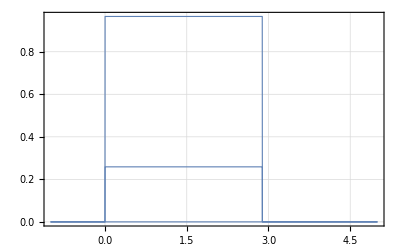

```mathematica
RadPlotOptions[];
Plot[radFld[final, "m", {5,y, 5}], {y, -1, 5}]
```

```mathematica
(* 2 segments of the Halbach array by hand *)
```

```mathematica
(* initialize variables *)
φ = 0
dφ = π/6
R = 10
mx1 = Cos[φ+dφ/2]
my1 =Sin[φ+dφ/2]
mz1 = 0

(* create first segment, place same shape at z=0, z=R *)
segment1 = {{{{R*Cos[φ], R*Sin[φ]}, {R*Cos[φ]/2, R*Sin[φ]/2}, {R*Cos[φ +dφ]/2, R*Sin[φ + dφ]/2}, {R*Cos[φ +dφ], R*Sin[φ + dφ]}}, 0}}
segment1 = Append[segment1, {segment1[[1]][[1]], R}]

(* Iterate on the variables for the second segment *)
φ += dφ
mx2 = Cos[φ+dφ/2]
my2 =Sin[φ+dφ/2]
mz2 = 0

(* add new segments at z=0, z=R *)
segment2 = {{{{R*Cos[φ], R*Sin[φ]}, {R*Cos[φ]/2, R*Sin[φ]/2}, {R*Cos[φ +dφ]/2, R*Sin[φ + dφ]/2}, {R*Cos[φ +dφ], R*Sin[φ + dφ]}}, 0}}
segment2 = Append[segment2, {segment2[[1]][[1]], R}]
Print["segment is now: ", segment2]

(* first attempt to create segments, then define group for segments *)
s1 = radObjMltExtPgn[segment1, {mx1, my1, mz1}]
s2 = radObjMltExtPgn[segment2, {mx2, my2, mz2}]
group = radObjCnt[{s1, s2}]


(* color the object *)
radObjDrwAtr[group, {0, 0.5, 0.8}]

(* plot + show the object *)
RadPlot3DOptions[];
s = radObjDrw[group];
Show[Graphics3D[s]]
```

0

π/6

10

(1+√3)/(2 √2)

(-1+√3)/(2 √2)

0

{{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},0}}

{{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},0},{{{10,0},{5,0},{(5 √3)/2,5/2},{5 √3,5}},10}}

π/6

1/(√2)

1/(√2)

0

{{{{5 √3,5},{(5 √3)/2,5/2},{5/2,(5 √3)/2},{5,5 √3}},0}}

{{{{5 √3,5},{(5 √3)/2,5/2},{5/2,(5 √3)/2},{5,5 √3}},0},{{{5 √3,5},{(5 √3)/2,5/2},{5/2,(5 √3)/2},{5,5 √3}},10}}

segment is now: {{{{5 √3,5},{(5 √3)/2,5/2},{5/2,(5 √3)/2},{5,5 √3}},0},{{{5 √3,5},{(5 √3)/2,5/2},{5/2,(5 √3)/2},{5,5 √3}},10}}

6

8

9

9

-Graphics3D-

```mathematica
(* Plot the magnetic field's x-component *)
```

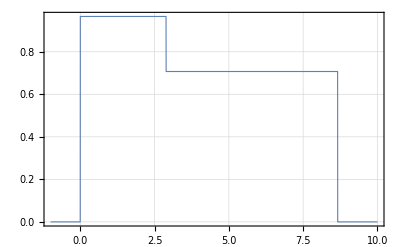

```mathematica
RadPlotOptions[];
Plot[radFld[group, "mx", {5,y, 5}], {y, -1, 10}]
```

```mathematica
(* Draw all 12 segments of the array, outward pointing magnetization *)
```

```mathematica
(* initialize variables *)
φ = 0
dφ = π/6
R = 25.4
halbach = radObjCnt[{}]

For[i=1, i< 13, i++,
(* set magnetization *)
mx = Cos[φ+dφ/2];
my =Sin[φ+dφ/2];
mz = 0;

(* create segment geometry *)
segment = {{{{R*Cos[φ], R*Sin[φ]}, {R*Cos[φ]/2, R*Sin[φ]/2}, {R*Cos[φ +dφ]/2, R*Sin[φ + dφ]/2}, {R*Cos[φ +dφ], R*Sin[φ + dφ]}}, -R/2}};
segment = Append[segment, {segment[[1]][[1]], R/2}];
created = radObjMltExtPgn[segment, {mx, my, mz}];

(* iterate on variables *) 
φ += dφ;

(* add to group *)
radObjAddToCnt[halbach, {created}];
]

(* color the object *)
radObjDrwAtr[halbach, {0, 0.5, 0.8}];

(* plot + show the object *)
RadPlot3DOptions[];
g = radObjDrw[halbach];
Show[Graphics3D[g]]
```

0

π/6

25.4

10

-Graphics3D-

```mathematica
(* Create new Halbach array with spatially rotating magnetization *)
```

```mathematica
(* initialize variables *)
φ = 0
dφ = π/6
θ=π/12
dθ = π/2
(* outer radius *)
R = 25.4
halbach = radObjCnt[{}]

For[i=1, i< 13, i++,
(* set magnetization *)
mx = Cos[θ];
my =Sin[θ];
mz = 0;

Print["Magnetization angle for ", i," is: ", θ];

(* create segment geometry *)
segment = {{{{R*Cos[φ], R*Sin[φ]}, {R*Cos[φ]/2, R*Sin[φ]/2}, {R*Cos[φ +dφ]/2, R*Sin[φ + dφ]/2}, {R*Cos[φ +dφ], R*Sin[φ + dφ]}}, -R/2}};
segment = Append[segment, {segment[[1]][[1]], R/2}];
created = radObjMltExtPgn[segment, {mx, my, mz}];

(* iterate on variables *) 
φ += dφ;
θ+=dφ + dθ;

(* add to group *)
radObjAddToCnt[halbach, {created}];
]

(* color the object *)
radObjDrwAtr[halbach, {0, 0.5, 0.8}];

(* plot + show the object *)
RadPlot3DOptions[];
g = radObjDrw[halbach];
Show[Graphics3D[g]]
```

0

π/6

π/12

π/2

25.4

35

Magnetization angle for 1 is: π/12

Magnetization angle for 2 is: (3 π)/4

Magnetization angle for 3 is: (17 π)/12

Magnetization angle for 4 is: (25 π)/12

Magnetization angle for 5 is: (11 π)/4

Magnetization angle for 6 is: (41 π)/12

Magnetization angle for 7 is: (49 π)/12

Magnetization angle for 8 is: (19 π)/4

Magnetization angle for 9 is: (65 π)/12

Magnetization angle for 10 is: (73 π)/12

Magnetization angle for 11 is: (27 π)/4

Magnetization angle for 12 is: (89 π)/12

-Graphics3D-

```mathematica
(* Plot the y-component of the magnetic field to demonstrate spatial rotation *)
```

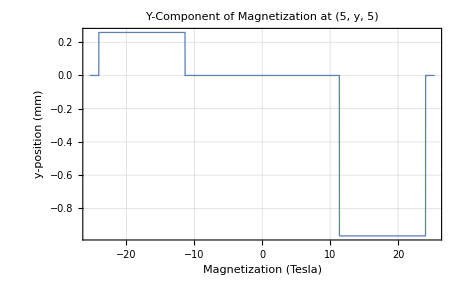

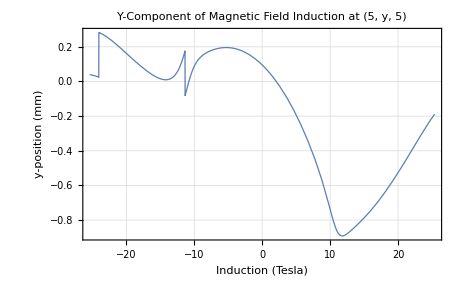

```mathematica
RadPlotOptions[];
Plot[radFld[halbach, "my", {5,y, 5}], {y, -R, R}, PlotLabel->"Y-Component of Magnetization at (5, y, 5)", AxesLabel->{"Magnetization (Tesla)", "y-position (mm)"}]
Plot[radFld[halbach, "By", {5,y, 5}], {y, -R, R}, PlotLabel->"Y-Component of Magnetic Field Induction at (5, y, 5)", AxesLabel->{"Induction (Tesla)", "y-position (mm)"}]
```

```mathematica
(* Plot the B-field *)
```

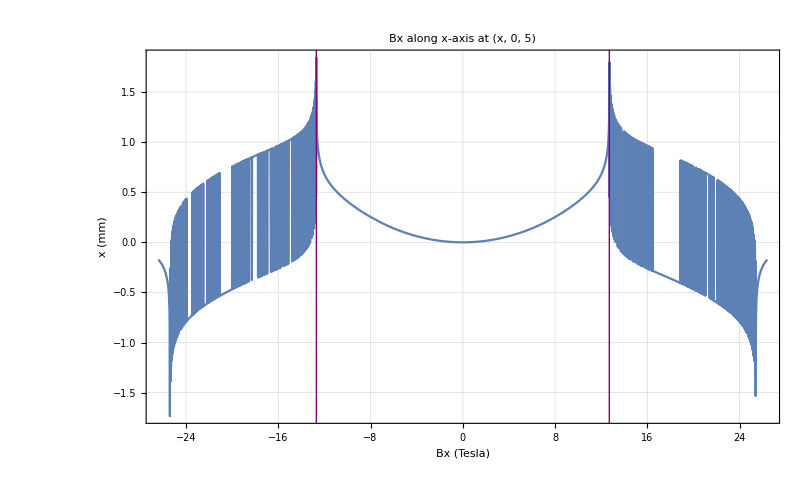

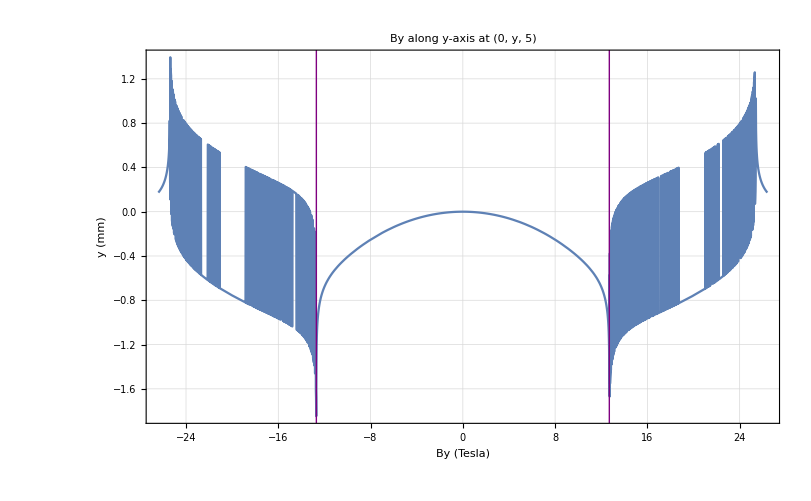

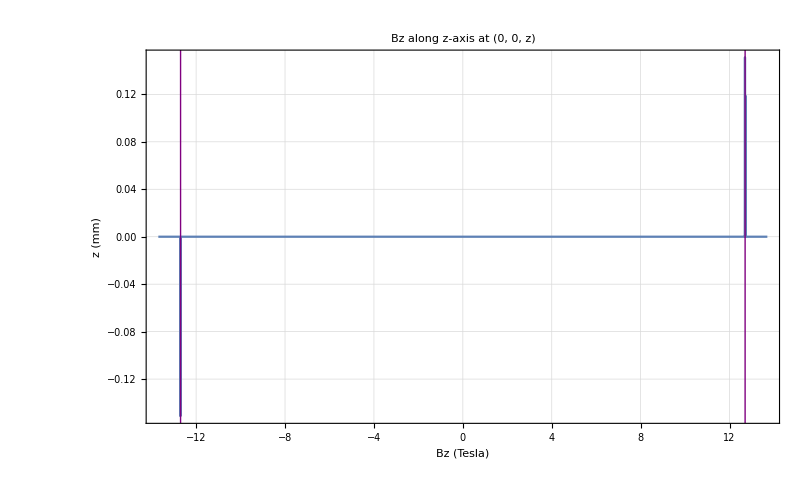

```mathematica
lineStyle={Thick,Purple};

(* draw lines at boundary of the inner radius *)
line1=Line[{{R/2,-10},{R/2,10}}];
line2=Line[{{-R/2,-10},{-R/2,10}}];

Plot[radFld[halbach, "Bx", {x, 0, 5}], {x, -R -1, R + 1}, PlotLabel->"Bx along x-axis at (x, 0, 5)", AxesLabel->{"Bx (Tesla)", "x (mm)"}, Epilog->{Directive[lineStyle], line1, line2}]

Plot[radFld[halbach, "By", {0, y, 5}], {y, -R -1, R + 1}, PlotLabel->"By along y-axis at (0, y, 5)", AxesLabel->{"By (Tesla)", "y (mm)"}, Epilog->{Directive[lineStyle], line1, line2}]

Plot[radFld[halbach, "Bz", {0, 0, z}], {z, -R/2  - 1, R/2 + 1}, PlotLabel->"Bz along z-axis at (0, 0, z)", AxesLabel->{"Bz (Tesla)", "z (mm)"},Epilog->{Directive[lineStyle], Line[{{-R/2, -10}, {-R/2, 10}}], Line[{{R/2, -10}, {R/2, 10}}]}]
```

```mathematica
(* Plot the norm of the B-field *)
```

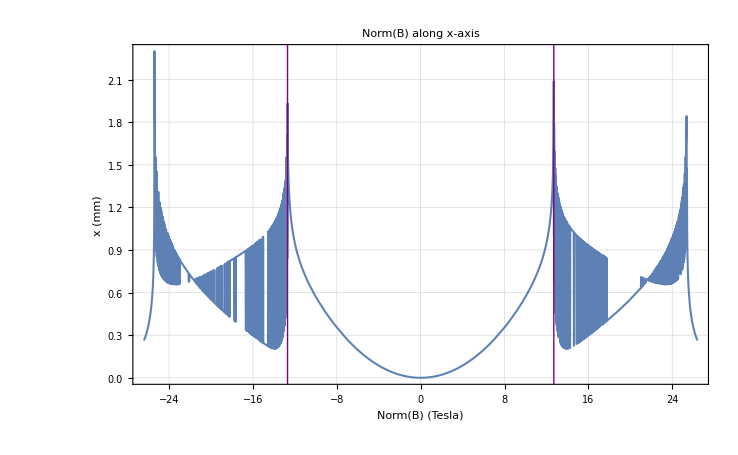

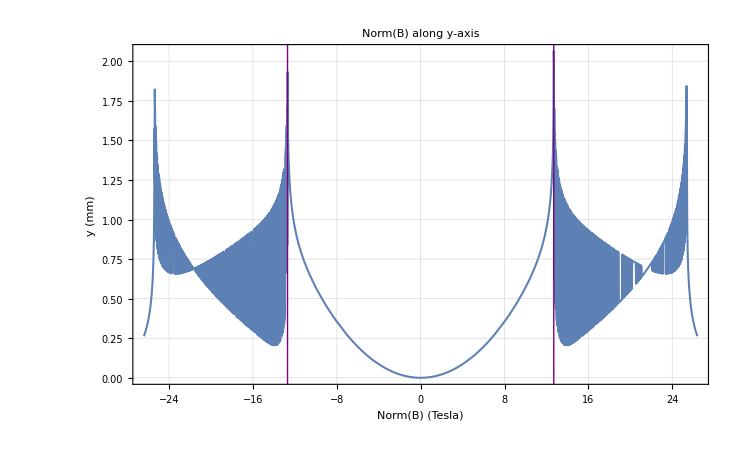

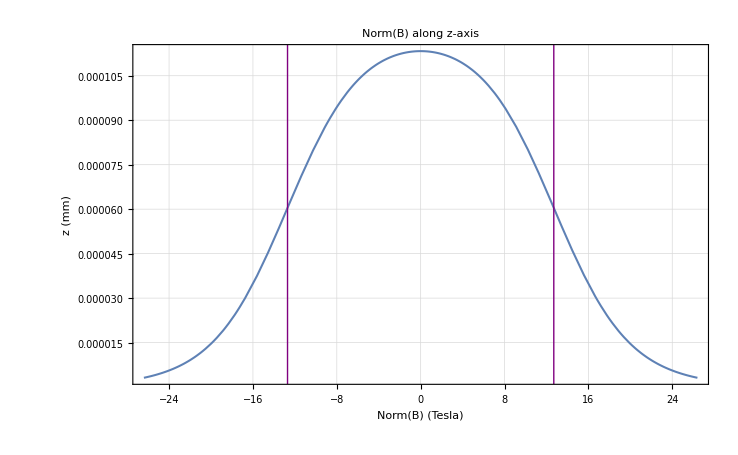

```mathematica
(* define norm function *)
norm [x_, y_, z_]:= Module[{bx, by, bz}, 
bx = radFld[halbach, "hx", {x, y, z}];
by = radFld[halbach, "hy", {x, y, z}];
bz = radFld[halbach, "hz", {x, y, z}];
Return[Sqrt[bx^2 + by^2 + bz^2]];
]

lineStyle={Thick,Purple};
line1=Line[{{R/2,-10},{R/2,10}}];
line2=Line[{{-R/2,-10},{-R/2,10}}];

Plot[norm[x, 0, 5], {x, -R-1, R+1}, PlotLabel->"Norm(B) along x-axis", AxesLabel->{"Norm(B) (Tesla)", "x (mm)"},Epilog->{Directive[lineStyle],line1,line2}]

Plot[norm[0, y, 5], {y,-R-1, R+1}, PlotLabel->"Norm(B) along y-axis", AxesLabel->{"Norm(B) (Tesla)", "y (mm)"},Epilog->{Directive[lineStyle],line1,line2}]

Plot[norm[0.1, 0.1, z], {z, -R - 1, R+ 1}, PlotLabel->"Norm(B) along z-axis", AxesLabel->{"Norm(B) (Tesla)", "z (mm)"},Epilog->{Directive[lineStyle],Line[{{-R/2,-10},{-R/2,10}}],Line[{{R/2,-10},{R/2,10}}]}]
```

```mathematica
(* Visualize magnetization*)
```

```mathematica
(* initialize variables *)
xStart = -R;
yStart = -R;
zPos = 0
m=18;
mxMatrix = {};
myMatrix = {};

(* iterate through points on x, y, z axes *)
For[i=1, i≤ m, i++,
mxMatrix=Append[mxMatrix, {}];
For[j=1, j≤ m, j++,
mxMatrix[[i]]=Append[mxMatrix[[i]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number m to get the step size, and iterate over the steps *)
radFld[halbach, "mx", {xStart + (2*R)/(m-1)*(i-1), yStart + (2*R)/(m-1)*(j-1), zPos}]];
];
];

For[i=1, i≤ m, i++, 
myMatrix=Append[myMatrix, {}];
For[j=1, j≤ m, j++,
myMatrix[[i]]=Append[myMatrix[[i]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number m to get the step size, and iterate over the steps *)
radFld[halbach, "my", {xStart + (2*R)/(m-1)*(i-1), yStart + (2*R)/(m-1)*(j-1), zPos}]];
];
];

Print["mxMatrix: ", MatrixForm[mxMatrix]]
Print["myMatrix: ", MatrixForm[myMatrix]]

SetDirectory["/Users/andrewwinnicki/Desktop/Andrew/2019-2020/Doyle Lab/Modeling Magnetic Lens/magnetic_lens_monte_carlo/m_matrix"];
Export["mxMatrix.fits",mxMatrix];
Export["myMatrix.fits",myMatrix];
```

0

mxMatrix: (1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | -0.707107 | -0.707107 | 0.965926 | 0.965926 | 0.965926 | -0.258819 | -0.258819 | -0.258819 | -0.707107 | -0.707107 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 0.965926 | 0.965926 | 0.965926 | -0.258819 | -0.258819 | -0.258819 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | -0.258819 | -0.258819 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 0.965926 | 0.965926 | 1.×10^-17
1.×10^-17 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 1.×10^-17
1.×10^-17 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 1.×10^-17
1.×10^-17 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 1.×10^-17
1.×10^-17 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 1.×10^-17
1.×10^-17 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 1.×10^-17
1.×10^-17 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 1.×10^-17
1.×10^-17 | 0.965926 | 0.965926 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.258819 | -0.258819 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | -0.258819 | -0.258819 | -0.258819 | 0.965926 | 0.965926 | 0.965926 | -0.707107 | -0.707107 | -0.707107 | -0.707107 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | -0.707107 | -0.707107 | -0.258819 | -0.258819 | -0.258819 | 0.965926 | 0.965926 | 0.965926 | -0.707107 | -0.707107 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.707107 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | -0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.258819 | -0.258819 | -0.258819 | -0.258819 | 0.965926 | 0.965926 | 0.965926 | 0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17)

myMatrix: (1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | 0.707107 | 0.707107 | 0.258819 | 0.258819 | 0.258819 | -0.965926 | -0.965926 | -0.965926 | 0.707107 | 0.707107 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.258819 | 0.258819 | 0.258819 | -0.965926 | -0.965926 | -0.965926 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | -0.965926 | -0.965926 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 0.258819 | 0.258819 | 1.×10^-17
1.×10^-17 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 1.×10^-17
1.×10^-17 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 1.×10^-17
1.×10^-17 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 1.×10^-17
1.×10^-17 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 1.×10^-17
1.×10^-17 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 1.×10^-17
1.×10^-17 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 1.×10^-17
1.×10^-17 | 0.258819 | 0.258819 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | -0.965926 | -0.965926 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | -0.965926 | -0.965926 | -0.965926 | 0.258819 | 0.258819 | 0.258819 | 0.707107 | 0.707107 | 0.707107 | 0.707107 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | 0.707107 | 0.707107 | -0.965926 | -0.965926 | -0.965926 | 0.258819 | 0.258819 | 0.258819 | 0.707107 | 0.707107 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 0.707107 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 0.707107 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | -0.965926 | -0.965926 | -0.965926 | -0.965926 | 0.258819 | 0.258819 | 0.258819 | 0.258819 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17
1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17 | 1.×10^-17)

```mathematica
(* Make a matrix of the B-field values for use with Python, export to a data file *)
```

```mathematica
(* initialize variables *)
xStart = -R/2;
yStart = -R/2;
zStart = -R/2;
m=18;
bxMatrix = {};
byMatrix = {};
bzMatrix = {};
normbMatrix = {};
bMatrix = {};

(* iterate through points on x, y, z axes *)
For[i=1, i≤ m, i++,
bxMatrix=Append[bxMatrix, {}];
For[j=1, j≤ m, j++,
bxMatrix[[i]]=Append[bxMatrix[[i]], {}];
For[k=1,k≤ m, k++,
bxMatrix[[i]][[j]]=Append[bxMatrix[[i]][[j]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number m to get the step size, and iterate over the steps *)
radFld[halbach, "hx", {xStart + R/(m-1)*(i-1), yStart + R/(m-1)*(j-1), zStart+ R/(m-1)*(k-1)}]];
];
];
];

For[i=1, i≤ m, i++, 
byMatrix=Append[byMatrix, {}];
For[j=1, j≤ m, j++,
byMatrix[[i]]=Append[byMatrix[[i]], {}];
For[k=1,k≤ m, k++,
byMatrix[[i]][[j]]=Append[byMatrix[[i]][[j]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number m to get the step size, and iterate over the steps *)
radFld[halbach, "hy", {xStart + R/(m-1)*(i-1), yStart + R/(m-1)*(j-1), zStart+ R/(m-1)*(k-1)}]];
];
];
];

For[i=1, i≤ m, i++, 
bzMatrix=Append[bzMatrix, {}];
For[j=1, j≤ m, j++,
bzMatrix[[i]]=Append[bzMatrix[[i]], {}];
For[k=1,k≤ m, k++,
bzMatrix[[i]][[j]]=Append[bzMatrix[[i]][[j]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number m to get the step size, and iterate over the steps *)
radFld[halbach, "hz", {xStart + R/(m-1)*(i-1), yStart + R/(m-1)*(j-1), zStart+ R/(m-1)*(k-1)}]];
];
];
];

For[i=1, i≤ m, i++, 
normbMatrix=Append[normbMatrix, {}];
For[j=1, j≤ m, j++,
normbMatrix[[i]]=Append[normbMatrix[[i]], {}];
For[k=1,k≤ m, k++,
normbMatrix[[i]][[j]]=Append[normbMatrix[[i]][[j]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number m to get the step size, and iterate over the steps *)
norm[xStart + R/(m-1)*(i-1), yStart + R/(m-1)*(j-1), zStart+ R/(m-1)*(k-1)]]
];
];
];

(* iterate through points on x, y, z axes *)
For[i=1, i≤ m, i++,
bMatrix=Append[bMatrix, {}];
For[j=1, j≤ m, j++,
bMatrix[[i]]=Append[bMatrix[[i]], {}];
For[k=1,k≤ m, k++,
bMatrix[[i]][[j]]=Append[bMatrix[[i]][[j]],
(* here, we take the the length of the interval we want to iterate over, divide by the spacing number m to get the step size, and iterate over the steps *)
radFld[halbach, "h", {xStart + R/(m-1)*(i-1), yStart + R/(m-1)*(j-1), zStart+ R/(m-1)*(k-1)}]];
];
];
];

Print["bxMatrix: ", MatrixForm[bxMatrix]]
Print["byMatrix: ", MatrixForm[byMatrix]]
Print["bzMatrix: ", MatrixForm[bzMatrix]]
Print["normbMatrix: ", MatrixForm[normbMatrix]]
Print["bMatrix: ", MatrixForm[bMatrix]]

SetDirectory["/Users/andrewwinnicki/Desktop/Andrew/2019-2020/Doyle Lab/Modeling Magnetic Lens/magnetic_lens_monte_carlo/bmatrix"];
Export["bxMatrix.fits",bxMatrix];
Export["byMatrix.fits",byMatrix];
Export["bzMatrix.fits",bzMatrix];
Export["normbMatrix.fits",normbMatrix];
Export["bMatrix.fits",bMatrix];
```

bxMatrix: ((0.248943
0.317619
0.373248
0.412519
0.438536
0.455315
0.465845
0.472001
0.474842
0.474842
0.472001
0.465845
0.455315
0.438536
0.412519
0.373248
0.317619
0.248943) | (0.251983
0.325026
0.38181
0.420573
0.44591
0.46221
0.472452
0.478451
0.481225
0.481225
0.478451
0.472452
0.46221
0.44591
0.420573
0.38181
0.325026
0.251983) | (0.264162
0.355626
0.414519
0.450775
0.473895
0.488803
0.498248
0.503823
0.506413
0.506413
0.503823
0.498248
0.488803
0.473895
0.450775
0.414519
0.355626
0.264162) | (0.288542
0.42908
0.47916
0.508555
0.527881
0.54073
0.549058
0.554049
0.556387
0.556387
0.554049
0.549058
0.54073
0.527881
0.508555
0.47916
0.42908
0.288542) | (0.0032602
-0.0862845
-0.0710099
-0.0519872
-0.037051
-0.0263788
-0.0192042
-0.0148182
-0.0127423
-0.0127423
-0.0148182
-0.0192042
-0.0263788
-0.037051
-0.0519872
-0.0710099
-0.0862845
0.0032602) | (-0.0257768
-0.108816
-0.113876
-0.102116
-0.0903457
-0.0813045
-0.0750386
-0.071151
-0.069298
-0.069298
-0.071151
-0.0750386
-0.0813045
-0.0903457
-0.102116
-0.113876
-0.108816
-0.0257768) | (-0.0594931
-0.1713
-0.176426
-0.165422
-0.154526
-0.146204
-0.140459
-0.136902
-0.135209
-0.135209
-0.136902
-0.140459
-0.146204
-0.154526
-0.165422
-0.176426
-0.1713
-0.0594931) | (-0.0605529
-0.192567
-0.182107
-0.166607
-0.154685
-0.146328
-0.140779
-0.13741
-0.135821
-0.135821
-0.13741
-0.140779
-0.146328
-0.154685
-0.166607
-0.182107
-0.192567
-0.0605529) | (-0.000960409
-0.105536
-0.0687263
-0.0472996
-0.0339193
-0.0253221
-0.0198591
-0.016621
-0.0151123
-0.0151123
-0.016621
-0.0198591
-0.0253221
-0.0339193
-0.0472996
-0.0687263
-0.105536
-0.000960411) | (0.227008
0.342396
0.387357
0.410511
0.424181
0.432659
0.437921
0.440992
0.442411
0.442411
0.440992
0.437921
0.432659
0.424181
0.410511
0.387357
0.342396
0.227008) | (0.138985
0.186197
0.2187
0.238791
0.251252
0.259068
0.263918
0.26674
0.26804
0.26804
0.26674
0.263918
0.259068
0.251252
0.238791
0.2187
0.186197
0.138985) | (0.10883
0.14237
0.167483
0.184058
0.194722
0.201548
0.205829
0.208332
0.209487
0.209487
0.208332
0.205829
0.201548
0.194722
0.184058
0.167483
0.14237
0.10883) | (0.11908
0.169521
0.19569
0.210123
0.219117
0.224918
0.228598
0.230766
0.23177
0.23177
0.230766
0.228598
0.224918
0.219117
0.210123
0.19569
0.169521
0.11908) | (0.189422
0.320023
0.34404
0.355847
0.363323
0.368256
0.37143
0.373312
0.374186
0.374186
0.373312
0.37143
0.368256
0.363323
0.355847
0.34404
0.320023
0.189422) | (-0.040498
-0.111169
-0.10806
-0.100179
-0.0938692
-0.0894453
-0.0865595
-0.0848496
-0.084059
-0.084059
-0.0848496
-0.0865595
-0.0894453
-0.0938692
-0.100179
-0.10806
-0.111169
-0.040498) | (0.0107802
-0.00558788
-0.00374742
0.00351591
0.0099446
0.0144964
0.0174166
0.019111
0.019882
0.019882
0.019111
0.0174166
0.0144964
0.0099446
0.00351591
-0.00374742
-0.00558788
0.0107802) | (0.05604
0.0673756
0.080251
0.0917504
0.100122
0.105575
0.108881
0.110722
0.111538
0.111538
0.110722
0.108881
0.105575
0.100122
0.0917504
0.080251
0.0673756
0.05604) | (0.103985
0.137295
0.164199
0.182767
0.19443
0.201363
0.205311
0.207412
0.208317
0.208317
0.207412
0.205311
0.201363
0.19443
0.182767
0.164199
0.137295
0.103985)
(0.296848
0.38708
0.455283
0.500483
0.529523
0.548064
0.559675
0.566464
0.569599
0.569599
0.566464
0.559675
0.548064
0.529523
0.500483
0.455283
0.38708
0.296848) | (0.292739
0.377762
0.444606
0.490324
0.520048
0.539061
0.55095
0.55789
0.56109
0.56109
0.55789
0.55095
0.539061
0.520048
0.490324
0.444606
0.377762
0.292739) | (0.30087
0.394045
0.463046
0.508366
0.537457
0.556038
0.567677
0.574482
0.577625
0.577625
0.574482
0.567677
0.556038
0.537457
0.508366
0.463046
0.394045
0.30087) | (0.338665
0.471041
0.545351
0.588843
0.616106
0.633541
0.644527
0.650984
0.653976
0.653976
0.650984
0.644527
0.633541
0.616106
0.588843
0.545351
0.471041
0.338665) | (0.471571
0.753246
0.822605
0.861538
0.88612
0.902033
0.912163
0.918159
0.920948
0.920948
0.918159
0.912163
0.902033
0.88612
0.861538
0.822605
0.753246
0.471571) | (0.475256
0.786852
0.84211
0.875955
0.897974
0.91243
0.921705
0.927221
0.929792
0.929792
0.927221
0.921705
0.91243
0.897974
0.875955
0.84211
0.786852
0.475256) | (0.392347
0.627536
0.683933
0.715917
0.736405
0.74976
0.758294
0.763359
0.765717
0.765717
0.763359
0.758294
0.74976
0.736405
0.715917
0.683933
0.627536
0.392347) | (0.356406
0.551811
0.616071
0.648888
0.668692
0.681207
0.689072
0.693697
0.695841
0.695841
0.693697
0.689072
0.681207
0.668692
0.648888
0.616071
0.551811
0.356406) | (0.320971
0.484192
0.551141
0.58382
0.602597
0.614107
0.621211
0.625344
0.62725
0.62725
0.625344
0.621211
0.614107
0.602597
0.58382
0.551141
0.484192
0.320971) | (0.227268
0.324385
0.376981
0.404954
0.421221
0.431156
0.437251
0.44078
0.442403
0.442403
0.44078
0.437251
0.431156
0.421221
0.404954
0.376981
0.324385
0.227268) | (0.133669
0.177813
0.209249
0.229013
0.241342
0.249097
0.253914
0.256718
0.258009
0.258009
0.256718
0.253914
0.249097
0.241342
0.229013
0.209249
0.177813
0.133669) | (0.0724167
0.091509
0.107294
0.118856
0.126824
0.132129
0.135528
0.137538
0.13847
0.13847
0.137538
0.135528
0.132129
0.126824
0.118856
0.107294
0.091509
0.0724167) | (0.0279159
0.0318267
0.0364452
0.041408
0.0455471
0.0485876
0.0506374
0.05188
0.0524628
0.0524628
0.05188
0.0506374
0.0485876
0.0455471
0.041408
0.0364452
0.0318267
0.0279159) | (-0.0680646
-0.139734
-0.142352
-0.141434
-0.139871
-0.138505
-0.137524
-0.136918
-0.136632
-0.136632
-0.136918
-0.137524
-0.138505
-0.139871
-0.141434
-0.142352
-0.139734
-0.0680646) | (0.00607108
0.0105944
0.0114089
0.0122593
0.0130576
0.0136267
0.0139706
0.0141511
0.0142254
0.0142254
0.0141511
0.0139706
0.0136267
0.0130576
0.0122593
0.0114089
0.0105944
0.00607108) | (0.0305005
0.0484147
0.0581396
0.0625361
0.0644142
0.065122
0.0653108
0.0653065
0.0652705
0.0652705
0.0653065
0.0653108
0.065122
0.0644142
0.0625361
0.0581396
0.0484147
0.0305005) | (0.0603476
0.0908076
0.110629
0.12047
0.124693
0.126269
0.126709
0.126736
0.126684
0.126684
0.126736
0.126709
0.126269
0.124693
0.12047
0.110629
0.0908076
0.0603476) | (0.101173
0.150723
0.182686
0.198626
0.205652
0.208445
0.209375
0.209577
0.209575
0.209575
0.209577
0.209375
0.208445
0.205652
0.198626
0.182686
0.150723
0.101173)
(0.342123
0.471648
0.549592
0.594741
0.622696
0.640513
0.651742
0.658345
0.661405
0.661405
0.658345
0.651742
0.640513
0.622696
0.594741
0.549592
0.471648
0.342123) | (0.322568
0.4277
0.502552
0.550102
0.580181
0.599307
0.611276
0.618272
0.621501
0.621501
0.618272
0.611276
0.599307
0.580181
0.550102
0.502552
0.4277
0.322568) | (0.311084
0.40573
0.477699
0.525485
0.556136
0.575661
0.587863
0.594984
0.598268
0.598268
0.594984
0.587863
0.575661
0.556136
0.525485
0.477699
0.40573
0.311084) | (0.329251
0.439102
0.515273
0.563177
0.593409
0.612611
0.624616
0.631629
0.634864
0.634864
0.631629
0.624616
0.612611
0.593409
0.563177
0.515273
0.439102
0.329251) | (0.382247
0.540973
0.62539
0.672838
0.701919
0.720294
0.731793
0.738522
0.74163
0.74163
0.738522
0.731793
0.720294
0.701919
0.672838
0.62539
0.540973
0.382247) | (0.374666
0.535312
0.617962
0.663089
0.690453
0.707702
0.718498
0.724821
0.727744
0.727744
0.724821
0.718498
0.707702
0.690453
0.663089
0.617962
0.535312
0.374666) | (0.324984
0.45399
0.528463
0.570346
0.595742
0.611692
0.621647
0.627468
0.630156
0.630156
0.627468
0.621647
0.611692
0.595742
0.570346
0.528463
0.45399
0.324984) | (0.281944
0.387572
0.453935
0.492258
0.515404
0.529821
0.53876
0.543966
0.546364
0.546364
0.543966
0.53876
0.529821
0.515404
0.492258
0.453935
0.387572
0.281944) | (0.233839
0.317392
0.373236
0.406394
0.426432
0.438838
0.446488
0.450924
0.452964
0.452964
0.450924
0.446488
0.438838
0.426432
0.406394
0.373236
0.317392
0.233839) | (0.168845
0.22467
0.264756
0.2899
0.305461
0.315179
0.321188
0.324674
0.326277
0.326277
0.324674
0.321188
0.315179
0.305461
0.2899
0.264756
0.22467
0.168845) | (0.0958211
0.123385
0.145095
0.160096
0.169998
0.176418
0.180469
0.182846
0.183944
0.183944
0.182846
0.180469
0.176418
0.169998
0.160096
0.145095
0.123385
0.0958211) | (0.0218343
0.0221901
0.0253024
0.0295761
0.0333892
0.0362544
0.0382038
0.0393914
0.0399499
0.0399499
0.0393914
0.0382038
0.0362544
0.0333892
0.0295761
0.0253024
0.0221901
0.0218343) | (-0.0713809
-0.116825
-0.134646
-0.14033
-0.14204
-0.142469
-0.142512
-0.14247
-0.142437
-0.142437
-0.14247
-0.142512
-0.142469
-0.14204
-0.14033
-0.134646
-0.116825
-0.0713809) | (-0.211706
-0.365109
-0.39643
-0.40787
-0.413274
-0.416183
-0.417847
-0.41878
-0.419203
-0.419203
-0.41878
-0.417847
-0.416183
-0.413274
-0.40787
-0.39643
-0.365109
-0.211706) | (0.0635063
0.170054
0.159866
0.150472
0.144106
0.139882
0.137145
0.135501
0.134728
0.134728
0.135501
0.137145
0.139882
0.144106
0.150472
0.159866
0.170054
0.0635063) | (0.0421533
0.102619
0.113972
0.110908
0.105748
0.101294
0.0980479
0.0959807
0.094982
0.094982
0.0959807
0.0980479
0.101294
0.105748
0.110908
0.113972
0.102619
0.0421533) | (0.0524168
0.107155
0.129127
0.131774
0.128532
0.124487
0.121161
0.118924
0.117815
0.117815
0.118924
0.121161
0.124487
0.128532
0.131774
0.129127
0.107155
0.0524168) | (0.0892201
0.167748
0.19867
0.2048
0.203042
0.19956
0.196391
0.194161
0.193031
0.193031
0.194161
0.196391
0.19956
0.203042
0.2048
0.19867
0.167748
0.0892201)
(0.393471
0.612166
0.677809
0.712912
0.735286
0.74999
0.75945
0.765081
0.767707
0.767707
0.765081
0.75945
0.74999
0.735286
0.712912
0.677809
0.612166
0.393471) | (0.347029
0.496163
0.570561
0.611907
0.637658
0.65419
0.664645
0.670801
0.673653
0.673653
0.670801
0.664645
0.65419
0.637658
0.611907
0.570561
0.496163
0.347029) | (0.289728
0.384401
0.450591
0.493017
0.520276
0.537801
0.548836
0.555306
0.558296
0.558296
0.555306
0.548836
0.537801
0.520276
0.493017
0.450591
0.384401
0.289728) | (0.272744
0.353283
0.415536
0.4578
0.48542
0.503237
0.514454
0.521025
0.524061
0.524061
0.521025
0.514454
0.503237
0.48542
0.4578
0.415536
0.353283
0.272744) | (0.277816
0.363263
0.426966
0.469124
0.496415
0.513975
0.525026
0.531502
0.534493
0.534493
0.531502
0.525026
0.513975
0.496415
0.469124
0.426966
0.363263
0.277816) | (0.271266
0.356358
0.418875
0.459652
0.485853
0.502665
0.513238
0.519433
0.522295
0.522295
0.519433
0.513238
0.502665
0.485853
0.459652
0.418875
0.356358
0.271266) | (0.246258
0.321516
0.378252
0.415865
0.440132
0.455701
0.465483
0.47121
0.473854
0.473854
0.47121
0.465483
0.455701
0.440132
0.415865
0.378252
0.321516
0.246258) | (0.212137
0.27498
0.32368
0.356669
0.378115
0.391884
0.400523
0.405574
0.407904
0.407904
0.405574
0.400523
0.391884
0.378115
0.356669
0.32368
0.27498
0.212137) | (0.169694
0.218576
0.257293
0.284048
0.301605
0.312905
0.319995
0.324137
0.326047
0.326047
0.324137
0.319995
0.312905
0.301605
0.284048
0.257293
0.218576
0.169694) | (0.116863
0.149214
0.17545
0.194072
0.206521
0.21462
0.219731
0.222726
0.224108
0.224108
0.222726
0.219731
0.21462
0.206521
0.194072
0.17545
0.149214
0.116863) | (0.0548165
0.0682632
0.0797863
0.088595
0.0948692
0.0991359
0.101904
0.103552
0.104319
0.104319
0.103552
0.101904
0.0991359
0.0948692
0.088595
0.0797863
0.0682632
0.0548165) | (-0.0160537
-0.0252033
-0.0306976
-0.0328622
-0.0333558
-0.0332517
-0.0330198
-0.0328285
-0.0327273
-0.0327273
-0.0328285
-0.0330198
-0.0332517
-0.0333558
-0.0328622
-0.0306976
-0.0252033
-0.0160537) | (-0.0997386
-0.141314
-0.166934
-0.18026
-0.1873
-0.191215
-0.193458
-0.194703
-0.195263
-0.195263
-0.194703
-0.193458
-0.191215
-0.1873
-0.18026
-0.166934
-0.141314
-0.0997386) | (-0.192626
-0.282913
-0.327174
-0.348936
-0.361052
-0.368281
-0.372664
-0.375188
-0.376345
-0.376345
-0.375188
-0.372664
-0.368281
-0.361052
-0.348936
-0.327174
-0.282913
-0.192626) | (-0.272933
-0.4304
-0.473973
-0.497418
-0.512069
-0.521503
-0.527492
-0.531034
-0.53268
-0.53268
-0.531034
-0.527492
-0.521503
-0.512069
-0.497418
-0.473973
-0.4304
-0.272933) | (0.0241463
0.138721
0.123053
0.10391
0.0889641
0.0783989
0.0713739
0.0671177
0.065115
0.065115
0.0671177
0.0713739
0.0783989
0.0889641
0.10391
0.123053
0.138721
0.0241463) | (0.0148077
0.101692
0.104509
0.0893815
0.0748302
0.063786
0.0561884
0.0515008
0.0492746
0.0492746
0.0515008
0.0561884
0.063786
0.0748302
0.0893815
0.104509
0.101692
0.0148077) | (0.0650451
0.20824
0.208558
0.192863
0.178082
0.166776
0.158919
0.154033
0.151701
0.151701
0.154033
0.158919
0.166776
0.178082
0.192863
0.208558
0.20824
0.0650451)
(-0.0604763
-0.204195
-0.18949
-0.171194
-0.157042
-0.147029
-0.140372
-0.136347
-0.134458
-0.134458
-0.136347
-0.140372
-0.147029
-0.157042
-0.171194
-0.18949
-0.204195
-0.0604763) | (0.421241
0.713156
0.757313
0.783748
0.801413
0.81323
0.820875
0.825431
0.827554
0.827554
0.825431
0.820875
0.81323
0.801413
0.783748
0.757313
0.713156
0.421241) | (0.211425
0.283167
0.328574
0.358166
0.377943
0.391042
0.399444
0.404421
0.406733
0.406733
0.404421
0.399444
0.391042
0.377943
0.358166
0.328574
0.283167
0.211425) | (0.192442
0.244306
0.286348
0.316711
0.337535
0.351387
0.360264
0.365514
0.36795
0.36795
0.365514
0.360264
0.351387
0.337535
0.316711
0.286348
0.244306
0.192442) | (0.192197
0.242532
0.284314
0.315001
0.336178
0.350287
0.359329
0.364676
0.367157
0.367157
0.364676
0.359329
0.350287
0.336178
0.315001
0.284314
0.242532
0.192197) | (0.188347
0.237684
0.27863
0.308698
0.329449
0.343273
0.352134
0.357374
0.359805
0.359805
0.357374
0.352134
0.343273
0.329449
0.308698
0.27863
0.237684
0.188347) | (0.174308
0.219463
0.25721
0.285134
0.304485
0.317399
0.325681
0.330579
0.332851
0.332851
0.330579
0.325681
0.317399
0.304485
0.285134
0.25721
0.219463
0.174308) | (0.150332
0.18864
0.220985
0.245179
0.262059
0.273358
0.28061
0.2849
0.286889
0.286889
0.2849
0.28061
0.273358
0.262059
0.245179
0.220985
0.18864
0.150332) | (0.116949
0.146267
0.171241
0.190121
0.203394
0.212313
0.218048
0.221442
0.223017
0.223017
0.221442
0.218048
0.212313
0.203394
0.190121
0.171241
0.146267
0.116949) | (0.0739669
0.0920635
0.107635
0.119574
0.128075
0.133841
0.137571
0.139787
0.140817
0.140817
0.139787
0.137571
0.133841
0.128075
0.119574
0.107635
0.0920635
0.0739669) | (0.0214793
0.0258413
0.0298703
0.0332843
0.0359454
0.0378754
0.0391798
0.0399753
0.04035
0.04035
0.0399753
0.0391798
0.0378754
0.0359454
0.0332843
0.0298703
0.0258413
0.0214793) | (-0.0406034
-0.0534117
-0.06337
-0.0699049
-0.073878
-0.0762446
-0.0776399
-0.0784216
-0.0787738
-0.0787738
-0.0784216
-0.0776399
-0.0762446
-0.073878
-0.0699049
-0.06337
-0.0534117
-0.0406034) | (-0.11251
-0.147877
-0.174614
-0.192022
-0.202893
-0.209653
-0.213803
-0.216197
-0.217294
-0.217294
-0.216197
-0.213803
-0.209653
-0.202893
-0.192022
-0.174614
-0.147877
-0.11251) | (-0.192294
-0.258139
-0.30348
-0.331267
-0.348442
-0.359229
-0.365935
-0.369843
-0.371644
-0.371644
-0.369843
-0.365935
-0.359229
-0.348442
-0.331267
-0.30348
-0.258139
-0.192294) | (-0.277892
-0.388332
-0.450121
-0.485514
-0.507503
-0.521546
-0.530398
-0.535604
-0.538014
-0.538014
-0.535604
-0.530398
-0.521546
-0.507503
-0.485514
-0.450121
-0.388332
-0.277892) | (-0.382265
-0.575337
-0.64263
-0.681575
-0.70664
-0.723029
-0.73351
-0.739725
-0.742616
-0.742616
-0.739725
-0.73351
-0.723029
-0.70664
-0.681575
-0.64263
-0.575337
-0.382265) | (-0.117944
-0.0398919
-0.103268
-0.143974
-0.171025
-0.188993
-0.200587
-0.207498
-0.210722
-0.210722
-0.207498
-0.200587
-0.188993
-0.171025
-0.143974
-0.103268
-0.0398919
-0.117944) | (-0.486022
-0.754942
-0.830251
-0.874091
-0.902749
-0.921716
-0.933952
-0.941252
-0.94466
-0.94466
-0.941252
-0.933952
-0.921716
-0.902749
-0.874091
-0.830251
-0.754942
-0.486022)
(0.0100177
-0.00836774
-0.00910032
-0.00303733
0.00309812
0.0078056
0.0110284
0.0129979
0.0139257
0.0139257
0.0129979
0.0110284
0.0078056
0.00309812
-0.00303733
-0.00910032
-0.00836774
0.0100177) | (-0.0281821
-0.103169
-0.0959667
-0.0858552
-0.0775781
-0.0716054
-0.06761
-0.0651921
-0.0640578
-0.0640578
-0.0651921
-0.06761
-0.0716054
-0.0775781
-0.0858552
-0.0959667
-0.103169
-0.0281821) | (0.0711716
0.0783155
0.0929718
0.106495
0.116789
0.124035
0.128829
0.131714
0.133064
0.133064
0.131714
0.128829
0.124035
0.116789
0.106495
0.0929718
0.0783155
0.0711716) | (0.0995908
0.121539
0.14156
0.157778
0.169787
0.178153
0.183659
0.186964
0.188508
0.188508
0.186964
0.183659
0.178153
0.169787
0.157778
0.14156
0.121539
0.0995908) | (0.112421
0.138492
0.161388
0.179467
0.1927
0.201869
0.207886
0.211493
0.213177
0.213177
0.211493
0.207886
0.201869
0.1927
0.179467
0.161388
0.138492
0.112421) | (0.116879
0.14421
0.168104
0.186878
0.200575
0.210048
0.21626
0.219981
0.221719
0.221719
0.219981
0.21626
0.210048
0.200575
0.186878
0.168104
0.14421
0.116879) | (0.112139
0.138234
0.161099
0.179118
0.192294
0.20142
0.207408
0.210996
0.212671
0.212671
0.210996
0.207408
0.20142
0.192294
0.179118
0.161099
0.138234
0.112139) | (0.0978218
0.120369
0.14021
0.155934
0.167485
0.175509
0.180781
0.183943
0.18542
0.18542
0.183943
0.180781
0.175509
0.167485
0.155934
0.14021
0.120369
0.0978218) | (0.073961
0.0908448
0.10576
0.117647
0.12642
0.132535
0.13656
0.138977
0.140106
0.140106
0.138977
0.13656
0.132535
0.12642
0.117647
0.10576
0.0908448
0.073961) | (0.0405562
0.0496584
0.0577432
0.0642413
0.0690803
0.0724775
0.0747263
0.0760809
0.076715
0.076715
0.0760809
0.0747263
0.0724775
0.0690803
0.0642413
0.0577432
0.0496584
0.0405562) | (-0.0023922
-0.00340588
-0.00417215
-0.00461786
-0.00481851
-0.00488271
-0.00488867
-0.00487822
-0.00486977
-0.00486977
-0.00487822
-0.00488867
-0.00488271
-0.00481851
-0.00461786
-0.00417215
-0.00340588
-0.0023922) | (-0.0549008
-0.0688885
-0.0807703
-0.0896884
-0.0958906
-0.100012
-0.102637
-0.104181
-0.104895
-0.104895
-0.104181
-0.102637
-0.100012
-0.0958906
-0.0896884
-0.0807703
-0.0688885
-0.0549008) | (-0.116918
-0.147683
-0.173268
-0.192028
-0.204905
-0.21343
-0.218866
-0.222069
-0.223552
-0.223552
-0.222069
-0.218866
-0.21343
-0.204905
-0.192028
-0.173268
-0.147683
-0.116918) | (-0.188374
-0.241409
-0.283548
-0.313062
-0.332808
-0.345744
-0.353965
-0.358807
-0.361049
-0.361049
-0.358807
-0.353965
-0.345744
-0.332808
-0.313062
-0.283548
-0.241409
-0.188374) | (-0.271253
-0.356394
-0.418159
-0.458507
-0.484707
-0.501693
-0.512454
-0.518787
-0.52172
-0.52172
-0.518787
-0.512454
-0.501693
-0.484707
-0.458507
-0.418159
-0.356394
-0.271253) | (-0.374582
-0.514084
-0.597882
-0.647966
-0.679637
-0.700005
-0.712875
-0.720444
-0.723948
-0.723948
-0.720444
-0.712875
-0.700005
-0.679637
-0.647966
-0.597882
-0.514084
-0.374582) | (-0.47507
-0.677797
-0.778668
-0.83597
-0.871735
-0.894615
-0.909036
-0.917507
-0.921428
-0.921428
-0.917507
-0.909036
-0.894615
-0.871735
-0.83597
-0.778668
-0.677797
-0.47507) | (-0.456868
-0.627764
-0.730548
-0.791553
-0.829778
-0.854168
-0.8695
-0.878493
-0.882652
-0.882652
-0.878493
-0.8695
-0.854168
-0.829778
-0.791553
-0.730548
-0.627764
-0.456868)
(0.0204386
0.0466734
0.0478806
0.0465147
0.0452877
0.0443858
0.0437662
0.0433799
0.0431944
0.0431944
0.0433799
0.0437662
0.0443858
0.0452877
0.0465147
0.0478806
0.0466734
0.0204386) | (-0.072552
-0.131349
-0.140451
-0.143154
-0.144037
-0.144336
-0.144441
-0.14448
-0.144494
-0.144494
-0.14448
-0.144441
-0.144336
-0.144037
-0.143154
-0.140451
-0.131349
-0.072552) | (-0.0219515
-0.0408447
-0.0473484
-0.0482088
-0.047538
-0.0466614
-0.0459531
-0.045489
-0.0452637
-0.0452637
-0.045489
-0.0459531
-0.0466614
-0.047538
-0.0482088
-0.0473484
-0.0408447
-0.0219515) | (0.0159631
0.0154345
0.0171048
0.0200733
0.0230211
0.0253763
0.0270382
0.0280721
0.0285635
0.0285635
0.0280721
0.0270382
0.0253763
0.0230211
0.0200733
0.0171048
0.0154345
0.0159631) | (0.0405428
0.0483286
0.0557382
0.0622084
0.0673458
0.0711079
0.0736632
0.0752252
0.075962
0.075962
0.0752252
0.0736632
0.0711079
0.0673458
0.0622084
0.0557382
0.0483286
0.0405428) | (0.0548682
0.0665984
0.0771865
0.0859071
0.0925607
0.0973234
0.100519
0.102461
0.103374
0.103374
0.102461
0.100519
0.0973234
0.0925607
0.0859071
0.0771865
0.0665984
0.0548682) | (0.0596338
0.0725446
0.0841393
0.0936235
0.100818
0.105947
0.109381
0.111465
0.112444
0.112444
0.111465
0.109381
0.105947
0.100818
0.0936235
0.0841393
0.0725446
0.0596338) | (0.0548627
0.0666938
0.0773334
0.0860543
0.0926825
0.0974154
0.100587
0.102512
0.103418
0.103418
0.102512
0.100587
0.0974154
0.0926825
0.0860543
0.0773334
0.0666938
0.0548627) | (0.0405499
0.0492442
0.0570777
0.0635172
0.0684255
0.0719383
0.0742959
0.0757285
0.0764023
0.0764023
0.0757285
0.0742959
0.0719383
0.0684255
0.0635172
0.0570777
0.0492442
0.0405499) | (0.0166961
0.0202286
0.023423
0.0260648
0.0280918
0.0295512
0.0305351
0.0311347
0.0314173
0.0314173
0.0311347
0.0305351
0.0295512
0.0280918
0.0260648
0.023423
0.0202286
0.0166961) | (-0.0167008
-0.0204857
-0.0238431
-0.0265325
-0.0285245
-0.0299142
-0.030829
-0.0313777
-0.0316339
-0.0316339
-0.0313777
-0.030829
-0.0299142
-0.0285245
-0.0265325
-0.0238431
-0.0204857
-0.0167008) | (-0.0596449
-0.0732258
-0.0852321
-0.0948114
-0.101892
-0.106833
-0.110089
-0.112045
-0.112959
-0.112959
-0.112045
-0.110089
-0.106833
-0.101892
-0.0948114
-0.0852321
-0.0732258
-0.0596449) | (-0.112143
-0.138583
-0.161627
-0.179652
-0.192747
-0.201775
-0.207682
-0.211216
-0.212865
-0.212865
-0.211216
-0.207682
-0.201775
-0.192747
-0.179652
-0.161627
-0.138583
-0.112143) | (-0.174288
-0.217663
-0.254532
-0.28246
-0.302232
-0.315637
-0.324321
-0.329488
-0.331892
-0.331892
-0.329488
-0.324321
-0.315637
-0.302232
-0.28246
-0.254532
-0.217663
-0.174288) | (-0.24619
-0.31222
-0.366079
-0.405023
-0.431706
-0.449444
-0.460809
-0.467531
-0.47065
-0.47065
-0.467531
-0.460809
-0.449444
-0.431706
-0.405023
-0.366079
-0.31222
-0.24619) | (-0.32484
-0.419889
-0.493095
-0.543198
-0.576369
-0.597993
-0.611701
-0.619763
-0.623494
-0.623494
-0.619763
-0.611701
-0.597993
-0.576369
-0.543198
-0.493095
-0.419889
-0.32484) | (-0.392099
-0.513364
-0.603363
-0.66275
-0.701106
-0.725737
-0.741218
-0.750282
-0.754468
-0.754468
-0.750282
-0.741218
-0.725737
-0.701106
-0.66275
-0.603363
-0.513364
-0.392099) | (-0.423095
-0.553196
-0.65109
-0.715691
-0.757085
-0.783472
-0.799975
-0.809611
-0.814054
-0.814054
-0.809611
-0.799975
-0.783472
-0.757085
-0.715691
-0.65109
-0.553196
-0.423095)
(-0.00954371
0.0350559
0.0291637
0.0178203
0.00810638
0.00100379
-0.00378445
-0.0067014
-0.00807652
-0.00807652
-0.0067014
-0.00378445
0.00100379
0.00810638
0.0178203
0.0291637
0.0350559
-0.00954371) | (-0.13367
-0.193002
-0.21764
-0.232916
-0.243136
-0.249942
-0.254334
-0.256949
-0.258168
-0.258168
-0.256949
-0.254334
-0.249942
-0.243136
-0.232916
-0.21764
-0.193002
-0.13367) | (-0.0958407
-0.128933
-0.150872
-0.164381
-0.172937
-0.178429
-0.181895
-0.183932
-0.184875
-0.184875
-0.183932
-0.181895
-0.178429
-0.172937
-0.164381
-0.150872
-0.128933
-0.0958407) | (-0.0548421
-0.0712189
-0.0838637
-0.092384
-0.0978959
-0.101421
-0.103628
-0.104916
-0.10551
-0.10551
-0.104916
-0.103628
-0.101421
-0.0978959
-0.092384
-0.0838637
-0.0712189
-0.0548421) | (-0.0215021
-0.0276196
-0.0325896
-0.0360798
-0.0383543
-0.0397896
-0.0406718
-0.0411792
-0.041411
-0.041411
-0.0411792
-0.0406718
-0.0397896
-0.0383543
-0.0360798
-0.0325896
-0.0276196
-0.0215021) | (0.00237684
0.00243938
0.00262729
0.00294611
0.00331302
0.00364637
0.00390325
0.00407193
0.00415443
0.00415443
0.00407193
0.00390325
0.00364637
0.00331302
0.00294611
0.00262729
0.00243938
0.00237684) | (0.0166935
0.0200868
0.0231905
0.025805
0.0278507
0.0293482
0.0303704
0.0309984
0.0312956
0.0312956
0.0309984
0.0303704
0.0293482
0.0278507
0.025805
0.0231905
0.0200868
0.0166935) | (0.0214644
0.0259013
0.0299389
0.033313
0.0359318
0.0378364
0.0391305
0.0399232
0.0402979
0.0402979
0.0399232
0.0391305
0.0378364
0.0359318
0.033313
0.0299389
0.0259013
0.0214644) | (0.0166943
0.0201367
0.0232715
0.025894
0.0279319
0.0294156
0.0304245
0.0310428
0.0313351
0.0313351
0.0310428
0.0304245
0.0294156
0.0279319
0.025894
0.0232715
0.0201367
0.0166943) | (0.0023847
0.00286699
0.00330834
0.00368064
0.00397267
0.0041871
0.00433387
0.00442425
0.00446708
0.00446708
0.00442425
0.00433387
0.0041871
0.00397267
0.00368064
0.00330834
0.00286699
0.0023847) | (-0.0214659
-0.0259771
-0.0300645
-0.0334554
-0.0360661
-0.0379509
-0.0392243
-0.0400015
-0.0403679
-0.0403679
-0.0400015
-0.0392243
-0.0379509
-0.0360661
-0.0334554
-0.0300645
-0.0259771
-0.0214659) | (-0.0548613
-0.0666157
-0.0772055
-0.0859116
-0.0925501
-0.0973041
-0.100497
-0.102438
-0.103351
-0.103351
-0.102438
-0.100497
-0.0973041
-0.0925501
-0.0859116
-0.0772055
-0.0666157
-0.0548613) | (-0.0978079
-0.119461
-0.138768
-0.154386
-0.1661
-0.174377
-0.179882
-0.183209
-0.184769
-0.184769
-0.183209
-0.179882
-0.174377
-0.1661
-0.154386
-0.138768
-0.119461
-0.0978079) | (-0.150291
-0.185175
-0.215758
-0.239885
-0.257554
-0.26981
-0.277862
-0.28269
-0.284946
-0.284946
-0.28269
-0.277862
-0.26981
-0.257554
-0.239885
-0.215758
-0.185175
-0.150291) | (-0.212047
-0.264511
-0.309293
-0.343353
-0.367511
-0.383893
-0.394503
-0.400813
-0.403749
-0.403749
-0.400813
-0.394503
-0.383893
-0.367511
-0.343353
-0.309293
-0.264511
-0.212047) | (-0.281784
-0.357491
-0.419423
-0.464179
-0.49472
-0.514932
-0.527838
-0.535456
-0.538986
-0.538986
-0.535456
-0.527838
-0.514932
-0.49472
-0.464179
-0.419423
-0.357491
-0.281784) | (-0.356153
-0.462554
-0.543433
-0.598068
-0.633887
-0.657088
-0.671738
-0.680336
-0.684311
-0.684311
-0.680336
-0.671738
-0.657088
-0.633887
-0.598068
-0.543433
-0.462554
-0.356153) | (-0.422041
-0.563061
-0.659947
-0.72107
-0.759951
-0.784806
-0.800409
-0.809544
-0.813763
-0.813763
-0.809544
-0.800409
-0.784806
-0.759951
-0.72107
-0.659947
-0.563061
-0.422041)
(-0.0974137
-0.0577472
-0.0954167
-0.124363
-0.144764
-0.158658
-0.167727
-0.173161
-0.175701
-0.175701
-0.173161
-0.167727
-0.158658
-0.144764
-0.124363
-0.0954167
-0.0577472
-0.0974137) | (-0.22715
-0.309509
-0.357365
-0.387686
-0.407807
-0.421139
-0.429712
-0.434803
-0.437172
-0.437172
-0.434803
-0.429712
-0.421139
-0.407807
-0.387686
-0.357365
-0.309509
-0.22715) | (-0.168777
-0.217738
-0.254932
-0.28057
-0.297883
-0.309384
-0.316772
-0.321154
-0.323191
-0.323191
-0.321154
-0.316772
-0.309384
-0.297883
-0.28057
-0.254932
-0.217738
-0.168777) | (-0.116829
-0.14645
-0.171273
-0.18984
-0.202919
-0.211783
-0.217532
-0.220957
-0.222552
-0.222552
-0.220957
-0.217532
-0.211783
-0.202919
-0.18984
-0.171273
-0.14645
-0.116829) | (-0.0739535
-0.0911615
-0.106211
-0.118059
-0.126731
-0.132751
-0.13671
-0.139086
-0.140197
-0.140197
-0.139086
-0.13671
-0.132751
-0.126731
-0.118059
-0.106211
-0.0911615
-0.0739535) | (-0.0405529
-0.0494646
-0.0574283
-0.0638936
-0.0687615
-0.072212
-0.0745126
-0.0759049
-0.0765584
-0.0765584
-0.0759049
-0.0745126
-0.072212
-0.0687615
-0.0638936
-0.0574283
-0.0494646
-0.0405529) | (-0.0166961
-0.0202301
-0.0234253
-0.0260672
-0.0280939
-0.0295529
-0.0305364
-0.0311358
-0.0314182
-0.0314182
-0.0311358
-0.0305364
-0.0295529
-0.0280939
-0.0260672
-0.0234253
-0.0202301
-0.0166961) | (-0.00238503
-0.00288235
-0.00333397
-0.00370999
-0.0040006
-0.0042111
-0.00435367
-0.00444082
-0.00448194
-0.00448194
-0.00444082
-0.00435367
-0.0042111
-0.0040006
-0.00370999
-0.00333397
-0.00288235
-0.00238503) | (0.0023847
0.00286708
0.00330846
0.00368073
0.00397272
0.0041871
0.00433386
0.00442422
0.00446705
0.00446705
0.00442422
0.00433386
0.0041871
0.00397272
0.00368073
0.00330846
0.00286708
0.0023847) | (-0.00238472
-0.00286795
-0.00330993
-0.00368243
-0.00397434
-0.00418851
-0.00433503
-0.00442521
-0.00446793
-0.00446793
-0.00442521
-0.00433503
-0.00418851
-0.00397434
-0.00368243
-0.00330993
-0.00286795
-0.00238472) | (-0.0166938
-0.0201087
-0.0232247
-0.0258404
-0.027881
-0.0293718
-0.0303884
-0.0310126
-0.031308
-0.031308
-0.0310126
-0.0303884
-0.0293718
-0.027881
-0.0258404
-0.0232247
-0.0201087
-0.0166938) | (-0.0405455
-0.0490127
-0.0566967
-0.063089
-0.0680257
-0.0716002
-0.0740205
-0.0754999
-0.0761981
-0.0761981
-0.0754999
-0.0740205
-0.0716002
-0.0680257
-0.063089
-0.0566967
-0.0490127
-0.0405455) | (-0.0739457
-0.0899121
-0.104262
-0.116015
-0.124942
-0.131314
-0.135585
-0.138177
-0.139396
-0.139396
-0.138177
-0.135585
-0.131314
-0.124942
-0.116015
-0.104262
-0.0899121
-0.0739457) | (-0.116911
-0.143431
-0.166871
-0.185591
-0.199462
-0.209173
-0.215592
-0.219457
-0.221266
-0.221266
-0.219457
-0.215592
-0.209173
-0.199462
-0.185591
-0.166871
-0.143431
-0.116911) | (-0.169618
-0.210991
-0.246436
-0.2736
-0.293042
-0.306327
-0.314977
-0.32014
-0.322545
-0.322545
-0.32014
-0.314977
-0.306327
-0.293042
-0.2736
-0.246436
-0.210991
-0.169618) | (-0.233708
-0.297754
-0.34888
-0.38538
-0.410346
-0.426973
-0.43765
-0.443974
-0.446911
-0.446911
-0.443974
-0.43765
-0.426973
-0.410346
-0.38538
-0.34888
-0.297754
-0.233708) | (-0.320763
-0.430577
-0.501691
-0.546706
-0.57604
-0.595184
-0.607367
-0.614556
-0.617889
-0.617889
-0.614556
-0.607367
-0.595184
-0.57604
-0.546706
-0.501691
-0.430577
-0.320763) | (-0.4817
-0.723928
-0.812449
-0.861858
-0.893182
-0.913498
-0.926418
-0.934048
-0.937589
-0.937589
-0.934048
-0.926418
-0.913498
-0.893182
-0.861858
-0.812449
-0.723928
-0.4817)
(-0.4817
-0.723928
-0.812449
-0.861858
-0.893182
-0.913498
-0.926418
-0.934048
-0.937589
-0.937589
-0.934048
-0.926418
-0.913498
-0.893182
-0.861858
-0.812449
-0.723928
-0.4817) | (-0.320763
-0.430577
-0.501691
-0.546706
-0.57604
-0.595184
-0.607367
-0.614556
-0.617889
-0.617889
-0.614556
-0.607367
-0.595184
-0.57604
-0.546706
-0.501691
-0.430577
-0.320763) | (-0.233708
-0.297754
-0.34888
-0.38538
-0.410346
-0.426973
-0.43765
-0.443974
-0.446911
-0.446911
-0.443974
-0.43765
-0.426973
-0.410346
-0.38538
-0.34888
-0.297754
-0.233708) | (-0.169618
-0.210991
-0.246436
-0.2736
-0.293042
-0.306327
-0.314977
-0.32014
-0.322545
-0.322545
-0.32014
-0.314977
-0.306327
-0.293042
-0.2736
-0.246436
-0.210991
-0.169618) | (-0.116911
-0.143431
-0.166871
-0.185591
-0.199462
-0.209173
-0.215592
-0.219457
-0.221266
-0.221266
-0.219457
-0.215592
-0.209173
-0.199462
-0.185591
-0.166871
-0.143431
-0.116911) | (-0.0739457
-0.0899121
-0.104262
-0.116015
-0.124942
-0.131314
-0.135585
-0.138177
-0.139396
-0.139396
-0.138177
-0.135585
-0.131314
-0.124942
-0.116015
-0.104262
-0.0899121
-0.0739457) | (-0.0405455
-0.0490127
-0.0566967
-0.063089
-0.0680257
-0.0716002
-0.0740205
-0.0754999
-0.0761981
-0.0761981
-0.0754999
-0.0740205
-0.0716002
-0.0680257
-0.063089
-0.0566967
-0.0490127
-0.0405455) | (-0.0166938
-0.0201087
-0.0232247
-0.0258404
-0.027881
-0.0293718
-0.0303884
-0.0310126
-0.031308
-0.031308
-0.0310126
-0.0303884
-0.0293718
-0.027881
-0.0258404
-0.0232247
-0.0201087
-0.0166938) | (-0.00238472
-0.00286795
-0.00330993
-0.00368243
-0.00397434
-0.00418851
-0.00433503
-0.00442521
-0.00446793
-0.00446793
-0.00442521
-0.00433503
-0.00418851
-0.00397434
-0.00368243
-0.00330993
-0.00286795
-0.00238472) | (0.0023847
0.00286708
0.00330846
0.00368073
0.00397272
0.0041871
0.00433386
0.00442422
0.00446705
0.00446705
0.00442422
0.00433386
0.0041871
0.00397272
0.00368073
0.00330846
0.00286708
0.0023847) | (-0.00238503
-0.00288235
-0.00333397
-0.00370999
-0.0040006
-0.0042111
-0.00435367
-0.00444082
-0.00448194
-0.00448194
-0.00444082
-0.00435367
-0.0042111
-0.0040006
-0.00370999
-0.00333397
-0.00288235
-0.00238503) | (-0.0166961
-0.0202301
-0.0234253
-0.0260672
-0.0280939
-0.0295529
-0.0305364
-0.0311358
-0.0314182
-0.0314182
-0.0311358
-0.0305364
-0.0295529
-0.0280939
-0.0260672
-0.0234253
-0.0202301
-0.0166961) | (-0.0405529
-0.0494646
-0.0574283
-0.0638936
-0.0687615
-0.072212
-0.0745126
-0.0759049
-0.0765584
-0.0765584
-0.0759049
-0.0745126
-0.072212
-0.0687615
-0.0638936
-0.0574283
-0.0494646
-0.0405529) | (-0.0739535
-0.0911615
-0.106211
-0.118059
-0.126731
-0.132751
-0.13671
-0.139086
-0.140197
-0.140197
-0.139086
-0.13671
-0.132751
-0.126731
-0.118059
-0.106211
-0.0911615
-0.0739535) | (-0.116829
-0.14645
-0.171273
-0.18984
-0.202919
-0.211783
-0.217532
-0.220957
-0.222552
-0.222552
-0.220957
-0.217532
-0.211783
-0.202919
-0.18984
-0.171273
-0.14645
-0.116829) | (-0.168777
-0.217738
-0.254932
-0.28057
-0.297883
-0.309384
-0.316772
-0.321154
-0.323191
-0.323191
-0.321154
-0.316772
-0.309384
-0.297883
-0.28057
-0.254932
-0.217738
-0.168777) | (-0.22715
-0.309509
-0.357365
-0.387686
-0.407807
-0.421139
-0.429712
-0.434803
-0.437172
-0.437172
-0.434803
-0.429712
-0.421139
-0.407807
-0.387686
-0.357365
-0.309509
-0.22715) | (-0.0974137
-0.0577472
-0.0954167
-0.124363
-0.144764
-0.158658
-0.167727
-0.173161
-0.175701
-0.175701
-0.173161
-0.167727
-0.158658
-0.144764
-0.124363
-0.0954167
-0.0577472
-0.0974137)
(-0.422041
-0.563061
-0.659947
-0.72107
-0.759951
-0.784806
-0.800409
-0.809544
-0.813763
-0.813763
-0.809544
-0.800409
-0.784806
-0.759951
-0.72107
-0.659947
-0.563061
-0.422041) | (-0.356153
-0.462554
-0.543433
-0.598068
-0.633887
-0.657088
-0.671738
-0.680336
-0.684311
-0.684311
-0.680336
-0.671738
-0.657088
-0.633887
-0.598068
-0.543433
-0.462554
-0.356153) | (-0.281784
-0.357491
-0.419423
-0.464179
-0.49472
-0.514932
-0.527838
-0.535456
-0.538986
-0.538986
-0.535456
-0.527838
-0.514932
-0.49472
-0.464179
-0.419423
-0.357491
-0.281784) | (-0.212047
-0.264511
-0.309293
-0.343353
-0.367511
-0.383893
-0.394503
-0.400813
-0.403749
-0.403749
-0.400813
-0.394503
-0.383893
-0.367511
-0.343353
-0.309293
-0.264511
-0.212047) | (-0.150291
-0.185175
-0.215758
-0.239885
-0.257554
-0.26981
-0.277862
-0.28269
-0.284946
-0.284946
-0.28269
-0.277862
-0.26981
-0.257554
-0.239885
-0.215758
-0.185175
-0.150291) | (-0.0978079
-0.119461
-0.138768
-0.154386
-0.1661
-0.174377
-0.179882
-0.183209
-0.184769
-0.184769
-0.183209
-0.179882
-0.174377
-0.1661
-0.154386
-0.138768
-0.119461
-0.0978079) | (-0.0548613
-0.0666157
-0.0772055
-0.0859116
-0.0925501
-0.0973041
-0.100497
-0.102438
-0.103351
-0.103351
-0.102438
-0.100497
-0.0973041
-0.0925501
-0.0859116
-0.0772055
-0.0666157
-0.0548613) | (-0.0214659
-0.0259771
-0.0300645
-0.0334554
-0.0360661
-0.0379509
-0.0392243
-0.0400015
-0.0403679
-0.0403679
-0.0400015
-0.0392243
-0.0379509
-0.0360661
-0.0334554
-0.0300645
-0.0259771
-0.0214659) | (0.0023847
0.00286699
0.00330834
0.00368064
0.00397267
0.0041871
0.00433387
0.00442425
0.00446708
0.00446708
0.00442425
0.00433387
0.0041871
0.00397267
0.00368064
0.00330834
0.00286699
0.0023847) | (0.0166943
0.0201367
0.0232715
0.025894
0.0279319
0.0294156
0.0304245
0.0310428
0.0313351
0.0313351
0.0310428
0.0304245
0.0294156
0.0279319
0.025894
0.0232715
0.0201367
0.0166943) | (0.0214644
0.0259013
0.0299389
0.033313
0.0359318
0.0378364
0.0391305
0.0399232
0.0402979
0.0402979
0.0399232
0.0391305
0.0378364
0.0359318
0.033313
0.0299389
0.0259013
0.0214644) | (0.0166935
0.0200868
0.0231905
0.025805
0.0278507
0.0293482
0.0303704
0.0309984
0.0312956
0.0312956
0.0309984
0.0303704
0.0293482
0.0278507
0.025805
0.0231905
0.0200868
0.0166935) | (0.00237684
0.00243938
0.00262729
0.00294611
0.00331302
0.00364637
0.00390325
0.00407193
0.00415443
0.00415443
0.00407193
0.00390325
0.00364637
0.00331302
0.00294611
0.00262729
0.00243938
0.00237684) | (-0.0215021
-0.0276196
-0.0325896
-0.0360798
-0.0383543
-0.0397896
-0.0406718
-0.0411792
-0.041411
-0.041411
-0.0411792
-0.0406718
-0.0397896
-0.0383543
-0.0360798
-0.0325896
-0.0276196
-0.0215021) | (-0.0548421
-0.0712189
-0.0838637
-0.092384
-0.0978959
-0.101421
-0.103628
-0.104916
-0.10551
-0.10551
-0.104916
-0.103628
-0.101421
-0.0978959
-0.092384
-0.0838637
-0.0712189
-0.0548421) | (-0.0958407
-0.128933
-0.150872
-0.164381
-0.172937
-0.178429
-0.181895
-0.183932
-0.184875
-0.184875
-0.183932
-0.181895
-0.178429
-0.172937
-0.164381
-0.150872
-0.128933
-0.0958407) | (-0.13367
-0.193002
-0.21764
-0.232916
-0.243136
-0.249942
-0.254334
-0.256949
-0.258168
-0.258168
-0.256949
-0.254334
-0.249942
-0.243136
-0.232916
-0.21764
-0.193002
-0.13367) | (-0.00954371
0.0350559
0.0291637
0.0178203
0.00810638
0.00100379
-0.00378445
-0.0067014
-0.00807652
-0.00807652
-0.0067014
-0.00378445
0.00100379
0.00810638
0.0178203
0.0291637
0.0350559
-0.00954371)
(-0.423095
-0.553196
-0.65109
-0.715691
-0.757085
-0.783472
-0.799975
-0.809611
-0.814054
-0.814054
-0.809611
-0.799975
-0.783472
-0.757085
-0.715691
-0.65109
-0.553196
-0.423095) | (-0.392099
-0.513364
-0.603363
-0.66275
-0.701106
-0.725737
-0.741218
-0.750282
-0.754468
-0.754468
-0.750282
-0.741218
-0.725737
-0.701106
-0.66275
-0.603363
-0.513364
-0.392099) | (-0.32484
-0.419889
-0.493095
-0.543198
-0.576369
-0.597993
-0.611701
-0.619763
-0.623494
-0.623494
-0.619763
-0.611701
-0.597993
-0.576369
-0.543198
-0.493095
-0.419889
-0.32484) | (-0.24619
-0.31222
-0.366079
-0.405023
-0.431706
-0.449444
-0.460809
-0.467531
-0.47065
-0.47065
-0.467531
-0.460809
-0.449444
-0.431706
-0.405023
-0.366079
-0.31222
-0.24619) | (-0.174288
-0.217663
-0.254532
-0.28246
-0.302232
-0.315637
-0.324321
-0.329488
-0.331892
-0.331892
-0.329488
-0.324321
-0.315637
-0.302232
-0.28246
-0.254532
-0.217663
-0.174288) | (-0.112143
-0.138583
-0.161627
-0.179652
-0.192747
-0.201775
-0.207682
-0.211216
-0.212865
-0.212865
-0.211216
-0.207682
-0.201775
-0.192747
-0.179652
-0.161627
-0.138583
-0.112143) | (-0.0596449
-0.0732258
-0.0852321
-0.0948114
-0.101892
-0.106833
-0.110089
-0.112045
-0.112959
-0.112959
-0.112045
-0.110089
-0.106833
-0.101892
-0.0948114
-0.0852321
-0.0732258
-0.0596449) | (-0.0167008
-0.0204857
-0.0238431
-0.0265325
-0.0285245
-0.0299142
-0.030829
-0.0313777
-0.0316339
-0.0316339
-0.0313777
-0.030829
-0.0299142
-0.0285245
-0.0265325
-0.0238431
-0.0204857
-0.0167008) | (0.0166961
0.0202286
0.023423
0.0260648
0.0280918
0.0295512
0.0305351
0.0311347
0.0314173
0.0314173
0.0311347
0.0305351
0.0295512
0.0280918
0.0260648
0.023423
0.0202286
0.0166961) | (0.0405499
0.0492442
0.0570777
0.0635172
0.0684255
0.0719383
0.0742959
0.0757285
0.0764023
0.0764023
0.0757285
0.0742959
0.0719383
0.0684255
0.0635172
0.0570777
0.0492442
0.0405499) | (0.0548627
0.0666938
0.0773334
0.0860543
0.0926825
0.0974154
0.100587
0.102512
0.103418
0.103418
0.102512
0.100587
0.0974154
0.0926825
0.0860543
0.0773334
0.0666938
0.0548627) | (0.0596338
0.0725446
0.0841393
0.0936235
0.100818
0.105947
0.109381
0.111465
0.112444
0.112444
0.111465
0.109381
0.105947
0.100818
0.0936235
0.0841393
0.0725446
0.0596338) | (0.0548682
0.0665984
0.0771865
0.0859071
0.0925607
0.0973234
0.100519
0.102461
0.103374
0.103374
0.102461
0.100519
0.0973234
0.0925607
0.0859071
0.0771865
0.0665984
0.0548682) | (0.0405428
0.0483286
0.0557382
0.0622084
0.0673458
0.0711079
0.0736632
0.0752252
0.075962
0.075962
0.0752252
0.0736632
0.0711079
0.0673458
0.0622084
0.0557382
0.0483286
0.0405428) | (0.0159631
0.0154345
0.0171048
0.0200733
0.0230211
0.0253763
0.0270382
0.0280721
0.0285635
0.0285635
0.0280721
0.0270382
0.0253763
0.0230211
0.0200733
0.0171048
0.0154345
0.0159631) | (-0.0219515
-0.0408447
-0.0473484
-0.0482088
-0.047538
-0.0466614
-0.0459531
-0.045489
-0.0452637
-0.0452637
-0.045489
-0.0459531
-0.0466614
-0.047538
-0.0482088
-0.0473484
-0.0408447
-0.0219515) | (-0.072552
-0.131349
-0.140451
-0.143154
-0.144037
-0.144336
-0.144441
-0.14448
-0.144494
-0.144494
-0.14448
-0.144441
-0.144336
-0.144037
-0.143154
-0.140451
-0.131349
-0.072552) | (0.0204386
0.0466734
0.0478806
0.0465147
0.0452877
0.0443858
0.0437662
0.0433799
0.0431944
0.0431944
0.0433799
0.0437662
0.0443858
0.0452877
0.0465147
0.0478806
0.0466734
0.0204386)
(-0.456868
-0.627764
-0.730548
-0.791553
-0.829778
-0.854168
-0.8695
-0.878493
-0.882652
-0.882652
-0.878493
-0.8695
-0.854168
-0.829778
-0.791553
-0.730548
-0.627764
-0.456868) | (-0.47507
-0.677797
-0.778668
-0.83597
-0.871735
-0.894615
-0.909036
-0.917507
-0.921428
-0.921428
-0.917507
-0.909036
-0.894615
-0.871735
-0.83597
-0.778668
-0.677797
-0.47507) | (-0.374582
-0.514084
-0.597882
-0.647966
-0.679637
-0.700005
-0.712875
-0.720444
-0.723948
-0.723948
-0.720444
-0.712875
-0.700005
-0.679637
-0.647966
-0.597882
-0.514084
-0.374582) | (-0.271253
-0.356394
-0.418159
-0.458507
-0.484707
-0.501693
-0.512454
-0.518787
-0.52172
-0.52172
-0.518787
-0.512454
-0.501693
-0.484707
-0.458507
-0.418159
-0.356394
-0.271253) | (-0.188374
-0.241409
-0.283548
-0.313062
-0.332808
-0.345744
-0.353965
-0.358807
-0.361049
-0.361049
-0.358807
-0.353965
-0.345744
-0.332808
-0.313062
-0.283548
-0.241409
-0.188374) | (-0.116918
-0.147683
-0.173268
-0.192028
-0.204905
-0.21343
-0.218866
-0.222069
-0.223552
-0.223552
-0.222069
-0.218866
-0.21343
-0.204905
-0.192028
-0.173268
-0.147683
-0.116918) | (-0.0549008
-0.0688885
-0.0807703
-0.0896884
-0.0958906
-0.100012
-0.102637
-0.104181
-0.104895
-0.104895
-0.104181
-0.102637
-0.100012
-0.0958906
-0.0896884
-0.0807703
-0.0688885
-0.0549008) | (-0.0023922
-0.00340588
-0.00417215
-0.00461786
-0.00481851
-0.00488271
-0.00488867
-0.00487822
-0.00486977
-0.00486977
-0.00487822
-0.00488867
-0.00488271
-0.00481851
-0.00461786
-0.00417215
-0.00340588
-0.0023922) | (0.0405562
0.0496584
0.0577432
0.0642413
0.0690803
0.0724775
0.0747263
0.0760809
0.076715
0.076715
0.0760809
0.0747263
0.0724775
0.0690803
0.0642413
0.0577432
0.0496584
0.0405562) | (0.073961
0.0908448
0.10576
0.117647
0.12642
0.132535
0.13656
0.138977
0.140106
0.140106
0.138977
0.13656
0.132535
0.12642
0.117647
0.10576
0.0908448
0.073961) | (0.0978218
0.120369
0.14021
0.155934
0.167485
0.175509
0.180781
0.183943
0.18542
0.18542
0.183943
0.180781
0.175509
0.167485
0.155934
0.14021
0.120369
0.0978218) | (0.112139
0.138234
0.161099
0.179118
0.192294
0.20142
0.207408
0.210996
0.212671
0.212671
0.210996
0.207408
0.20142
0.192294
0.179118
0.161099
0.138234
0.112139) | (0.116879
0.14421
0.168104
0.186878
0.200575
0.210048
0.21626
0.219981
0.221719
0.221719
0.219981
0.21626
0.210048
0.200575
0.186878
0.168104
0.14421
0.116879) | (0.112421
0.138492
0.161388
0.179467
0.1927
0.201869
0.207886
0.211493
0.213177
0.213177
0.211493
0.207886
0.201869
0.1927
0.179467
0.161388
0.138492
0.112421) | (0.0995908
0.121539
0.14156
0.157778
0.169787
0.178153
0.183659
0.186964
0.188508
0.188508
0.186964
0.183659
0.178153
0.169787
0.157778
0.14156
0.121539
0.0995908) | (0.0711716
0.0783155
0.0929718
0.106495
0.116789
0.124035
0.128829
0.131714
0.133064
0.133064
0.131714
0.128829
0.124035
0.116789
0.106495
0.0929718
0.0783155
0.0711716) | (-0.0281821
-0.103169
-0.0959667
-0.0858552
-0.0775781
-0.0716054
-0.06761
-0.0651921
-0.0640578
-0.0640578
-0.0651921
-0.06761
-0.0716054
-0.0775781
-0.0858552
-0.0959667
-0.103169
-0.0281821) | (0.0100177
-0.00836774
-0.00910032
-0.00303733
0.00309812
0.0078056
0.0110284
0.0129979
0.0139257
0.0139257
0.0129979
0.0110284
0.0078056
0.00309812
-0.00303733
-0.00910032
-0.00836774
0.0100177)
(-0.486022
-0.754942
-0.830251
-0.874091
-0.902749
-0.921716
-0.933952
-0.941252
-0.94466
-0.94466
-0.941252
-0.933952
-0.921716
-0.902749
-0.874091
-0.830251
-0.754942
-0.486022) | (-0.117944
-0.0398919
-0.103268
-0.143974
-0.171025
-0.188993
-0.200587
-0.207498
-0.210722
-0.210722
-0.207498
-0.200587
-0.188993
-0.171025
-0.143974
-0.103268
-0.0398919
-0.117944) | (-0.382265
-0.575337
-0.64263
-0.681575
-0.70664
-0.723029
-0.73351
-0.739725
-0.742616
-0.742616
-0.739725
-0.73351
-0.723029
-0.70664
-0.681575
-0.64263
-0.575337
-0.382265) | (-0.277892
-0.388332
-0.450121
-0.485514
-0.507503
-0.521546
-0.530398
-0.535604
-0.538014
-0.538014
-0.535604
-0.530398
-0.521546
-0.507503
-0.485514
-0.450121
-0.388332
-0.277892) | (-0.192294
-0.258139
-0.30348
-0.331267
-0.348442
-0.359229
-0.365935
-0.369843
-0.371644
-0.371644
-0.369843
-0.365935
-0.359229
-0.348442
-0.331267
-0.30348
-0.258139
-0.192294) | (-0.11251
-0.147877
-0.174614
-0.192022
-0.202893
-0.209653
-0.213803
-0.216197
-0.217294
-0.217294
-0.216197
-0.213803
-0.209653
-0.202893
-0.192022
-0.174614
-0.147877
-0.11251) | (-0.0406034
-0.0534117
-0.06337
-0.0699049
-0.073878
-0.0762446
-0.0776399
-0.0784216
-0.0787738
-0.0787738
-0.0784216
-0.0776399
-0.0762446
-0.073878
-0.0699049
-0.06337
-0.0534117
-0.0406034) | (0.0214793
0.0258413
0.0298703
0.0332843
0.0359454
0.0378754
0.0391798
0.0399753
0.04035
0.04035
0.0399753
0.0391798
0.0378754
0.0359454
0.0332843
0.0298703
0.0258413
0.0214793) | (0.0739669
0.0920635
0.107635
0.119574
0.128075
0.133841
0.137571
0.139787
0.140817
0.140817
0.139787
0.137571
0.133841
0.128075
0.119574
0.107635
0.0920635
0.0739669) | (0.116949
0.146267
0.171241
0.190121
0.203394
0.212313
0.218048
0.221442
0.223017
0.223017
0.221442
0.218048
0.212313
0.203394
0.190121
0.171241
0.146267
0.116949) | (0.150332
0.18864
0.220985
0.245179
0.262059
0.273358
0.28061
0.2849
0.286889
0.286889
0.2849
0.28061
0.273358
0.262059
0.245179
0.220985
0.18864
0.150332) | (0.174308
0.219463
0.25721
0.285134
0.304485
0.317399
0.325681
0.330579
0.332851
0.332851
0.330579
0.325681
0.317399
0.304485
0.285134
0.25721
0.219463
0.174308) | (0.188347
0.237684
0.27863
0.308698
0.329449
0.343273
0.352134
0.357374
0.359805
0.359805
0.357374
0.352134
0.343273
0.329449
0.308698
0.27863
0.237684
0.188347) | (0.192197
0.242532
0.284314
0.315001
0.336178
0.350287
0.359329
0.364676
0.367157
0.367157
0.364676
0.359329
0.350287
0.336178
0.315001
0.284314
0.242532
0.192197) | (0.192442
0.244306
0.286348
0.316711
0.337535
0.351387
0.360264
0.365514
0.36795
0.36795
0.365514
0.360264
0.351387
0.337535
0.316711
0.286348
0.244306
0.192442) | (0.211425
0.283167
0.328574
0.358166
0.377943
0.391042
0.399444
0.404421
0.406733
0.406733
0.404421
0.399444
0.391042
0.377943
0.358166
0.328574
0.283167
0.211425) | (0.421241
0.713156
0.757313
0.783748
0.801413
0.81323
0.820875
0.825431
0.827554
0.827554
0.825431
0.820875
0.81323
0.801413
0.783748
0.757313
0.713156
0.421241) | (-0.0604763
-0.204195
-0.18949
-0.171194
-0.157042
-0.147029
-0.140372
-0.136347
-0.134458
-0.134458
-0.136347
-0.140372
-0.147029
-0.157042
-0.171194
-0.18949
-0.204195
-0.0604763)
(0.0650451
0.20824
0.208558
0.192863
0.178082
0.166776
0.158919
0.154033
0.151701
0.151701
0.154033
0.158919
0.166776
0.178082
0.192863
0.208558
0.20824
0.0650451) | (0.0148077
0.101692
0.104509
0.0893815
0.0748302
0.063786
0.0561884
0.0515008
0.0492746
0.0492746
0.0515008
0.0561884
0.063786
0.0748302
0.0893815
0.104509
0.101692
0.0148077) | (0.0241463
0.138721
0.123053
0.10391
0.0889641
0.0783989
0.0713739
0.0671177
0.065115
0.065115
0.0671177
0.0713739
0.0783989
0.0889641
0.10391
0.123053
0.138721
0.0241463) | (-0.272933
-0.4304
-0.473973
-0.497418
-0.512069
-0.521503
-0.527492
-0.531034
-0.53268
-0.53268
-0.531034
-0.527492
-0.521503
-0.512069
-0.497418
-0.473973
-0.4304
-0.272933) | (-0.192626
-0.282913
-0.327174
-0.348936
-0.361052
-0.368281
-0.372664
-0.375188
-0.376345
-0.376345
-0.375188
-0.372664
-0.368281
-0.361052
-0.348936
-0.327174
-0.282913
-0.192626) | (-0.0997386
-0.141314
-0.166934
-0.18026
-0.1873
-0.191215
-0.193458
-0.194703
-0.195263
-0.195263
-0.194703
-0.193458
-0.191215
-0.1873
-0.18026
-0.166934
-0.141314
-0.0997386) | (-0.0160537
-0.0252033
-0.0306976
-0.0328622
-0.0333558
-0.0332517
-0.0330198
-0.0328285
-0.0327273
-0.0327273
-0.0328285
-0.0330198
-0.0332517
-0.0333558
-0.0328622
-0.0306976
-0.0252033
-0.0160537) | (0.0548165
0.0682632
0.0797863
0.088595
0.0948692
0.0991359
0.101904
0.103552
0.104319
0.104319
0.103552
0.101904
0.0991359
0.0948692
0.088595
0.0797863
0.0682632
0.0548165) | (0.116863
0.149214
0.17545
0.194072
0.206521
0.21462
0.219731
0.222726
0.224108
0.224108
0.222726
0.219731
0.21462
0.206521
0.194072
0.17545
0.149214
0.116863) | (0.169694
0.218576
0.257293
0.284048
0.301605
0.312905
0.319995
0.324137
0.326047
0.326047
0.324137
0.319995
0.312905
0.301605
0.284048
0.257293
0.218576
0.169694) | (0.212137
0.27498
0.32368
0.356669
0.378115
0.391884
0.400523
0.405574
0.407904
0.407904
0.405574
0.400523
0.391884
0.378115
0.356669
0.32368
0.27498
0.212137) | (0.246258
0.321516
0.378252
0.415865
0.440132
0.455701
0.465483
0.47121
0.473854
0.473854
0.47121
0.465483
0.455701
0.440132
0.415865
0.378252
0.321516
0.246258) | (0.271266
0.356358
0.418875
0.459652
0.485853
0.502665
0.513238
0.519433
0.522295
0.522295
0.519433
0.513238
0.502665
0.485853
0.459652
0.418875
0.356358
0.271266) | (0.277816
0.363263
0.426966
0.469124
0.496415
0.513975
0.525026
0.531502
0.534493
0.534493
0.531502
0.525026
0.513975
0.496415
0.469124
0.426966
0.363263
0.277816) | (0.272744
0.353283
0.415536
0.4578
0.48542
0.503237
0.514454
0.521025
0.524061
0.524061
0.521025
0.514454
0.503237
0.48542
0.4578
0.415536
0.353283
0.272744) | (0.289728
0.384401
0.450591
0.493017
0.520276
0.537801
0.548836
0.555306
0.558296
0.558296
0.555306
0.548836
0.537801
0.520276
0.493017
0.450591
0.384401
0.289728) | (0.347029
0.496163
0.570561
0.611907
0.637658
0.65419
0.664645
0.670801
0.673653
0.673653
0.670801
0.664645
0.65419
0.637658
0.611907
0.570561
0.496163
0.347029) | (0.393471
0.612166
0.677809
0.712912
0.735286
0.74999
0.75945
0.765081
0.767707
0.767707
0.765081
0.75945
0.74999
0.735286
0.712912
0.677809
0.612166
0.393471)
(0.0892201
0.167748
0.19867
0.2048
0.203042
0.19956
0.196391
0.194161
0.193031
0.193031
0.194161
0.196391
0.19956
0.203042
0.2048
0.19867
0.167748
0.0892201) | (0.0524168
0.107155
0.129127
0.131774
0.128532
0.124487
0.121161
0.118924
0.117815
0.117815
0.118924
0.121161
0.124487
0.128532
0.131774
0.129127
0.107155
0.0524168) | (0.0421533
0.102619
0.113972
0.110908
0.105748
0.101294
0.0980479
0.0959807
0.094982
0.094982
0.0959807
0.0980479
0.101294
0.105748
0.110908
0.113972
0.102619
0.0421533) | (0.0635063
0.170054
0.159866
0.150472
0.144106
0.139882
0.137145
0.135501
0.134728
0.134728
0.135501
0.137145
0.139882
0.144106
0.150472
0.159866
0.170054
0.0635063) | (-0.211706
-0.365109
-0.39643
-0.40787
-0.413274
-0.416183
-0.417847
-0.41878
-0.419203
-0.419203
-0.41878
-0.417847
-0.416183
-0.413274
-0.40787
-0.39643
-0.365109
-0.211706) | (-0.0713809
-0.116825
-0.134646
-0.14033
-0.14204
-0.142469
-0.142512
-0.14247
-0.142437
-0.142437
-0.14247
-0.142512
-0.142469
-0.14204
-0.14033
-0.134646
-0.116825
-0.0713809) | (0.0218343
0.0221901
0.0253024
0.0295761
0.0333892
0.0362544
0.0382038
0.0393914
0.0399499
0.0399499
0.0393914
0.0382038
0.0362544
0.0333892
0.0295761
0.0253024
0.0221901
0.0218343) | (0.0958211
0.123385
0.145095
0.160096
0.169998
0.176418
0.180469
0.182846
0.183944
0.183944
0.182846
0.180469
0.176418
0.169998
0.160096
0.145095
0.123385
0.0958211) | (0.168845
0.22467
0.264756
0.2899
0.305461
0.315179
0.321188
0.324674
0.326277
0.326277
0.324674
0.321188
0.315179
0.305461
0.2899
0.264756
0.22467
0.168845) | (0.233839
0.317392
0.373236
0.406394
0.426432
0.438838
0.446488
0.450924
0.452964
0.452964
0.450924
0.446488
0.438838
0.426432
0.406394
0.373236
0.317392
0.233839) | (0.281944
0.387572
0.453935
0.492258
0.515404
0.529821
0.53876
0.543966
0.546364
0.546364
0.543966
0.53876
0.529821
0.515404
0.492258
0.453935
0.387572
0.281944) | (0.324984
0.45399
0.528463
0.570346
0.595742
0.611692
0.621647
0.627468
0.630156
0.630156
0.627468
0.621647
0.611692
0.595742
0.570346
0.528463
0.45399
0.324984) | (0.374666
0.535312
0.617962
0.663089
0.690453
0.707702
0.718498
0.724821
0.727744
0.727744
0.724821
0.718498
0.707702
0.690453
0.663089
0.617962
0.535312
0.374666) | (0.382247
0.540973
0.62539
0.672838
0.701919
0.720294
0.731793
0.738522
0.74163
0.74163
0.738522
0.731793
0.720294
0.701919
0.672838
0.62539
0.540973
0.382247) | (0.329251
0.439102
0.515273
0.563177
0.593409
0.612611
0.624616
0.631629
0.634864
0.634864
0.631629
0.624616
0.612611
0.593409
0.563177
0.515273
0.439102
0.329251) | (0.311084
0.40573
0.477699
0.525485
0.556136
0.575661
0.587863
0.594984
0.598268
0.598268
0.594984
0.587863
0.575661
0.556136
0.525485
0.477699
0.40573
0.311084) | (0.322568
0.4277
0.502552
0.550102
0.580181
0.599307
0.611276
0.618272
0.621501
0.621501
0.618272
0.611276
0.599307
0.580181
0.550102
0.502552
0.4277
0.322568) | (0.342123
0.471648
0.549592
0.594741
0.622696
0.640513
0.651742
0.658345
0.661405
0.661405
0.658345
0.651742
0.640513
0.622696
0.594741
0.549592
0.471648
0.342123)
(0.101173
0.150723
0.182686
0.198626
0.205652
0.208445
0.209375
0.209577
0.209575
0.209575
0.209577
0.209375
0.208445
0.205652
0.198626
0.182686
0.150723
0.101173) | (0.0603476
0.0908076
0.110629
0.12047
0.124693
0.126269
0.126709
0.126736
0.126684
0.126684
0.126736
0.126709
0.126269
0.124693
0.12047
0.110629
0.0908076
0.0603476) | (0.0305005
0.0484147
0.0581396
0.0625361
0.0644142
0.065122
0.0653108
0.0653065
0.0652705
0.0652705
0.0653065
0.0653108
0.065122
0.0644142
0.0625361
0.0581396
0.0484147
0.0305005) | (0.00607108
0.0105944
0.0114089
0.0122593
0.0130576
0.0136267
0.0139706
0.0141511
0.0142254
0.0142254
0.0141511
0.0139706
0.0136267
0.0130576
0.0122593
0.0114089
0.0105944
0.00607108) | (-0.0680646
-0.139734
-0.142352
-0.141434
-0.139871
-0.138505
-0.137524
-0.136918
-0.136632
-0.136632
-0.136918
-0.137524
-0.138505
-0.139871
-0.141434
-0.142352
-0.139734
-0.0680646) | (0.0279159
0.0318267
0.0364452
0.041408
0.0455471
0.0485876
0.0506374
0.05188
0.0524628
0.0524628
0.05188
0.0506374
0.0485876
0.0455471
0.041408
0.0364452
0.0318267
0.0279159) | (0.0724167
0.091509
0.107294
0.118856
0.126824
0.132129
0.135528
0.137538
0.13847
0.13847
0.137538
0.135528
0.132129
0.126824
0.118856
0.107294
0.091509
0.0724167) | (0.133669
0.177813
0.209249
0.229013
0.241342
0.249097
0.253914
0.256718
0.258009
0.258009
0.256718
0.253914
0.249097
0.241342
0.229013
0.209249
0.177813
0.133669) | (0.227268
0.324385
0.376981
0.404954
0.421221
0.431156
0.437251
0.44078
0.442403
0.442403
0.44078
0.437251
0.431156
0.421221
0.404954
0.376981
0.324385
0.227268) | (0.320971
0.484192
0.551141
0.58382
0.602597
0.614107
0.621211
0.625344
0.62725
0.62725
0.625344
0.621211
0.614107
0.602597
0.58382
0.551141
0.484192
0.320971) | (0.356406
0.551811
0.616071
0.648888
0.668692
0.681207
0.689072
0.693697
0.695841
0.695841
0.693697
0.689072
0.681207
0.668692
0.648888
0.616071
0.551811
0.356406) | (0.392347
0.627536
0.683933
0.715917
0.736405
0.74976
0.758294
0.763359
0.765717
0.765717
0.763359
0.758294
0.74976
0.736405
0.715917
0.683933
0.627536
0.392347) | (0.475256
0.786852
0.84211
0.875955
0.897974
0.91243
0.921705
0.927221
0.929792
0.929792
0.927221
0.921705
0.91243
0.897974
0.875955
0.84211
0.786852
0.475256) | (0.471571
0.753246
0.822605
0.861538
0.88612
0.902033
0.912163
0.918159
0.920948
0.920948
0.918159
0.912163
0.902033
0.88612
0.861538
0.822605
0.753246
0.471571) | (0.338665
0.471041
0.545351
0.588843
0.616106
0.633541
0.644527
0.650984
0.653976
0.653976
0.650984
0.644527
0.633541
0.616106
0.588843
0.545351
0.471041
0.338665) | (0.30087
0.394045
0.463046
0.508366
0.537457
0.556038
0.567677
0.574482
0.577625
0.577625
0.574482
0.567677
0.556038
0.537457
0.508366
0.463046
0.394045
0.30087) | (0.292739
0.377762
0.444606
0.490324
0.520048
0.539061
0.55095
0.55789
0.56109
0.56109
0.55789
0.55095
0.539061
0.520048
0.490324
0.444606
0.377762
0.292739) | (0.296848
0.38708
0.455283
0.500483
0.529523
0.548064
0.559675
0.566464
0.569599
0.569599
0.566464
0.559675
0.548064
0.529523
0.500483
0.455283
0.38708
0.296848)
(0.103985
0.137295
0.164199
0.182767
0.19443
0.201363
0.205311
0.207412
0.208317
0.208317
0.207412
0.205311
0.201363
0.19443
0.182767
0.164199
0.137295
0.103985) | (0.05604
0.0673756
0.080251
0.0917504
0.100122
0.105575
0.108881
0.110722
0.111538
0.111538
0.110722
0.108881
0.105575
0.100122
0.0917504
0.080251
0.0673756
0.05604) | (0.0107802
-0.00558788
-0.00374742
0.00351591
0.0099446
0.0144964
0.0174166
0.019111
0.019882
0.019882
0.019111
0.0174166
0.0144964
0.0099446
0.00351591
-0.00374742
-0.00558788
0.0107802) | (-0.040498
-0.111169
-0.10806
-0.100179
-0.0938692
-0.0894453
-0.0865595
-0.0848496
-0.084059
-0.084059
-0.0848496
-0.0865595
-0.0894453
-0.0938692
-0.100179
-0.10806
-0.111169
-0.040498) | (0.189422
0.320023
0.34404
0.355847
0.363323
0.368256
0.37143
0.373312
0.374186
0.374186
0.373312
0.37143
0.368256
0.363323
0.355847
0.34404
0.320023
0.189422) | (0.11908
0.169521
0.19569
0.210123
0.219117
0.224918
0.228598
0.230766
0.23177
0.23177
0.230766
0.228598
0.224918
0.219117
0.210123
0.19569
0.169521
0.11908) | (0.10883
0.14237
0.167483
0.184058
0.194722
0.201548
0.205829
0.208332
0.209487
0.209487
0.208332
0.205829
0.201548
0.194722
0.184058
0.167483
0.14237
0.10883) | (0.138985
0.186197
0.2187
0.238791
0.251252
0.259068
0.263918
0.26674
0.26804
0.26804
0.26674
0.263918
0.259068
0.251252
0.238791
0.2187
0.186197
0.138985) | (0.227008
0.342396
0.387357
0.410511
0.424181
0.432659
0.437921
0.440992
0.442411
0.442411
0.440992
0.437921
0.432659
0.424181
0.410511
0.387357
0.342396
0.227008) | (-0.000960414
-0.105536
-0.0687263
-0.0472996
-0.0339193
-0.0253221
-0.0198591
-0.016621
-0.0151123
-0.0151123
-0.016621
-0.0198591
-0.0253221
-0.0339193
-0.0472996
-0.0687263
-0.105536
-0.000960414) | (-0.0605529
-0.192567
-0.182107
-0.166607
-0.154685
-0.146328
-0.140779
-0.13741
-0.135821
-0.135821
-0.13741
-0.140779
-0.146328
-0.154685
-0.166607
-0.182107
-0.192567
-0.0605529) | (-0.0594931
-0.1713
-0.176426
-0.165422
-0.154526
-0.146204
-0.140459
-0.136902
-0.135209
-0.135209
-0.136902
-0.140459
-0.146204
-0.154526
-0.165422
-0.176426
-0.1713
-0.0594931) | (-0.0257768
-0.108816
-0.113876
-0.102116
-0.0903457
-0.0813045
-0.0750386
-0.071151
-0.069298
-0.069298
-0.071151
-0.0750386
-0.0813045
-0.0903457
-0.102116
-0.113876
-0.108816
-0.0257768) | (0.0032602
-0.0862845
-0.0710099
-0.0519872
-0.037051
-0.0263788
-0.0192042
-0.0148182
-0.0127423
-0.0127423
-0.0148182
-0.0192042
-0.0263788
-0.037051
-0.0519872
-0.0710099
-0.0862845
0.0032602) | (0.288542
0.42908
0.47916
0.508555
0.527881
0.54073
0.549058
0.554049
0.556387
0.556387
0.554049
0.549058
0.54073
0.527881
0.508555
0.47916
0.42908
0.288542) | (0.264162
0.355626
0.414519
0.450775
0.473895
0.488803
0.498248
0.503823
0.506413
0.506413
0.503823
0.498248
0.488803
0.473895
0.450775
0.414519
0.355626
0.264162) | (0.251983
0.325026
0.38181
0.420573
0.44591
0.46221
0.472452
0.478451
0.481225
0.481225
0.478451
0.472452
0.46221
0.44591
0.420573
0.38181
0.325026
0.251983) | (0.248943
0.317619
0.373248
0.412519
0.438536
0.455315
0.465845
0.472001
0.474842
0.474842
0.472001
0.465845
0.455315
0.438536
0.412519
0.373248
0.317619
0.248943))

byMatrix: ((-0.248943
-0.317619
-0.373248
-0.412519
-0.438536
-0.455315
-0.465845
-0.472001
-0.474842
-0.474842
-0.472001
-0.465845
-0.455315
-0.438536
-0.412519
-0.373248
-0.317619
-0.248943) | (-0.296848
-0.38708
-0.455283
-0.500483
-0.529523
-0.548064
-0.559675
-0.566464
-0.569599
-0.569599
-0.566464
-0.559675
-0.548064
-0.529523
-0.500483
-0.455283
-0.38708
-0.296848) | (-0.342123
-0.471648
-0.549592
-0.594741
-0.622696
-0.640513
-0.651742
-0.658345
-0.661405
-0.661405
-0.658345
-0.651742
-0.640513
-0.622696
-0.594741
-0.549592
-0.471648
-0.342123) | (-0.393471
-0.612166
-0.677809
-0.712912
-0.735286
-0.74999
-0.75945
-0.765081
-0.767707
-0.767707
-0.765081
-0.75945
-0.74999
-0.735286
-0.712912
-0.677809
-0.612166
-0.393471) | (0.0604763
0.204195
0.18949
0.171194
0.157042
0.147029
0.140372
0.136347
0.134458
0.134458
0.136347
0.140372
0.147029
0.157042
0.171194
0.18949
0.204195
0.0604763) | (-0.0100177
0.00836774
0.00910032
0.00303733
-0.00309812
-0.0078056
-0.0110284
-0.0129979
-0.0139257
-0.0139257
-0.0129979
-0.0110284
-0.0078056
-0.00309812
0.00303733
0.00910032
0.00836774
-0.0100177) | (-0.0204386
-0.0466734
-0.0478806
-0.0465147
-0.0452877
-0.0443858
-0.0437662
-0.0433799
-0.0431944
-0.0431944
-0.0433799
-0.0437662
-0.0443858
-0.0452877
-0.0465147
-0.0478806
-0.0466734
-0.0204386) | (0.00954371
-0.0350559
-0.0291637
-0.0178203
-0.00810638
-0.00100379
0.00378445
0.0067014
0.00807652
0.00807652
0.0067014
0.00378445
-0.00100379
-0.00810638
-0.0178203
-0.0291637
-0.0350559
0.00954371) | (0.0974137
0.0577472
0.0954167
0.124363
0.144764
0.158658
0.167727
0.173161
0.175701
0.175701
0.173161
0.167727
0.158658
0.144764
0.124363
0.0954167
0.0577472
0.0974137) | (0.4817
0.723928
0.812449
0.861858
0.893182
0.913498
0.926418
0.934048
0.937589
0.937589
0.934048
0.926418
0.913498
0.893182
0.861858
0.812449
0.723928
0.4817) | (0.422041
0.563061
0.659947
0.72107
0.759951
0.784806
0.800409
0.809544
0.813763
0.813763
0.809544
0.800409
0.784806
0.759951
0.72107
0.659947
0.563061
0.422041) | (0.423095
0.553196
0.65109
0.715691
0.757085
0.783472
0.799975
0.809611
0.814054
0.814054
0.809611
0.799975
0.783472
0.757085
0.715691
0.65109
0.553196
0.423095) | (0.456868
0.627764
0.730548
0.791553
0.829778
0.854168
0.8695
0.878493
0.882652
0.882652
0.878493
0.8695
0.854168
0.829778
0.791553
0.730548
0.627764
0.456868) | (0.486022
0.754942
0.830251
0.874091
0.902749
0.921716
0.933952
0.941252
0.94466
0.94466
0.941252
0.933952
0.921716
0.902749
0.874091
0.830251
0.754942
0.486022) | (-0.0650451
-0.20824
-0.208558
-0.192863
-0.178082
-0.166776
-0.158919
-0.154033
-0.151701
-0.151701
-0.154033
-0.158919
-0.166776
-0.178082
-0.192863
-0.208558
-0.20824
-0.0650451) | (-0.0892201
-0.167748
-0.19867
-0.2048
-0.203042
-0.19956
-0.196391
-0.194161
-0.193031
-0.193031
-0.194161
-0.196391
-0.19956
-0.203042
-0.2048
-0.19867
-0.167748
-0.0892201) | (-0.101173
-0.150723
-0.182686
-0.198626
-0.205652
-0.208445
-0.209375
-0.209577
-0.209575
-0.209575
-0.209577
-0.209375
-0.208445
-0.205652
-0.198626
-0.182686
-0.150723
-0.101173) | (-0.103985
-0.137295
-0.164199
-0.182767
-0.19443
-0.201363
-0.205311
-0.207412
-0.208317
-0.208317
-0.207412
-0.205311
-0.201363
-0.19443
-0.182767
-0.164199
-0.137295
-0.103985)
(-0.251983
-0.325026
-0.38181
-0.420573
-0.44591
-0.46221
-0.472452
-0.478451
-0.481225
-0.481225
-0.478451
-0.472452
-0.46221
-0.44591
-0.420573
-0.38181
-0.325026
-0.251983) | (-0.292739
-0.377762
-0.444606
-0.490324
-0.520048
-0.539061
-0.55095
-0.55789
-0.56109
-0.56109
-0.55789
-0.55095
-0.539061
-0.520048
-0.490324
-0.444606
-0.377762
-0.292739) | (-0.322568
-0.4277
-0.502552
-0.550102
-0.580181
-0.599307
-0.611276
-0.618272
-0.621501
-0.621501
-0.618272
-0.611276
-0.599307
-0.580181
-0.550102
-0.502552
-0.4277
-0.322568) | (-0.347029
-0.496163
-0.570561
-0.611907
-0.637658
-0.65419
-0.664645
-0.670801
-0.673653
-0.673653
-0.670801
-0.664645
-0.65419
-0.637658
-0.611907
-0.570561
-0.496163
-0.347029) | (-0.421241
-0.713156
-0.757313
-0.783748
-0.801413
-0.81323
-0.820875
-0.825431
-0.827554
-0.827554
-0.825431
-0.820875
-0.81323
-0.801413
-0.783748
-0.757313
-0.713156
-0.421241) | (0.0281821
0.103169
0.0959667
0.0858552
0.0775781
0.0716054
0.06761
0.0651921
0.0640578
0.0640578
0.0651921
0.06761
0.0716054
0.0775781
0.0858552
0.0959667
0.103169
0.0281821) | (0.072552
0.131349
0.140451
0.143154
0.144037
0.144336
0.144441
0.14448
0.144494
0.144494
0.14448
0.144441
0.144336
0.144037
0.143154
0.140451
0.131349
0.072552) | (0.13367
0.193002
0.21764
0.232916
0.243136
0.249942
0.254334
0.256949
0.258168
0.258168
0.256949
0.254334
0.249942
0.243136
0.232916
0.21764
0.193002
0.13367) | (0.22715
0.309509
0.357365
0.387686
0.407807
0.421139
0.429712
0.434803
0.437172
0.437172
0.434803
0.429712
0.421139
0.407807
0.387686
0.357365
0.309509
0.22715) | (0.320763
0.430577
0.501691
0.546706
0.57604
0.595184
0.607367
0.614556
0.617889
0.617889
0.614556
0.607367
0.595184
0.57604
0.546706
0.501691
0.430577
0.320763) | (0.356153
0.462554
0.543433
0.598068
0.633887
0.657088
0.671738
0.680336
0.684311
0.684311
0.680336
0.671738
0.657088
0.633887
0.598068
0.543433
0.462554
0.356153) | (0.392099
0.513364
0.603363
0.66275
0.701106
0.725737
0.741218
0.750282
0.754468
0.754468
0.750282
0.741218
0.725737
0.701106
0.66275
0.603363
0.513364
0.392099) | (0.47507
0.677797
0.778668
0.83597
0.871735
0.894615
0.909036
0.917507
0.921428
0.921428
0.917507
0.909036
0.894615
0.871735
0.83597
0.778668
0.677797
0.47507) | (0.117944
0.0398919
0.103268
0.143974
0.171025
0.188993
0.200587
0.207498
0.210722
0.210722
0.207498
0.200587
0.188993
0.171025
0.143974
0.103268
0.0398919
0.117944) | (-0.0148077
-0.101692
-0.104509
-0.0893815
-0.0748302
-0.063786
-0.0561884
-0.0515008
-0.0492746
-0.0492746
-0.0515008
-0.0561884
-0.063786
-0.0748302
-0.0893815
-0.104509
-0.101692
-0.0148077) | (-0.0524168
-0.107155
-0.129127
-0.131774
-0.128532
-0.124487
-0.121161
-0.118924
-0.117815
-0.117815
-0.118924
-0.121161
-0.124487
-0.128532
-0.131774
-0.129127
-0.107155
-0.0524168) | (-0.0603476
-0.0908076
-0.110629
-0.12047
-0.124693
-0.126269
-0.126709
-0.126736
-0.126684
-0.126684
-0.126736
-0.126709
-0.126269
-0.124693
-0.12047
-0.110629
-0.0908076
-0.0603476) | (-0.05604
-0.0673756
-0.080251
-0.0917504
-0.100122
-0.105575
-0.108881
-0.110722
-0.111538
-0.111538
-0.110722
-0.108881
-0.105575
-0.100122
-0.0917504
-0.080251
-0.0673756
-0.05604)
(-0.264162
-0.355626
-0.414519
-0.450775
-0.473895
-0.488803
-0.498248
-0.503823
-0.506413
-0.506413
-0.503823
-0.498248
-0.488803
-0.473895
-0.450775
-0.414519
-0.355626
-0.264162) | (-0.30087
-0.394045
-0.463046
-0.508366
-0.537457
-0.556038
-0.567677
-0.574482
-0.577625
-0.577625
-0.574482
-0.567677
-0.556038
-0.537457
-0.508366
-0.463046
-0.394045
-0.30087) | (-0.311084
-0.40573
-0.477699
-0.525485
-0.556136
-0.575661
-0.587863
-0.594984
-0.598268
-0.598268
-0.594984
-0.587863
-0.575661
-0.556136
-0.525485
-0.477699
-0.40573
-0.311084) | (-0.289728
-0.384401
-0.450591
-0.493017
-0.520276
-0.537801
-0.548836
-0.555306
-0.558296
-0.558296
-0.555306
-0.548836
-0.537801
-0.520276
-0.493017
-0.450591
-0.384401
-0.289728) | (-0.211425
-0.283167
-0.328574
-0.358166
-0.377943
-0.391042
-0.399444
-0.404421
-0.406733
-0.406733
-0.404421
-0.399444
-0.391042
-0.377943
-0.358166
-0.328574
-0.283167
-0.211425) | (-0.0711716
-0.0783155
-0.0929718
-0.106495
-0.116789
-0.124035
-0.128829
-0.131714
-0.133064
-0.133064
-0.131714
-0.128829
-0.124035
-0.116789
-0.106495
-0.0929718
-0.0783155
-0.0711716) | (0.0219515
0.0408447
0.0473484
0.0482088
0.047538
0.0466614
0.0459531
0.045489
0.0452637
0.0452637
0.045489
0.0459531
0.0466614
0.047538
0.0482088
0.0473484
0.0408447
0.0219515) | (0.0958407
0.128933
0.150872
0.164381
0.172937
0.178429
0.181895
0.183932
0.184875
0.184875
0.183932
0.181895
0.178429
0.172937
0.164381
0.150872
0.128933
0.0958407) | (0.168777
0.217738
0.254932
0.28057
0.297883
0.309384
0.316772
0.321154
0.323191
0.323191
0.321154
0.316772
0.309384
0.297883
0.28057
0.254932
0.217738
0.168777) | (0.233708
0.297754
0.34888
0.38538
0.410346
0.426973
0.43765
0.443974
0.446911
0.446911
0.443974
0.43765
0.426973
0.410346
0.38538
0.34888
0.297754
0.233708) | (0.281784
0.357491
0.419423
0.464179
0.49472
0.514932
0.527838
0.535456
0.538986
0.538986
0.535456
0.527838
0.514932
0.49472
0.464179
0.419423
0.357491
0.281784) | (0.32484
0.419889
0.493095
0.543198
0.576369
0.597993
0.611701
0.619763
0.623494
0.623494
0.619763
0.611701
0.597993
0.576369
0.543198
0.493095
0.419889
0.32484) | (0.374582
0.514084
0.597882
0.647966
0.679637
0.700005
0.712875
0.720444
0.723948
0.723948
0.720444
0.712875
0.700005
0.679637
0.647966
0.597882
0.514084
0.374582) | (0.382265
0.575337
0.64263
0.681575
0.70664
0.723029
0.73351
0.739725
0.742616
0.742616
0.739725
0.73351
0.723029
0.70664
0.681575
0.64263
0.575337
0.382265) | (-0.0241463
-0.138721
-0.123053
-0.10391
-0.0889641
-0.0783989
-0.0713739
-0.0671177
-0.065115
-0.065115
-0.0671177
-0.0713739
-0.0783989
-0.0889641
-0.10391
-0.123053
-0.138721
-0.0241463) | (-0.0421533
-0.102619
-0.113972
-0.110908
-0.105748
-0.101294
-0.0980479
-0.0959807
-0.094982
-0.094982
-0.0959807
-0.0980479
-0.101294
-0.105748
-0.110908
-0.113972
-0.102619
-0.0421533) | (-0.0305005
-0.0484147
-0.0581396
-0.0625361
-0.0644142
-0.065122
-0.0653108
-0.0653065
-0.0652705
-0.0652705
-0.0653065
-0.0653108
-0.065122
-0.0644142
-0.0625361
-0.0581396
-0.0484147
-0.0305005) | (-0.0107802
0.00558788
0.00374742
-0.00351591
-0.0099446
-0.0144964
-0.0174166
-0.019111
-0.019882
-0.019882
-0.019111
-0.0174166
-0.0144964
-0.0099446
-0.00351591
0.00374742
0.00558788
-0.0107802)
(-0.288542
-0.42908
-0.47916
-0.508555
-0.527881
-0.54073
-0.549058
-0.554049
-0.556387
-0.556387
-0.554049
-0.549058
-0.54073
-0.527881
-0.508555
-0.47916
-0.42908
-0.288542) | (-0.338665
-0.471041
-0.545351
-0.588843
-0.616106
-0.633541
-0.644527
-0.650984
-0.653976
-0.653976
-0.650984
-0.644527
-0.633541
-0.616106
-0.588843
-0.545351
-0.471041
-0.338665) | (-0.329251
-0.439102
-0.515273
-0.563177
-0.593409
-0.612611
-0.624616
-0.631629
-0.634864
-0.634864
-0.631629
-0.624616
-0.612611
-0.593409
-0.563177
-0.515273
-0.439102
-0.329251) | (-0.272744
-0.353283
-0.415536
-0.4578
-0.48542
-0.503237
-0.514454
-0.521025
-0.524061
-0.524061
-0.521025
-0.514454
-0.503237
-0.48542
-0.4578
-0.415536
-0.353283
-0.272744) | (-0.192442
-0.244306
-0.286348
-0.316711
-0.337535
-0.351387
-0.360264
-0.365514
-0.36795
-0.36795
-0.365514
-0.360264
-0.351387
-0.337535
-0.316711
-0.286348
-0.244306
-0.192442) | (-0.0995908
-0.121539
-0.14156
-0.157778
-0.169787
-0.178153
-0.183659
-0.186964
-0.188508
-0.188508
-0.186964
-0.183659
-0.178153
-0.169787
-0.157778
-0.14156
-0.121539
-0.0995908) | (-0.0159631
-0.0154345
-0.0171048
-0.0200733
-0.0230211
-0.0253763
-0.0270382
-0.0280721
-0.0285635
-0.0285635
-0.0280721
-0.0270382
-0.0253763
-0.0230211
-0.0200733
-0.0171048
-0.0154345
-0.0159631) | (0.0548421
0.0712189
0.0838637
0.092384
0.0978959
0.101421
0.103628
0.104916
0.10551
0.10551
0.104916
0.103628
0.101421
0.0978959
0.092384
0.0838637
0.0712189
0.0548421) | (0.116829
0.14645
0.171273
0.18984
0.202919
0.211783
0.217532
0.220957
0.222552
0.222552
0.220957
0.217532
0.211783
0.202919
0.18984
0.171273
0.14645
0.116829) | (0.169618
0.210991
0.246436
0.2736
0.293042
0.306327
0.314977
0.32014
0.322545
0.322545
0.32014
0.314977
0.306327
0.293042
0.2736
0.246436
0.210991
0.169618) | (0.212047
0.264511
0.309293
0.343353
0.367511
0.383893
0.394503
0.400813
0.403749
0.403749
0.400813
0.394503
0.383893
0.367511
0.343353
0.309293
0.264511
0.212047) | (0.24619
0.31222
0.366079
0.405023
0.431706
0.449444
0.460809
0.467531
0.47065
0.47065
0.467531
0.460809
0.449444
0.431706
0.405023
0.366079
0.31222
0.24619) | (0.271253
0.356394
0.418159
0.458507
0.484707
0.501693
0.512454
0.518787
0.52172
0.52172
0.518787
0.512454
0.501693
0.484707
0.458507
0.418159
0.356394
0.271253) | (0.277892
0.388332
0.450121
0.485514
0.507503
0.521546
0.530398
0.535604
0.538014
0.538014
0.535604
0.530398
0.521546
0.507503
0.485514
0.450121
0.388332
0.277892) | (0.272933
0.4304
0.473973
0.497418
0.512069
0.521503
0.527492
0.531034
0.53268
0.53268
0.531034
0.527492
0.521503
0.512069
0.497418
0.473973
0.4304
0.272933) | (-0.0635063
-0.170054
-0.159866
-0.150472
-0.144106
-0.139882
-0.137145
-0.135501
-0.134728
-0.134728
-0.135501
-0.137145
-0.139882
-0.144106
-0.150472
-0.159866
-0.170054
-0.0635063) | (-0.00607109
-0.0105944
-0.0114089
-0.0122593
-0.0130576
-0.0136267
-0.0139706
-0.0141511
-0.0142254
-0.0142254
-0.0141511
-0.0139706
-0.0136267
-0.0130576
-0.0122593
-0.0114089
-0.0105944
-0.00607108) | (0.040498
0.111169
0.10806
0.100179
0.0938692
0.0894453
0.0865595
0.0848496
0.084059
0.084059
0.0848496
0.0865595
0.0894453
0.0938692
0.100179
0.10806
0.111169
0.040498)
(-0.0032602
0.0862845
0.0710099
0.0519872
0.037051
0.0263788
0.0192042
0.0148182
0.0127423
0.0127423
0.0148182
0.0192042
0.0263788
0.037051
0.0519872
0.0710099
0.0862845
-0.0032602) | (-0.471571
-0.753246
-0.822605
-0.861538
-0.88612
-0.902033
-0.912163
-0.918159
-0.920948
-0.920948
-0.918159
-0.912163
-0.902033
-0.88612
-0.861538
-0.822605
-0.753246
-0.471571) | (-0.382247
-0.540973
-0.62539
-0.672838
-0.701919
-0.720294
-0.731793
-0.738522
-0.74163
-0.74163
-0.738522
-0.731793
-0.720294
-0.701919
-0.672838
-0.62539
-0.540973
-0.382247) | (-0.277816
-0.363263
-0.426966
-0.469124
-0.496415
-0.513975
-0.525026
-0.531502
-0.534493
-0.534493
-0.531502
-0.525026
-0.513975
-0.496415
-0.469124
-0.426966
-0.363263
-0.277816) | (-0.192197
-0.242532
-0.284314
-0.315001
-0.336178
-0.350287
-0.359329
-0.364676
-0.367157
-0.367157
-0.364676
-0.359329
-0.350287
-0.336178
-0.315001
-0.284314
-0.242532
-0.192197) | (-0.112421
-0.138492
-0.161388
-0.179467
-0.1927
-0.201869
-0.207886
-0.211493
-0.213177
-0.213177
-0.211493
-0.207886
-0.201869
-0.1927
-0.179467
-0.161388
-0.138492
-0.112421) | (-0.0405428
-0.0483286
-0.0557382
-0.0622084
-0.0673458
-0.0711079
-0.0736632
-0.0752252
-0.075962
-0.075962
-0.0752252
-0.0736632
-0.0711079
-0.0673458
-0.0622084
-0.0557382
-0.0483286
-0.0405428) | (0.0215021
0.0276196
0.0325896
0.0360798
0.0383543
0.0397896
0.0406718
0.0411792
0.041411
0.041411
0.0411792
0.0406718
0.0397896
0.0383543
0.0360798
0.0325896
0.0276196
0.0215021) | (0.0739535
0.0911615
0.106211
0.118059
0.126731
0.132751
0.13671
0.139086
0.140197
0.140197
0.139086
0.13671
0.132751
0.126731
0.118059
0.106211
0.0911615
0.0739535) | (0.116911
0.143431
0.166871
0.185591
0.199462
0.209173
0.215592
0.219457
0.221266
0.221266
0.219457
0.215592
0.209173
0.199462
0.185591
0.166871
0.143431
0.116911) | (0.150291
0.185175
0.215758
0.239885
0.257554
0.26981
0.277862
0.28269
0.284946
0.284946
0.28269
0.277862
0.26981
0.257554
0.239885
0.215758
0.185175
0.150291) | (0.174288
0.217663
0.254532
0.28246
0.302232
0.315637
0.324321
0.329488
0.331892
0.331892
0.329488
0.324321
0.315637
0.302232
0.28246
0.254532
0.217663
0.174288) | (0.188374
0.241409
0.283548
0.313062
0.332808
0.345744
0.353965
0.358807
0.361049
0.361049
0.358807
0.353965
0.345744
0.332808
0.313062
0.283548
0.241409
0.188374) | (0.192294
0.258139
0.30348
0.331267
0.348442
0.359229
0.365935
0.369843
0.371644
0.371644
0.369843
0.365935
0.359229
0.348442
0.331267
0.30348
0.258139
0.192294) | (0.192626
0.282913
0.327174
0.348936
0.361052
0.368281
0.372664
0.375188
0.376345
0.376345
0.375188
0.372664
0.368281
0.361052
0.348936
0.327174
0.282913
0.192626) | (0.211706
0.365109
0.39643
0.40787
0.413274
0.416183
0.417847
0.41878
0.419203
0.419203
0.41878
0.417847
0.416183
0.413274
0.40787
0.39643
0.365109
0.211706) | (0.0680646
0.139734
0.142352
0.141434
0.139871
0.138505
0.137524
0.136918
0.136632
0.136632
0.136918
0.137524
0.138505
0.139871
0.141434
0.142352
0.139734
0.0680646) | (-0.189422
-0.320023
-0.34404
-0.355847
-0.363323
-0.368256
-0.37143
-0.373312
-0.374186
-0.374186
-0.373312
-0.37143
-0.368256
-0.363323
-0.355847
-0.34404
-0.320023
-0.189422)
(0.0257768
0.108816
0.113876
0.102116
0.0903457
0.0813045
0.0750386
0.071151
0.069298
0.069298
0.071151
0.0750386
0.0813045
0.0903457
0.102116
0.113876
0.108816
0.0257768) | (-0.475256
-0.786852
-0.84211
-0.875955
-0.897974
-0.91243
-0.921705
-0.927221
-0.929792
-0.929792
-0.927221
-0.921705
-0.91243
-0.897974
-0.875955
-0.84211
-0.786852
-0.475256) | (-0.374666
-0.535312
-0.617962
-0.663089
-0.690453
-0.707702
-0.718498
-0.724821
-0.727744
-0.727744
-0.724821
-0.718498
-0.707702
-0.690453
-0.663089
-0.617962
-0.535312
-0.374666) | (-0.271266
-0.356358
-0.418875
-0.459652
-0.485853
-0.502665
-0.513238
-0.519433
-0.522295
-0.522295
-0.519433
-0.513238
-0.502665
-0.485853
-0.459652
-0.418875
-0.356358
-0.271266) | (-0.188347
-0.237684
-0.27863
-0.308698
-0.329449
-0.343273
-0.352134
-0.357374
-0.359805
-0.359805
-0.357374
-0.352134
-0.343273
-0.329449
-0.308698
-0.27863
-0.237684
-0.188347) | (-0.116879
-0.14421
-0.168104
-0.186878
-0.200575
-0.210048
-0.21626
-0.219981
-0.221719
-0.221719
-0.219981
-0.21626
-0.210048
-0.200575
-0.186878
-0.168104
-0.14421
-0.116879) | (-0.0548682
-0.0665984
-0.0771865
-0.0859071
-0.0925607
-0.0973234
-0.100519
-0.102461
-0.103374
-0.103374
-0.102461
-0.100519
-0.0973234
-0.0925607
-0.0859071
-0.0771865
-0.0665984
-0.0548682) | (-0.00237684
-0.00243938
-0.00262729
-0.00294611
-0.00331302
-0.00364637
-0.00390325
-0.00407193
-0.00415443
-0.00415443
-0.00407193
-0.00390325
-0.00364637
-0.00331302
-0.00294611
-0.00262729
-0.00243938
-0.00237684) | (0.0405529
0.0494646
0.0574283
0.0638936
0.0687615
0.072212
0.0745126
0.0759049
0.0765584
0.0765584
0.0759049
0.0745126
0.072212
0.0687615
0.0638936
0.0574283
0.0494646
0.0405529) | (0.0739457
0.0899121
0.104262
0.116015
0.124942
0.131314
0.135585
0.138177
0.139396
0.139396
0.138177
0.135585
0.131314
0.124942
0.116015
0.104262
0.0899121
0.0739457) | (0.0978079
0.119461
0.138768
0.154386
0.1661
0.174377
0.179882
0.183209
0.184769
0.184769
0.183209
0.179882
0.174377
0.1661
0.154386
0.138768
0.119461
0.0978079) | (0.112143
0.138583
0.161627
0.179652
0.192747
0.201775
0.207682
0.211216
0.212865
0.212865
0.211216
0.207682
0.201775
0.192747
0.179652
0.161627
0.138583
0.112143) | (0.116918
0.147683
0.173268
0.192028
0.204905
0.21343
0.218866
0.222069
0.223552
0.223552
0.222069
0.218866
0.21343
0.204905
0.192028
0.173268
0.147683
0.116918) | (0.11251
0.147877
0.174614
0.192022
0.202893
0.209653
0.213803
0.216197
0.217294
0.217294
0.216197
0.213803
0.209653
0.202893
0.192022
0.174614
0.147877
0.11251) | (0.0997386
0.141314
0.166934
0.18026
0.1873
0.191215
0.193458
0.194703
0.195263
0.195263
0.194703
0.193458
0.191215
0.1873
0.18026
0.166934
0.141314
0.0997386) | (0.0713809
0.116825
0.134646
0.14033
0.14204
0.142469
0.142512
0.14247
0.142437
0.142437
0.14247
0.142512
0.142469
0.14204
0.14033
0.134646
0.116825
0.0713809) | (-0.0279159
-0.0318267
-0.0364452
-0.041408
-0.0455471
-0.0485876
-0.0506374
-0.05188
-0.0524628
-0.0524628
-0.05188
-0.0506374
-0.0485876
-0.0455471
-0.041408
-0.0364452
-0.0318267
-0.0279159) | (-0.11908
-0.169521
-0.19569
-0.210123
-0.219117
-0.224918
-0.228598
-0.230766
-0.23177
-0.23177
-0.230766
-0.228598
-0.224918
-0.219117
-0.210123
-0.19569
-0.169521
-0.11908)
(0.0594931
0.1713
0.176426
0.165422
0.154526
0.146204
0.140459
0.136902
0.135209
0.135209
0.136902
0.140459
0.146204
0.154526
0.165422
0.176426
0.1713
0.0594931) | (-0.392347
-0.627536
-0.683933
-0.715917
-0.736405
-0.74976
-0.758294
-0.763359
-0.765717
-0.765717
-0.763359
-0.758294
-0.74976
-0.736405
-0.715917
-0.683933
-0.627536
-0.392347) | (-0.324984
-0.45399
-0.528463
-0.570346
-0.595742
-0.611692
-0.621647
-0.627468
-0.630156
-0.630156
-0.627468
-0.621647
-0.611692
-0.595742
-0.570346
-0.528463
-0.45399
-0.324984) | (-0.246258
-0.321516
-0.378252
-0.415865
-0.440132
-0.455701
-0.465483
-0.47121
-0.473854
-0.473854
-0.47121
-0.465483
-0.455701
-0.440132
-0.415865
-0.378252
-0.321516
-0.246258) | (-0.174308
-0.219463
-0.25721
-0.285134
-0.304485
-0.317399
-0.325681
-0.330579
-0.332851
-0.332851
-0.330579
-0.325681
-0.317399
-0.304485
-0.285134
-0.25721
-0.219463
-0.174308) | (-0.112139
-0.138234
-0.161099
-0.179118
-0.192294
-0.20142
-0.207408
-0.210996
-0.212671
-0.212671
-0.210996
-0.207408
-0.20142
-0.192294
-0.179118
-0.161099
-0.138234
-0.112139) | (-0.0596338
-0.0725446
-0.0841393
-0.0936235
-0.100818
-0.105947
-0.109381
-0.111465
-0.112444
-0.112444
-0.111465
-0.109381
-0.105947
-0.100818
-0.0936235
-0.0841393
-0.0725446
-0.0596338) | (-0.0166935
-0.0200868
-0.0231905
-0.025805
-0.0278507
-0.0293482
-0.0303704
-0.0309984
-0.0312956
-0.0312956
-0.0309984
-0.0303704
-0.0293482
-0.0278507
-0.025805
-0.0231905
-0.0200868
-0.0166935) | (0.0166961
0.0202301
0.0234253
0.0260672
0.0280939
0.0295529
0.0305364
0.0311358
0.0314182
0.0314182
0.0311358
0.0305364
0.0295529
0.0280939
0.0260672
0.0234253
0.0202301
0.0166961) | (0.0405455
0.0490127
0.0566967
0.063089
0.0680257
0.0716002
0.0740205
0.0754999
0.0761981
0.0761981
0.0754999
0.0740205
0.0716002
0.0680257
0.063089
0.0566967
0.0490127
0.0405455) | (0.0548613
0.0666157
0.0772055
0.0859116
0.0925501
0.0973041
0.100497
0.102438
0.103351
0.103351
0.102438
0.100497
0.0973041
0.0925501
0.0859116
0.0772055
0.0666157
0.0548613) | (0.0596449
0.0732258
0.0852321
0.0948114
0.101892
0.106833
0.110089
0.112045
0.112959
0.112959
0.112045
0.110089
0.106833
0.101892
0.0948114
0.0852321
0.0732258
0.0596449) | (0.0549008
0.0688885
0.0807703
0.0896884
0.0958906
0.100012
0.102637
0.104181
0.104895
0.104895
0.104181
0.102637
0.100012
0.0958906
0.0896884
0.0807703
0.0688885
0.0549008) | (0.0406034
0.0534117
0.06337
0.0699049
0.073878
0.0762446
0.0776399
0.0784216
0.0787738
0.0787738
0.0784216
0.0776399
0.0762446
0.073878
0.0699049
0.06337
0.0534117
0.0406034) | (0.0160537
0.0252033
0.0306976
0.0328622
0.0333558
0.0332517
0.0330198
0.0328285
0.0327273
0.0327273
0.0328285
0.0330198
0.0332517
0.0333558
0.0328622
0.0306976
0.0252033
0.0160537) | (-0.0218343
-0.0221901
-0.0253024
-0.0295761
-0.0333892
-0.0362544
-0.0382038
-0.0393914
-0.0399499
-0.0399499
-0.0393914
-0.0382038
-0.0362544
-0.0333892
-0.0295761
-0.0253024
-0.0221901
-0.0218343) | (-0.0724167
-0.091509
-0.107294
-0.118856
-0.126824
-0.132129
-0.135528
-0.137538
-0.13847
-0.13847
-0.137538
-0.135528
-0.132129
-0.126824
-0.118856
-0.107294
-0.091509
-0.0724167) | (-0.10883
-0.14237
-0.167483
-0.184058
-0.194722
-0.201548
-0.205829
-0.208332
-0.209487
-0.209487
-0.208332
-0.205829
-0.201548
-0.194722
-0.184058
-0.167483
-0.14237
-0.10883)
(0.0605529
0.192567
0.182107
0.166607
0.154685
0.146328
0.140779
0.13741
0.135821
0.135821
0.13741
0.140779
0.146328
0.154685
0.166607
0.182107
0.192567
0.0605529) | (-0.356406
-0.551811
-0.616071
-0.648888
-0.668692
-0.681207
-0.689072
-0.693697
-0.695841
-0.695841
-0.693697
-0.689072
-0.681207
-0.668692
-0.648888
-0.616071
-0.551811
-0.356406) | (-0.281944
-0.387572
-0.453935
-0.492258
-0.515404
-0.529821
-0.53876
-0.543966
-0.546364
-0.546364
-0.543966
-0.53876
-0.529821
-0.515404
-0.492258
-0.453935
-0.387572
-0.281944) | (-0.212137
-0.27498
-0.32368
-0.356669
-0.378115
-0.391884
-0.400523
-0.405574
-0.407904
-0.407904
-0.405574
-0.400523
-0.391884
-0.378115
-0.356669
-0.32368
-0.27498
-0.212137) | (-0.150332
-0.18864
-0.220985
-0.245179
-0.262059
-0.273358
-0.28061
-0.2849
-0.286889
-0.286889
-0.2849
-0.28061
-0.273358
-0.262059
-0.245179
-0.220985
-0.18864
-0.150332) | (-0.0978218
-0.120369
-0.14021
-0.155934
-0.167485
-0.175509
-0.180781
-0.183943
-0.18542
-0.18542
-0.183943
-0.180781
-0.175509
-0.167485
-0.155934
-0.14021
-0.120369
-0.0978218) | (-0.0548627
-0.0666938
-0.0773334
-0.0860543
-0.0926825
-0.0974154
-0.100587
-0.102512
-0.103418
-0.103418
-0.102512
-0.100587
-0.0974154
-0.0926825
-0.0860543
-0.0773334
-0.0666938
-0.0548627) | (-0.0214644
-0.0259013
-0.0299389
-0.033313
-0.0359318
-0.0378364
-0.0391305
-0.0399232
-0.0402979
-0.0402979
-0.0399232
-0.0391305
-0.0378364
-0.0359318
-0.033313
-0.0299389
-0.0259013
-0.0214644) | (0.00238503
0.00288235
0.00333397
0.00370999
0.0040006
0.0042111
0.00435367
0.00444082
0.00448194
0.00448194
0.00444082
0.00435367
0.0042111
0.0040006
0.00370999
0.00333397
0.00288235
0.00238503) | (0.0166938
0.0201087
0.0232247
0.0258404
0.027881
0.0293718
0.0303884
0.0310126
0.031308
0.031308
0.0310126
0.0303884
0.0293718
0.027881
0.0258404
0.0232247
0.0201087
0.0166938) | (0.0214659
0.0259771
0.0300645
0.0334554
0.0360661
0.0379509
0.0392243
0.0400015
0.0403679
0.0403679
0.0400015
0.0392243
0.0379509
0.0360661
0.0334554
0.0300645
0.0259771
0.0214659) | (0.0167008
0.0204857
0.0238431
0.0265325
0.0285245
0.0299142
0.030829
0.0313777
0.0316339
0.0316339
0.0313777
0.030829
0.0299142
0.0285245
0.0265325
0.0238431
0.0204857
0.0167008) | (0.0023922
0.00340588
0.00417215
0.00461786
0.00481851
0.00488271
0.00488867
0.00487822
0.00486977
0.00486977
0.00487822
0.00488867
0.00488271
0.00481851
0.00461786
0.00417215
0.00340588
0.0023922) | (-0.0214793
-0.0258413
-0.0298703
-0.0332843
-0.0359454
-0.0378754
-0.0391798
-0.0399753
-0.04035
-0.04035
-0.0399753
-0.0391798
-0.0378754
-0.0359454
-0.0332843
-0.0298703
-0.0258413
-0.0214793) | (-0.0548165
-0.0682632
-0.0797863
-0.088595
-0.0948692
-0.0991359
-0.101904
-0.103552
-0.104319
-0.104319
-0.103552
-0.101904
-0.0991359
-0.0948692
-0.088595
-0.0797863
-0.0682632
-0.0548165) | (-0.0958211
-0.123385
-0.145095
-0.160096
-0.169998
-0.176418
-0.180469
-0.182846
-0.183944
-0.183944
-0.182846
-0.180469
-0.176418
-0.169998
-0.160096
-0.145095
-0.123385
-0.0958211) | (-0.133669
-0.177813
-0.209249
-0.229013
-0.241342
-0.249097
-0.253914
-0.256718
-0.258009
-0.258009
-0.256718
-0.253914
-0.249097
-0.241342
-0.229013
-0.209249
-0.177813
-0.133669) | (-0.138985
-0.186197
-0.2187
-0.238791
-0.251252
-0.259068
-0.263918
-0.26674
-0.26804
-0.26804
-0.26674
-0.263918
-0.259068
-0.251252
-0.238791
-0.2187
-0.186197
-0.138985)
(0.000960414
0.105536
0.0687263
0.0472996
0.0339193
0.0253221
0.0198591
0.016621
0.0151123
0.0151123
0.016621
0.0198591
0.0253221
0.0339193
0.0472996
0.0687263
0.105536
0.000960407) | (-0.320971
-0.484192
-0.551141
-0.58382
-0.602597
-0.614107
-0.621211
-0.625344
-0.62725
-0.62725
-0.625344
-0.621211
-0.614107
-0.602597
-0.58382
-0.551141
-0.484192
-0.320971) | (-0.233839
-0.317392
-0.373236
-0.406394
-0.426432
-0.438838
-0.446488
-0.450924
-0.452964
-0.452964
-0.450924
-0.446488
-0.438838
-0.426432
-0.406394
-0.373236
-0.317392
-0.233839) | (-0.169694
-0.218576
-0.257293
-0.284048
-0.301605
-0.312905
-0.319995
-0.324137
-0.326047
-0.326047
-0.324137
-0.319995
-0.312905
-0.301605
-0.284048
-0.257293
-0.218576
-0.169694) | (-0.116949
-0.146267
-0.171241
-0.190121
-0.203394
-0.212313
-0.218048
-0.221442
-0.223017
-0.223017
-0.221442
-0.218048
-0.212313
-0.203394
-0.190121
-0.171241
-0.146267
-0.116949) | (-0.073961
-0.0908448
-0.10576
-0.117647
-0.12642
-0.132535
-0.13656
-0.138977
-0.140106
-0.140106
-0.138977
-0.13656
-0.132535
-0.12642
-0.117647
-0.10576
-0.0908448
-0.073961) | (-0.0405499
-0.0492442
-0.0570777
-0.0635172
-0.0684255
-0.0719383
-0.0742959
-0.0757285
-0.0764023
-0.0764023
-0.0757285
-0.0742959
-0.0719383
-0.0684255
-0.0635172
-0.0570777
-0.0492442
-0.0405499) | (-0.0166943
-0.0201367
-0.0232715
-0.025894
-0.0279319
-0.0294156
-0.0304245
-0.0310428
-0.0313351
-0.0313351
-0.0310428
-0.0304245
-0.0294156
-0.0279319
-0.025894
-0.0232715
-0.0201367
-0.0166943) | (-0.0023847
-0.00286708
-0.00330846
-0.00368073
-0.00397272
-0.0041871
-0.00433386
-0.00442422
-0.00446705
-0.00446705
-0.00442422
-0.00433386
-0.0041871
-0.00397272
-0.00368073
-0.00330846
-0.00286708
-0.0023847) | (0.00238472
0.00286795
0.00330993
0.00368243
0.00397434
0.00418851
0.00433503
0.00442521
0.00446793
0.00446793
0.00442521
0.00433503
0.00418851
0.00397434
0.00368243
0.00330993
0.00286795
0.00238472) | (-0.0023847
-0.00286699
-0.00330834
-0.00368064
-0.00397267
-0.0041871
-0.00433387
-0.00442425
-0.00446708
-0.00446708
-0.00442425
-0.00433387
-0.0041871
-0.00397267
-0.00368064
-0.00330834
-0.00286699
-0.0023847) | (-0.0166961
-0.0202286
-0.023423
-0.0260648
-0.0280918
-0.0295512
-0.0305351
-0.0311347
-0.0314173
-0.0314173
-0.0311347
-0.0305351
-0.0295512
-0.0280918
-0.0260648
-0.023423
-0.0202286
-0.0166961) | (-0.0405562
-0.0496584
-0.0577432
-0.0642413
-0.0690803
-0.0724775
-0.0747263
-0.0760809
-0.076715
-0.076715
-0.0760809
-0.0747263
-0.0724775
-0.0690803
-0.0642413
-0.0577432
-0.0496584
-0.0405562) | (-0.0739669
-0.0920635
-0.107635
-0.119574
-0.128075
-0.133841
-0.137571
-0.139787
-0.140817
-0.140817
-0.139787
-0.137571
-0.133841
-0.128075
-0.119574
-0.107635
-0.0920635
-0.0739669) | (-0.116863
-0.149214
-0.17545
-0.194072
-0.206521
-0.21462
-0.219731
-0.222726
-0.224108
-0.224108
-0.222726
-0.219731
-0.21462
-0.206521
-0.194072
-0.17545
-0.149214
-0.116863) | (-0.168845
-0.22467
-0.264756
-0.2899
-0.305461
-0.315179
-0.321188
-0.324674
-0.326277
-0.326277
-0.324674
-0.321188
-0.315179
-0.305461
-0.2899
-0.264756
-0.22467
-0.168845) | (-0.227268
-0.324385
-0.376981
-0.404954
-0.421221
-0.431156
-0.437251
-0.44078
-0.442403
-0.442403
-0.44078
-0.437251
-0.431156
-0.421221
-0.404954
-0.376981
-0.324385
-0.227268) | (-0.227008
-0.342396
-0.387357
-0.410511
-0.424181
-0.432659
-0.437921
-0.440992
-0.442411
-0.442411
-0.440992
-0.437921
-0.432659
-0.424181
-0.410511
-0.387357
-0.342396
-0.227008)
(-0.227008
-0.342396
-0.387357
-0.410511
-0.424181
-0.432659
-0.437921
-0.440992
-0.442411
-0.442411
-0.440992
-0.437921
-0.432659
-0.424181
-0.410511
-0.387357
-0.342396
-0.227008) | (-0.227268
-0.324385
-0.376981
-0.404954
-0.421221
-0.431156
-0.437251
-0.44078
-0.442403
-0.442403
-0.44078
-0.437251
-0.431156
-0.421221
-0.404954
-0.376981
-0.324385
-0.227268) | (-0.168845
-0.22467
-0.264756
-0.2899
-0.305461
-0.315179
-0.321188
-0.324674
-0.326277
-0.326277
-0.324674
-0.321188
-0.315179
-0.305461
-0.2899
-0.264756
-0.22467
-0.168845) | (-0.116863
-0.149214
-0.17545
-0.194072
-0.206521
-0.21462
-0.219731
-0.222726
-0.224108
-0.224108
-0.222726
-0.219731
-0.21462
-0.206521
-0.194072
-0.17545
-0.149214
-0.116863) | (-0.0739669
-0.0920635
-0.107635
-0.119574
-0.128075
-0.133841
-0.137571
-0.139787
-0.140817
-0.140817
-0.139787
-0.137571
-0.133841
-0.128075
-0.119574
-0.107635
-0.0920635
-0.0739669) | (-0.0405562
-0.0496584
-0.0577432
-0.0642413
-0.0690803
-0.0724775
-0.0747263
-0.0760809
-0.076715
-0.076715
-0.0760809
-0.0747263
-0.0724775
-0.0690803
-0.0642413
-0.0577432
-0.0496584
-0.0405562) | (-0.0166961
-0.0202286
-0.023423
-0.0260648
-0.0280918
-0.0295512
-0.0305351
-0.0311347
-0.0314173
-0.0314173
-0.0311347
-0.0305351
-0.0295512
-0.0280918
-0.0260648
-0.023423
-0.0202286
-0.0166961) | (-0.0023847
-0.00286699
-0.00330834
-0.00368064
-0.00397267
-0.0041871
-0.00433387
-0.00442425
-0.00446708
-0.00446708
-0.00442425
-0.00433387
-0.0041871
-0.00397267
-0.00368064
-0.00330834
-0.00286699
-0.0023847) | (0.00238472
0.00286795
0.00330993
0.00368243
0.00397434
0.00418851
0.00433503
0.00442521
0.00446793
0.00446793
0.00442521
0.00433503
0.00418851
0.00397434
0.00368243
0.00330993
0.00286795
0.00238472) | (-0.0023847
-0.00286708
-0.00330846
-0.00368073
-0.00397272
-0.0041871
-0.00433386
-0.00442422
-0.00446705
-0.00446705
-0.00442422
-0.00433386
-0.0041871
-0.00397272
-0.00368073
-0.00330846
-0.00286708
-0.0023847) | (-0.0166943
-0.0201367
-0.0232715
-0.025894
-0.0279319
-0.0294156
-0.0304245
-0.0310428
-0.0313351
-0.0313351
-0.0310428
-0.0304245
-0.0294156
-0.0279319
-0.025894
-0.0232715
-0.0201367
-0.0166943) | (-0.0405499
-0.0492442
-0.0570777
-0.0635172
-0.0684255
-0.0719383
-0.0742959
-0.0757285
-0.0764023
-0.0764023
-0.0757285
-0.0742959
-0.0719383
-0.0684255
-0.0635172
-0.0570777
-0.0492442
-0.0405499) | (-0.073961
-0.0908448
-0.10576
-0.117647
-0.12642
-0.132535
-0.13656
-0.138977
-0.140106
-0.140106
-0.138977
-0.13656
-0.132535
-0.12642
-0.117647
-0.10576
-0.0908448
-0.073961) | (-0.116949
-0.146267
-0.171241
-0.190121
-0.203394
-0.212313
-0.218048
-0.221442
-0.223017
-0.223017
-0.221442
-0.218048
-0.212313
-0.203394
-0.190121
-0.171241
-0.146267
-0.116949) | (-0.169694
-0.218576
-0.257293
-0.284048
-0.301605
-0.312905
-0.319995
-0.324137
-0.326047
-0.326047
-0.324137
-0.319995
-0.312905
-0.301605
-0.284048
-0.257293
-0.218576
-0.169694) | (-0.233839
-0.317392
-0.373236
-0.406394
-0.426432
-0.438838
-0.446488
-0.450924
-0.452964
-0.452964
-0.450924
-0.446488
-0.438838
-0.426432
-0.406394
-0.373236
-0.317392
-0.233839) | (-0.320971
-0.484192
-0.551141
-0.58382
-0.602597
-0.614107
-0.621211
-0.625344
-0.62725
-0.62725
-0.625344
-0.621211
-0.614107
-0.602597
-0.58382
-0.551141
-0.484192
-0.320971) | (0.000960411
0.105536
0.0687263
0.0472996
0.0339193
0.0253221
0.0198591
0.016621
0.0151123
0.0151123
0.016621
0.0198591
0.0253221
0.0339193
0.0472996
0.0687263
0.105536
0.000960407)
(-0.138985
-0.186197
-0.2187
-0.238791
-0.251252
-0.259068
-0.263918
-0.26674
-0.26804
-0.26804
-0.26674
-0.263918
-0.259068
-0.251252
-0.238791
-0.2187
-0.186197
-0.138985) | (-0.133669
-0.177813
-0.209249
-0.229013
-0.241342
-0.249097
-0.253914
-0.256718
-0.258009
-0.258009
-0.256718
-0.253914
-0.249097
-0.241342
-0.229013
-0.209249
-0.177813
-0.133669) | (-0.0958211
-0.123385
-0.145095
-0.160096
-0.169998
-0.176418
-0.180469
-0.182846
-0.183944
-0.183944
-0.182846
-0.180469
-0.176418
-0.169998
-0.160096
-0.145095
-0.123385
-0.0958211) | (-0.0548165
-0.0682632
-0.0797863
-0.088595
-0.0948692
-0.0991359
-0.101904
-0.103552
-0.104319
-0.104319
-0.103552
-0.101904
-0.0991359
-0.0948692
-0.088595
-0.0797863
-0.0682632
-0.0548165) | (-0.0214793
-0.0258413
-0.0298703
-0.0332843
-0.0359454
-0.0378754
-0.0391798
-0.0399753
-0.04035
-0.04035
-0.0399753
-0.0391798
-0.0378754
-0.0359454
-0.0332843
-0.0298703
-0.0258413
-0.0214793) | (0.0023922
0.00340588
0.00417215
0.00461786
0.00481851
0.00488271
0.00488867
0.00487822
0.00486977
0.00486977
0.00487822
0.00488867
0.00488271
0.00481851
0.00461786
0.00417215
0.00340588
0.0023922) | (0.0167008
0.0204857
0.0238431
0.0265325
0.0285245
0.0299142
0.030829
0.0313777
0.0316339
0.0316339
0.0313777
0.030829
0.0299142
0.0285245
0.0265325
0.0238431
0.0204857
0.0167008) | (0.0214659
0.0259771
0.0300645
0.0334554
0.0360661
0.0379509
0.0392243
0.0400015
0.0403679
0.0403679
0.0400015
0.0392243
0.0379509
0.0360661
0.0334554
0.0300645
0.0259771
0.0214659) | (0.0166938
0.0201087
0.0232247
0.0258404
0.027881
0.0293718
0.0303884
0.0310126
0.031308
0.031308
0.0310126
0.0303884
0.0293718
0.027881
0.0258404
0.0232247
0.0201087
0.0166938) | (0.00238503
0.00288235
0.00333397
0.00370999
0.0040006
0.0042111
0.00435367
0.00444082
0.00448194
0.00448194
0.00444082
0.00435367
0.0042111
0.0040006
0.00370999
0.00333397
0.00288235
0.00238503) | (-0.0214644
-0.0259013
-0.0299389
-0.033313
-0.0359318
-0.0378364
-0.0391305
-0.0399232
-0.0402979
-0.0402979
-0.0399232
-0.0391305
-0.0378364
-0.0359318
-0.033313
-0.0299389
-0.0259013
-0.0214644) | (-0.0548627
-0.0666938
-0.0773334
-0.0860543
-0.0926825
-0.0974154
-0.100587
-0.102512
-0.103418
-0.103418
-0.102512
-0.100587
-0.0974154
-0.0926825
-0.0860543
-0.0773334
-0.0666938
-0.0548627) | (-0.0978218
-0.120369
-0.14021
-0.155934
-0.167485
-0.175509
-0.180781
-0.183943
-0.18542
-0.18542
-0.183943
-0.180781
-0.175509
-0.167485
-0.155934
-0.14021
-0.120369
-0.0978218) | (-0.150332
-0.18864
-0.220985
-0.245179
-0.262059
-0.273358
-0.28061
-0.2849
-0.286889
-0.286889
-0.2849
-0.28061
-0.273358
-0.262059
-0.245179
-0.220985
-0.18864
-0.150332) | (-0.212137
-0.27498
-0.32368
-0.356669
-0.378115
-0.391884
-0.400523
-0.405574
-0.407904
-0.407904
-0.405574
-0.400523
-0.391884
-0.378115
-0.356669
-0.32368
-0.27498
-0.212137) | (-0.281944
-0.387572
-0.453935
-0.492258
-0.515404
-0.529821
-0.53876
-0.543966
-0.546364
-0.546364
-0.543966
-0.53876
-0.529821
-0.515404
-0.492258
-0.453935
-0.387572
-0.281944) | (-0.356406
-0.551811
-0.616071
-0.648888
-0.668692
-0.681207
-0.689072
-0.693697
-0.695841
-0.695841
-0.693697
-0.689072
-0.681207
-0.668692
-0.648888
-0.616071
-0.551811
-0.356406) | (0.0605529
0.192567
0.182107
0.166607
0.154685
0.146328
0.140779
0.13741
0.135821
0.135821
0.13741
0.140779
0.146328
0.154685
0.166607
0.182107
0.192567
0.0605529)
(-0.10883
-0.14237
-0.167483
-0.184058
-0.194722
-0.201548
-0.205829
-0.208332
-0.209487
-0.209487
-0.208332
-0.205829
-0.201548
-0.194722
-0.184058
-0.167483
-0.14237
-0.10883) | (-0.0724167
-0.091509
-0.107294
-0.118856
-0.126824
-0.132129
-0.135528
-0.137538
-0.13847
-0.13847
-0.137538
-0.135528
-0.132129
-0.126824
-0.118856
-0.107294
-0.091509
-0.0724167) | (-0.0218343
-0.0221901
-0.0253024
-0.0295761
-0.0333892
-0.0362544
-0.0382038
-0.0393914
-0.0399499
-0.0399499
-0.0393914
-0.0382038
-0.0362544
-0.0333892
-0.0295761
-0.0253024
-0.0221901
-0.0218343) | (0.0160537
0.0252033
0.0306976
0.0328622
0.0333558
0.0332517
0.0330198
0.0328285
0.0327273
0.0327273
0.0328285
0.0330198
0.0332517
0.0333558
0.0328622
0.0306976
0.0252033
0.0160537) | (0.0406034
0.0534117
0.06337
0.0699049
0.073878
0.0762446
0.0776399
0.0784216
0.0787738
0.0787738
0.0784216
0.0776399
0.0762446
0.073878
0.0699049
0.06337
0.0534117
0.0406034) | (0.0549008
0.0688885
0.0807703
0.0896884
0.0958906
0.100012
0.102637
0.104181
0.104895
0.104895
0.104181
0.102637
0.100012
0.0958906
0.0896884
0.0807703
0.0688885
0.0549008) | (0.0596449
0.0732258
0.0852321
0.0948114
0.101892
0.106833
0.110089
0.112045
0.112959
0.112959
0.112045
0.110089
0.106833
0.101892
0.0948114
0.0852321
0.0732258
0.0596449) | (0.0548613
0.0666157
0.0772055
0.0859116
0.0925501
0.0973041
0.100497
0.102438
0.103351
0.103351
0.102438
0.100497
0.0973041
0.0925501
0.0859116
0.0772055
0.0666157
0.0548613) | (0.0405455
0.0490127
0.0566967
0.063089
0.0680257
0.0716002
0.0740205
0.0754999
0.0761981
0.0761981
0.0754999
0.0740205
0.0716002
0.0680257
0.063089
0.0566967
0.0490127
0.0405455) | (0.0166961
0.0202301
0.0234253
0.0260672
0.0280939
0.0295529
0.0305364
0.0311358
0.0314182
0.0314182
0.0311358
0.0305364
0.0295529
0.0280939
0.0260672
0.0234253
0.0202301
0.0166961) | (-0.0166935
-0.0200868
-0.0231905
-0.025805
-0.0278507
-0.0293482
-0.0303704
-0.0309984
-0.0312956
-0.0312956
-0.0309984
-0.0303704
-0.0293482
-0.0278507
-0.025805
-0.0231905
-0.0200868
-0.0166935) | (-0.0596338
-0.0725446
-0.0841393
-0.0936235
-0.100818
-0.105947
-0.109381
-0.111465
-0.112444
-0.112444
-0.111465
-0.109381
-0.105947
-0.100818
-0.0936235
-0.0841393
-0.0725446
-0.0596338) | (-0.112139
-0.138234
-0.161099
-0.179118
-0.192294
-0.20142
-0.207408
-0.210996
-0.212671
-0.212671
-0.210996
-0.207408
-0.20142
-0.192294
-0.179118
-0.161099
-0.138234
-0.112139) | (-0.174308
-0.219463
-0.25721
-0.285134
-0.304485
-0.317399
-0.325681
-0.330579
-0.332851
-0.332851
-0.330579
-0.325681
-0.317399
-0.304485
-0.285134
-0.25721
-0.219463
-0.174308) | (-0.246258
-0.321516
-0.378252
-0.415865
-0.440132
-0.455701
-0.465483
-0.47121
-0.473854
-0.473854
-0.47121
-0.465483
-0.455701
-0.440132
-0.415865
-0.378252
-0.321516
-0.246258) | (-0.324984
-0.45399
-0.528463
-0.570346
-0.595742
-0.611692
-0.621647
-0.627468
-0.630156
-0.630156
-0.627468
-0.621647
-0.611692
-0.595742
-0.570346
-0.528463
-0.45399
-0.324984) | (-0.392347
-0.627536
-0.683933
-0.715917
-0.736405
-0.74976
-0.758294
-0.763359
-0.765717
-0.765717
-0.763359
-0.758294
-0.74976
-0.736405
-0.715917
-0.683933
-0.627536
-0.392347) | (0.0594931
0.1713
0.176426
0.165422
0.154526
0.146204
0.140459
0.136902
0.135209
0.135209
0.136902
0.140459
0.146204
0.154526
0.165422
0.176426
0.1713
0.0594931)
(-0.11908
-0.169521
-0.19569
-0.210123
-0.219117
-0.224918
-0.228598
-0.230766
-0.23177
-0.23177
-0.230766
-0.228598
-0.224918
-0.219117
-0.210123
-0.19569
-0.169521
-0.11908) | (-0.0279159
-0.0318267
-0.0364452
-0.041408
-0.0455471
-0.0485876
-0.0506374
-0.05188
-0.0524628
-0.0524628
-0.05188
-0.0506374
-0.0485876
-0.0455471
-0.041408
-0.0364452
-0.0318267
-0.0279159) | (0.0713809
0.116825
0.134646
0.14033
0.14204
0.142469
0.142512
0.14247
0.142437
0.142437
0.14247
0.142512
0.142469
0.14204
0.14033
0.134646
0.116825
0.0713809) | (0.0997386
0.141314
0.166934
0.18026
0.1873
0.191215
0.193458
0.194703
0.195263
0.195263
0.194703
0.193458
0.191215
0.1873
0.18026
0.166934
0.141314
0.0997386) | (0.11251
0.147877
0.174614
0.192022
0.202893
0.209653
0.213803
0.216197
0.217294
0.217294
0.216197
0.213803
0.209653
0.202893
0.192022
0.174614
0.147877
0.11251) | (0.116918
0.147683
0.173268
0.192028
0.204905
0.21343
0.218866
0.222069
0.223552
0.223552
0.222069
0.218866
0.21343
0.204905
0.192028
0.173268
0.147683
0.116918) | (0.112143
0.138583
0.161627
0.179652
0.192747
0.201775
0.207682
0.211216
0.212865
0.212865
0.211216
0.207682
0.201775
0.192747
0.179652
0.161627
0.138583
0.112143) | (0.0978079
0.119461
0.138768
0.154386
0.1661
0.174377
0.179882
0.183209
0.184769
0.184769
0.183209
0.179882
0.174377
0.1661
0.154386
0.138768
0.119461
0.0978079) | (0.0739457
0.0899121
0.104262
0.116015
0.124942
0.131314
0.135585
0.138177
0.139396
0.139396
0.138177
0.135585
0.131314
0.124942
0.116015
0.104262
0.0899121
0.0739457) | (0.0405529
0.0494646
0.0574283
0.0638936
0.0687615
0.072212
0.0745126
0.0759049
0.0765584
0.0765584
0.0759049
0.0745126
0.072212
0.0687615
0.0638936
0.0574283
0.0494646
0.0405529) | (-0.00237684
-0.00243938
-0.00262729
-0.00294611
-0.00331302
-0.00364637
-0.00390325
-0.00407193
-0.00415443
-0.00415443
-0.00407193
-0.00390325
-0.00364637
-0.00331302
-0.00294611
-0.00262729
-0.00243938
-0.00237684) | (-0.0548682
-0.0665984
-0.0771865
-0.0859071
-0.0925607
-0.0973234
-0.100519
-0.102461
-0.103374
-0.103374
-0.102461
-0.100519
-0.0973234
-0.0925607
-0.0859071
-0.0771865
-0.0665984
-0.0548682) | (-0.116879
-0.14421
-0.168104
-0.186878
-0.200575
-0.210048
-0.21626
-0.219981
-0.221719
-0.221719
-0.219981
-0.21626
-0.210048
-0.200575
-0.186878
-0.168104
-0.14421
-0.116879) | (-0.188347
-0.237684
-0.27863
-0.308698
-0.329449
-0.343273
-0.352134
-0.357374
-0.359805
-0.359805
-0.357374
-0.352134
-0.343273
-0.329449
-0.308698
-0.27863
-0.237684
-0.188347) | (-0.271266
-0.356358
-0.418875
-0.459652
-0.485853
-0.502665
-0.513238
-0.519433
-0.522295
-0.522295
-0.519433
-0.513238
-0.502665
-0.485853
-0.459652
-0.418875
-0.356358
-0.271266) | (-0.374666
-0.535312
-0.617962
-0.663089
-0.690453
-0.707702
-0.718498
-0.724821
-0.727744
-0.727744
-0.724821
-0.718498
-0.707702
-0.690453
-0.663089
-0.617962
-0.535312
-0.374666) | (-0.475256
-0.786852
-0.84211
-0.875955
-0.897974
-0.91243
-0.921705
-0.927221
-0.929792
-0.929792
-0.927221
-0.921705
-0.91243
-0.897974
-0.875955
-0.84211
-0.786852
-0.475256) | (0.0257768
0.108816
0.113876
0.102116
0.0903457
0.0813045
0.0750386
0.071151
0.069298
0.069298
0.071151
0.0750386
0.0813045
0.0903457
0.102116
0.113876
0.108816
0.0257768)
(-0.189422
-0.320023
-0.34404
-0.355847
-0.363323
-0.368256
-0.37143
-0.373312
-0.374186
-0.374186
-0.373312
-0.37143
-0.368256
-0.363323
-0.355847
-0.34404
-0.320023
-0.189422) | (0.0680646
0.139734
0.142352
0.141434
0.139871
0.138505
0.137524
0.136918
0.136632
0.136632
0.136918
0.137524
0.138505
0.139871
0.141434
0.142352
0.139734
0.0680646) | (0.211706
0.365109
0.39643
0.40787
0.413274
0.416183
0.417847
0.41878
0.419203
0.419203
0.41878
0.417847
0.416183
0.413274
0.40787
0.39643
0.365109
0.211706) | (0.192626
0.282913
0.327174
0.348936
0.361052
0.368281
0.372664
0.375188
0.376345
0.376345
0.375188
0.372664
0.368281
0.361052
0.348936
0.327174
0.282913
0.192626) | (0.192294
0.258139
0.30348
0.331267
0.348442
0.359229
0.365935
0.369843
0.371644
0.371644
0.369843
0.365935
0.359229
0.348442
0.331267
0.30348
0.258139
0.192294) | (0.188374
0.241409
0.283548
0.313062
0.332808
0.345744
0.353965
0.358807
0.361049
0.361049
0.358807
0.353965
0.345744
0.332808
0.313062
0.283548
0.241409
0.188374) | (0.174288
0.217663
0.254532
0.28246
0.302232
0.315637
0.324321
0.329488
0.331892
0.331892
0.329488
0.324321
0.315637
0.302232
0.28246
0.254532
0.217663
0.174288) | (0.150291
0.185175
0.215758
0.239885
0.257554
0.26981
0.277862
0.28269
0.284946
0.284946
0.28269
0.277862
0.26981
0.257554
0.239885
0.215758
0.185175
0.150291) | (0.116911
0.143431
0.166871
0.185591
0.199462
0.209173
0.215592
0.219457
0.221266
0.221266
0.219457
0.215592
0.209173
0.199462
0.185591
0.166871
0.143431
0.116911) | (0.0739535
0.0911615
0.106211
0.118059
0.126731
0.132751
0.13671
0.139086
0.140197
0.140197
0.139086
0.13671
0.132751
0.126731
0.118059
0.106211
0.0911615
0.0739535) | (0.0215021
0.0276196
0.0325896
0.0360798
0.0383543
0.0397896
0.0406718
0.0411792
0.041411
0.041411
0.0411792
0.0406718
0.0397896
0.0383543
0.0360798
0.0325896
0.0276196
0.0215021) | (-0.0405428
-0.0483286
-0.0557382
-0.0622084
-0.0673458
-0.0711079
-0.0736632
-0.0752252
-0.075962
-0.075962
-0.0752252
-0.0736632
-0.0711079
-0.0673458
-0.0622084
-0.0557382
-0.0483286
-0.0405428) | (-0.112421
-0.138492
-0.161388
-0.179467
-0.1927
-0.201869
-0.207886
-0.211493
-0.213177
-0.213177
-0.211493
-0.207886
-0.201869
-0.1927
-0.179467
-0.161388
-0.138492
-0.112421) | (-0.192197
-0.242532
-0.284314
-0.315001
-0.336178
-0.350287
-0.359329
-0.364676
-0.367157
-0.367157
-0.364676
-0.359329
-0.350287
-0.336178
-0.315001
-0.284314
-0.242532
-0.192197) | (-0.277816
-0.363263
-0.426966
-0.469124
-0.496415
-0.513975
-0.525026
-0.531502
-0.534493
-0.534493
-0.531502
-0.525026
-0.513975
-0.496415
-0.469124
-0.426966
-0.363263
-0.277816) | (-0.382247
-0.540973
-0.62539
-0.672838
-0.701919
-0.720294
-0.731793
-0.738522
-0.74163
-0.74163
-0.738522
-0.731793
-0.720294
-0.701919
-0.672838
-0.62539
-0.540973
-0.382247) | (-0.471571
-0.753246
-0.822605
-0.861538
-0.88612
-0.902033
-0.912163
-0.918159
-0.920948
-0.920948
-0.918159
-0.912163
-0.902033
-0.88612
-0.861538
-0.822605
-0.753246
-0.471571) | (-0.0032602
0.0862845
0.0710099
0.0519872
0.037051
0.0263788
0.0192042
0.0148182
0.0127423
0.0127423
0.0148182
0.0192042
0.0263788
0.037051
0.0519872
0.0710099
0.0862845
-0.0032602)
(0.040498
0.111169
0.10806
0.100179
0.0938692
0.0894453
0.0865595
0.0848496
0.084059
0.084059
0.0848496
0.0865595
0.0894453
0.0938692
0.100179
0.10806
0.111169
0.040498) | (-0.00607108
-0.0105944
-0.0114089
-0.0122593
-0.0130576
-0.0136267
-0.0139706
-0.0141511
-0.0142254
-0.0142254
-0.0141511
-0.0139706
-0.0136267
-0.0130576
-0.0122593
-0.0114089
-0.0105944
-0.00607108) | (-0.0635063
-0.170054
-0.159866
-0.150472
-0.144106
-0.139882
-0.137145
-0.135501
-0.134728
-0.134728
-0.135501
-0.137145
-0.139882
-0.144106
-0.150472
-0.159866
-0.170054
-0.0635063) | (0.272933
0.4304
0.473973
0.497418
0.512069
0.521503
0.527492
0.531034
0.53268
0.53268
0.531034
0.527492
0.521503
0.512069
0.497418
0.473973
0.4304
0.272933) | (0.277892
0.388332
0.450121
0.485514
0.507503
0.521546
0.530398
0.535604
0.538014
0.538014
0.535604
0.530398
0.521546
0.507503
0.485514
0.450121
0.388332
0.277892) | (0.271253
0.356394
0.418159
0.458507
0.484707
0.501693
0.512454
0.518787
0.52172
0.52172
0.518787
0.512454
0.501693
0.484707
0.458507
0.418159
0.356394
0.271253) | (0.24619
0.31222
0.366079
0.405023
0.431706
0.449444
0.460809
0.467531
0.47065
0.47065
0.467531
0.460809
0.449444
0.431706
0.405023
0.366079
0.31222
0.24619) | (0.212047
0.264511
0.309293
0.343353
0.367511
0.383893
0.394503
0.400813
0.403749
0.403749
0.400813
0.394503
0.383893
0.367511
0.343353
0.309293
0.264511
0.212047) | (0.169618
0.210991
0.246436
0.2736
0.293042
0.306327
0.314977
0.32014
0.322545
0.322545
0.32014
0.314977
0.306327
0.293042
0.2736
0.246436
0.210991
0.169618) | (0.116829
0.14645
0.171273
0.18984
0.202919
0.211783
0.217532
0.220957
0.222552
0.222552
0.220957
0.217532
0.211783
0.202919
0.18984
0.171273
0.14645
0.116829) | (0.0548421
0.0712189
0.0838637
0.092384
0.0978959
0.101421
0.103628
0.104916
0.10551
0.10551
0.104916
0.103628
0.101421
0.0978959
0.092384
0.0838637
0.0712189
0.0548421) | (-0.0159631
-0.0154345
-0.0171048
-0.0200733
-0.0230211
-0.0253763
-0.0270382
-0.0280721
-0.0285635
-0.0285635
-0.0280721
-0.0270382
-0.0253763
-0.0230211
-0.0200733
-0.0171048
-0.0154345
-0.0159631) | (-0.0995908
-0.121539
-0.14156
-0.157778
-0.169787
-0.178153
-0.183659
-0.186964
-0.188508
-0.188508
-0.186964
-0.183659
-0.178153
-0.169787
-0.157778
-0.14156
-0.121539
-0.0995908) | (-0.192442
-0.244306
-0.286348
-0.316711
-0.337535
-0.351387
-0.360264
-0.365514
-0.36795
-0.36795
-0.365514
-0.360264
-0.351387
-0.337535
-0.316711
-0.286348
-0.244306
-0.192442) | (-0.272744
-0.353283
-0.415536
-0.4578
-0.48542
-0.503237
-0.514454
-0.521025
-0.524061
-0.524061
-0.521025
-0.514454
-0.503237
-0.48542
-0.4578
-0.415536
-0.353283
-0.272744) | (-0.329251
-0.439102
-0.515273
-0.563177
-0.593409
-0.612611
-0.624616
-0.631629
-0.634864
-0.634864
-0.631629
-0.624616
-0.612611
-0.593409
-0.563177
-0.515273
-0.439102
-0.329251) | (-0.338665
-0.471041
-0.545351
-0.588843
-0.616106
-0.633541
-0.644527
-0.650984
-0.653976
-0.653976
-0.650984
-0.644527
-0.633541
-0.616106
-0.588843
-0.545351
-0.471041
-0.338665) | (-0.288542
-0.42908
-0.47916
-0.508555
-0.527881
-0.54073
-0.549058
-0.554049
-0.556387
-0.556387
-0.554049
-0.549058
-0.54073
-0.527881
-0.508555
-0.47916
-0.42908
-0.288542)
(-0.0107802
0.00558788
0.00374742
-0.00351591
-0.0099446
-0.0144964
-0.0174166
-0.019111
-0.019882
-0.019882
-0.019111
-0.0174166
-0.0144964
-0.0099446
-0.00351591
0.00374742
0.00558788
-0.0107802) | (-0.0305005
-0.0484147
-0.0581396
-0.0625361
-0.0644142
-0.065122
-0.0653108
-0.0653065
-0.0652705
-0.0652705
-0.0653065
-0.0653108
-0.065122
-0.0644142
-0.0625361
-0.0581396
-0.0484147
-0.0305005) | (-0.0421533
-0.102619
-0.113972
-0.110908
-0.105748
-0.101294
-0.0980479
-0.0959807
-0.094982
-0.094982
-0.0959807
-0.0980479
-0.101294
-0.105748
-0.110908
-0.113972
-0.102619
-0.0421533) | (-0.0241463
-0.138721
-0.123053
-0.10391
-0.0889641
-0.0783989
-0.0713739
-0.0671177
-0.065115
-0.065115
-0.0671177
-0.0713739
-0.0783989
-0.0889641
-0.10391
-0.123053
-0.138721
-0.0241463) | (0.382265
0.575337
0.64263
0.681575
0.70664
0.723029
0.73351
0.739725
0.742616
0.742616
0.739725
0.73351
0.723029
0.70664
0.681575
0.64263
0.575337
0.382265) | (0.374582
0.514084
0.597882
0.647966
0.679637
0.700005
0.712875
0.720444
0.723948
0.723948
0.720444
0.712875
0.700005
0.679637
0.647966
0.597882
0.514084
0.374582) | (0.32484
0.419889
0.493095
0.543198
0.576369
0.597993
0.611701
0.619763
0.623494
0.623494
0.619763
0.611701
0.597993
0.576369
0.543198
0.493095
0.419889
0.32484) | (0.281784
0.357491
0.419423
0.464179
0.49472
0.514932
0.527838
0.535456
0.538986
0.538986
0.535456
0.527838
0.514932
0.49472
0.464179
0.419423
0.357491
0.281784) | (0.233708
0.297754
0.34888
0.38538
0.410346
0.426973
0.43765
0.443974
0.446911
0.446911
0.443974
0.43765
0.426973
0.410346
0.38538
0.34888
0.297754
0.233708) | (0.168777
0.217738
0.254932
0.28057
0.297883
0.309384
0.316772
0.321154
0.323191
0.323191
0.321154
0.316772
0.309384
0.297883
0.28057
0.254932
0.217738
0.168777) | (0.0958407
0.128933
0.150872
0.164381
0.172937
0.178429
0.181895
0.183932
0.184875
0.184875
0.183932
0.181895
0.178429
0.172937
0.164381
0.150872
0.128933
0.0958407) | (0.0219515
0.0408447
0.0473484
0.0482088
0.047538
0.0466614
0.0459531
0.045489
0.0452637
0.0452637
0.045489
0.0459531
0.0466614
0.047538
0.0482088
0.0473484
0.0408447
0.0219515) | (-0.0711716
-0.0783155
-0.0929718
-0.106495
-0.116789
-0.124035
-0.128829
-0.131714
-0.133064
-0.133064
-0.131714
-0.128829
-0.124035
-0.116789
-0.106495
-0.0929718
-0.0783155
-0.0711716) | (-0.211425
-0.283167
-0.328574
-0.358166
-0.377943
-0.391042
-0.399444
-0.404421
-0.406733
-0.406733
-0.404421
-0.399444
-0.391042
-0.377943
-0.358166
-0.328574
-0.283167
-0.211425) | (-0.289728
-0.384401
-0.450591
-0.493017
-0.520276
-0.537801
-0.548836
-0.555306
-0.558296
-0.558296
-0.555306
-0.548836
-0.537801
-0.520276
-0.493017
-0.450591
-0.384401
-0.289728) | (-0.311084
-0.40573
-0.477699
-0.525485
-0.556136
-0.575661
-0.587863
-0.594984
-0.598268
-0.598268
-0.594984
-0.587863
-0.575661
-0.556136
-0.525485
-0.477699
-0.40573
-0.311084) | (-0.30087
-0.394045
-0.463046
-0.508366
-0.537457
-0.556038
-0.567677
-0.574482
-0.577625
-0.577625
-0.574482
-0.567677
-0.556038
-0.537457
-0.508366
-0.463046
-0.394045
-0.30087) | (-0.264162
-0.355626
-0.414519
-0.450775
-0.473895
-0.488803
-0.498248
-0.503823
-0.506413
-0.506413
-0.503823
-0.498248
-0.488803
-0.473895
-0.450775
-0.414519
-0.355626
-0.264162)
(-0.05604
-0.0673756
-0.080251
-0.0917504
-0.100122
-0.105575
-0.108881
-0.110722
-0.111538
-0.111538
-0.110722
-0.108881
-0.105575
-0.100122
-0.0917504
-0.080251
-0.0673756
-0.05604) | (-0.0603476
-0.0908076
-0.110629
-0.12047
-0.124693
-0.126269
-0.126709
-0.126736
-0.126684
-0.126684
-0.126736
-0.126709
-0.126269
-0.124693
-0.12047
-0.110629
-0.0908076
-0.0603476) | (-0.0524168
-0.107155
-0.129127
-0.131774
-0.128532
-0.124487
-0.121161
-0.118924
-0.117815
-0.117815
-0.118924
-0.121161
-0.124487
-0.128532
-0.131774
-0.129127
-0.107155
-0.0524168) | (-0.0148077
-0.101692
-0.104509
-0.0893815
-0.0748302
-0.063786
-0.0561884
-0.0515008
-0.0492746
-0.0492746
-0.0515008
-0.0561884
-0.063786
-0.0748302
-0.0893815
-0.104509
-0.101692
-0.0148077) | (0.117944
0.0398919
0.103268
0.143974
0.171025
0.188993
0.200587
0.207498
0.210722
0.210722
0.207498
0.200587
0.188993
0.171025
0.143974
0.103268
0.0398919
0.117944) | (0.47507
0.677797
0.778668
0.83597
0.871735
0.894615
0.909036
0.917507
0.921428
0.921428
0.917507
0.909036
0.894615
0.871735
0.83597
0.778668
0.677797
0.47507) | (0.392099
0.513364
0.603363
0.66275
0.701106
0.725737
0.741218
0.750282
0.754468
0.754468
0.750282
0.741218
0.725737
0.701106
0.66275
0.603363
0.513364
0.392099) | (0.356153
0.462554
0.543433
0.598068
0.633887
0.657088
0.671738
0.680336
0.684311
0.684311
0.680336
0.671738
0.657088
0.633887
0.598068
0.543433
0.462554
0.356153) | (0.320763
0.430577
0.501691
0.546706
0.57604
0.595184
0.607367
0.614556
0.617889
0.617889
0.614556
0.607367
0.595184
0.57604
0.546706
0.501691
0.430577
0.320763) | (0.22715
0.309509
0.357365
0.387686
0.407807
0.421139
0.429712
0.434803
0.437172
0.437172
0.434803
0.429712
0.421139
0.407807
0.387686
0.357365
0.309509
0.22715) | (0.13367
0.193002
0.21764
0.232916
0.243136
0.249942
0.254334
0.256949
0.258168
0.258168
0.256949
0.254334
0.249942
0.243136
0.232916
0.21764
0.193002
0.13367) | (0.072552
0.131349
0.140451
0.143154
0.144037
0.144336
0.144441
0.14448
0.144494
0.144494
0.14448
0.144441
0.144336
0.144037
0.143154
0.140451
0.131349
0.072552) | (0.0281821
0.103169
0.0959667
0.0858552
0.0775781
0.0716054
0.06761
0.0651921
0.0640578
0.0640578
0.0651921
0.06761
0.0716054
0.0775781
0.0858552
0.0959667
0.103169
0.0281821) | (-0.421241
-0.713156
-0.757313
-0.783748
-0.801413
-0.81323
-0.820875
-0.825431
-0.827554
-0.827554
-0.825431
-0.820875
-0.81323
-0.801413
-0.783748
-0.757313
-0.713156
-0.421241) | (-0.347029
-0.496163
-0.570561
-0.611907
-0.637658
-0.65419
-0.664645
-0.670801
-0.673653
-0.673653
-0.670801
-0.664645
-0.65419
-0.637658
-0.611907
-0.570561
-0.496163
-0.347029) | (-0.322568
-0.4277
-0.502552
-0.550102
-0.580181
-0.599307
-0.611276
-0.618272
-0.621501
-0.621501
-0.618272
-0.611276
-0.599307
-0.580181
-0.550102
-0.502552
-0.4277
-0.322568) | (-0.292739
-0.377762
-0.444606
-0.490324
-0.520048
-0.539061
-0.55095
-0.55789
-0.56109
-0.56109
-0.55789
-0.55095
-0.539061
-0.520048
-0.490324
-0.444606
-0.377762
-0.292739) | (-0.251983
-0.325026
-0.38181
-0.420573
-0.44591
-0.46221
-0.472452
-0.478451
-0.481225
-0.481225
-0.478451
-0.472452
-0.46221
-0.44591
-0.420573
-0.38181
-0.325026
-0.251983)
(-0.103985
-0.137295
-0.164199
-0.182767
-0.19443
-0.201363
-0.205311
-0.207412
-0.208317
-0.208317
-0.207412
-0.205311
-0.201363
-0.19443
-0.182767
-0.164199
-0.137295
-0.103985) | (-0.101173
-0.150723
-0.182686
-0.198626
-0.205652
-0.208445
-0.209375
-0.209577
-0.209575
-0.209575
-0.209577
-0.209375
-0.208445
-0.205652
-0.198626
-0.182686
-0.150723
-0.101173) | (-0.0892201
-0.167748
-0.19867
-0.2048
-0.203042
-0.19956
-0.196391
-0.194161
-0.193031
-0.193031
-0.194161
-0.196391
-0.19956
-0.203042
-0.2048
-0.19867
-0.167748
-0.0892201) | (-0.0650451
-0.20824
-0.208558
-0.192863
-0.178082
-0.166776
-0.158919
-0.154033
-0.151701
-0.151701
-0.154033
-0.158919
-0.166776
-0.178082
-0.192863
-0.208558
-0.20824
-0.0650451) | (0.486022
0.754942
0.830251
0.874091
0.902749
0.921716
0.933952
0.941252
0.94466
0.94466
0.941252
0.933952
0.921716
0.902749
0.874091
0.830251
0.754942
0.486022) | (0.456868
0.627764
0.730548
0.791553
0.829778
0.854168
0.8695
0.878493
0.882652
0.882652
0.878493
0.8695
0.854168
0.829778
0.791553
0.730548
0.627764
0.456868) | (0.423095
0.553196
0.65109
0.715691
0.757085
0.783472
0.799975
0.809611
0.814054
0.814054
0.809611
0.799975
0.783472
0.757085
0.715691
0.65109
0.553196
0.423095) | (0.422041
0.563061
0.659947
0.72107
0.759951
0.784806
0.800409
0.809544
0.813763
0.813763
0.809544
0.800409
0.784806
0.759951
0.72107
0.659947
0.563061
0.422041) | (0.4817
0.723928
0.812449
0.861858
0.893182
0.913498
0.926418
0.934048
0.937589
0.937589
0.934048
0.926418
0.913498
0.893182
0.861858
0.812449
0.723928
0.4817) | (0.0974137
0.0577472
0.0954167
0.124363
0.144764
0.158658
0.167727
0.173161
0.175701
0.175701
0.173161
0.167727
0.158658
0.144764
0.124363
0.0954167
0.0577472
0.0974137) | (0.00954371
-0.0350559
-0.0291637
-0.0178203
-0.00810638
-0.00100379
0.00378445
0.0067014
0.00807652
0.00807652
0.0067014
0.00378445
-0.00100379
-0.00810638
-0.0178203
-0.0291637
-0.0350559
0.00954371) | (-0.0204386
-0.0466734
-0.0478806
-0.0465147
-0.0452877
-0.0443858
-0.0437662
-0.0433799
-0.0431944
-0.0431944
-0.0433799
-0.0437662
-0.0443858
-0.0452877
-0.0465147
-0.0478806
-0.0466734
-0.0204386) | (-0.0100177
0.00836774
0.00910032
0.00303733
-0.00309812
-0.0078056
-0.0110284
-0.0129979
-0.0139257
-0.0139257
-0.0129979
-0.0110284
-0.0078056
-0.00309812
0.00303733
0.00910032
0.00836774
-0.0100177) | (0.0604763
0.204195
0.18949
0.171194
0.157042
0.147029
0.140372
0.136347
0.134458
0.134458
0.136347
0.140372
0.147029
0.157042
0.171194
0.18949
0.204195
0.0604763) | (-0.393471
-0.612166
-0.677809
-0.712912
-0.735286
-0.74999
-0.75945
-0.765081
-0.767707
-0.767707
-0.765081
-0.75945
-0.74999
-0.735286
-0.712912
-0.677809
-0.612166
-0.393471) | (-0.342123
-0.471648
-0.549592
-0.594741
-0.622696
-0.640513
-0.651742
-0.658345
-0.661405
-0.661405
-0.658345
-0.651742
-0.640513
-0.622696
-0.594741
-0.549592
-0.471648
-0.342123) | (-0.296848
-0.38708
-0.455283
-0.500483
-0.529523
-0.548064
-0.559675
-0.566464
-0.569599
-0.569599
-0.566464
-0.559675
-0.548064
-0.529523
-0.500483
-0.455283
-0.38708
-0.296848) | (-0.248943
-0.317619
-0.373248
-0.412519
-0.438536
-0.455315
-0.465845
-0.472001
-0.474842
-0.474842
-0.472001
-0.465845
-0.455315
-0.438536
-0.412519
-0.373248
-0.317619
-0.248943))

bzMatrix: ((3.71704×10^-12
-2.21609×10^-11
-2.50919×10^-11
-9.08552×10^-12
-1.16334×10^-11
-9.05177×10^-12
-7.46952×10^-12
-7.134×10^-12
-4.15533×10^-12
-3.10979×10^-12
-1.39353×10^-12
-1.60139×10^-12
-2.36612×10^-12
5.77615×10^-14
-9.56173×10^-12
1.58977×10^-11
1.44355×10^-11
1.37299×10^-11) | (-0.0822383
-0.0718649
-0.0517296
-0.0342977
-0.0221584
-0.014091
-0.00861202
-0.00464834
-0.00146882
0.00146882
0.00464834
0.00861202
0.014091
0.0221584
0.0342977
0.0517296
0.0718649
0.0822383) | (-0.199236
-0.163544
-0.10934
-0.0702543
-0.0450098
-0.0286127
-0.017513
-0.00946451
-0.00299253
0.00299253
0.00946451
0.017513
0.0286127
0.0450098
0.0702543
0.10934
0.163544
0.199236) | (-0.420396
-0.270814
-0.162319
-0.101945
-0.0652946
-0.0416854
-0.025614
-0.013877
-0.00439272
0.00439272
0.013877
0.025614
0.0416854
0.0652946
0.101945
0.162319
0.270814
0.420396) | (-0.543428
-0.322943
-0.194611
-0.123963
-0.0803732
-0.0517554
-0.0319727
-0.0173735
-0.00550663
0.00550663
0.0173735
0.0319727
0.0517554
0.0803732
0.123963
0.194611
0.322943
0.543428) | (-0.398219
-0.310629
-0.205317
-0.135228
-0.0890967
-0.0578613
-0.0359058
-0.0195546
-0.00620362
0.00620362
0.0195546
0.0359058
0.0578613
0.0890967
0.135228
0.205317
0.310629
0.398219) | (-0.415522
-0.310723
-0.206893
-0.137802
-0.0913385
-0.0594864
-0.0369605
-0.0201386
-0.00638976
0.00638976
0.0201386
0.0369605
0.0594864
0.0913385
0.137802
0.206893
0.310723
0.415522) | (-0.489055
-0.317534
-0.201709
-0.13193
-0.0867053
-0.0562121
-0.0348332
-0.0189502
-0.00600835
0.00600835
0.0189502
0.0348332
0.0562121
0.0867053
0.13193
0.201709
0.317534
0.489055) | (-0.670596
-0.306286
-0.180662
-0.114603
-0.0741545
-0.0476569
-0.0293819
-0.0159389
-0.00504703
0.00504703
0.0159389
0.0293819
0.0476569
0.0741545
0.114603
0.180662
0.306286
0.670596) | (-0.331124
-0.217628
-0.131673
-0.0829092
-0.0531117
-0.033871
-0.0207763
-0.0112367
-0.00355319
0.00355319
0.0112367
0.0207763
0.033871
0.0531117
0.0829092
0.131673
0.217628
0.331124) | (-0.109316
-0.0904644
-0.0606604
-0.0389033
-0.0248895
-0.015806
-0.00966185
-0.00521424
-0.00164713
0.00164713
0.00521424
0.00966185
0.015806
0.0248895
0.0389033
0.0606604
0.0904644
0.109316) | (0.0303023
0.0257314
0.0176847
0.0114096
0.00729509
0.00462507
0.00282357
0.00152264
0.000480829
-0.000480829
-0.00152264
-0.00282357
-0.00462507
-0.00729509
-0.0114096
-0.0176847
-0.0257314
-0.0303023) | (0.189054
0.150146
0.097114
0.0615313
0.0392269
0.0248893
0.0152149
0.00821352
0.00259518
-0.00259518
-0.00821352
-0.0152149
-0.0248893
-0.0392269
-0.0615313
-0.097114
-0.150146
-0.189054) | (0.493548
0.282082
0.16555
0.10357
0.0662995
0.0423258
0.0260032
0.0140839
0.00445727
-0.00445727
-0.0140839
-0.0260032
-0.0423258
-0.0662995
-0.10357
-0.16555
-0.282082
-0.493548) | (0.474827
0.319257
0.199762
0.129307
0.0845863
0.0547791
0.0339717
0.018506
0.00587291
-0.00587291
-0.018506
-0.0339717
-0.0547791
-0.0845863
-0.129307
-0.199762
-0.319257
-0.474827) | (0.316083
0.271449
0.197276
0.136595
0.092602
0.0612501
0.0384855
0.0211296
0.00673039
-0.00673039
-0.0211296
-0.0384855
-0.0612501
-0.092602
-0.136595
-0.197276
-0.271449
-0.316083) | (0.244924
0.223617
0.177618
0.130516
0.0917522
0.0620893
0.0395884
0.0219302
0.00701535
-0.00701535
-0.0219302
-0.0395884
-0.0620893
-0.0917522
-0.130516
-0.177618
-0.223617
-0.244924) | (0.201604
0.187478
0.154572
0.117565
0.0848666
0.0585585
0.0378558
0.0211583
0.00679831
-0.00679831
-0.0211583
-0.0378558
-0.0585585
-0.0848666
-0.117565
-0.154572
-0.187478
-0.201604)
(0.0822383
0.0718649
0.0517296
0.0342977
0.0221584
0.014091
0.00861202
0.00464834
0.00146882
-0.00146882
-0.00464834
-0.00861202
-0.014091
-0.0221584
-0.0342977
-0.0517296
-0.0718649
-0.0822383) | (-4.07936×10^-12
-1.2176×10^-11
-1.84021×10^-11
-3.41015×10^-11
-3.09962×10^-11
-2.72696×10^-11
-1.61726×10^-11
-1.17989×10^-11
-9.42065×10^-12
-8.24015×10^-12
-5.99305×10^-12
-1.31671×10^-11
-1.19042×10^-11
-1.78369×10^-11
-1.25579×10^-11
-2.37995×10^-11
-2.16951×10^-11
-5.20324×10^-12) | (-0.0994087
-0.0843849
-0.0581029
-0.0375436
-0.024003
-0.0152093
-0.00928259
-0.00500606
-0.00158107
0.00158107
0.00500606
0.00928259
0.0152093
0.024003
0.0375436
0.0581029
0.0843849
0.0994087) | (-0.239634
-0.183066
-0.115511
-0.0727956
-0.0463995
-0.0294646
-0.0180265
-0.00973693
-0.00307742
0.00307742
0.00973693
0.0180265
0.0294646
0.0463995
0.0727956
0.115511
0.183066
0.239634) | (-0.635517
-0.275013
-0.159367
-0.0997948
-0.0639903
-0.0408859
-0.0251197
-0.0136008
-0.00430311
0.00430311
0.0136008
0.0251197
0.0408859
0.0639903
0.0997948
0.159367
0.275013
0.635517) | (-0.762682
-0.300344
-0.180151
-0.115139
-0.0747835
-0.0481544
-0.0297166
-0.016127
-0.00510733
0.00510733
0.016127
0.0297166
0.0481544
0.0747835
0.115139
0.180151
0.300344
0.762682) | (-0.484177
-0.29136
-0.182584
-0.119043
-0.0780999
-0.050554
-0.0312818
-0.0169986
-0.00538614
0.00538614
0.0169986
0.0312818
0.050554
0.0780999
0.119043
0.182584
0.29136
0.484177) | (-0.378777
-0.266671
-0.171205
-0.112203
-0.0737287
-0.0477455
-0.0295438
-0.016052
-0.00508564
0.00508564
0.016052
0.0295438
0.0477455
0.0737287
0.112203
0.171205
0.266671
0.378777) | (-0.289913
-0.220289
-0.143591
-0.0938427
-0.0614118
-0.0396424
-0.0244767
-0.0132813
-0.0042052
0.0042052
0.0132813
0.0244767
0.0396424
0.0614118
0.0938427
0.143591
0.220289
0.289913) | (-0.175072
-0.142832
-0.0966658
-0.063429
-0.0413566
-0.0265878
-0.0163675
-0.0088651
-0.00280456
0.00280456
0.0088651
0.0163675
0.0265878
0.0413566
0.063429
0.0966658
0.142832
0.175072) | (-0.0576536
-0.0494974
-0.0348992
-0.0230751
-0.0150085
-0.00961448
-0.00590301
-0.00319214
-0.00100913
0.00100913
0.00319214
0.00590301
0.00961448
0.0150085
0.0230751
0.0348992
0.0494974
0.0576536) | (0.0593396
0.0505413
0.0351717
0.0230369
0.0149001
0.00951547
0.00583266
0.00315158
0.000995994
-0.000995994
-0.00315158
-0.00583266
-0.00951547
-0.0149001
-0.0230369
-0.0351717
-0.0505413
-0.0593396) | (0.231575
0.17302
0.109464
0.0696348
0.0447079
0.028516
0.0174854
0.00945336
0.00298861
-0.00298861
-0.00945336
-0.0174854
-0.028516
-0.0447079
-0.0696348
-0.109464
-0.17302
-0.231575) | (0.70918
0.300101
0.173543
0.109059
0.0701786
0.0449563
0.0276672
0.014995
0.0047464
-0.0047464
-0.014995
-0.0276672
-0.0449563
-0.0701786
-0.109059
-0.173543
-0.300101
-0.70918) | (0.406593
0.313044
0.204075
0.133528
0.0877002
0.0568656
0.0352609
0.0191966
0.00608926
-0.00608926
-0.0191966
-0.0352609
-0.0568656
-0.0877002
-0.133528
-0.204075
-0.313044
-0.406593) | (0.313922
0.275124
0.203761
0.141803
0.0960511
0.0633537
0.0396844
0.0217332
0.00691306
-0.00691306
-0.0217332
-0.0396844
-0.0633537
-0.0960511
-0.141803
-0.203761
-0.275124
-0.313922) | (0.266304
0.24263
0.191237
0.13896
0.0965981
0.064739
0.0409652
0.0225739
0.00720186
-0.00720186
-0.0225739
-0.0409652
-0.064739
-0.0965981
-0.13896
-0.191237
-0.24263
-0.266304) | (0.244924
0.223617
0.177618
0.130516
0.0917522
0.0620893
0.0395884
0.0219302
0.00701535
-0.00701535
-0.0219302
-0.0395884
-0.0620893
-0.0917522
-0.130516
-0.177618
-0.223617
-0.244924)
(0.199236
0.163544
0.10934
0.0702543
0.0450098
0.0286127
0.017513
0.00946451
0.00299253
-0.00299253
-0.00946451
-0.017513
-0.0286127
-0.0450098
-0.0702543
-0.10934
-0.163544
-0.199236) | (0.0994087
0.0843849
0.0581029
0.0375436
0.024003
0.0152093
0.00928259
0.00500606
0.00158107
-0.00158107
-0.00500606
-0.00928259
-0.0152093
-0.024003
-0.0375436
-0.0581029
-0.0843849
-0.0994087) | (-2.47022×10^-11
-4.88952×10^-11
-6.0645×10^-11
-5.28012×10^-11
-3.82971×10^-11
-3.66877×10^-11
-2.22818×10^-11
-1.75674×10^-11
-1.47274×10^-11
-1.22108×10^-11
-1.31537×10^-11
-1.01453×10^-11
-1.98825×10^-11
-1.60914×10^-11
-1.05746×10^-11
-4.22617×10^-11
-3.07042×10^-11
-5.91069×10^-11) | (-0.101096
-0.0839907
-0.0565797
-0.036374
-0.0232994
-0.0148053
-0.00905279
-0.00488611
-0.00154354
0.00154354
0.00488611
0.00905279
0.0148053
0.0232994
0.036374
0.0565797
0.0839907
0.101096) | (-0.199426
-0.155887
-0.10172
-0.0655775
-0.0423742
-0.0271143
-0.0166518
-0.00900882
-0.00284877
0.00284877
0.00900882
0.0166518
0.0271143
0.0423742
0.0655775
0.10172
0.155887
0.199426) | (-0.239203
-0.190147
-0.127094
-0.0836226
-0.0548105
-0.0353862
-0.021844
-0.01185
-0.00375148
0.00375148
0.01185
0.021844
0.0353862
0.0548105
0.0836226
0.127094
0.190147
0.239203) | (-0.225819
-0.18912
-0.132805
-0.0896568
-0.0595951
-0.0387767
-0.0240392
-0.0130693
-0.00414125
0.00414125
0.0130693
0.0240392
0.0387767
0.0595951
0.0896568
0.132805
0.18912
0.225819) | (-0.195834
-0.169147
-0.122902
-0.0844366
-0.0566149
-0.0370012
-0.0229902
-0.0125125
-0.00396655
0.00396655
0.0125125
0.0229902
0.0370012
0.0566149
0.0844366
0.122902
0.169147
0.195834) | (-0.151979
-0.133518
-0.0989547
-0.0685873
-0.0461299
-0.0301751
-0.0187512
-0.0102046
-0.00323465
0.00323465
0.0102046
0.0187512
0.0301751
0.0461299
0.0685873
0.0989547
0.133518
0.151979) | (-0.0921368
-0.0819304
-0.0615889
-0.0428733
-0.0288185
-0.0188195
-0.0116777
-0.00634916
-0.00201166
0.00201166
0.00634916
0.0116777
0.0188195
0.0288185
0.0428733
0.0615889
0.0819304
0.0921368) | (-0.0194145
-0.0173467
-0.0130846
-0.00908399
-0.00607935
-0.00395583
-0.00244889
-0.00132968
-0.000421043
0.000421043
0.00132968
0.00244889
0.00395583
0.00607935
0.00908399
0.0130846
0.0173467
0.0194145) | (0.0683032
0.0599916
0.0440214
0.0300086
0.0198874
0.012876
0.00795093
0.00431193
0.00136472
-0.00136472
-0.00431193
-0.00795093
-0.012876
-0.0198874
-0.0300086
-0.0440214
-0.0599916
-0.0683032) | (0.193202
0.157457
0.106869
0.0704566
0.0461174
0.0297249
0.0183269
0.00993453
0.00314399
-0.00314399
-0.00993453
-0.0183269
-0.0297249
-0.0461174
-0.0704566
-0.106869
-0.157457
-0.193202) | (0.418685
0.267145
0.164828
0.106093
0.0690614
0.0444945
0.0274561
0.0148966
0.00471682
-0.00471682
-0.0148966
-0.0274561
-0.0444945
-0.0690614
-0.106093
-0.164828
-0.267145
-0.418685) | (0.537326
0.317603
0.199686
0.130309
0.0855585
0.0554369
0.034339
0.0186761
0.00592061
-0.00592061
-0.0186761
-0.034339
-0.0554369
-0.0855585
-0.130309
-0.199686
-0.317603
-0.537326) | (0.363232
0.297911
0.208172
0.141112
0.0942886
0.0616788
0.0384255
0.0209709
0.00665907
-0.00665907
-0.0209709
-0.0384255
-0.0616788
-0.0942886
-0.141112
-0.208172
-0.297911
-0.363232) | (0.313922
0.275124
0.203761
0.141803
0.0960511
0.0633537
0.0396844
0.0217332
0.00691306
-0.00691306
-0.0217332
-0.0396844
-0.0633537
-0.0960511
-0.141803
-0.203761
-0.275124
-0.313922) | (0.316083
0.271449
0.197276
0.136595
0.092602
0.0612501
0.0384855
0.0211296
0.00673039
-0.00673039
-0.0211296
-0.0384855
-0.0612501
-0.092602
-0.136595
-0.197276
-0.271449
-0.316083)
(0.420396
0.270814
0.162319
0.101945
0.0652946
0.0416854
0.025614
0.013877
0.00439272
-0.00439272
-0.013877
-0.025614
-0.0416854
-0.0652946
-0.101945
-0.162319
-0.270814
-0.420396) | (0.239634
0.183066
0.115511
0.0727956
0.0463995
0.0294646
0.0180265
0.00973693
0.00307742
-0.00307742
-0.00973693
-0.0180265
-0.0294646
-0.0463995
-0.0727956
-0.115511
-0.183066
-0.239634) | (0.101096
0.0839907
0.0565797
0.036374
0.0232994
0.0148053
0.00905279
0.00488611
0.00154354
-0.00154354
-0.00488611
-0.00905279
-0.0148053
-0.0232994
-0.036374
-0.0565797
-0.0839907
-0.101096) | (2.02754×10^-11
-3.65148×10^-11
-4.52721×10^-11
-3.66749×10^-11
-4.05645×10^-11
-4.05922×10^-11
-3.02592×10^-11
-2.32268×10^-11
-1.77038×10^-11
-1.51019×10^-11
-1.61114×10^-11
-1.62149×10^-11
-2.29499×10^-11
-2.78297×10^-11
-1.85854×10^-11
-5.32092×10^-11
1.24412×10^-11
-4.78621×10^-12) | (-0.0695905
-0.0607635
-0.0441484
-0.0298779
-0.0197152
-0.0127337
-0.00785289
-0.004256
-0.00134666
0.00134666
0.004256
0.00785289
0.0127337
0.0197152
0.0298779
0.0441484
0.0607635
0.0695905) | (-0.107375
-0.0951857
-0.0712775
-0.0495493
-0.0333045
-0.0217555
-0.0135035
-0.00734326
-0.00232685
0.00232685
0.00734326
0.0135035
0.0217555
0.0333045
0.0495493
0.0712775
0.0951857
0.107375) | (-0.117072
-0.105544
-0.0814855
-0.0580709
-0.0396795
-0.026181
-0.0163442
-0.0089152
-0.00282863
0.00282863
0.0089152
0.0163442
0.026181
0.0396795
0.0580709
0.0814855
0.105544
0.117072) | (-0.107532
-0.098076
-0.0773789
-0.0561266
-0.0387937
-0.0257731
-0.0161526
-0.00882887
-0.00280369
0.00280369
0.00882887
0.0161526
0.0257731
0.0387937
0.0561266
0.0773789
0.098076
0.107532) | (-0.0834872
-0.0766375
-0.0611986
-0.0448125
-0.0311498
-0.020759
-0.0130312
-0.00712843
-0.00226443
0.00226443
0.00712843
0.0130312
0.020759
0.0311498
0.0448125
0.0611986
0.0766375
0.0834872) | (-0.0467864
-0.0430623
-0.0345342
-0.0253404
-0.0176177
-0.0117347
-0.00736206
-0.0040256
-0.00127852
0.00127852
0.0040256
0.00736206
0.0117347
0.0176177
0.0253404
0.0345342
0.0430623
0.0467864) | (0.0014146
0.00129908
0.00103583
0.000754998
0.000521984
0.000346331
0.000216755
0.000118363
0.0000375697
-0.0000375697
-0.000118363
-0.000216755
-0.000346331
-0.000521984
-0.000754998
-0.00103583
-0.00129908
-0.0014146) | (0.0622501
0.0564936
0.0440242
0.0314902
0.0215161
0.0141802
0.00884262
0.00481976
0.00152867
-0.00152867
-0.00481976
-0.00884262
-0.0141802
-0.0215161
-0.0314902
-0.0440242
-0.0564936
-0.0622501) | (0.141331
0.124414
0.0924056
0.0640774
0.0430841
0.0281711
0.0175002
0.00952184
0.00301795
-0.00301795
-0.00952184
-0.0175002
-0.0281711
-0.0430841
-0.0640774
-0.0924056
-0.124414
-0.141331) | (0.249234
0.204302
0.140821
0.0943355
0.0624966
0.0406033
0.0251544
0.0136717
0.00433171
-0.00433171
-0.0136717
-0.0251544
-0.0406033
-0.0624966
-0.0943355
-0.140821
-0.204302
-0.249234) | (0.432035
0.282597
0.179339
0.117401
0.0771581
0.049984
0.0309395
0.0168146
0.005328
-0.005328
-0.0168146
-0.0309395
-0.049984
-0.0771581
-0.117401
-0.179339
-0.282597
-0.432035) | (0.537326
0.317603
0.199686
0.130309
0.0855585
0.0554369
0.034339
0.0186761
0.00592061
-0.00592061
-0.0186761
-0.034339
-0.0554369
-0.0855585
-0.130309
-0.199686
-0.317603
-0.537326) | (0.406593
0.313044
0.204075
0.133528
0.0877002
0.0568656
0.0352609
0.0191966
0.00608926
-0.00608926
-0.0191966
-0.0352609
-0.0568656
-0.0877002
-0.133528
-0.204075
-0.313044
-0.406593) | (0.474827
0.319257
0.199762
0.129307
0.0845863
0.0547791
0.0339717
0.018506
0.00587291
-0.00587291
-0.018506
-0.0339717
-0.0547791
-0.0845863
-0.129307
-0.199762
-0.319257
-0.474827)
(0.543428
0.322943
0.194611
0.123963
0.0803732
0.0517554
0.0319727
0.0173735
0.00550663
-0.00550663
-0.0173735
-0.0319727
-0.0517554
-0.0803732
-0.123963
-0.194611
-0.322943
-0.543428) | (0.635517
0.275013
0.159367
0.0997948
0.0639903
0.0408859
0.0251197
0.0136008
0.00430311
-0.00430311
-0.0136008
-0.0251197
-0.0408859
-0.0639903
-0.0997948
-0.159367
-0.275013
-0.635517) | (0.199426
0.155887
0.10172
0.0655775
0.0423742
0.0271143
0.0166518
0.00900882
0.00284877
-0.00284877
-0.00900882
-0.0166518
-0.0271143
-0.0423742
-0.0655775
-0.10172
-0.155887
-0.199426) | (0.0695905
0.0607635
0.0441484
0.0298779
0.0197152
0.0127337
0.00785289
0.004256
0.00134666
-0.00134666
-0.004256
-0.00785289
-0.0127337
-0.0197152
-0.0298779
-0.0441484
-0.0607635
-0.0695905) | (-1.16064×10^-11
-5.10382×10^-11
-3.70168×10^-11
-4.64705×10^-11
-3.78953×10^-11
-3.46349×10^-11
-2.81888×10^-11
-2.37383×10^-11
-1.92592×10^-11
-1.7312×10^-11
-1.62945×10^-11
-1.72201×10^-11
-2.05871×10^-11
-1.51757×10^-11
-1.88194×10^-11
-3.00763×10^-11
-2.63434×10^-11
-1.07829×10^-11) | (-0.0387308
-0.0355253
-0.0282717
-0.0205864
-0.0142302
-0.00944276
-0.00591083
-0.00322811
-0.0010247
0.0010247
0.00322811
0.00591083
0.00944276
0.0142302
0.0205864
0.0282717
0.0355253
0.0387308) | (-0.0555217
-0.0514498
-0.0418939
-0.0312187
-0.0219614
-0.0147425
-0.00929292
-0.00509464
-0.00161989
0.00161989
0.00509464
0.00929292
0.0147425
0.0219614
0.0312187
0.0418939
0.0514498
0.0555217) | (-0.0559551
-0.052185
-0.0431211
-0.0326265
-0.0232268
-0.0157182
-0.00995736
-0.00547406
-0.00174265
0.00174265
0.00547406
0.00995736
0.0157182
0.0232268
0.0326265
0.0431211
0.052185
0.0559551) | (-0.0437797
-0.0409663
-0.0341098
-0.0260112
-0.0186292
-0.0126576
-0.00803814
-0.00442495
-0.00140951
0.00140951
0.00442495
0.00803814
0.0126576
0.0186292
0.0260112
0.0341098
0.0409663
0.0437797) | (-0.0212982
-0.0199418
-0.0166233
-0.0126859
-0.00908715
-0.00617353
-0.00391975
-0.0021575
-0.000687191
0.000687191
0.0021575
0.00391975
0.00617353
0.00908715
0.0126859
0.0166233
0.0199418
0.0212982) | (0.0101382
0.00946786
0.00784258
0.00594277
0.00423195
0.00286311
0.00181307
0.000996448
0.00031717
-0.00031717
-0.000996448
-0.00181307
-0.00286311
-0.00423195
-0.00594277
-0.00784258
-0.00946786
-0.0101382) | (0.0502462
0.046574
0.0379417
0.0282809
0.0198956
0.013355
0.00841771
0.00461458
0.00146721
-0.00146721
-0.00461458
-0.00841771
-0.013355
-0.0198956
-0.0282809
-0.0379417
-0.046574
-0.0502462) | (0.10008
0.0913355
0.0721236
0.0523303
0.0361658
0.0240218
0.015052
0.00822622
0.00261215
-0.00261215
-0.00822622
-0.015052
-0.0240218
-0.0361658
-0.0523303
-0.0721236
-0.0913355
-0.10008) | (0.162689
0.143869
0.107838
0.0754211
0.0510339
0.0335095
0.0208697
0.0113712
0.00360636
-0.00360636
-0.0113712
-0.0208697
-0.0335095
-0.0510339
-0.0754211
-0.107838
-0.143869
-0.162689) | (0.249234
0.204302
0.140821
0.0943355
0.0624966
0.0406033
0.0251544
0.0136717
0.00433171
-0.00433171
-0.0136717
-0.0251544
-0.0406033
-0.0624966
-0.0943355
-0.140821
-0.204302
-0.249234) | (0.418685
0.267145
0.164828
0.106093
0.0690614
0.0444945
0.0274561
0.0148966
0.00471682
-0.00471682
-0.0148966
-0.0274561
-0.0444945
-0.0690614
-0.106093
-0.164828
-0.267145
-0.418685) | (0.70918
0.300101
0.173543
0.109059
0.0701786
0.0449563
0.0276672
0.014995
0.0047464
-0.0047464
-0.014995
-0.0276672
-0.0449563
-0.0701786
-0.109059
-0.173543
-0.300101
-0.70918) | (0.493548
0.282082
0.16555
0.10357
0.0662995
0.0423258
0.0260032
0.0140839
0.00445727
-0.00445727
-0.0140839
-0.0260032
-0.0423258
-0.0662995
-0.10357
-0.16555
-0.282082
-0.493548)
(0.398219
0.310629
0.205317
0.135228
0.0890967
0.0578613
0.0359058
0.0195546
0.00620362
-0.00620362
-0.0195546
-0.0359058
-0.0578613
-0.0890967
-0.135228
-0.205317
-0.310629
-0.398219) | (0.762682
0.300344
0.180151
0.115139
0.0747835
0.0481544
0.0297166
0.016127
0.00510733
-0.00510733
-0.016127
-0.0297166
-0.0481544
-0.0747835
-0.115139
-0.180151
-0.300344
-0.762682) | (0.239203
0.190147
0.127094
0.0836226
0.0548105
0.0353862
0.021844
0.01185
0.00375148
-0.00375148
-0.01185
-0.021844
-0.0353862
-0.0548105
-0.0836226
-0.127094
-0.190147
-0.239203) | (0.107375
0.0951857
0.0712775
0.0495493
0.0333045
0.0217555
0.0135035
0.00734326
0.00232685
-0.00232685
-0.00734326
-0.0135035
-0.0217555
-0.0333045
-0.0495493
-0.0712775
-0.0951857
-0.107375) | (0.0387308
0.0355253
0.0282717
0.0205864
0.0142302
0.00944276
0.00591083
0.00322811
0.0010247
-0.0010247
-0.00322811
-0.00591083
-0.00944276
-0.0142302
-0.0205864
-0.0282717
-0.0355253
-0.0387308) | (8.70017×10^-12
-1.42524×10^-11
-2.85849×10^-11
-3.14315×10^-11
-3.39733×10^-11
-2.78001×10^-11
-2.28653×10^-11
-2.303×10^-11
-1.81388×10^-11
-1.61229×10^-11
-1.61865×10^-11
-1.51574×10^-11
-1.65152×10^-11
-1.68609×10^-11
-2.28799×10^-11
-2.72508×10^-11
-2.4536×10^-11
-5.80024×10^-12) | (-0.0195418
-0.0183455
-0.0153904
-0.0118288
-0.00852348
-0.00581491
-0.00370192
-0.0020407
-0.00065043
0.00065043
0.0020407
0.00370192
0.00581491
0.00852348
0.0118288
0.0153904
0.0183455
0.0195418) | (-0.0252539
-0.0238174
-0.0202115
-0.015743
-0.0114763
-0.00789655
-0.00505536
-0.00279587
-0.000892437
0.000892437
0.00279587
0.00505536
0.00789655
0.0114763
0.015743
0.0202115
0.0238174
0.0252539) | (-0.0205353
-0.0194098
-0.0165624
-0.0129851
-0.00952045
-0.00657897
-0.00422387
-0.00233993
-0.000747473
0.000747473
0.00233993
0.00422387
0.00657897
0.00952045
0.0129851
0.0165624
0.0194098
0.0205353) | (-0.00771973
-0.00729755
-0.00622863
-0.00488426
-0.00358129
-0.00247476
-0.00158879
-0.000880123
-0.000281143
0.000281143
0.000880123
0.00158879
0.00247476
0.00358129
0.00488426
0.00622863
0.00729755
0.00771973) | (0.0115537
0.0108985
0.00925188
0.00720835
0.00525518
0.00361585
0.00231472
0.00128009
0.000408592
-0.000408592
-0.00128009
-0.00231472
-0.00361585
-0.00525518
-0.00720835
-0.00925188
-0.0108985
-0.0115537) | (0.0361985
0.0339699
0.0284777
0.0218771
0.015762
0.0107539
0.00684699
0.00377478
0.00120319
-0.00120319
-0.00377478
-0.00684699
-0.0107539
-0.015762
-0.0218771
-0.0284777
-0.0339699
-0.0361985) | (0.0656514
0.0610095
0.0500115
0.037539
0.026564
0.017906
0.0113164
0.0062131
0.0019768
-0.0019768
-0.0062131
-0.0113164
-0.017906
-0.026564
-0.037539
-0.0500115
-0.0610095
-0.0656514) | (0.10008
0.0913355
0.0721236
0.0523303
0.0361658
0.0240218
0.015052
0.00822622
0.00261215
-0.00261215
-0.00822622
-0.015052
-0.0240218
-0.0361658
-0.0523303
-0.0721236
-0.0913355
-0.10008) | (0.141331
0.124414
0.0924056
0.0640774
0.0430841
0.0281711
0.0175002
0.00952184
0.00301795
-0.00301795
-0.00952184
-0.0175002
-0.0281711
-0.0430841
-0.0640774
-0.0924056
-0.124414
-0.141331) | (0.193202
0.157457
0.106869
0.0704566
0.0461174
0.0297249
0.0183269
0.00993453
0.00314399
-0.00314399
-0.00993453
-0.0183269
-0.0297249
-0.0461174
-0.0704566
-0.106869
-0.157457
-0.193202) | (0.231575
0.17302
0.109464
0.0696348
0.0447079
0.028516
0.0174854
0.00945336
0.00298861
-0.00298861
-0.00945336
-0.0174854
-0.028516
-0.0447079
-0.0696348
-0.109464
-0.17302
-0.231575) | (0.189054
0.150146
0.097114
0.0615313
0.0392269
0.0248893
0.0152149
0.00821352
0.00259518
-0.00259518
-0.00821352
-0.0152149
-0.0248893
-0.0392269
-0.0615313
-0.097114
-0.150146
-0.189054)
(0.415522
0.310723
0.206893
0.137802
0.0913385
0.0594864
0.0369605
0.0201386
0.00638976
-0.00638976
-0.0201386
-0.0369605
-0.0594864
-0.0913385
-0.137802
-0.206893
-0.310723
-0.415522) | (0.484177
0.29136
0.182584
0.119043
0.0780999
0.050554
0.0312818
0.0169986
0.00538614
-0.00538614
-0.0169986
-0.0312818
-0.050554
-0.0780999
-0.119043
-0.182584
-0.29136
-0.484177) | (0.225819
0.18912
0.132805
0.0896568
0.0595951
0.0387767
0.0240392
0.0130693
0.00414125
-0.00414125
-0.0130693
-0.0240392
-0.0387767
-0.0595951
-0.0896568
-0.132805
-0.18912
-0.225819) | (0.117072
0.105544
0.0814855
0.0580709
0.0396795
0.026181
0.0163442
0.0089152
0.00282863
-0.00282863
-0.0089152
-0.0163442
-0.026181
-0.0396795
-0.0580709
-0.0814855
-0.105544
-0.117072) | (0.0555217
0.0514498
0.0418939
0.0312187
0.0219614
0.0147425
0.00929292
0.00509464
0.00161989
-0.00161989
-0.00509464
-0.00929292
-0.0147425
-0.0219614
-0.0312187
-0.0418939
-0.0514498
-0.0555217) | (0.0195418
0.0183455
0.0153904
0.0118288
0.00852348
0.00581491
0.00370192
0.0020407
0.00065043
-0.00065043
-0.0020407
-0.00370192
-0.00581491
-0.00852348
-0.0118288
-0.0153904
-0.0183455
-0.0195418) | (3.1833×10^-12
-1.54423×10^-11
-1.85742×10^-11
-2.69622×10^-11
-2.28278×10^-11
-2.42755×10^-11
-2.11309×10^-11
-1.83365×10^-11
-1.64431×10^-11
-1.43992×10^-11
-1.28872×10^-11
-1.22748×10^-11
-1.16×10^-11
-9.84369×10^-12
-1.26746×10^-11
-1.37347×10^-11
-8.56522×10^-12
-9.57823×10^-12) | (-0.00804262
-0.00763184
-0.00657853
-0.00522158
-0.00387165
-0.00269869
-0.00174285
-0.000968902
-0.000310009
0.000310009
0.000968902
0.00174285
0.00269869
0.00387165
0.00522158
0.00657853
0.00763184
0.00804262) | (-0.00777713
-0.00739266
-0.00640134
-0.00511015
-0.00380969
-0.00266704
-0.00172765
-0.000962228
-0.000308139
0.000308139
0.000962228
0.00172765
0.00266704
0.00380969
0.00511015
0.00640134
0.00739266
0.00777713) | (-0.00152152
-0.00144633
-0.00125243
-0.000999842
-0.000745407
-0.000521835
-0.00033803
-0.000188268
-0.0000602897
0.0000602897
0.000188268
0.00033803
0.000521835
0.000745407
0.000999842
0.00125243
0.00144633
0.00152152) | (0.00889835
0.00844383
0.00727837
0.00577703
0.00428349
0.00298575
0.00192825
0.00107197
0.000342987
-0.000342987
-0.00107197
-0.00192825
-0.00298575
-0.00428349
-0.00577703
-0.00727837
-0.00844383
-0.00889835) | (0.0219407
0.0207378
0.0176948
0.0138725
0.010171
0.00702852
0.00451253
0.00249986
0.000798562
-0.000798562
-0.00249986
-0.00451253
-0.00702852
-0.010171
-0.0138725
-0.0176948
-0.0207378
-0.0219407) | (0.0361985
0.0339699
0.0284777
0.0218771
0.015762
0.0107539
0.00684699
0.00377478
0.00120319
-0.00120319
-0.00377478
-0.00684699
-0.0107539
-0.015762
-0.0218771
-0.0284777
-0.0339699
-0.0361985) | (0.0502462
0.046574
0.0379417
0.0282809
0.0198956
0.013355
0.00841771
0.00461458
0.00146721
-0.00146721
-0.00461458
-0.00841771
-0.013355
-0.0198956
-0.0282809
-0.0379417
-0.046574
-0.0502462) | (0.0622501
0.0564936
0.0440242
0.0314902
0.0215161
0.0141802
0.00884262
0.00481976
0.00152867
-0.00152867
-0.00481976
-0.00884262
-0.0141802
-0.0215161
-0.0314902
-0.0440242
-0.0564936
-0.0622501) | (0.0683032
0.0599916
0.0440214
0.0300086
0.0198874
0.012876
0.00795093
0.00431193
0.00136472
-0.00136472
-0.00431193
-0.00795093
-0.012876
-0.0198874
-0.0300086
-0.0440214
-0.0599916
-0.0683032) | (0.0593396
0.0505413
0.0351717
0.0230369
0.0149001
0.00951547
0.00583266
0.00315158
0.000995994
-0.000995994
-0.00315158
-0.00583266
-0.00951547
-0.0149001
-0.0230369
-0.0351717
-0.0505413
-0.0593396) | (0.0303023
0.0257314
0.0176847
0.0114096
0.00729509
0.00462507
0.00282357
0.00152264
0.000480829
-0.000480829
-0.00152264
-0.00282357
-0.00462507
-0.00729509
-0.0114096
-0.0176847
-0.0257314
-0.0303023)
(0.489055
0.317534
0.201709
0.13193
0.0867053
0.0562121
0.0348332
0.0189502
0.00600835
-0.00600835
-0.0189502
-0.0348332
-0.0562121
-0.0867053
-0.13193
-0.201709
-0.317534
-0.489055) | (0.378777
0.266671
0.171205
0.112203
0.0737287
0.0477455
0.0295438
0.016052
0.00508564
-0.00508564
-0.016052
-0.0295438
-0.0477455
-0.0737287
-0.112203
-0.171205
-0.266671
-0.378777) | (0.195834
0.169147
0.122902
0.0844366
0.0566149
0.0370012
0.0229902
0.0125125
0.00396655
-0.00396655
-0.0125125
-0.0229902
-0.0370012
-0.0566149
-0.0844366
-0.122902
-0.169147
-0.195834) | (0.107532
0.098076
0.0773789
0.0561266
0.0387937
0.0257731
0.0161526
0.00882886
0.00280369
-0.00280369
-0.00882887
-0.0161526
-0.0257731
-0.0387937
-0.0561266
-0.0773789
-0.098076
-0.107532) | (0.0559551
0.052185
0.0431211
0.0326265
0.0232268
0.0157182
0.00995736
0.00547406
0.00174265
-0.00174265
-0.00547406
-0.00995736
-0.0157182
-0.0232268
-0.0326265
-0.0431211
-0.052185
-0.0559551) | (0.0252539
0.0238174
0.0202115
0.015743
0.0114763
0.00789655
0.00505536
0.00279587
0.000892437
-0.000892437
-0.00279587
-0.00505536
-0.00789655
-0.0114763
-0.015743
-0.0202115
-0.0238174
-0.0252539) | (0.00804262
0.00763184
0.00657853
0.00522158
0.00387165
0.00269869
0.00174285
0.000968902
0.000310009
-0.000310009
-0.000968902
-0.00174285
-0.00269869
-0.00387165
-0.00522158
-0.00657853
-0.00763184
-0.00804262) | (4.36918×10^-12
-4.80178×10^-12
-1.1061×10^-11
-1.75994×10^-11
-1.89819×10^-11
-1.93206×10^-11
-1.82891×10^-11
-1.60362×10^-11
-1.40376×10^-11
-1.20946×10^-11
-1.02567×10^-11
-9.15004×10^-12
-7.97502×10^-12
-7.4633×10^-12
-7.60441×10^-12
-7.26263×10^-12
-9.24802×10^-12
-5.89846×10^-12) | (-0.00181687
-0.00173247
-0.00151278
-0.00122079
-0.000919773
-0.000649488
-0.00042333
-0.000236683
-0.0000759311
0.000075931
0.000236683
0.00042333
0.000649488
0.000919773
0.00122079
0.00151278
0.00173247
0.00181687) | (0.000330339
0.000314994
0.000275051
0.000221962
0.000167232
0.000118089
0.0000769693
0.0000430333
0.0000138057
-0.0000138057
-0.0000430333
-0.0000769693
-0.000118089
-0.000167232
-0.000221962
-0.000275051
-0.000314994
-0.000330339) | (0.00451123
0.00429517
0.0037353
0.0029984
0.00224731
0.00158009
0.00102669
0.00057291
0.000183629
-0.000183629
-0.00057291
-0.00102669
-0.00158009
-0.00224731
-0.0029984
-0.0037353
-0.00429517
-0.00451123) | (0.00889835
0.00844383
0.00727837
0.00577703
0.00428349
0.00298575
0.00192825
0.00107197
0.000342987
-0.000342987
-0.00107197
-0.00192825
-0.00298575
-0.00428349
-0.00577703
-0.00727837
-0.00844383
-0.00889835) | (0.0115537
0.0108985
0.00925188
0.00720835
0.00525518
0.00361585
0.00231472
0.00128009
0.000408592
-0.000408592
-0.00128009
-0.00231472
-0.00361585
-0.00525518
-0.00720835
-0.00925188
-0.0108985
-0.0115537) | (0.0101382
0.00946786
0.00784258
0.00594277
0.00423195
0.00286311
0.00181307
0.000996448
0.00031717
-0.00031717
-0.000996448
-0.00181307
-0.00286311
-0.00423195
-0.00594277
-0.00784258
-0.00946786
-0.0101382) | (0.0014146
0.00129908
0.00103583
0.000754998
0.000521984
0.000346331
0.000216755
0.000118363
0.0000375697
-0.0000375697
-0.000118363
-0.000216755
-0.000346331
-0.000521984
-0.000754998
-0.00103583
-0.00129908
-0.0014146) | (-0.0194145
-0.0173467
-0.0130846
-0.00908399
-0.00607935
-0.00395583
-0.00244889
-0.00132968
-0.000421043
0.000421043
0.00132968
0.00244889
0.00395583
0.00607935
0.00908399
0.0130846
0.0173467
0.0194145) | (-0.0576536
-0.0494974
-0.0348992
-0.0230751
-0.0150085
-0.00961448
-0.00590301
-0.00319214
-0.00100913
0.00100913
0.00319214
0.00590301
0.00961448
0.0150085
0.0230751
0.0348992
0.0494974
0.0576536) | (-0.109316
-0.0904644
-0.0606604
-0.0389033
-0.0248895
-0.015806
-0.00966185
-0.00521424
-0.00164713
0.00164713
0.00521424
0.00966185
0.015806
0.0248895
0.0389033
0.0606604
0.0904644
0.109316)
(0.670596
0.306286
0.180662
0.114603
0.0741545
0.0476569
0.0293819
0.0159389
0.00504703
-0.00504703
-0.0159389
-0.0293819
-0.0476569
-0.0741545
-0.114603
-0.180662
-0.306286
-0.670596) | (0.289913
0.220289
0.143591
0.0938427
0.0614118
0.0396424
0.0244767
0.0132813
0.0042052
-0.0042052
-0.0132813
-0.0244767
-0.0396424
-0.0614118
-0.0938427
-0.143591
-0.220289
-0.289913) | (0.151979
0.133518
0.0989547
0.0685873
0.0461299
0.0301751
0.0187512
0.0102046
0.00323465
-0.00323465
-0.0102046
-0.0187512
-0.0301751
-0.0461299
-0.0685873
-0.0989547
-0.133518
-0.151979) | (0.0834872
0.0766375
0.0611986
0.0448125
0.0311498
0.020759
0.0130312
0.00712843
0.00226443
-0.00226443
-0.00712843
-0.0130312
-0.020759
-0.0311498
-0.0448125
-0.0611986
-0.0766375
-0.0834872) | (0.0437797
0.0409663
0.0341098
0.0260112
0.0186292
0.0126576
0.00803814
0.00442495
0.00140951
-0.00140951
-0.00442495
-0.00803814
-0.0126576
-0.0186292
-0.0260112
-0.0341098
-0.0409663
-0.0437797) | (0.0205353
0.0194098
0.0165624
0.0129851
0.00952045
0.00657897
0.00422387
0.00233993
0.000747473
-0.000747473
-0.00233993
-0.00422387
-0.00657897
-0.00952045
-0.0129851
-0.0165624
-0.0194098
-0.0205353) | (0.00777713
0.00739266
0.00640134
0.00511015
0.00380969
0.00266704
0.00172765
0.000962228
0.000308139
-0.000308139
-0.000962228
-0.00172765
-0.00266704
-0.00380969
-0.00511015
-0.00640134
-0.00739266
-0.00777713) | (0.00181687
0.00173247
0.00151278
0.00122079
0.000919773
0.000649488
0.00042333
0.000236683
0.000075931
-0.0000759311
-0.000236683
-0.00042333
-0.000649488
-0.000919773
-0.00122079
-0.00151278
-0.00173247
-0.00181687) | (3.69435×10^-12
-3.26886×10^-12
-9.55685×10^-12
-1.37266×10^-11
-1.60677×10^-11
-1.67268×10^-11
-1.5862×10^-11
-1.41611×10^-11
-1.19956×10^-11
-9.62501×10^-12
-7.38405×10^-12
-5.44903×10^-12
-4.00609×10^-12
-3.21014×10^-12
-3.02945×10^-12
-3.81896×10^-12
-5.13364×10^-12
-6.63763×10^-12) | (0.000163325
0.000155958
0.000136704
0.00011088
0.000083966
0.0000595463
0.0000389336
0.0000218109
7.00381×10^-6
-7.00383×10^-6
-0.0000218109
-0.0000389336
-0.0000595463
-0.000083966
-0.00011088
-0.000136704
-0.000155958
-0.000163325) | (0.000330339
0.000314994
0.000275051
0.000221962
0.000167232
0.000118089
0.0000769693
0.0000430333
0.0000138057
-0.0000138057
-0.0000430333
-0.0000769693
-0.000118089
-0.000167232
-0.000221962
-0.000275051
-0.000314994
-0.000330339) | (-0.00152152
-0.00144633
-0.00125243
-0.000999842
-0.000745407
-0.000521835
-0.00033803
-0.000188268
-0.0000602897
0.0000602897
0.000188268
0.00033803
0.000521835
0.000745407
0.000999842
0.00125243
0.00144633
0.00152152) | (-0.00771973
-0.00729755
-0.00622863
-0.00488426
-0.00358129
-0.00247476
-0.00158879
-0.000880123
-0.000281143
0.000281143
0.000880123
0.00158879
0.00247476
0.00358129
0.00488426
0.00622863
0.00729755
0.00771973) | (-0.0212982
-0.0199418
-0.0166233
-0.0126859
-0.00908715
-0.00617353
-0.00391975
-0.0021575
-0.000687191
0.000687191
0.0021575
0.00391975
0.00617353
0.00908715
0.0126859
0.0166233
0.0199418
0.0212982) | (-0.0467864
-0.0430623
-0.0345342
-0.0253404
-0.0176177
-0.0117347
-0.00736206
-0.0040256
-0.00127852
0.00127852
0.0040256
0.00736206
0.0117347
0.0176177
0.0253404
0.0345342
0.0430623
0.0467864) | (-0.0921368
-0.0819304
-0.0615889
-0.0428733
-0.0288185
-0.0188195
-0.0116777
-0.00634916
-0.00201166
0.00201166
0.00634916
0.0116777
0.0188195
0.0288185
0.0428733
0.0615889
0.0819304
0.0921368) | (-0.175072
-0.142832
-0.0966658
-0.063429
-0.0413566
-0.0265878
-0.0163675
-0.0088651
-0.00280456
0.00280456
0.0088651
0.0163675
0.0265878
0.0413566
0.063429
0.0966658
0.142832
0.175072) | (-0.331124
-0.217628
-0.131673
-0.0829092
-0.0531117
-0.033871
-0.0207763
-0.0112367
-0.00355319
0.00355319
0.0112367
0.0207763
0.033871
0.0531117
0.0829092
0.131673
0.217628
0.331124)
(0.331124
0.217628
0.131673
0.0829092
0.0531117
0.033871
0.0207763
0.0112367
0.00355319
-0.00355319
-0.0112367
-0.0207763
-0.033871
-0.0531117
-0.0829092
-0.131673
-0.217628
-0.331124) | (0.175072
0.142832
0.0966658
0.063429
0.0413566
0.0265878
0.0163675
0.0088651
0.00280456
-0.00280456
-0.0088651
-0.0163675
-0.0265878
-0.0413566
-0.063429
-0.0966658
-0.142832
-0.175072) | (0.0921368
0.0819304
0.0615889
0.0428733
0.0288185
0.0188195
0.0116777
0.00634916
0.00201166
-0.00201166
-0.00634916
-0.0116777
-0.0188195
-0.0288185
-0.0428733
-0.0615889
-0.0819304
-0.0921368) | (0.0467864
0.0430623
0.0345342
0.0253404
0.0176177
0.0117347
0.00736206
0.0040256
0.00127852
-0.00127852
-0.0040256
-0.00736206
-0.0117347
-0.0176177
-0.0253404
-0.0345342
-0.0430623
-0.0467864) | (0.0212982
0.0199418
0.0166233
0.0126859
0.00908715
0.00617353
0.00391975
0.0021575
0.000687191
-0.000687191
-0.0021575
-0.00391975
-0.00617353
-0.00908715
-0.0126859
-0.0166233
-0.0199418
-0.0212982) | (0.00771973
0.00729755
0.00622863
0.00488426
0.00358129
0.00247476
0.00158879
0.000880123
0.000281143
-0.000281143
-0.000880123
-0.00158879
-0.00247476
-0.00358129
-0.00488426
-0.00622863
-0.00729755
-0.00771973) | (0.00152152
0.00144633
0.00125243
0.000999842
0.000745407
0.000521835
0.00033803
0.000188268
0.0000602897
-0.0000602897
-0.000188268
-0.00033803
-0.000521835
-0.000745407
-0.000999842
-0.00125243
-0.00144633
-0.00152152) | (-0.000330339
-0.000314994
-0.000275051
-0.000221962
-0.000167232
-0.000118089
-0.0000769693
-0.0000430333
-0.0000138057
0.0000138057
0.0000430333
0.0000769693
0.000118089
0.000167232
0.000221962
0.000275051
0.000314994
0.000330339) | (-0.000163325
-0.000155958
-0.000136704
-0.00011088
-0.000083966
-0.0000595463
-0.0000389337
-0.0000218109
-7.00383×10^-6
7.00381×10^-6
0.0000218109
0.0000389336
0.0000595463
0.000083966
0.00011088
0.000136704
0.000155958
0.000163325) | (3.43478×10^-12
-3.49009×10^-12
-9.17248×10^-12
-1.33992×10^-11
-1.56802×10^-11
-1.61103×10^-11
-1.50448×10^-11
-1.31228×10^-11
-1.04805×10^-11
-7.56633×10^-12
-4.63555×10^-12
-2.00438×10^-12
5.16358×10^-14
1.02771×10^-12
1.08547×10^-12
-3.95888×10^-13
-3.23567×10^-12
-6.94839×10^-12) | (-0.00181687
-0.00173247
-0.00151278
-0.00122079
-0.000919773
-0.000649488
-0.00042333
-0.000236683
-0.0000759311
0.000075931
0.000236683
0.00042333
0.000649488
0.000919773
0.00122079
0.00151278
0.00173247
0.00181687) | (-0.00777713
-0.00739266
-0.00640134
-0.00511015
-0.00380969
-0.00266704
-0.00172765
-0.000962228
-0.000308139
0.000308139
0.000962228
0.00172765
0.00266704
0.00380969
0.00511015
0.00640134
0.00739266
0.00777713) | (-0.0205353
-0.0194098
-0.0165624
-0.0129851
-0.00952045
-0.00657897
-0.00422387
-0.00233993
-0.000747473
0.000747473
0.00233993
0.00422387
0.00657897
0.00952045
0.0129851
0.0165624
0.0194098
0.0205353) | (-0.0437797
-0.0409663
-0.0341098
-0.0260112
-0.0186292
-0.0126576
-0.00803814
-0.00442495
-0.00140951
0.00140951
0.00442495
0.00803814
0.0126576
0.0186292
0.0260112
0.0341098
0.0409663
0.0437797) | (-0.0834872
-0.0766375
-0.0611986
-0.0448125
-0.0311498
-0.020759
-0.0130312
-0.00712843
-0.00226443
0.00226443
0.00712843
0.0130312
0.020759
0.0311498
0.0448125
0.0611986
0.0766375
0.0834872) | (-0.151979
-0.133518
-0.0989547
-0.0685873
-0.0461299
-0.0301751
-0.0187512
-0.0102046
-0.00323465
0.00323465
0.0102046
0.0187512
0.0301751
0.0461299
0.0685873
0.0989547
0.133518
0.151979) | (-0.289913
-0.220289
-0.143591
-0.0938427
-0.0614118
-0.0396424
-0.0244767
-0.0132813
-0.0042052
0.0042052
0.0132813
0.0244767
0.0396424
0.0614118
0.0938427
0.143591
0.220289
0.289913) | (-0.670596
-0.306286
-0.180662
-0.114603
-0.0741545
-0.0476569
-0.0293819
-0.0159389
-0.00504703
0.00504703
0.0159389
0.0293819
0.0476569
0.0741545
0.114603
0.180662
0.306286
0.670596)
(0.109316
0.0904644
0.0606604
0.0389033
0.0248895
0.015806
0.00966185
0.00521424
0.00164713
-0.00164713
-0.00521424
-0.00966185
-0.015806
-0.0248895
-0.0389033
-0.0606604
-0.0904644
-0.109316) | (0.0576536
0.0494974
0.0348992
0.0230751
0.0150085
0.00961448
0.00590301
0.00319214
0.00100913
-0.00100913
-0.00319214
-0.00590301
-0.00961448
-0.0150085
-0.0230751
-0.0348992
-0.0494974
-0.0576536) | (0.0194145
0.0173467
0.0130846
0.00908399
0.00607935
0.00395583
0.00244889
0.00132968
0.000421043
-0.000421043
-0.00132968
-0.00244889
-0.00395583
-0.00607935
-0.00908399
-0.0130846
-0.0173467
-0.0194145) | (-0.0014146
-0.00129908
-0.00103583
-0.000754998
-0.000521984
-0.000346331
-0.000216755
-0.000118363
-0.0000375697
0.0000375697
0.000118363
0.000216755
0.000346331
0.000521984
0.000754998
0.00103583
0.00129908
0.0014146) | (-0.0101382
-0.00946786
-0.00784258
-0.00594277
-0.00423195
-0.00286311
-0.00181307
-0.000996448
-0.00031717
0.00031717
0.000996448
0.00181307
0.00286311
0.00423195
0.00594277
0.00784258
0.00946786
0.0101382) | (-0.0115537
-0.0108985
-0.00925188
-0.00720835
-0.00525518
-0.00361585
-0.00231472
-0.00128009
-0.000408592
0.000408592
0.00128009
0.00231472
0.00361585
0.00525518
0.00720835
0.00925188
0.0108985
0.0115537) | (-0.00889835
-0.00844383
-0.00727837
-0.00577703
-0.00428349
-0.00298575
-0.00192825
-0.00107197
-0.000342987
0.000342987
0.00107197
0.00192825
0.00298575
0.00428349
0.00577703
0.00727837
0.00844383
0.00889835) | (-0.00451123
-0.00429517
-0.0037353
-0.0029984
-0.00224731
-0.00158009
-0.00102669
-0.00057291
-0.000183629
0.000183629
0.00057291
0.00102669
0.00158009
0.00224731
0.0029984
0.0037353
0.00429517
0.00451123) | (-0.000330339
-0.000314994
-0.000275051
-0.000221962
-0.000167232
-0.000118089
-0.0000769693
-0.0000430333
-0.0000138057
0.0000138057
0.0000430333
0.0000769693
0.000118089
0.000167232
0.000221962
0.000275051
0.000314994
0.000330339) | (0.00181687
0.00173247
0.00151278
0.00122079
0.000919773
0.000649488
0.00042333
0.000236683
0.000075931
-0.0000759311
-0.000236683
-0.00042333
-0.000649488
-0.000919773
-0.00122079
-0.00151278
-0.00173247
-0.00181687) | (1.89032×10^-12
-4.77531×10^-12
-1.03823×10^-11
-1.52657×10^-11
-1.76749×10^-11
-1.7971×10^-11
-1.6105×10^-11
-1.32742×10^-11
-9.79331×10^-12
-5.91276×10^-12
-2.02409×10^-12
1.75266×10^-12
4.49011×10^-12
7.11554×10^-12
6.52515×10^-12
4.11775×10^-12
-1.92804×10^-13
-9.76412×10^-12) | (-0.00804262
-0.00763184
-0.00657853
-0.00522158
-0.00387165
-0.00269869
-0.00174285
-0.000968902
-0.000310009
0.000310009
0.000968902
0.00174285
0.00269869
0.00387165
0.00522158
0.00657853
0.00763184
0.00804262) | (-0.0252539
-0.0238174
-0.0202115
-0.015743
-0.0114763
-0.00789655
-0.00505536
-0.00279587
-0.000892437
0.000892437
0.00279587
0.00505536
0.00789655
0.0114763
0.015743
0.0202115
0.0238174
0.0252539) | (-0.0559551
-0.052185
-0.0431211
-0.0326265
-0.0232268
-0.0157182
-0.00995736
-0.00547406
-0.00174265
0.00174265
0.00547406
0.00995736
0.0157182
0.0232268
0.0326265
0.0431211
0.052185
0.0559551) | (-0.107532
-0.098076
-0.0773789
-0.0561266
-0.0387937
-0.0257731
-0.0161526
-0.00882887
-0.00280369
0.00280369
0.00882887
0.0161526
0.0257731
0.0387937
0.0561266
0.0773789
0.098076
0.107532) | (-0.195834
-0.169147
-0.122902
-0.0844366
-0.0566149
-0.0370012
-0.0229902
-0.0125125
-0.00396655
0.00396655
0.0125125
0.0229902
0.0370012
0.0566149
0.0844366
0.122902
0.169147
0.195834) | (-0.378777
-0.266671
-0.171205
-0.112203
-0.0737287
-0.0477455
-0.0295438
-0.016052
-0.00508564
0.00508564
0.016052
0.0295438
0.0477455
0.0737287
0.112203
0.171205
0.266671
0.378777) | (-0.489055
-0.317534
-0.201709
-0.13193
-0.0867053
-0.0562121
-0.0348332
-0.0189502
-0.00600835
0.00600835
0.0189502
0.0348332
0.0562121
0.0867053
0.13193
0.201709
0.317534
0.489055)
(-0.0303023
-0.0257314
-0.0176847
-0.0114096
-0.00729509
-0.00462507
-0.00282357
-0.00152264
-0.000480829
0.000480829
0.00152264
0.00282357
0.00462507
0.00729509
0.0114096
0.0176847
0.0257314
0.0303023) | (-0.0593396
-0.0505413
-0.0351717
-0.0230369
-0.0149001
-0.00951547
-0.00583266
-0.00315158
-0.000995994
0.000995994
0.00315158
0.00583266
0.00951547
0.0149001
0.0230369
0.0351717
0.0505413
0.0593396) | (-0.0683032
-0.0599916
-0.0440214
-0.0300086
-0.0198874
-0.012876
-0.00795093
-0.00431193
-0.00136472
0.00136472
0.00431193
0.00795093
0.012876
0.0198874
0.0300086
0.0440214
0.0599916
0.0683032) | (-0.0622501
-0.0564936
-0.0440242
-0.0314902
-0.0215161
-0.0141802
-0.00884262
-0.00481976
-0.00152867
0.00152867
0.00481976
0.00884262
0.0141802
0.0215161
0.0314902
0.0440242
0.0564936
0.0622501) | (-0.0502462
-0.046574
-0.0379417
-0.0282809
-0.0198956
-0.013355
-0.00841771
-0.00461458
-0.00146721
0.00146721
0.00461458
0.00841771
0.013355
0.0198956
0.0282809
0.0379417
0.046574
0.0502462) | (-0.0361985
-0.0339699
-0.0284777
-0.0218771
-0.015762
-0.0107539
-0.00684699
-0.00377478
-0.00120319
0.00120319
0.00377478
0.00684699
0.0107539
0.015762
0.0218771
0.0284777
0.0339699
0.0361985) | (-0.0219407
-0.0207378
-0.0176948
-0.0138725
-0.010171
-0.00702852
-0.00451253
-0.00249986
-0.000798562
0.000798562
0.00249986
0.00451253
0.00702852
0.010171
0.0138725
0.0176948
0.0207378
0.0219407) | (-0.00889835
-0.00844383
-0.00727837
-0.00577703
-0.00428349
-0.00298575
-0.00192825
-0.00107197
-0.000342987
0.000342987
0.00107197
0.00192825
0.00298575
0.00428349
0.00577703
0.00727837
0.00844383
0.00889835) | (0.00152152
0.00144633
0.00125243
0.000999842
0.000745407
0.000521835
0.00033803
0.000188268
0.0000602897
-0.0000602897
-0.000188268
-0.00033803
-0.000521835
-0.000745407
-0.000999842
-0.00125243
-0.00144633
-0.00152152) | (0.00777713
0.00739266
0.00640134
0.00511015
0.00380969
0.00266704
0.00172765
0.000962228
0.000308139
-0.000308139
-0.000962228
-0.00172765
-0.00266704
-0.00380969
-0.00511015
-0.00640134
-0.00739266
-0.00777713) | (0.00804262
0.00763184
0.00657853
0.00522158
0.00387165
0.00269869
0.00174285
0.000968902
0.000310009
-0.000310009
-0.000968902
-0.00174285
-0.00269869
-0.00387165
-0.00522158
-0.00657853
-0.00763184
-0.00804262) | (4.11674×10^-13
-9.76931×10^-12
-1.38799×10^-11
-2.0763×10^-11
-2.37144×10^-11
-2.14411×10^-11
-1.88484×10^-11
-1.42528×10^-11
-9.7361×10^-12
-4.92454×10^-12
-5.66496×10^-14
5.59916×10^-12
1.05131×10^-11
1.6411×10^-11
1.70828×10^-11
8.00041×10^-12
3.74617×10^-12
-4.50192×10^-13) | (-0.0195418
-0.0183455
-0.0153904
-0.0118288
-0.00852348
-0.00581491
-0.00370192
-0.0020407
-0.00065043
0.00065043
0.0020407
0.00370192
0.00581491
0.00852348
0.0118288
0.0153904
0.0183455
0.0195418) | (-0.0555217
-0.0514498
-0.0418939
-0.0312187
-0.0219614
-0.0147425
-0.00929292
-0.00509464
-0.00161989
0.00161989
0.00509464
0.00929292
0.0147425
0.0219614
0.0312187
0.0418939
0.0514498
0.0555217) | (-0.117072
-0.105544
-0.0814855
-0.0580709
-0.0396795
-0.026181
-0.0163442
-0.0089152
-0.00282863
0.00282863
0.0089152
0.0163442
0.026181
0.0396795
0.0580709
0.0814855
0.105544
0.117072) | (-0.225819
-0.18912
-0.132805
-0.0896568
-0.0595951
-0.0387767
-0.0240392
-0.0130693
-0.00414125
0.00414125
0.0130693
0.0240392
0.0387767
0.0595951
0.0896568
0.132805
0.18912
0.225819) | (-0.484177
-0.29136
-0.182584
-0.119043
-0.0780999
-0.050554
-0.0312818
-0.0169986
-0.00538614
0.00538614
0.0169986
0.0312818
0.050554
0.0780999
0.119043
0.182584
0.29136
0.484177) | (-0.415522
-0.310723
-0.206893
-0.137802
-0.0913385
-0.0594864
-0.0369605
-0.0201386
-0.00638976
0.00638976
0.0201386
0.0369605
0.0594864
0.0913385
0.137802
0.206893
0.310723
0.415522)
(-0.189054
-0.150146
-0.097114
-0.0615313
-0.0392269
-0.0248893
-0.0152149
-0.00821352
-0.00259518
0.00259518
0.00821352
0.0152149
0.0248893
0.0392269
0.0615313
0.097114
0.150146
0.189054) | (-0.231575
-0.17302
-0.109464
-0.0696348
-0.0447079
-0.028516
-0.0174854
-0.00945336
-0.00298861
0.00298861
0.00945336
0.0174854
0.028516
0.0447079
0.0696348
0.109464
0.17302
0.231575) | (-0.193202
-0.157457
-0.106869
-0.0704566
-0.0461174
-0.0297249
-0.0183269
-0.00993453
-0.00314399
0.00314399
0.00993453
0.0183269
0.0297249
0.0461174
0.0704566
0.106869
0.157457
0.193202) | (-0.141331
-0.124414
-0.0924056
-0.0640774
-0.0430841
-0.0281711
-0.0175002
-0.00952184
-0.00301795
0.00301795
0.00952184
0.0175002
0.0281711
0.0430841
0.0640774
0.0924056
0.124414
0.141331) | (-0.10008
-0.0913355
-0.0721236
-0.0523303
-0.0361658
-0.0240218
-0.015052
-0.00822622
-0.00261215
0.00261215
0.00822622
0.015052
0.0240218
0.0361658
0.0523303
0.0721236
0.0913355
0.10008) | (-0.0656514
-0.0610095
-0.0500115
-0.037539
-0.026564
-0.017906
-0.0113164
-0.0062131
-0.0019768
0.0019768
0.0062131
0.0113164
0.017906
0.026564
0.037539
0.0500115
0.0610095
0.0656514) | (-0.0361985
-0.0339699
-0.0284777
-0.0218771
-0.015762
-0.0107539
-0.00684699
-0.00377478
-0.00120319
0.00120319
0.00377478
0.00684699
0.0107539
0.015762
0.0218771
0.0284777
0.0339699
0.0361985) | (-0.0115537
-0.0108985
-0.00925188
-0.00720835
-0.00525518
-0.00361585
-0.00231472
-0.00128009
-0.000408592
0.000408592
0.00128009
0.00231472
0.00361585
0.00525518
0.00720835
0.00925188
0.0108985
0.0115537) | (0.00771973
0.00729755
0.00622863
0.00488426
0.00358129
0.00247476
0.00158879
0.000880123
0.000281143
-0.000281143
-0.000880123
-0.00158879
-0.00247476
-0.00358129
-0.00488426
-0.00622863
-0.00729755
-0.00771973) | (0.0205353
0.0194098
0.0165624
0.0129851
0.00952045
0.00657897
0.00422387
0.00233993
0.000747473
-0.000747473
-0.00233993
-0.00422387
-0.00657897
-0.00952045
-0.0129851
-0.0165624
-0.0194098
-0.0205353) | (0.0252539
0.0238174
0.0202115
0.015743
0.0114763
0.00789655
0.00505536
0.00279587
0.000892437
-0.000892437
-0.00279587
-0.00505536
-0.00789655
-0.0114763
-0.015743
-0.0202115
-0.0238174
-0.0252539) | (0.0195418
0.0183455
0.0153904
0.0118288
0.00852348
0.00581491
0.00370192
0.0020407
0.00065043
-0.00065043
-0.0020407
-0.00370192
-0.00581491
-0.00852348
-0.0118288
-0.0153904
-0.0183455
-0.0195418) | (-1.98807×10^-12
-2.15348×10^-11
-2.20278×10^-11
-3.82002×10^-11
-3.13085×10^-11
-2.65592×10^-11
-2.14044×10^-11
-1.64465×10^-11
-1.09036×10^-11
-4.14979×10^-12
2.55904×10^-12
9.24473×10^-12
1.21721×10^-11
2.51052×10^-11
2.41288×10^-11
1.91744×10^-11
2.02361×10^-11
-1.26017×10^-11) | (-0.0387308
-0.0355253
-0.0282717
-0.0205864
-0.0142302
-0.00944276
-0.00591083
-0.00322811
-0.0010247
0.0010247
0.00322811
0.00591083
0.00944276
0.0142302
0.0205864
0.0282717
0.0355253
0.0387308) | (-0.107375
-0.0951857
-0.0712775
-0.0495493
-0.0333045
-0.0217555
-0.0135035
-0.00734326
-0.00232685
0.00232685
0.00734326
0.0135035
0.0217555
0.0333045
0.0495493
0.0712775
0.0951857
0.107375) | (-0.239203
-0.190147
-0.127094
-0.0836226
-0.0548105
-0.0353862
-0.021844
-0.01185
-0.00375148
0.00375148
0.01185
0.021844
0.0353862
0.0548105
0.0836226
0.127094
0.190147
0.239203) | (-0.762682
-0.300344
-0.180151
-0.115139
-0.0747835
-0.0481544
-0.0297166
-0.016127
-0.00510733
0.00510733
0.016127
0.0297166
0.0481544
0.0747835
0.115139
0.180151
0.300344
0.762682) | (-0.398219
-0.310629
-0.205317
-0.135228
-0.0890967
-0.0578613
-0.0359058
-0.0195546
-0.00620362
0.00620362
0.0195546
0.0359058
0.0578613
0.0890967
0.135228
0.205317
0.310629
0.398219)
(-0.493548
-0.282082
-0.16555
-0.10357
-0.0662995
-0.0423258
-0.0260032
-0.0140839
-0.00445727
0.00445727
0.0140839
0.0260032
0.0423258
0.0662995
0.10357
0.16555
0.282082
0.493548) | (-0.70918
-0.300101
-0.173543
-0.109059
-0.0701786
-0.0449563
-0.0276672
-0.014995
-0.0047464
0.0047464
0.014995
0.0276672
0.0449563
0.0701786
0.109059
0.173543
0.300101
0.70918) | (-0.418685
-0.267145
-0.164828
-0.106093
-0.0690614
-0.0444945
-0.0274561
-0.0148966
-0.00471682
0.00471682
0.0148966
0.0274561
0.0444945
0.0690614
0.106093
0.164828
0.267145
0.418685) | (-0.249234
-0.204302
-0.140821
-0.0943355
-0.0624966
-0.0406033
-0.0251544
-0.0136717
-0.00433171
0.00433171
0.0136717
0.0251544
0.0406033
0.0624966
0.0943355
0.140821
0.204302
0.249234) | (-0.162689
-0.143869
-0.107838
-0.0754211
-0.0510339
-0.0335095
-0.0208697
-0.0113712
-0.00360636
0.00360636
0.0113712
0.0208697
0.0335095
0.0510339
0.0754211
0.107838
0.143869
0.162689) | (-0.10008
-0.0913355
-0.0721236
-0.0523303
-0.0361658
-0.0240218
-0.015052
-0.00822622
-0.00261215
0.00261215
0.00822622
0.015052
0.0240218
0.0361658
0.0523303
0.0721236
0.0913355
0.10008) | (-0.0502462
-0.046574
-0.0379417
-0.0282809
-0.0198956
-0.013355
-0.00841771
-0.00461458
-0.00146721
0.00146721
0.00461458
0.00841771
0.013355
0.0198956
0.0282809
0.0379417
0.046574
0.0502462) | (-0.0101382
-0.00946786
-0.00784258
-0.00594277
-0.00423195
-0.00286311
-0.00181307
-0.000996448
-0.00031717
0.00031717
0.000996448
0.00181307
0.00286311
0.00423195
0.00594277
0.00784258
0.00946786
0.0101382) | (0.0212982
0.0199418
0.0166233
0.0126859
0.00908715
0.00617353
0.00391975
0.0021575
0.000687191
-0.000687191
-0.0021575
-0.00391975
-0.00617353
-0.00908715
-0.0126859
-0.0166233
-0.0199418
-0.0212982) | (0.0437797
0.0409663
0.0341098
0.0260112
0.0186292
0.0126576
0.00803814
0.00442495
0.00140951
-0.00140951
-0.00442495
-0.00803814
-0.0126576
-0.0186292
-0.0260112
-0.0341098
-0.0409663
-0.0437797) | (0.0559551
0.052185
0.0431211
0.0326265
0.0232268
0.0157182
0.00995736
0.00547406
0.00174265
-0.00174265
-0.00547406
-0.00995736
-0.0157182
-0.0232268
-0.0326265
-0.0431211
-0.052185
-0.0559551) | (0.0555217
0.0514498
0.0418939
0.0312187
0.0219614
0.0147425
0.00929292
0.00509464
0.00161989
-0.00161989
-0.00509464
-0.00929292
-0.0147425
-0.0219614
-0.0312187
-0.0418939
-0.0514498
-0.0555217) | (0.0387308
0.0355253
0.0282717
0.0205864
0.0142302
0.00944276
0.00591083
0.00322811
0.0010247
-0.0010247
-0.00322811
-0.00591083
-0.00944276
-0.0142302
-0.0205864
-0.0282717
-0.0355253
-0.0387308) | (1.0354×10^-11
-2.5953×10^-11
-3.52922×10^-11
-3.00892×10^-11
-3.58351×10^-11
-3.67767×10^-11
-2.35527×10^-11
-1.79589×10^-11
-1.20328×10^-11
-5.15304×10^-12
1.90113×10^-12
1.60095×10^-11
1.84292×10^-11
4.13165×10^-11
3.11731×10^-11
3.31268×10^-11
2.93042×10^-11
1.94211×10^-11) | (-0.0695905
-0.0607635
-0.0441484
-0.0298779
-0.0197152
-0.0127337
-0.00785289
-0.004256
-0.00134666
0.00134666
0.004256
0.00785289
0.0127337
0.0197152
0.0298779
0.0441484
0.0607635
0.0695905) | (-0.199426
-0.155887
-0.10172
-0.0655775
-0.0423742
-0.0271143
-0.0166518
-0.00900882
-0.00284877
0.00284877
0.00900882
0.0166518
0.0271143
0.0423742
0.0655775
0.10172
0.155887
0.199426) | (-0.635517
-0.275013
-0.159367
-0.0997948
-0.0639903
-0.0408859
-0.0251197
-0.0136008
-0.00430311
0.00430311
0.0136008
0.0251197
0.0408859
0.0639903
0.0997948
0.159367
0.275013
0.635517) | (-0.543428
-0.322943
-0.194611
-0.123963
-0.0803732
-0.0517554
-0.0319727
-0.0173735
-0.00550663
0.00550663
0.0173735
0.0319727
0.0517554
0.0803732
0.123963
0.194611
0.322943
0.543428)
(-0.474827
-0.319257
-0.199762
-0.129307
-0.0845863
-0.0547791
-0.0339717
-0.018506
-0.00587291
0.00587291
0.018506
0.0339717
0.0547791
0.0845863
0.129307
0.199762
0.319257
0.474827) | (-0.406593
-0.313044
-0.204075
-0.133528
-0.0877002
-0.0568656
-0.0352609
-0.0191966
-0.00608926
0.00608926
0.0191966
0.0352609
0.0568656
0.0877002
0.133528
0.204075
0.313044
0.406593) | (-0.537326
-0.317603
-0.199686
-0.130309
-0.0855585
-0.0554369
-0.034339
-0.0186761
-0.00592061
0.00592061
0.0186761
0.034339
0.0554369
0.0855585
0.130309
0.199686
0.317603
0.537326) | (-0.432035
-0.282597
-0.179339
-0.117401
-0.0771581
-0.049984
-0.0309395
-0.0168146
-0.005328
0.005328
0.0168146
0.0309395
0.049984
0.0771581
0.117401
0.179339
0.282597
0.432035) | (-0.249234
-0.204302
-0.140821
-0.0943355
-0.0624966
-0.0406033
-0.0251544
-0.0136717
-0.00433171
0.00433171
0.0136717
0.0251544
0.0406033
0.0624966
0.0943355
0.140821
0.204302
0.249234) | (-0.141331
-0.124414
-0.0924056
-0.0640774
-0.0430841
-0.0281711
-0.0175002
-0.00952184
-0.00301795
0.00301795
0.00952184
0.0175002
0.0281711
0.0430841
0.0640774
0.0924056
0.124414
0.141331) | (-0.0622501
-0.0564936
-0.0440242
-0.0314902
-0.0215161
-0.0141802
-0.00884262
-0.00481976
-0.00152867
0.00152867
0.00481976
0.00884262
0.0141802
0.0215161
0.0314902
0.0440242
0.0564936
0.0622501) | (-0.0014146
-0.00129908
-0.00103583
-0.000754998
-0.000521984
-0.000346331
-0.000216755
-0.000118363
-0.0000375697
0.0000375697
0.000118363
0.000216755
0.000346331
0.000521984
0.000754998
0.00103583
0.00129908
0.0014146) | (0.0467864
0.0430623
0.0345342
0.0253404
0.0176177
0.0117347
0.00736206
0.0040256
0.00127852
-0.00127852
-0.0040256
-0.00736206
-0.0117347
-0.0176177
-0.0253404
-0.0345342
-0.0430623
-0.0467864) | (0.0834872
0.0766375
0.0611986
0.0448125
0.0311498
0.020759
0.0130312
0.00712843
0.00226443
-0.00226443
-0.00712843
-0.0130312
-0.020759
-0.0311498
-0.0448125
-0.0611986
-0.0766375
-0.0834872) | (0.107532
0.098076
0.0773789
0.0561266
0.0387937
0.0257731
0.0161526
0.00882886
0.00280369
-0.00280369
-0.00882887
-0.0161526
-0.0257731
-0.0387937
-0.0561266
-0.0773789
-0.098076
-0.107532) | (0.117072
0.105544
0.0814855
0.0580709
0.0396795
0.026181
0.0163442
0.0089152
0.00282863
-0.00282863
-0.0089152
-0.0163442
-0.026181
-0.0396795
-0.0580709
-0.0814855
-0.105544
-0.117072) | (0.107375
0.0951857
0.0712775
0.0495493
0.0333045
0.0217555
0.0135035
0.00734326
0.00232685
-0.00232685
-0.00734326
-0.0135035
-0.0217555
-0.0333045
-0.0495493
-0.0712775
-0.0951857
-0.107375) | (0.0695905
0.0607635
0.0441484
0.0298779
0.0197152
0.0127337
0.00785289
0.004256
0.00134666
-0.00134666
-0.004256
-0.00785289
-0.0127337
-0.0197152
-0.0298779
-0.0441484
-0.0607635
-0.0695905) | (-3.09818×10^-11
-3.59173×10^-12
-6.7125×10^-11
-4.42159×10^-11
-4.52588×10^-11
-3.15949×10^-11
-2.5275×10^-11
-2.23809×10^-11
-1.28605×10^-11
-5.7564×10^-12
1.96724×10^-12
1.00365×10^-11
2.0568×10^-11
4.11801×10^-11
3.57803×10^-11
6.29035×10^-11
2.39318×10^-11
-1.9622×10^-11) | (-0.101096
-0.0839907
-0.0565797
-0.036374
-0.0232994
-0.0148053
-0.00905279
-0.00488611
-0.00154354
0.00154354
0.00488611
0.00905279
0.0148053
0.0232994
0.036374
0.0565797
0.0839907
0.101096) | (-0.239634
-0.183066
-0.115511
-0.0727956
-0.0463995
-0.0294646
-0.0180265
-0.00973693
-0.00307742
0.00307742
0.00973693
0.0180265
0.0294646
0.0463995
0.0727956
0.115511
0.183066
0.239634) | (-0.420396
-0.270814
-0.162319
-0.101945
-0.0652946
-0.0416854
-0.025614
-0.013877
-0.00439272
0.00439272
0.013877
0.025614
0.0416854
0.0652946
0.101945
0.162319
0.270814
0.420396)
(-0.316083
-0.271449
-0.197276
-0.136595
-0.092602
-0.0612501
-0.0384855
-0.0211296
-0.00673039
0.00673039
0.0211296
0.0384855
0.0612501
0.092602
0.136595
0.197276
0.271449
0.316083) | (-0.313922
-0.275124
-0.203761
-0.141803
-0.0960511
-0.0633537
-0.0396844
-0.0217332
-0.00691306
0.00691306
0.0217332
0.0396844
0.0633537
0.0960511
0.141803
0.203761
0.275124
0.313922) | (-0.363232
-0.297911
-0.208172
-0.141112
-0.0942886
-0.0616788
-0.0384255
-0.0209709
-0.00665907
0.00665907
0.0209709
0.0384255
0.0616788
0.0942886
0.141112
0.208172
0.297911
0.363232) | (-0.537326
-0.317603
-0.199686
-0.130309
-0.0855585
-0.0554369
-0.034339
-0.0186761
-0.00592061
0.00592061
0.0186761
0.034339
0.0554369
0.0855585
0.130309
0.199686
0.317603
0.537326) | (-0.418685
-0.267145
-0.164828
-0.106093
-0.0690614
-0.0444945
-0.0274561
-0.0148966
-0.00471682
0.00471682
0.0148966
0.0274561
0.0444945
0.0690614
0.106093
0.164828
0.267145
0.418685) | (-0.193202
-0.157457
-0.106869
-0.0704566
-0.0461174
-0.0297249
-0.0183269
-0.00993453
-0.00314399
0.00314399
0.00993453
0.0183269
0.0297249
0.0461174
0.0704566
0.106869
0.157457
0.193202) | (-0.0683032
-0.0599916
-0.0440214
-0.0300086
-0.0198874
-0.012876
-0.00795093
-0.00431193
-0.00136472
0.00136472
0.00431193
0.00795093
0.012876
0.0198874
0.0300086
0.0440214
0.0599916
0.0683032) | (0.0194145
0.0173467
0.0130846
0.00908399
0.00607935
0.00395583
0.00244889
0.00132968
0.000421043
-0.000421043
-0.00132968
-0.00244889
-0.00395583
-0.00607935
-0.00908399
-0.0130846
-0.0173467
-0.0194145) | (0.0921368
0.0819304
0.0615889
0.0428733
0.0288185
0.0188195
0.0116777
0.00634916
0.00201166
-0.00201166
-0.00634916
-0.0116777
-0.0188195
-0.0288185
-0.0428733
-0.0615889
-0.0819304
-0.0921368) | (0.151979
0.133518
0.0989547
0.0685873
0.0461299
0.0301751
0.0187512
0.0102046
0.00323465
-0.00323465
-0.0102046
-0.0187512
-0.0301751
-0.0461299
-0.0685873
-0.0989547
-0.133518
-0.151979) | (0.195834
0.169147
0.122902
0.0844366
0.0566149
0.0370012
0.0229902
0.0125125
0.00396655
-0.00396655
-0.0125125
-0.0229902
-0.0370012
-0.0566149
-0.0844366
-0.122902
-0.169147
-0.195834) | (0.225819
0.18912
0.132805
0.0896568
0.0595951
0.0387767
0.0240392
0.0130693
0.00414125
-0.00414125
-0.0130693
-0.0240392
-0.0387767
-0.0595951
-0.0896568
-0.132805
-0.18912
-0.225819) | (0.239203
0.190147
0.127094
0.0836226
0.0548105
0.0353862
0.021844
0.01185
0.00375148
-0.00375148
-0.01185
-0.021844
-0.0353862
-0.0548105
-0.0836226
-0.127094
-0.190147
-0.239203) | (0.199426
0.155887
0.10172
0.0655775
0.0423742
0.0271143
0.0166518
0.00900882
0.00284877
-0.00284877
-0.00900882
-0.0166518
-0.0271143
-0.0423742
-0.0655775
-0.10172
-0.155887
-0.199426) | (0.101096
0.0839907
0.0565797
0.036374
0.0232994
0.0148053
0.00905279
0.00488611
0.00154354
-0.00154354
-0.00488611
-0.00905279
-0.0148053
-0.0232994
-0.036374
-0.0565797
-0.0839907
-0.101096) | (2.19507×10^-11
-6.13833×10^-11
-3.27258×10^-11
-5.25536×10^-11
-3.94226×10^-11
-3.56832×10^-11
-2.87895×10^-11
-2.25391×10^-11
-1.4743×10^-11
-7.18883×10^-12
-3.4356×10^-13
1.37071×10^-11
2.54792×10^-11
4.27433×10^-11
5.99014×10^-11
4.68196×10^-11
3.66309×10^-11
-3.51942×10^-11) | (-0.0994087
-0.0843849
-0.0581029
-0.0375436
-0.024003
-0.0152093
-0.00928259
-0.00500606
-0.00158107
0.00158107
0.00500606
0.00928259
0.0152093
0.024003
0.0375436
0.0581029
0.0843849
0.0994087) | (-0.199236
-0.163544
-0.10934
-0.0702543
-0.0450098
-0.0286127
-0.017513
-0.00946451
-0.00299253
0.00299253
0.00946451
0.017513
0.0286127
0.0450098
0.0702543
0.10934
0.163544
0.199236)
(-0.244924
-0.223617
-0.177618
-0.130516
-0.0917522
-0.0620893
-0.0395884
-0.0219302
-0.00701535
0.00701535
0.0219302
0.0395884
0.0620893
0.0917522
0.130516
0.177618
0.223617
0.244924) | (-0.266304
-0.24263
-0.191237
-0.13896
-0.0965981
-0.064739
-0.0409652
-0.0225739
-0.00720186
0.00720186
0.0225739
0.0409652
0.064739
0.0965981
0.13896
0.191237
0.24263
0.266304) | (-0.313922
-0.275124
-0.203761
-0.141803
-0.0960511
-0.0633537
-0.0396844
-0.0217332
-0.00691306
0.00691306
0.0217332
0.0396844
0.0633537
0.0960511
0.141803
0.203761
0.275124
0.313922) | (-0.406593
-0.313044
-0.204075
-0.133528
-0.0877002
-0.0568656
-0.0352609
-0.0191966
-0.00608926
0.00608926
0.0191966
0.0352609
0.0568656
0.0877002
0.133528
0.204075
0.313044
0.406593) | (-0.70918
-0.300101
-0.173543
-0.109059
-0.0701786
-0.0449563
-0.0276672
-0.014995
-0.0047464
0.0047464
0.014995
0.0276672
0.0449563
0.0701786
0.109059
0.173543
0.300101
0.70918) | (-0.231575
-0.17302
-0.109464
-0.0696348
-0.0447079
-0.028516
-0.0174854
-0.00945336
-0.00298861
0.00298861
0.00945336
0.0174854
0.028516
0.0447079
0.0696348
0.109464
0.17302
0.231575) | (-0.0593396
-0.0505413
-0.0351717
-0.0230369
-0.0149001
-0.00951547
-0.00583266
-0.00315158
-0.000995994
0.000995994
0.00315158
0.00583266
0.00951547
0.0149001
0.0230369
0.0351717
0.0505413
0.0593396) | (0.0576536
0.0494974
0.0348992
0.0230751
0.0150085
0.00961448
0.00590301
0.00319214
0.00100913
-0.00100913
-0.00319214
-0.00590301
-0.00961448
-0.0150085
-0.0230751
-0.0348992
-0.0494974
-0.0576536) | (0.175072
0.142832
0.0966658
0.063429
0.0413566
0.0265878
0.0163675
0.0088651
0.00280456
-0.00280456
-0.0088651
-0.0163675
-0.0265878
-0.0413566
-0.063429
-0.0966658
-0.142832
-0.175072) | (0.289913
0.220289
0.143591
0.0938427
0.0614118
0.0396424
0.0244767
0.0132813
0.0042052
-0.0042052
-0.0132813
-0.0244767
-0.0396424
-0.0614118
-0.0938427
-0.143591
-0.220289
-0.289913) | (0.378777
0.266671
0.171205
0.112203
0.0737287
0.0477455
0.0295438
0.016052
0.00508564
-0.00508564
-0.016052
-0.0295438
-0.0477455
-0.0737287
-0.112203
-0.171205
-0.266671
-0.378777) | (0.484177
0.29136
0.182584
0.119043
0.0780999
0.050554
0.0312818
0.0169986
0.00538614
-0.00538614
-0.0169986
-0.0312818
-0.050554
-0.0780999
-0.119043
-0.182584
-0.29136
-0.484177) | (0.762682
0.300344
0.180151
0.115139
0.0747835
0.0481544
0.0297166
0.016127
0.00510733
-0.00510733
-0.016127
-0.0297166
-0.0481544
-0.0747835
-0.115139
-0.180151
-0.300344
-0.762682) | (0.635517
0.275013
0.159367
0.0997948
0.0639903
0.0408859
0.0251197
0.0136008
0.00430311
-0.00430311
-0.0136008
-0.0251197
-0.0408859
-0.0639903
-0.0997948
-0.159367
-0.275013
-0.635517) | (0.239634
0.183066
0.115511
0.0727956
0.0463995
0.0294646
0.0180265
0.00973693
0.00307742
-0.00307742
-0.00973693
-0.0180265
-0.0294646
-0.0463995
-0.0727956
-0.115511
-0.183066
-0.239634) | (0.0994087
0.0843849
0.0581029
0.0375436
0.024003
0.0152093
0.00928259
0.00500606
0.00158107
-0.00158107
-0.00500606
-0.00928259
-0.0152093
-0.024003
-0.0375436
-0.0581029
-0.0843849
-0.0994087) | (1.72507×10^-11
-1.78736×10^-11
-7.28895×10^-12
-2.06711×10^-11
-3.26597×10^-11
-2.06165×10^-11
-2.35781×10^-11
-1.88444×10^-11
-1.4824×10^-11
-9.00213×10^-12
-1.721×10^-12
7.55802×10^-12
9.95466×10^-12
2.10686×10^-11
3.2326×10^-11
2.91375×10^-11
3.64237×10^-11
-1.5179×10^-11) | (-0.0822383
-0.0718649
-0.0517296
-0.0342977
-0.0221584
-0.014091
-0.00861202
-0.00464834
-0.00146882
0.00146882
0.00464834
0.00861202
0.014091
0.0221584
0.0342977
0.0517296
0.0718649
0.0822383)
(-0.201604
-0.187478
-0.154572
-0.117565
-0.0848666
-0.0585585
-0.0378558
-0.0211583
-0.00679831
0.00679831
0.0211583
0.0378558
0.0585585
0.0848666
0.117565
0.154572
0.187478
0.201604) | (-0.244924
-0.223617
-0.177618
-0.130516
-0.0917522
-0.0620893
-0.0395884
-0.0219302
-0.00701535
0.00701535
0.0219302
0.0395884
0.0620893
0.0917522
0.130516
0.177618
0.223617
0.244924) | (-0.316083
-0.271449
-0.197276
-0.136595
-0.092602
-0.0612501
-0.0384855
-0.0211296
-0.00673039
0.00673039
0.0211296
0.0384855
0.0612501
0.092602
0.136595
0.197276
0.271449
0.316083) | (-0.474827
-0.319257
-0.199762
-0.129307
-0.0845863
-0.0547791
-0.0339717
-0.018506
-0.00587291
0.00587291
0.018506
0.0339717
0.0547791
0.0845863
0.129307
0.199762
0.319257
0.474827) | (-0.493548
-0.282082
-0.16555
-0.10357
-0.0662995
-0.0423258
-0.0260032
-0.0140839
-0.00445727
0.00445727
0.0140839
0.0260032
0.0423258
0.0662995
0.10357
0.16555
0.282082
0.493548) | (-0.189054
-0.150146
-0.097114
-0.0615313
-0.0392269
-0.0248893
-0.0152149
-0.00821352
-0.00259518
0.00259518
0.00821352
0.0152149
0.0248893
0.0392269
0.0615313
0.097114
0.150146
0.189054) | (-0.0303023
-0.0257314
-0.0176847
-0.0114096
-0.00729509
-0.00462507
-0.00282357
-0.00152264
-0.000480829
0.000480829
0.00152264
0.00282357
0.00462507
0.00729509
0.0114096
0.0176847
0.0257314
0.0303023) | (0.109316
0.0904644
0.0606604
0.0389033
0.0248895
0.015806
0.00966185
0.00521424
0.00164713
-0.00164713
-0.00521424
-0.00966185
-0.015806
-0.0248895
-0.0389033
-0.0606604
-0.0904644
-0.109316) | (0.331124
0.217628
0.131673
0.0829092
0.0531117
0.033871
0.0207763
0.0112367
0.00355319
-0.00355319
-0.0112367
-0.0207763
-0.033871
-0.0531117
-0.0829092
-0.131673
-0.217628
-0.331124) | (0.670596
0.306286
0.180662
0.114603
0.0741545
0.0476569
0.0293819
0.0159389
0.00504703
-0.00504703
-0.0159389
-0.0293819
-0.0476569
-0.0741545
-0.114603
-0.180662
-0.306286
-0.670596) | (0.489055
0.317534
0.201709
0.13193
0.0867053
0.0562121
0.0348332
0.0189502
0.00600835
-0.00600835
-0.0189502
-0.0348332
-0.0562121
-0.0867053
-0.13193
-0.201709
-0.317534
-0.489055) | (0.415522
0.310723
0.206893
0.137802
0.0913385
0.0594864
0.0369605
0.0201386
0.00638976
-0.00638976
-0.0201386
-0.0369605
-0.0594864
-0.0913385
-0.137802
-0.206893
-0.310723
-0.415522) | (0.398219
0.310629
0.205317
0.135228
0.0890967
0.0578613
0.0359058
0.0195546
0.00620362
-0.00620362
-0.0195546
-0.0359058
-0.0578613
-0.0890967
-0.135228
-0.205317
-0.310629
-0.398219) | (0.543428
0.322943
0.194611
0.123963
0.0803732
0.0517554
0.0319727
0.0173735
0.00550663
-0.00550663
-0.0173735
-0.0319727
-0.0517554
-0.0803732
-0.123963
-0.194611
-0.322943
-0.543428) | (0.420396
0.270814
0.162319
0.101945
0.0652946
0.0416854
0.025614
0.013877
0.00439272
-0.00439272
-0.013877
-0.025614
-0.0416854
-0.0652946
-0.101945
-0.162319
-0.270814
-0.420396) | (0.199236
0.163544
0.10934
0.0702543
0.0450098
0.0286127
0.017513
0.00946451
0.00299253
-0.00299253
-0.00946451
-0.017513
-0.0286127
-0.0450098
-0.0702543
-0.10934
-0.163544
-0.199236) | (0.0822383
0.0718649
0.0517296
0.0342977
0.0221584
0.014091
0.00861202
0.00464834
0.00146882
-0.00146882
-0.00464834
-0.00861202
-0.014091
-0.0221584
-0.0342977
-0.0517296
-0.0718649
-0.0822383) | (-1.92939×10^-11
-2.56823×10^-11
-2.00079×10^-11
-2.0967×10^-11
-2.46685×10^-11
-2.70274×10^-11
-2.23181×10^-11
-1.847×10^-11
-1.40362×10^-11
-1.02069×10^-11
-8.21834×10^-12
-3.37555×10^-12
-1.29919×10^-12
1.15151×10^-11
1.46984×10^-11
1.77244×10^-11
1.18285×10^-11
-2.11485×10^-12))

normbMatrix: ((0.352059
0.449181
0.527853
0.58339
0.620183
0.643913
0.658804
0.66751
0.671528
0.671528
0.66751
0.658804
0.643913
0.620183
0.58339
0.527853
0.449181
0.352059) | (0.397967
0.510527
0.596437
0.654631
0.692619
0.717085
0.732476
0.741498
0.745669
0.745669
0.741498
0.732476
0.717085
0.692619
0.654631
0.596437
0.510527
0.397967) | (0.475946
0.612918
0.697017
0.749567
0.783806
0.806228
0.820564
0.829064
0.833018
0.833018
0.829064
0.820564
0.806228
0.783806
0.749567
0.697017
0.612918
0.475946) | (0.644056
0.795108
0.845794
0.881627
0.907506
0.925533
0.937489
0.944729
0.948134
0.948134
0.944729
0.937489
0.925533
0.907506
0.881627
0.845794
0.795108
0.644056) | (0.546792
0.391705
0.280753
0.217663
0.180263
0.158089
0.145242
0.138246
0.135173
0.135173
0.138246
0.145242
0.158089
0.180263
0.217663
0.280753
0.391705
0.546792) | (0.399179
0.329244
0.234959
0.16948
0.126926
0.100096
0.0839145
0.0749253
0.0709551
0.0709551
0.0749253
0.0839145
0.100096
0.126926
0.16948
0.234959
0.329244
0.399179) | (0.420256
0.35787
0.276086
0.220267
0.185127
0.163965
0.151691
0.145016
0.142085
0.142085
0.145016
0.151691
0.163965
0.185127
0.220267
0.276086
0.35787
0.420256) | (0.492882
0.373014
0.273313
0.213263
0.177513
0.156757
0.145074
0.138872
0.136194
0.136194
0.138872
0.145074
0.156757
0.177513
0.213263
0.273313
0.373014
0.492882) | (0.677635
0.329065
0.21556
0.175605
0.166151
0.167585
0.171436
0.174686
0.176422
0.176422
0.174686
0.171436
0.167585
0.166151
0.175605
0.21556
0.329065
0.677635) | (0.627065
0.829861
0.909646
0.958224
0.990214
1.01135
1.02492
1.03298
1.03673
1.03673
1.03298
1.02492
1.01135
0.990214
0.958224
0.909646
0.829861
0.627065) | (0.457587
0.599909
0.697882
0.760576
0.800795
0.826612
0.842853
0.852373
0.856772
0.856772
0.852373
0.842853
0.826612
0.800795
0.760576
0.697882
0.599909
0.457587) | (0.437917
0.571801
0.672519
0.739067
0.781759
0.808994
0.826035
0.835987
0.840577
0.840577
0.835987
0.826035
0.808994
0.781759
0.739067
0.672519
0.571801
0.437917) | (0.508576
0.66736
0.762513
0.821276
0.859118
0.883635
0.899176
0.908334
0.912578
0.912578
0.908334
0.899176
0.883635
0.859118
0.821276
0.762513
0.66736
0.508576) | (0.718114
0.867134
0.913831
0.949415
0.975374
0.99346
1.00544
1.01268
1.01608
1.01608
1.01268
1.00544
0.99346
0.975374
0.949415
0.913831
0.867134
0.718114) | (0.48097
0.397048
0.308348
0.252888
0.218357
0.197016
0.184125
0.176828
0.173533
0.173533
0.176828
0.184125
0.197016
0.218357
0.252888
0.308348
0.397048
0.48097) | (0.328611
0.319147
0.280003
0.246198
0.223383
0.209251
0.200883
0.19624
0.194169
0.194169
0.19624
0.200883
0.209251
0.223383
0.246198
0.280003
0.319147
0.328611) | (0.270858
0.277959
0.267137
0.254765
0.246446
0.241765
0.239291
0.23804
0.237511
0.237511
0.23804
0.239291
0.241765
0.246446
0.254765
0.267137
0.277959
0.270858) | (0.249539
0.269903
0.278953
0.283952
0.287764
0.290729
0.292812
0.294088
0.294684
0.294684
0.294088
0.292812
0.290729
0.287764
0.283952
0.278953
0.269903
0.249539)
(0.397967
0.510527
0.596437
0.654631
0.692619
0.717085
0.732476
0.741498
0.745669
0.745669
0.741498
0.732476
0.717085
0.692619
0.654631
0.596437
0.510527
0.397967) | (0.413996
0.534236
0.628768
0.693422
0.73546
0.762347
0.779162
0.788976
0.793501
0.793501
0.788976
0.779162
0.762347
0.73546
0.693422
0.628768
0.534236
0.413996) | (0.452167
0.587639
0.685817
0.749971
0.791231
0.817667
0.834267
0.843988
0.848479
0.848479
0.843988
0.834267
0.817667
0.791231
0.749971
0.685817
0.587639
0.452167) | (0.540876
0.708216
0.797678
0.852329
0.887889
0.911157
0.926009
0.934799
0.938883
0.938883
0.934799
0.926009
0.911157
0.887889
0.852329
0.797678
0.708216
0.540876) | (0.896496
1.07313
1.12942
1.16896
1.19648
1.21519
1.2274
1.23472
1.23815
1.23815
1.23472
1.2274
1.21519
1.19648
1.16896
1.12942
1.07313
0.896496) | (0.899081
0.84852
0.866495
0.887652
0.904416
0.916501
0.924659
0.92965
0.93201
0.93201
0.92965
0.924659
0.916501
0.904416
0.887652
0.866495
0.84852
0.899081) | (0.627397
0.704233
0.721684
0.739731
0.754413
0.765199
0.772562
0.777097
0.77925
0.77925
0.777097
0.772562
0.765199
0.754413
0.739731
0.721684
0.704233
0.627397) | (0.536996
0.64254
0.675442
0.698495
0.715332
0.727182
0.735105
0.73993
0.742207
0.742207
0.73993
0.735105
0.727182
0.715332
0.698495
0.675442
0.64254
0.536996) | (0.488537
0.615439
0.672372
0.707073
0.730207
0.745693
0.755747
0.761765
0.764578
0.764578
0.761765
0.755747
0.745693
0.730207
0.707073
0.672372
0.615439
0.488537) | (0.430337
0.557695
0.634943
0.6833
0.714814
0.735423
0.748566
0.756336
0.759944
0.759944
0.756336
0.748566
0.735423
0.714814
0.6833
0.634943
0.557695
0.430337) | (0.384755
0.498019
0.583372
0.640831
0.678442
0.702785
0.71815
0.727167
0.731335
0.731335
0.727167
0.71815
0.702785
0.678442
0.640831
0.583372
0.498019
0.384755) | (0.403122
0.5239
0.613837
0.673718
0.71264
0.737729
0.753529
0.762791
0.76707
0.76707
0.762791
0.753529
0.737729
0.71264
0.673718
0.613837
0.5239
0.403122) | (0.529242
0.700255
0.787169
0.839887
0.874069
0.896387
0.910613
0.919022
0.922926
0.922926
0.919022
0.910613
0.896387
0.874069
0.839887
0.787169
0.700255
0.529242) | (0.722136
0.333433
0.247074
0.229403
0.231816
0.238585
0.244772
0.249052
0.251187
0.251187
0.249052
0.244772
0.238585
0.231816
0.229403
0.247074
0.333433
0.722136) | (0.406908
0.329317
0.229562
0.161149
0.116023
0.0865334
0.0677911
0.0567547
0.0516472
0.0516472
0.0567547
0.0677911
0.0865334
0.116023
0.161149
0.229562
0.329317
0.406908) | (0.319726
0.299197
0.248138
0.203429
0.172903
0.154115
0.143249
0.137405
0.134864
0.134864
0.137405
0.143249
0.154115
0.172903
0.203429
0.248138
0.299197
0.319726) | (0.279646
0.27452
0.247081
0.219855
0.201067
0.189944
0.183817
0.180648
0.179303
0.179303
0.180648
0.183817
0.189944
0.201067
0.219855
0.247081
0.27452
0.279646) | (0.270858
0.277959
0.267137
0.254765
0.246446
0.241765
0.239291
0.23804
0.237511
0.237511
0.23804
0.239291
0.241765
0.246446
0.254765
0.267137
0.277959
0.270858)
(0.475946
0.612918
0.697017
0.749567
0.783806
0.806228
0.820564
0.829064
0.833018
0.833018
0.829064
0.820564
0.806228
0.783806
0.749567
0.697017
0.612918
0.475946) | (0.452167
0.587639
0.685817
0.749971
0.791231
0.817667
0.834267
0.843988
0.848479
0.848479
0.843988
0.834267
0.817667
0.791231
0.749971
0.685817
0.587639
0.452167) | (0.43994
0.573789
0.675569
0.743148
0.786495
0.814108
0.831364
0.841435
0.846078
0.846078
0.841435
0.831364
0.814108
0.786495
0.743148
0.675569
0.573789
0.43994) | (0.450077
0.589601
0.686833
0.749371
0.789534
0.815317
0.831533
0.841037
0.845428
0.845428
0.841037
0.831533
0.815317
0.789534
0.749371
0.686833
0.589601
0.450077) | (0.480191
0.630187
0.713737
0.765045
0.798327
0.820045
0.833879
0.842052
0.845846
0.845846
0.842052
0.833879
0.820045
0.798327
0.765045
0.713737
0.630187
0.480191) | (0.450175
0.573453
0.637709
0.676773
0.702403
0.71936
0.730283
0.736787
0.739819
0.739819
0.736787
0.730283
0.71936
0.702403
0.676773
0.637709
0.573453
0.450175) | (0.396346
0.493499
0.546948
0.579359
0.6006
0.614694
0.623807
0.62925
0.631793
0.631793
0.62925
0.623807
0.614694
0.6006
0.579359
0.546948
0.493499
0.396346) | (0.356411
0.442094
0.493887
0.525803
0.546584
0.560282
0.569102
0.574357
0.576809
0.576809
0.574357
0.569102
0.560282
0.546584
0.525803
0.493887
0.442094
0.356411) | (0.325981
0.4074
0.462696
0.498578
0.522213
0.53778
0.547766
0.553694
0.556452
0.556452
0.553694
0.547766
0.53778
0.522213
0.498578
0.462696
0.4074
0.325981) | (0.302683
0.381899
0.442273
0.484146
0.512368
0.531035
0.542987
0.55006
0.553344
0.553344
0.55006
0.542987
0.531035
0.512368
0.484146
0.442273
0.381899
0.302683) | (0.298263
0.378582
0.444004
0.491096
0.523148
0.544329
0.557843
0.565816
0.56951
0.56951
0.565816
0.557843
0.544329
0.523148
0.491096
0.444004
0.378582
0.298263) | (0.33266
0.424733
0.495702
0.54483
0.577677
0.59923
0.612944
0.621029
0.624774
0.624774
0.621029
0.612944
0.59923
0.577677
0.54483
0.495702
0.424733
0.33266) | (0.427474
0.550202
0.622105
0.666721
0.695851
0.714974
0.727211
0.734463
0.737834
0.737834
0.734463
0.727211
0.714974
0.695851
0.666721
0.622105
0.550202
0.427474) | (0.60518
0.731904
0.772851
0.801348
0.821526
0.83544
0.844623
0.850171
0.852779
0.852779
0.850171
0.844623
0.83544
0.821526
0.801348
0.772851
0.731904
0.60518) | (0.541604
0.386048
0.283855
0.224543
0.18974
0.169666
0.158374
0.152361
0.149755
0.149755
0.152361
0.158374
0.169666
0.18974
0.224543
0.283855
0.386048
0.541604) | (0.368091
0.331379
0.263277
0.210983
0.176793
0.155965
0.143886
0.137348
0.13449
0.13449
0.137348
0.143886
0.155965
0.176793
0.210983
0.263277
0.331379
0.368091) | (0.319726
0.299197
0.248138
0.203429
0.172903
0.154115
0.143249
0.137405
0.134864
0.134864
0.137405
0.143249
0.154115
0.172903
0.203429
0.248138
0.299197
0.319726) | (0.328611
0.319147
0.280003
0.246198
0.223383
0.209251
0.200883
0.19624
0.194169
0.194169
0.19624
0.200883
0.209251
0.223383
0.246198
0.280003
0.319147
0.328611)
(0.644056
0.795108
0.845794
0.881627
0.907506
0.925533
0.937489
0.944729
0.948134
0.948134
0.944729
0.937489
0.925533
0.907506
0.881627
0.845794
0.795108
0.644056) | (0.540876
0.708216
0.797678
0.852329
0.887889
0.911157
0.926009
0.934799
0.938883
0.938883
0.934799
0.926009
0.911157
0.887889
0.852329
0.797678
0.708216
0.540876) | (0.450077
0.589601
0.686833
0.749371
0.789534
0.815317
0.831533
0.841037
0.845428
0.845428
0.841037
0.831533
0.815317
0.789534
0.749371
0.686833
0.589601
0.450077) | (0.385718
0.499617
0.587657
0.647427
0.686488
0.711685
0.727548
0.736841
0.741134
0.741134
0.736841
0.727548
0.711685
0.686488
0.647427
0.587657
0.499617
0.385718) | (0.345049
0.44197
0.515989
0.566812
0.600622
0.62274
0.636792
0.645068
0.648901
0.648901
0.645068
0.636792
0.62274
0.600622
0.566812
0.515989
0.44197
0.345049) | (0.308275
0.38836
0.447857
0.488497
0.515742
0.533745
0.545277
0.552105
0.555278
0.555278
0.552105
0.545277
0.533745
0.515742
0.488497
0.447857
0.38836
0.308275) | (0.273137
0.338748
0.387307
0.42038
0.442516
0.457158
0.466554
0.472129
0.474723
0.474723
0.472129
0.466554
0.457158
0.442516
0.42038
0.387307
0.338748
0.273137) | (0.244075
0.300508
0.343204
0.372689
0.392504
0.405615
0.414027
0.419018
0.421339
0.421339
0.419018
0.414027
0.405615
0.392504
0.372689
0.343204
0.300508
0.244075) | (0.222295
0.274037
0.315087
0.344573
0.364845
0.378408
0.387152
0.392349
0.394767
0.394767
0.392349
0.387152
0.378408
0.364845
0.344573
0.315087
0.274037
0.222295) | (0.211226
0.261986
0.304477
0.336397
0.358935
0.374213
0.384118
0.390016
0.392761
0.392761
0.390016
0.384118
0.374213
0.358935
0.336397
0.304477
0.261986
0.211226) | (0.219023
0.27318
0.31942
0.3546
0.379559
0.396487
0.407452
0.413974
0.417008
0.417008
0.413974
0.407452
0.396487
0.379559
0.3546
0.31942
0.27318
0.219023) | (0.254445
0.31829
0.369993
0.407573
0.433527
0.450896
0.462075
0.468707
0.471789
0.471789
0.468707
0.462075
0.450896
0.433527
0.407573
0.369993
0.31829
0.254445) | (0.321715
0.40307
0.459633
0.496818
0.52142
0.537636
0.548034
0.554202
0.557071
0.557071
0.554202
0.548034
0.537636
0.52142
0.496818
0.459633
0.40307
0.321715) | (0.420055
0.522093
0.574006
0.605293
0.625958
0.639757
0.648717
0.654082
0.656593
0.656593
0.654082
0.648717
0.639757
0.625958
0.605293
0.574006
0.522093
0.420055) | (0.579343
0.67108
0.693876
0.713184
0.728274
0.739208
0.746628
0.751184
0.753343
0.753343
0.751184
0.746628
0.739208
0.728274
0.713184
0.693876
0.67108
0.579343) | (0.541604
0.386048
0.283855
0.224543
0.18974
0.169666
0.158374
0.152361
0.149755
0.149755
0.152361
0.158374
0.169666
0.18974
0.224543
0.283855
0.386048
0.541604) | (0.406908
0.329317
0.229562
0.161149
0.116023
0.0865334
0.0677911
0.0567547
0.0516472
0.0516472
0.0567547
0.0677911
0.0865334
0.116023
0.161149
0.229562
0.329317
0.406908) | (0.48097
0.397048
0.308348
0.252888
0.218357
0.197016
0.184125
0.176828
0.173533
0.173533
0.176828
0.184125
0.197016
0.218357
0.252888
0.308348
0.397048
0.48097)
(0.546792
0.391705
0.280753
0.217663
0.180263
0.158089
0.145242
0.138246
0.135173
0.135173
0.138246
0.145242
0.158089
0.180263
0.217663
0.280753
0.391705
0.546792) | (0.896496
1.07313
1.12942
1.16896
1.19648
1.21519
1.2274
1.23472
1.23815
1.23815
1.23472
1.2274
1.21519
1.19648
1.16896
1.12942
1.07313
0.896496) | (0.480191
0.630187
0.713737
0.765045
0.798327
0.820045
0.833879
0.842052
0.845846
0.845846
0.842052
0.833879
0.820045
0.798327
0.765045
0.713737
0.630187
0.480191) | (0.345049
0.44197
0.515989
0.566812
0.600622
0.62274
0.636792
0.645068
0.648901
0.648901
0.645068
0.636792
0.62274
0.600622
0.566812
0.515989
0.44197
0.345049) | (0.271808
0.342992
0.40208
0.445478
0.475428
0.495381
0.508168
0.51573
0.519238
0.519238
0.51573
0.508168
0.495381
0.475428
0.445478
0.40208
0.342992
0.271808) | (0.22274
0.277373
0.323234
0.357669
0.381932
0.398343
0.408962
0.415278
0.418217
0.418217
0.415278
0.408962
0.398343
0.381932
0.357669
0.323234
0.277373
0.22274) | (0.187376
0.230535
0.266494
0.293507
0.312616
0.325601
0.334037
0.339068
0.341412
0.341412
0.339068
0.334037
0.325601
0.312616
0.293507
0.266494
0.230535
0.187376) | (0.161843
0.197664
0.227499
0.249958
0.265868
0.276686
0.283717
0.287912
0.289868
0.289868
0.287912
0.283717
0.276686
0.265868
0.249958
0.227499
0.197664
0.161843) | (0.14513
0.177151
0.204371
0.225301
0.240368
0.250718
0.257486
0.261536
0.263427
0.263427
0.261536
0.257486
0.250718
0.240368
0.225301
0.204371
0.177151
0.14513) | (0.139975
0.171598
0.199268
0.22114
0.237215
0.248404
0.255776
0.260204
0.262275
0.262275
0.260204
0.255776
0.248404
0.237215
0.22114
0.199268
0.171598
0.139975) | (0.152156
0.187209
0.217957
0.242256
0.260085
0.272471
0.280616
0.285504
0.287789
0.287789
0.285504
0.280616
0.272471
0.260085
0.242256
0.217957
0.187209
0.152156) | (0.185875
0.228908
0.265032
0.292353
0.311766
0.324989
0.333591
0.338723
0.341115
0.341115
0.338723
0.333591
0.324989
0.311766
0.292353
0.265032
0.228908
0.185875) | (0.241162
0.297469
0.340722
0.37097
0.391452
0.405056
0.413799
0.418989
0.421403
0.421403
0.418989
0.413799
0.405056
0.391452
0.37097
0.340722
0.297469
0.241162) | (0.316894
0.39239
0.442526
0.474515
0.495407
0.50913
0.517931
0.523161
0.525596
0.525596
0.523161
0.517931
0.50913
0.495407
0.474515
0.442526
0.39239
0.316894) | (0.420055
0.522093
0.574006
0.605293
0.625958
0.639757
0.648717
0.654082
0.656593
0.656593
0.654082
0.648717
0.639757
0.625958
0.605293
0.574006
0.522093
0.420055) | (0.60518
0.731904
0.772851
0.801348
0.821526
0.83544
0.844623
0.850171
0.852779
0.852779
0.850171
0.844623
0.83544
0.821526
0.801348
0.772851
0.731904
0.60518) | (0.722136
0.333433
0.247074
0.229403
0.231816
0.238585
0.244772
0.249052
0.251187
0.251187
0.249052
0.244772
0.238585
0.231816
0.229403
0.247074
0.333433
0.722136) | (0.718114
0.867134
0.913831
0.949415
0.975374
0.99346
1.00544
1.01268
1.01608
1.01608
1.01268
1.00544
0.99346
0.975374
0.949415
0.913831
0.867134
0.718114)
(0.399179
0.329244
0.234959
0.16948
0.126926
0.100096
0.0839145
0.0749253
0.0709551
0.0709551
0.0749253
0.0839145
0.100096
0.126926
0.16948
0.234959
0.329244
0.399179) | (0.899081
0.84852
0.866495
0.887652
0.904416
0.916501
0.924659
0.92965
0.93201
0.93201
0.92965
0.924659
0.916501
0.904416
0.887652
0.866495
0.84852
0.899081) | (0.450175
0.573453
0.637709
0.676773
0.702403
0.71936
0.730283
0.736787
0.739819
0.739819
0.736787
0.730283
0.71936
0.702403
0.676773
0.637709
0.573453
0.450175) | (0.308275
0.38836
0.447857
0.488497
0.515742
0.533745
0.545277
0.552105
0.555278
0.555278
0.552105
0.545277
0.533745
0.515742
0.488497
0.447857
0.38836
0.308275) | (0.22274
0.277373
0.323234
0.357669
0.381932
0.398343
0.408962
0.415278
0.418217
0.418217
0.415278
0.408962
0.398343
0.381932
0.357669
0.323234
0.277373
0.22274) | (0.165292
0.203943
0.237734
0.264285
0.283655
0.297053
0.305838
0.3111
0.313557
0.313557
0.3111
0.305838
0.297053
0.283655
0.264285
0.237734
0.203943
0.165292) | (0.126363
0.154533
0.179297
0.199006
0.213582
0.223776
0.230512
0.234567
0.236465
0.236465
0.234567
0.230512
0.223776
0.213582
0.199006
0.179297
0.154533
0.126363) | (0.101057
0.122727
0.141684
0.156755
0.167911
0.175724
0.180894
0.184009
0.185469
0.185469
0.184009
0.180894
0.175724
0.167911
0.156755
0.141684
0.122727
0.101057) | (0.0868128
0.105244
0.121481
0.134505
0.144225
0.151074
0.155624
0.158372
0.159661
0.159661
0.158372
0.155624
0.151074
0.144225
0.134505
0.121481
0.105244
0.0868128) | (0.0846898
0.102973
0.119347
0.132703
0.142812
0.150009
0.154822
0.15774
0.159111
0.159111
0.15774
0.154822
0.150009
0.142812
0.132703
0.119347
0.102973
0.0846898) | (0.098517
0.120006
0.139139
0.154623
0.166253
0.174483
0.179964
0.183279
0.184834
0.184834
0.183279
0.179964
0.174483
0.166253
0.154623
0.139139
0.120006
0.098517) | (0.130002
0.158445
0.182916
0.201984
0.215859
0.225458
0.231761
0.235542
0.23731
0.23731
0.235542
0.231761
0.225458
0.215859
0.201984
0.182916
0.158445
0.130002) | (0.177904
0.217584
0.250089
0.274151
0.290994
0.302366
0.309729
0.314114
0.316156
0.316156
0.314114
0.309729
0.302366
0.290994
0.274151
0.250089
0.217584
0.177904) | (0.241162
0.297469
0.340722
0.37097
0.391452
0.405056
0.413799
0.418989
0.421403
0.421403
0.418989
0.413799
0.405056
0.391452
0.37097
0.340722
0.297469
0.241162) | (0.321715
0.40307
0.459633
0.496818
0.52142
0.537636
0.548034
0.554202
0.557071
0.557071
0.554202
0.548034
0.537636
0.52142
0.496818
0.459633
0.40307
0.321715) | (0.427474
0.550202
0.622105
0.666721
0.695851
0.714974
0.727211
0.734463
0.737834
0.737834
0.734463
0.727211
0.714974
0.695851
0.666721
0.622105
0.550202
0.427474) | (0.529242
0.700255
0.787169
0.839887
0.874069
0.896387
0.910613
0.919022
0.922926
0.922926
0.919022
0.910613
0.896387
0.874069
0.839887
0.787169
0.700255
0.529242) | (0.508576
0.66736
0.762513
0.821276
0.859118
0.883635
0.899176
0.908334
0.912578
0.912578
0.908334
0.899176
0.883635
0.859118
0.821276
0.762513
0.66736
0.508576)
(0.420256
0.35787
0.276086
0.220267
0.185127
0.163965
0.151691
0.145016
0.142085
0.142085
0.145016
0.151691
0.163965
0.185127
0.220267
0.276086
0.35787
0.420256) | (0.627397
0.704233
0.721684
0.739731
0.754413
0.765199
0.772562
0.777097
0.77925
0.77925
0.777097
0.772562
0.765199
0.754413
0.739731
0.721684
0.704233
0.627397) | (0.396346
0.493499
0.546948
0.579359
0.6006
0.614694
0.623807
0.62925
0.631793
0.631793
0.62925
0.623807
0.614694
0.6006
0.579359
0.546948
0.493499
0.396346) | (0.273137
0.338748
0.387307
0.42038
0.442516
0.457158
0.466554
0.472129
0.474723
0.474723
0.472129
0.466554
0.457158
0.442516
0.42038
0.387307
0.338748
0.273137) | (0.187376
0.230535
0.266494
0.293507
0.312616
0.325601
0.334037
0.339068
0.341412
0.341412
0.339068
0.334037
0.325601
0.312616
0.293507
0.266494
0.230535
0.187376) | (0.126363
0.154533
0.179297
0.199006
0.213582
0.223776
0.230512
0.234567
0.236465
0.236465
0.234567
0.230512
0.223776
0.213582
0.199006
0.179297
0.154533
0.126363) | (0.084335
0.102594
0.118991
0.132404
0.142578
0.149832
0.154688
0.157635
0.15902
0.15902
0.157635
0.154688
0.149832
0.142578
0.132404
0.118991
0.102594
0.084335) | (0.0579075
0.0700698
0.0810033
0.0899917
0.096854
0.101776
0.105086
0.107101
0.10805
0.10805
0.107101
0.105086
0.101776
0.096854
0.0899917
0.0810033
0.0700698
0.0579075) | (0.044537
0.0537485
0.0620289
0.068848
0.0740664
0.0778177
0.0803451
0.0818851
0.0826106
0.0826106
0.0818851
0.0803451
0.0778177
0.0740664
0.068848
0.0620289
0.0537485
0.044537) | (0.043875
0.0530427
0.0613573
0.0682686
0.0736017
0.0774605
0.0800721
0.0816679
0.0824209
0.0824209
0.0816679
0.0800721
0.0774605
0.0736017
0.0682686
0.0613573
0.0530427
0.043875) | (0.0580333
0.0702041
0.0811305
0.0901008
0.0969408
0.101842
0.105137
0.107141
0.108084
0.108084
0.107141
0.105137
0.101842
0.0969408
0.0901008
0.0811305
0.0702041
0.0580333) | (0.0871574
0.105613
0.121828
0.134799
0.144456
0.151248
0.155755
0.158475
0.15975
0.15975
0.158475
0.155755
0.151248
0.144456
0.134799
0.121828
0.105613
0.0871574) | (0.130002
0.158445
0.182916
0.201984
0.215859
0.225458
0.231761
0.235542
0.23731
0.23731
0.235542
0.231761
0.225458
0.215859
0.201984
0.182916
0.158445
0.130002) | (0.185875
0.228908
0.265032
0.292353
0.311766
0.324989
0.333591
0.338723
0.341115
0.341115
0.338723
0.333591
0.324989
0.311766
0.292353
0.265032
0.228908
0.185875) | (0.254445
0.31829
0.369993
0.407573
0.433527
0.450896
0.462075
0.468707
0.471789
0.471789
0.468707
0.462075
0.450896
0.433527
0.407573
0.369993
0.31829
0.254445) | (0.33266
0.424733
0.495702
0.54483
0.577677
0.59923
0.612944
0.621029
0.624774
0.624774
0.621029
0.612944
0.59923
0.577677
0.54483
0.495702
0.424733
0.33266) | (0.403122
0.5239
0.613837
0.673718
0.71264
0.737729
0.753529
0.762791
0.76707
0.76707
0.762791
0.753529
0.737729
0.71264
0.673718
0.613837
0.5239
0.403122) | (0.437917
0.571801
0.672519
0.739067
0.781759
0.808994
0.826035
0.835987
0.840577
0.840577
0.835987
0.826035
0.808994
0.781759
0.739067
0.672519
0.571801
0.437917)
(0.492882
0.373014
0.273313
0.213263
0.177513
0.156757
0.145074
0.138872
0.136194
0.136194
0.138872
0.145074
0.156757
0.177513
0.213263
0.273313
0.373014
0.492882) | (0.536996
0.64254
0.675442
0.698495
0.715332
0.727182
0.735105
0.73993
0.742207
0.742207
0.73993
0.735105
0.727182
0.715332
0.698495
0.675442
0.64254
0.536996) | (0.356411
0.442094
0.493887
0.525803
0.546584
0.560282
0.569102
0.574357
0.576809
0.576809
0.574357
0.569102
0.560282
0.546584
0.525803
0.493887
0.442094
0.356411) | (0.244075
0.300508
0.343204
0.372689
0.392504
0.405615
0.414027
0.419018
0.421339
0.421339
0.419018
0.414027
0.405615
0.392504
0.372689
0.343204
0.300508
0.244075) | (0.161843
0.197664
0.227499
0.249958
0.265868
0.276686
0.283717
0.287912
0.289868
0.289868
0.287912
0.283717
0.276686
0.265868
0.249958
0.227499
0.197664
0.161843) | (0.101057
0.122727
0.141684
0.156755
0.167911
0.175724
0.180894
0.184009
0.185469
0.185469
0.184009
0.180894
0.175724
0.167911
0.156755
0.141684
0.122727
0.101057) | (0.0579075
0.0700698
0.0810033
0.0899917
0.096854
0.101776
0.105086
0.107101
0.10805
0.10805
0.107101
0.105086
0.101776
0.096854
0.0899917
0.0810033
0.0700698
0.0579075) | (0.0303552
0.0366299
0.04234
0.0471117
0.0508152
0.0535088
0.0553388
0.05646
0.0569898
0.0569898
0.05646
0.0553388
0.0535088
0.0508152
0.0471117
0.04234
0.0366299
0.0303552) | (0.0169614
0.0204156
0.0235577
0.0261869
0.0282319
0.0297226
0.0307373
0.0313598
0.0316541
0.0316541
0.0313598
0.0307373
0.0297226
0.0282319
0.0261869
0.0235577
0.0204156
0.0169614) | (0.0168665
0.0203145
0.0234608
0.0261022
0.0281631
0.029669
0.0306959
0.0313266
0.0316251
0.0316251
0.0313266
0.0306959
0.029669
0.0281631
0.0261022
0.0234608
0.0203145
0.0168665) | (0.0306907
0.0369874
0.0426813
0.0474081
0.0510547
0.053694
0.0554811
0.0565735
0.0570891
0.0570891
0.0565735
0.0554811
0.053694
0.0510547
0.0474081
0.0426813
0.0369874
0.0306907) | (0.0580333
0.0702041
0.0811305
0.0901008
0.0969408
0.101842
0.105137
0.107141
0.108084
0.108084
0.107141
0.105137
0.101842
0.0969408
0.0901008
0.0811305
0.0702041
0.0580333) | (0.098517
0.120006
0.139139
0.154623
0.166253
0.174483
0.179964
0.183279
0.184834
0.184834
0.183279
0.179964
0.174483
0.166253
0.154623
0.139139
0.120006
0.098517) | (0.152156
0.187209
0.217957
0.242256
0.260085
0.272471
0.280616
0.285504
0.287789
0.287789
0.285504
0.280616
0.272471
0.260085
0.242256
0.217957
0.187209
0.152156) | (0.219023
0.27318
0.31942
0.3546
0.379559
0.396487
0.407452
0.413974
0.417008
0.417008
0.413974
0.407452
0.396487
0.379559
0.3546
0.31942
0.27318
0.219023) | (0.298263
0.378582
0.444004
0.491096
0.523148
0.544329
0.557843
0.565816
0.56951
0.56951
0.565816
0.557843
0.544329
0.523148
0.491096
0.444004
0.378582
0.298263) | (0.384755
0.498019
0.583372
0.640831
0.678442
0.702785
0.71815
0.727167
0.731335
0.731335
0.727167
0.71815
0.702785
0.678442
0.640831
0.583372
0.498019
0.384755) | (0.457587
0.599909
0.697882
0.760576
0.800795
0.826612
0.842853
0.852373
0.856772
0.856772
0.852373
0.842853
0.826612
0.800795
0.760576
0.697882
0.599909
0.457587)
(0.677635
0.329065
0.21556
0.175605
0.166151
0.167585
0.171436
0.174686
0.176422
0.176422
0.174686
0.171436
0.167585
0.166151
0.175605
0.21556
0.329065
0.677635) | (0.488537
0.615439
0.672372
0.707073
0.730207
0.745693
0.755747
0.761765
0.764578
0.764578
0.761765
0.755747
0.745693
0.730207
0.707073
0.672372
0.615439
0.488537) | (0.325981
0.4074
0.462696
0.498578
0.522213
0.53778
0.547766
0.553694
0.556452
0.556452
0.553694
0.547766
0.53778
0.522213
0.498578
0.462696
0.4074
0.325981) | (0.222295
0.274037
0.315087
0.344573
0.364845
0.378408
0.387152
0.392349
0.394767
0.394767
0.392349
0.387152
0.378408
0.364845
0.344573
0.315087
0.274037
0.222295) | (0.14513
0.177151
0.204371
0.225301
0.240368
0.250718
0.257486
0.261536
0.263427
0.263427
0.261536
0.257486
0.250718
0.240368
0.225301
0.204371
0.177151
0.14513) | (0.0868128
0.105244
0.121481
0.134505
0.144225
0.151074
0.155624
0.158372
0.159661
0.159661
0.158372
0.155624
0.151074
0.144225
0.134505
0.121481
0.105244
0.0868128) | (0.044537
0.0537485
0.0620289
0.068848
0.0740664
0.0778177
0.0803451
0.0818851
0.0826106
0.0826106
0.0818851
0.0803451
0.0778177
0.0740664
0.068848
0.0620289
0.0537485
0.044537) | (0.0169614
0.0204156
0.0235577
0.0261869
0.0282319
0.0297226
0.0307373
0.0313598
0.0316541
0.0316541
0.0313598
0.0307373
0.0297226
0.0282319
0.0261869
0.0235577
0.0204156
0.0169614) | (0.00337248
0.00405466
0.00467886
0.00520534
0.00561827
0.00592146
0.006129
0.0062568
0.00631736
0.00631736
0.0062568
0.006129
0.00592146
0.00561827
0.00520534
0.00467886
0.00405466
0.00337248) | (0.00337646
0.0040589
0.00468294
0.00520892
0.0056212
0.00592375
0.00613078
0.00625822
0.00631861
0.00631861
0.00625822
0.00613078
0.00592375
0.0056212
0.00520892
0.00468294
0.0040589
0.00337646) | (0.0168665
0.0203145
0.0234608
0.0261022
0.0281631
0.029669
0.0306959
0.0313266
0.0316251
0.0316251
0.0313266
0.0306959
0.029669
0.0281631
0.0261022
0.0234608
0.0203145
0.0168665) | (0.043875
0.0530427
0.0613573
0.0682686
0.0736017
0.0774605
0.0800721
0.0816679
0.0824209
0.0824209
0.0816679
0.0800721
0.0774605
0.0736017
0.0682686
0.0613573
0.0530427
0.043875) | (0.0846898
0.102973
0.119347
0.132703
0.142812
0.150009
0.154822
0.15774
0.159111
0.159111
0.15774
0.154822
0.150009
0.142812
0.132703
0.119347
0.102973
0.0846898) | (0.139975
0.171598
0.199268
0.22114
0.237215
0.248404
0.255776
0.260204
0.262275
0.262275
0.260204
0.255776
0.248404
0.237215
0.22114
0.199268
0.171598
0.139975) | (0.211226
0.261986
0.304477
0.336397
0.358935
0.374213
0.384118
0.390016
0.392761
0.392761
0.390016
0.384118
0.374213
0.358935
0.336397
0.304477
0.261986
0.211226) | (0.302683
0.381899
0.442273
0.484146
0.512368
0.531035
0.542987
0.55006
0.553344
0.553344
0.55006
0.542987
0.531035
0.512368
0.484146
0.442273
0.381899
0.302683) | (0.430337
0.557695
0.634943
0.6833
0.714814
0.735423
0.748566
0.756336
0.759944
0.759944
0.756336
0.748566
0.735423
0.714814
0.6833
0.634943
0.557695
0.430337) | (0.627065
0.829861
0.909646
0.958224
0.990214
1.01135
1.02492
1.03298
1.03673
1.03673
1.03298
1.02492
1.01135
0.990214
0.958224
0.909646
0.829861
0.627065)
(0.627065
0.829861
0.909646
0.958224
0.990214
1.01135
1.02492
1.03298
1.03673
1.03673
1.03298
1.02492
1.01135
0.990214
0.958224
0.909646
0.829861
0.627065) | (0.430337
0.557695
0.634943
0.6833
0.714814
0.735423
0.748566
0.756336
0.759944
0.759944
0.756336
0.748566
0.735423
0.714814
0.6833
0.634943
0.557695
0.430337) | (0.302683
0.381899
0.442273
0.484146
0.512368
0.531035
0.542987
0.55006
0.553344
0.553344
0.55006
0.542987
0.531035
0.512368
0.484146
0.442273
0.381899
0.302683) | (0.211226
0.261986
0.304477
0.336397
0.358935
0.374213
0.384118
0.390016
0.392761
0.392761
0.390016
0.384118
0.374213
0.358935
0.336397
0.304477
0.261986
0.211226) | (0.139975
0.171598
0.199268
0.22114
0.237215
0.248404
0.255776
0.260204
0.262275
0.262275
0.260204
0.255776
0.248404
0.237215
0.22114
0.199268
0.171598
0.139975) | (0.0846898
0.102973
0.119347
0.132703
0.142812
0.150009
0.154822
0.15774
0.159111
0.159111
0.15774
0.154822
0.150009
0.142812
0.132703
0.119347
0.102973
0.0846898) | (0.043875
0.0530427
0.0613573
0.0682686
0.0736017
0.0774605
0.0800721
0.0816679
0.0824209
0.0824209
0.0816679
0.0800721
0.0774605
0.0736017
0.0682686
0.0613573
0.0530427
0.043875) | (0.0168665
0.0203145
0.0234608
0.0261022
0.0281631
0.029669
0.0306959
0.0313266
0.0316251
0.0316251
0.0313266
0.0306959
0.029669
0.0281631
0.0261022
0.0234608
0.0203145
0.0168665) | (0.00337646
0.0040589
0.00468294
0.00520892
0.0056212
0.00592375
0.00613078
0.00625822
0.00631861
0.00631861
0.00625822
0.00613078
0.00592375
0.0056212
0.00520892
0.00468294
0.0040589
0.00337646) | (0.00337248
0.00405466
0.00467886
0.00520534
0.00561827
0.00592146
0.006129
0.0062568
0.00631736
0.00631736
0.0062568
0.006129
0.00592146
0.00561827
0.00520534
0.00467886
0.00405466
0.00337248) | (0.0169614
0.0204156
0.0235577
0.0261869
0.0282319
0.0297226
0.0307373
0.0313598
0.0316541
0.0316541
0.0313598
0.0307373
0.0297226
0.0282319
0.0261869
0.0235577
0.0204156
0.0169614) | (0.044537
0.0537485
0.0620289
0.068848
0.0740664
0.0778177
0.0803451
0.0818851
0.0826106
0.0826106
0.0818851
0.0803451
0.0778177
0.0740664
0.068848
0.0620289
0.0537485
0.044537) | (0.0868128
0.105244
0.121481
0.134505
0.144225
0.151074
0.155624
0.158372
0.159661
0.159661
0.158372
0.155624
0.151074
0.144225
0.134505
0.121481
0.105244
0.0868128) | (0.14513
0.177151
0.204371
0.225301
0.240368
0.250718
0.257486
0.261536
0.263427
0.263427
0.261536
0.257486
0.250718
0.240368
0.225301
0.204371
0.177151
0.14513) | (0.222295
0.274037
0.315087
0.344573
0.364845
0.378408
0.387152
0.392349
0.394767
0.394767
0.392349
0.387152
0.378408
0.364845
0.344573
0.315087
0.274037
0.222295) | (0.325981
0.4074
0.462696
0.498578
0.522213
0.53778
0.547766
0.553694
0.556452
0.556452
0.553694
0.547766
0.53778
0.522213
0.498578
0.462696
0.4074
0.325981) | (0.488537
0.615439
0.672372
0.707073
0.730207
0.745693
0.755747
0.761765
0.764578
0.764578
0.761765
0.755747
0.745693
0.730207
0.707073
0.672372
0.615439
0.488537) | (0.677635
0.329065
0.21556
0.175605
0.166151
0.167585
0.171436
0.174686
0.176422
0.176422
0.174686
0.171436
0.167585
0.166151
0.175605
0.21556
0.329065
0.677635)
(0.457587
0.599909
0.697882
0.760576
0.800795
0.826612
0.842853
0.852373
0.856772
0.856772
0.852373
0.842853
0.826612
0.800795
0.760576
0.697882
0.599909
0.457587) | (0.384755
0.498019
0.583372
0.640831
0.678442
0.702785
0.71815
0.727167
0.731335
0.731335
0.727167
0.71815
0.702785
0.678442
0.640831
0.583372
0.498019
0.384755) | (0.298263
0.378582
0.444004
0.491096
0.523148
0.544329
0.557843
0.565816
0.56951
0.56951
0.565816
0.557843
0.544329
0.523148
0.491096
0.444004
0.378582
0.298263) | (0.219023
0.27318
0.31942
0.3546
0.379559
0.396487
0.407452
0.413974
0.417008
0.417008
0.413974
0.407452
0.396487
0.379559
0.3546
0.31942
0.27318
0.219023) | (0.152156
0.187209
0.217957
0.242256
0.260085
0.272471
0.280616
0.285504
0.287789
0.287789
0.285504
0.280616
0.272471
0.260085
0.242256
0.217957
0.187209
0.152156) | (0.098517
0.120006
0.139139
0.154623
0.166253
0.174483
0.179964
0.183279
0.184834
0.184834
0.183279
0.179964
0.174483
0.166253
0.154623
0.139139
0.120006
0.098517) | (0.0580333
0.0702041
0.0811305
0.0901008
0.0969408
0.101842
0.105137
0.107141
0.108084
0.108084
0.107141
0.105137
0.101842
0.0969408
0.0901008
0.0811305
0.0702041
0.0580333) | (0.0306907
0.0369874
0.0426813
0.0474081
0.0510547
0.053694
0.0554811
0.0565735
0.0570891
0.0570891
0.0565735
0.0554811
0.053694
0.0510547
0.0474081
0.0426813
0.0369874
0.0306907) | (0.0168665
0.0203145
0.0234608
0.0261022
0.0281631
0.029669
0.0306959
0.0313266
0.0316251
0.0316251
0.0313266
0.0306959
0.029669
0.0281631
0.0261022
0.0234608
0.0203145
0.0168665) | (0.0169614
0.0204156
0.0235577
0.0261869
0.0282319
0.0297226
0.0307373
0.0313598
0.0316541
0.0316541
0.0313598
0.0307373
0.0297226
0.0282319
0.0261869
0.0235577
0.0204156
0.0169614) | (0.0303552
0.0366299
0.04234
0.0471117
0.0508152
0.0535088
0.0553388
0.05646
0.0569898
0.0569898
0.05646
0.0553388
0.0535088
0.0508152
0.0471117
0.04234
0.0366299
0.0303552) | (0.0579075
0.0700698
0.0810033
0.0899917
0.096854
0.101776
0.105086
0.107101
0.10805
0.10805
0.107101
0.105086
0.101776
0.096854
0.0899917
0.0810033
0.0700698
0.0579075) | (0.101057
0.122727
0.141684
0.156755
0.167911
0.175724
0.180894
0.184009
0.185469
0.185469
0.184009
0.180894
0.175724
0.167911
0.156755
0.141684
0.122727
0.101057) | (0.161843
0.197664
0.227499
0.249958
0.265868
0.276686
0.283717
0.287912
0.289868
0.289868
0.287912
0.283717
0.276686
0.265868
0.249958
0.227499
0.197664
0.161843) | (0.244075
0.300508
0.343204
0.372689
0.392504
0.405615
0.414027
0.419018
0.421339
0.421339
0.419018
0.414027
0.405615
0.392504
0.372689
0.343204
0.300508
0.244075) | (0.356411
0.442094
0.493887
0.525803
0.546584
0.560282
0.569102
0.574357
0.576809
0.576809
0.574357
0.569102
0.560282
0.546584
0.525803
0.493887
0.442094
0.356411) | (0.536996
0.64254
0.675442
0.698495
0.715332
0.727182
0.735105
0.73993
0.742207
0.742207
0.73993
0.735105
0.727182
0.715332
0.698495
0.675442
0.64254
0.536996) | (0.492882
0.373014
0.273313
0.213263
0.177513
0.156757
0.145074
0.138872
0.136194
0.136194
0.138872
0.145074
0.156757
0.177513
0.213263
0.273313
0.373014
0.492882)
(0.437917
0.571801
0.672519
0.739067
0.781759
0.808994
0.826035
0.835987
0.840577
0.840577
0.835987
0.826035
0.808994
0.781759
0.739067
0.672519
0.571801
0.437917) | (0.403122
0.5239
0.613837
0.673718
0.71264
0.737729
0.753529
0.762791
0.76707
0.76707
0.762791
0.753529
0.737729
0.71264
0.673718
0.613837
0.5239
0.403122) | (0.33266
0.424733
0.495702
0.54483
0.577677
0.59923
0.612944
0.621029
0.624774
0.624774
0.621029
0.612944
0.59923
0.577677
0.54483
0.495702
0.424733
0.33266) | (0.254445
0.31829
0.369993
0.407573
0.433527
0.450896
0.462075
0.468707
0.471789
0.471789
0.468707
0.462075
0.450896
0.433527
0.407573
0.369993
0.31829
0.254445) | (0.185875
0.228908
0.265032
0.292353
0.311766
0.324989
0.333591
0.338723
0.341115
0.341115
0.338723
0.333591
0.324989
0.311766
0.292353
0.265032
0.228908
0.185875) | (0.130002
0.158445
0.182916
0.201984
0.215859
0.225458
0.231761
0.235542
0.23731
0.23731
0.235542
0.231761
0.225458
0.215859
0.201984
0.182916
0.158445
0.130002) | (0.0871574
0.105613
0.121828
0.134799
0.144456
0.151248
0.155755
0.158475
0.15975
0.15975
0.158475
0.155755
0.151248
0.144456
0.134799
0.121828
0.105613
0.0871574) | (0.0580333
0.0702041
0.0811305
0.0901008
0.0969408
0.101842
0.105137
0.107141
0.108084
0.108084
0.107141
0.105137
0.101842
0.0969408
0.0901008
0.0811305
0.0702041
0.0580333) | (0.043875
0.0530427
0.0613573
0.0682686
0.0736017
0.0774605
0.0800721
0.0816679
0.0824209
0.0824209
0.0816679
0.0800721
0.0774605
0.0736017
0.0682686
0.0613573
0.0530427
0.043875) | (0.044537
0.0537485
0.0620289
0.068848
0.0740664
0.0778177
0.0803451
0.0818851
0.0826106
0.0826106
0.0818851
0.0803451
0.0778177
0.0740664
0.068848
0.0620289
0.0537485
0.044537) | (0.0579075
0.0700698
0.0810033
0.0899917
0.096854
0.101776
0.105086
0.107101
0.10805
0.10805
0.107101
0.105086
0.101776
0.096854
0.0899917
0.0810033
0.0700698
0.0579075) | (0.084335
0.102594
0.118991
0.132404
0.142578
0.149832
0.154688
0.157635
0.15902
0.15902
0.157635
0.154688
0.149832
0.142578
0.132404
0.118991
0.102594
0.084335) | (0.126363
0.154533
0.179297
0.199006
0.213582
0.223776
0.230512
0.234567
0.236465
0.236465
0.234567
0.230512
0.223776
0.213582
0.199006
0.179297
0.154533
0.126363) | (0.187376
0.230535
0.266494
0.293507
0.312616
0.325601
0.334037
0.339068
0.341412
0.341412
0.339068
0.334037
0.325601
0.312616
0.293507
0.266494
0.230535
0.187376) | (0.273137
0.338748
0.387307
0.42038
0.442516
0.457158
0.466554
0.472129
0.474723
0.474723
0.472129
0.466554
0.457158
0.442516
0.42038
0.387307
0.338748
0.273137) | (0.396346
0.493499
0.546948
0.579359
0.6006
0.614694
0.623807
0.62925
0.631793
0.631793
0.62925
0.623807
0.614694
0.6006
0.579359
0.546948
0.493499
0.396346) | (0.627397
0.704233
0.721684
0.739731
0.754413
0.765199
0.772562
0.777097
0.77925
0.77925
0.777097
0.772562
0.765199
0.754413
0.739731
0.721684
0.704233
0.627397) | (0.420256
0.35787
0.276086
0.220267
0.185127
0.163965
0.151691
0.145016
0.142085
0.142085
0.145016
0.151691
0.163965
0.185127
0.220267
0.276086
0.35787
0.420256)
(0.508576
0.66736
0.762513
0.821276
0.859118
0.883635
0.899176
0.908334
0.912578
0.912578
0.908334
0.899176
0.883635
0.859118
0.821276
0.762513
0.66736
0.508576) | (0.529242
0.700255
0.787169
0.839887
0.874069
0.896387
0.910613
0.919022
0.922926
0.922926
0.919022
0.910613
0.896387
0.874069
0.839887
0.787169
0.700255
0.529242) | (0.427474
0.550202
0.622105
0.666721
0.695851
0.714974
0.727211
0.734463
0.737834
0.737834
0.734463
0.727211
0.714974
0.695851
0.666721
0.622105
0.550202
0.427474) | (0.321715
0.40307
0.459633
0.496818
0.52142
0.537636
0.548034
0.554202
0.557071
0.557071
0.554202
0.548034
0.537636
0.52142
0.496818
0.459633
0.40307
0.321715) | (0.241162
0.297469
0.340722
0.37097
0.391452
0.405056
0.413799
0.418989
0.421403
0.421403
0.418989
0.413799
0.405056
0.391452
0.37097
0.340722
0.297469
0.241162) | (0.177904
0.217584
0.250089
0.274151
0.290994
0.302366
0.309729
0.314114
0.316156
0.316156
0.314114
0.309729
0.302366
0.290994
0.274151
0.250089
0.217584
0.177904) | (0.130002
0.158445
0.182916
0.201984
0.215859
0.225458
0.231761
0.235542
0.23731
0.23731
0.235542
0.231761
0.225458
0.215859
0.201984
0.182916
0.158445
0.130002) | (0.098517
0.120006
0.139139
0.154623
0.166253
0.174483
0.179964
0.183279
0.184834
0.184834
0.183279
0.179964
0.174483
0.166253
0.154623
0.139139
0.120006
0.098517) | (0.0846898
0.102973
0.119347
0.132703
0.142812
0.150009
0.154822
0.15774
0.159111
0.159111
0.15774
0.154822
0.150009
0.142812
0.132703
0.119347
0.102973
0.0846898) | (0.0868128
0.105244
0.121481
0.134505
0.144225
0.151074
0.155624
0.158372
0.159661
0.159661
0.158372
0.155624
0.151074
0.144225
0.134505
0.121481
0.105244
0.0868128) | (0.101057
0.122727
0.141684
0.156755
0.167911
0.175724
0.180894
0.184009
0.185469
0.185469
0.184009
0.180894
0.175724
0.167911
0.156755
0.141684
0.122727
0.101057) | (0.126363
0.154533
0.179297
0.199006
0.213582
0.223776
0.230512
0.234567
0.236465
0.236465
0.234567
0.230512
0.223776
0.213582
0.199006
0.179297
0.154533
0.126363) | (0.165292
0.203943
0.237734
0.264285
0.283655
0.297053
0.305838
0.3111
0.313557
0.313557
0.3111
0.305838
0.297053
0.283655
0.264285
0.237734
0.203943
0.165292) | (0.22274
0.277373
0.323234
0.357669
0.381932
0.398343
0.408962
0.415278
0.418217
0.418217
0.415278
0.408962
0.398343
0.381932
0.357669
0.323234
0.277373
0.22274) | (0.308275
0.38836
0.447857
0.488497
0.515742
0.533745
0.545277
0.552105
0.555278
0.555278
0.552105
0.545277
0.533745
0.515742
0.488497
0.447857
0.38836
0.308275) | (0.450175
0.573453
0.637709
0.676773
0.702403
0.71936
0.730283
0.736787
0.739819
0.739819
0.736787
0.730283
0.71936
0.702403
0.676773
0.637709
0.573453
0.450175) | (0.899081
0.84852
0.866495
0.887652
0.904416
0.916501
0.924659
0.92965
0.93201
0.93201
0.92965
0.924659
0.916501
0.904416
0.887652
0.866495
0.84852
0.899081) | (0.399179
0.329244
0.234959
0.16948
0.126926
0.100096
0.0839145
0.0749253
0.0709551
0.0709551
0.0749253
0.0839145
0.100096
0.126926
0.16948
0.234959
0.329244
0.399179)
(0.718114
0.867134
0.913831
0.949415
0.975374
0.99346
1.00544
1.01268
1.01608
1.01608
1.01268
1.00544
0.99346
0.975374
0.949415
0.913831
0.867134
0.718114) | (0.722136
0.333433
0.247074
0.229403
0.231816
0.238585
0.244772
0.249052
0.251187
0.251187
0.249052
0.244772
0.238585
0.231816
0.229403
0.247074
0.333433
0.722136) | (0.60518
0.731904
0.772851
0.801348
0.821526
0.83544
0.844623
0.850171
0.852779
0.852779
0.850171
0.844623
0.83544
0.821526
0.801348
0.772851
0.731904
0.60518) | (0.420055
0.522093
0.574006
0.605293
0.625958
0.639757
0.648717
0.654082
0.656593
0.656593
0.654082
0.648717
0.639757
0.625958
0.605293
0.574006
0.522093
0.420055) | (0.316894
0.39239
0.442526
0.474515
0.495407
0.50913
0.517931
0.523161
0.525596
0.525596
0.523161
0.517931
0.50913
0.495407
0.474515
0.442526
0.39239
0.316894) | (0.241162
0.297469
0.340722
0.37097
0.391452
0.405056
0.413799
0.418989
0.421403
0.421403
0.418989
0.413799
0.405056
0.391452
0.37097
0.340722
0.297469
0.241162) | (0.185875
0.228908
0.265032
0.292353
0.311766
0.324989
0.333591
0.338723
0.341115
0.341115
0.338723
0.333591
0.324989
0.311766
0.292353
0.265032
0.228908
0.185875) | (0.152156
0.187209
0.217957
0.242256
0.260085
0.272471
0.280616
0.285504
0.287789
0.287789
0.285504
0.280616
0.272471
0.260085
0.242256
0.217957
0.187209
0.152156) | (0.139975
0.171598
0.199268
0.22114
0.237215
0.248404
0.255776
0.260204
0.262275
0.262275
0.260204
0.255776
0.248404
0.237215
0.22114
0.199268
0.171598
0.139975) | (0.14513
0.177151
0.204371
0.225301
0.240368
0.250718
0.257486
0.261536
0.263427
0.263427
0.261536
0.257486
0.250718
0.240368
0.225301
0.204371
0.177151
0.14513) | (0.161843
0.197664
0.227499
0.249958
0.265868
0.276686
0.283717
0.287912
0.289868
0.289868
0.287912
0.283717
0.276686
0.265868
0.249958
0.227499
0.197664
0.161843) | (0.187376
0.230535
0.266494
0.293507
0.312616
0.325601
0.334037
0.339068
0.341412
0.341412
0.339068
0.334037
0.325601
0.312616
0.293507
0.266494
0.230535
0.187376) | (0.22274
0.277373
0.323234
0.357669
0.381932
0.398343
0.408962
0.415278
0.418217
0.418217
0.415278
0.408962
0.398343
0.381932
0.357669
0.323234
0.277373
0.22274) | (0.271808
0.342992
0.40208
0.445478
0.475428
0.495381
0.508168
0.51573
0.519238
0.519238
0.51573
0.508168
0.495381
0.475428
0.445478
0.40208
0.342992
0.271808) | (0.345049
0.44197
0.515989
0.566812
0.600622
0.62274
0.636792
0.645068
0.648901
0.648901
0.645068
0.636792
0.62274
0.600622
0.566812
0.515989
0.44197
0.345049) | (0.480191
0.630187
0.713737
0.765045
0.798327
0.820045
0.833879
0.842052
0.845846
0.845846
0.842052
0.833879
0.820045
0.798327
0.765045
0.713737
0.630187
0.480191) | (0.896496
1.07313
1.12942
1.16896
1.19648
1.21519
1.2274
1.23472
1.23815
1.23815
1.23472
1.2274
1.21519
1.19648
1.16896
1.12942
1.07313
0.896496) | (0.546792
0.391705
0.280753
0.217663
0.180263
0.158089
0.145242
0.138246
0.135173
0.135173
0.138246
0.145242
0.158089
0.180263
0.217663
0.280753
0.391705
0.546792)
(0.48097
0.397048
0.308348
0.252888
0.218357
0.197016
0.184125
0.176828
0.173533
0.173533
0.176828
0.184125
0.197016
0.218357
0.252888
0.308348
0.397048
0.48097) | (0.406908
0.329317
0.229562
0.161149
0.116023
0.0865334
0.0677911
0.0567547
0.0516472
0.0516472
0.0567547
0.0677911
0.0865334
0.116023
0.161149
0.229562
0.329317
0.406908) | (0.541604
0.386048
0.283855
0.224543
0.18974
0.169666
0.158374
0.152361
0.149755
0.149755
0.152361
0.158374
0.169666
0.18974
0.224543
0.283855
0.386048
0.541604) | (0.579343
0.67108
0.693876
0.713184
0.728274
0.739208
0.746628
0.751184
0.753343
0.753343
0.751184
0.746628
0.739208
0.728274
0.713184
0.693876
0.67108
0.579343) | (0.420055
0.522093
0.574006
0.605293
0.625958
0.639757
0.648717
0.654082
0.656593
0.656593
0.654082
0.648717
0.639757
0.625958
0.605293
0.574006
0.522093
0.420055) | (0.321715
0.40307
0.459633
0.496818
0.52142
0.537636
0.548034
0.554202
0.557071
0.557071
0.554202
0.548034
0.537636
0.52142
0.496818
0.459633
0.40307
0.321715) | (0.254445
0.31829
0.369993
0.407573
0.433527
0.450896
0.462075
0.468707
0.471789
0.471789
0.468707
0.462075
0.450896
0.433527
0.407573
0.369993
0.31829
0.254445) | (0.219023
0.27318
0.31942
0.3546
0.379559
0.396487
0.407452
0.413974
0.417008
0.417008
0.413974
0.407452
0.396487
0.379559
0.3546
0.31942
0.27318
0.219023) | (0.211226
0.261986
0.304477
0.336397
0.358935
0.374213
0.384118
0.390016
0.392761
0.392761
0.390016
0.384118
0.374213
0.358935
0.336397
0.304477
0.261986
0.211226) | (0.222295
0.274037
0.315087
0.344573
0.364845
0.378408
0.387152
0.392349
0.394767
0.394767
0.392349
0.387152
0.378408
0.364845
0.344573
0.315087
0.274037
0.222295) | (0.244075
0.300508
0.343204
0.372689
0.392504
0.405615
0.414027
0.419018
0.421339
0.421339
0.419018
0.414027
0.405615
0.392504
0.372689
0.343204
0.300508
0.244075) | (0.273137
0.338748
0.387307
0.42038
0.442516
0.457158
0.466554
0.472129
0.474723
0.474723
0.472129
0.466554
0.457158
0.442516
0.42038
0.387307
0.338748
0.273137) | (0.308275
0.38836
0.447857
0.488497
0.515742
0.533745
0.545277
0.552105
0.555278
0.555278
0.552105
0.545277
0.533745
0.515742
0.488497
0.447857
0.38836
0.308275) | (0.345049
0.44197
0.515989
0.566812
0.600622
0.62274
0.636792
0.645068
0.648901
0.648901
0.645068
0.636792
0.62274
0.600622
0.566812
0.515989
0.44197
0.345049) | (0.385718
0.499617
0.587657
0.647427
0.686488
0.711685
0.727548
0.736841
0.741134
0.741134
0.736841
0.727548
0.711685
0.686488
0.647427
0.587657
0.499617
0.385718) | (0.450077
0.589601
0.686833
0.749371
0.789534
0.815317
0.831533
0.841037
0.845428
0.845428
0.841037
0.831533
0.815317
0.789534
0.749371
0.686833
0.589601
0.450077) | (0.540876
0.708216
0.797678
0.852329
0.887889
0.911157
0.926009
0.934799
0.938883
0.938883
0.934799
0.926009
0.911157
0.887889
0.852329
0.797678
0.708216
0.540876) | (0.644056
0.795108
0.845794
0.881627
0.907506
0.925533
0.937489
0.944729
0.948134
0.948134
0.944729
0.937489
0.925533
0.907506
0.881627
0.845794
0.795108
0.644056)
(0.328611
0.319147
0.280003
0.246198
0.223383
0.209251
0.200883
0.19624
0.194169
0.194169
0.19624
0.200883
0.209251
0.223383
0.246198
0.280003
0.319147
0.328611) | (0.319726
0.299197
0.248138
0.203429
0.172903
0.154115
0.143249
0.137405
0.134864
0.134864
0.137405
0.143249
0.154115
0.172903
0.203429
0.248138
0.299197
0.319726) | (0.368091
0.331379
0.263277
0.210983
0.176793
0.155965
0.143886
0.137348
0.13449
0.13449
0.137348
0.143886
0.155965
0.176793
0.210983
0.263277
0.331379
0.368091) | (0.541604
0.386048
0.283855
0.224543
0.18974
0.169666
0.158374
0.152361
0.149755
0.149755
0.152361
0.158374
0.169666
0.18974
0.224543
0.283855
0.386048
0.541604) | (0.60518
0.731904
0.772851
0.801348
0.821526
0.83544
0.844623
0.850171
0.852779
0.852779
0.850171
0.844623
0.83544
0.821526
0.801348
0.772851
0.731904
0.60518) | (0.427474
0.550202
0.622105
0.666721
0.695851
0.714974
0.727211
0.734463
0.737834
0.737834
0.734463
0.727211
0.714974
0.695851
0.666721
0.622105
0.550202
0.427474) | (0.33266
0.424733
0.495702
0.54483
0.577677
0.59923
0.612944
0.621029
0.624774
0.624774
0.621029
0.612944
0.59923
0.577677
0.54483
0.495702
0.424733
0.33266) | (0.298263
0.378582
0.444004
0.491096
0.523148
0.544329
0.557843
0.565816
0.56951
0.56951
0.565816
0.557843
0.544329
0.523148
0.491096
0.444004
0.378582
0.298263) | (0.302683
0.381899
0.442273
0.484146
0.512368
0.531035
0.542987
0.55006
0.553344
0.553344
0.55006
0.542987
0.531035
0.512368
0.484146
0.442273
0.381899
0.302683) | (0.325981
0.4074
0.462696
0.498578
0.522213
0.53778
0.547766
0.553694
0.556452
0.556452
0.553694
0.547766
0.53778
0.522213
0.498578
0.462696
0.4074
0.325981) | (0.356411
0.442094
0.493887
0.525803
0.546584
0.560282
0.569102
0.574357
0.576809
0.576809
0.574357
0.569102
0.560282
0.546584
0.525803
0.493887
0.442094
0.356411) | (0.396346
0.493499
0.546948
0.579359
0.6006
0.614694
0.623807
0.62925
0.631793
0.631793
0.62925
0.623807
0.614694
0.6006
0.579359
0.546948
0.493499
0.396346) | (0.450175
0.573453
0.637709
0.676773
0.702403
0.71936
0.730283
0.736787
0.739819
0.739819
0.736787
0.730283
0.71936
0.702403
0.676773
0.637709
0.573453
0.450175) | (0.480191
0.630187
0.713737
0.765045
0.798327
0.820045
0.833879
0.842052
0.845846
0.845846
0.842052
0.833879
0.820045
0.798327
0.765045
0.713737
0.630187
0.480191) | (0.450077
0.589601
0.686833
0.749371
0.789534
0.815317
0.831533
0.841037
0.845428
0.845428
0.841037
0.831533
0.815317
0.789534
0.749371
0.686833
0.589601
0.450077) | (0.43994
0.573789
0.675569
0.743148
0.786495
0.814108
0.831364
0.841435
0.846078
0.846078
0.841435
0.831364
0.814108
0.786495
0.743148
0.675569
0.573789
0.43994) | (0.452167
0.587639
0.685817
0.749971
0.791231
0.817667
0.834267
0.843988
0.848479
0.848479
0.843988
0.834267
0.817667
0.791231
0.749971
0.685817
0.587639
0.452167) | (0.475946
0.612918
0.697017
0.749567
0.783806
0.806228
0.820564
0.829064
0.833018
0.833018
0.829064
0.820564
0.806228
0.783806
0.749567
0.697017
0.612918
0.475946)
(0.270858
0.277959
0.267137
0.254765
0.246446
0.241765
0.239291
0.23804
0.237511
0.237511
0.23804
0.239291
0.241765
0.246446
0.254765
0.267137
0.277959
0.270858) | (0.279646
0.27452
0.247081
0.219855
0.201067
0.189944
0.183817
0.180648
0.179303
0.179303
0.180648
0.183817
0.189944
0.201067
0.219855
0.247081
0.27452
0.279646) | (0.319726
0.299197
0.248138
0.203429
0.172903
0.154115
0.143249
0.137405
0.134864
0.134864
0.137405
0.143249
0.154115
0.172903
0.203429
0.248138
0.299197
0.319726) | (0.406908
0.329317
0.229562
0.161149
0.116023
0.0865334
0.0677911
0.0567547
0.0516472
0.0516472
0.0567547
0.0677911
0.0865334
0.116023
0.161149
0.229562
0.329317
0.406908) | (0.722136
0.333433
0.247074
0.229403
0.231816
0.238585
0.244772
0.249052
0.251187
0.251187
0.249052
0.244772
0.238585
0.231816
0.229403
0.247074
0.333433
0.722136) | (0.529242
0.700255
0.787169
0.839887
0.874069
0.896387
0.910613
0.919022
0.922926
0.922926
0.919022
0.910613
0.896387
0.874069
0.839887
0.787169
0.700255
0.529242) | (0.403122
0.5239
0.613837
0.673718
0.71264
0.737729
0.753529
0.762791
0.76707
0.76707
0.762791
0.753529
0.737729
0.71264
0.673718
0.613837
0.5239
0.403122) | (0.384755
0.498019
0.583372
0.640831
0.678442
0.702785
0.71815
0.727167
0.731335
0.731335
0.727167
0.71815
0.702785
0.678442
0.640831
0.583372
0.498019
0.384755) | (0.430337
0.557695
0.634943
0.6833
0.714814
0.735423
0.748566
0.756336
0.759944
0.759944
0.756336
0.748566
0.735423
0.714814
0.6833
0.634943
0.557695
0.430337) | (0.488537
0.615439
0.672372
0.707073
0.730207
0.745693
0.755747
0.761765
0.764578
0.764578
0.761765
0.755747
0.745693
0.730207
0.707073
0.672372
0.615439
0.488537) | (0.536996
0.64254
0.675442
0.698495
0.715332
0.727182
0.735105
0.73993
0.742207
0.742207
0.73993
0.735105
0.727182
0.715332
0.698495
0.675442
0.64254
0.536996) | (0.627397
0.704233
0.721684
0.739731
0.754413
0.765199
0.772562
0.777097
0.77925
0.77925
0.777097
0.772562
0.765199
0.754413
0.739731
0.721684
0.704233
0.627397) | (0.899081
0.84852
0.866495
0.887652
0.904416
0.916501
0.924659
0.92965
0.93201
0.93201
0.92965
0.924659
0.916501
0.904416
0.887652
0.866495
0.84852
0.899081) | (0.896496
1.07313
1.12942
1.16896
1.19648
1.21519
1.2274
1.23472
1.23815
1.23815
1.23472
1.2274
1.21519
1.19648
1.16896
1.12942
1.07313
0.896496) | (0.540876
0.708216
0.797678
0.852329
0.887889
0.911157
0.926009
0.934799
0.938883
0.938883
0.934799
0.926009
0.911157
0.887889
0.852329
0.797678
0.708216
0.540876) | (0.452167
0.587639
0.685817
0.749971
0.791231
0.817667
0.834267
0.843988
0.848479
0.848479
0.843988
0.834267
0.817667
0.791231
0.749971
0.685817
0.587639
0.452167) | (0.413996
0.534236
0.628768
0.693422
0.73546
0.762347
0.779162
0.788976
0.793501
0.793501
0.788976
0.779162
0.762347
0.73546
0.693422
0.628768
0.534236
0.413996) | (0.397967
0.510527
0.596437
0.654631
0.692619
0.717085
0.732476
0.741498
0.745669
0.745669
0.741498
0.732476
0.717085
0.692619
0.654631
0.596437
0.510527
0.397967)
(0.249539
0.269903
0.278953
0.283952
0.287764
0.290729
0.292812
0.294088
0.294684
0.294684
0.294088
0.292812
0.290729
0.287764
0.283952
0.278953
0.269903
0.249539) | (0.270858
0.277959
0.267137
0.254765
0.246446
0.241765
0.239291
0.23804
0.237511
0.237511
0.23804
0.239291
0.241765
0.246446
0.254765
0.267137
0.277959
0.270858) | (0.328611
0.319147
0.280003
0.246198
0.223383
0.209251
0.200883
0.19624
0.194169
0.194169
0.19624
0.200883
0.209251
0.223383
0.246198
0.280003
0.319147
0.328611) | (0.48097
0.397048
0.308348
0.252888
0.218357
0.197016
0.184125
0.176828
0.173533
0.173533
0.176828
0.184125
0.197016
0.218357
0.252888
0.308348
0.397048
0.48097) | (0.718114
0.867134
0.913831
0.949415
0.975374
0.99346
1.00544
1.01268
1.01608
1.01608
1.01268
1.00544
0.99346
0.975374
0.949415
0.913831
0.867134
0.718114) | (0.508576
0.66736
0.762513
0.821276
0.859118
0.883635
0.899176
0.908334
0.912578
0.912578
0.908334
0.899176
0.883635
0.859118
0.821276
0.762513
0.66736
0.508576) | (0.437917
0.571801
0.672519
0.739067
0.781759
0.808994
0.826035
0.835987
0.840577
0.840577
0.835987
0.826035
0.808994
0.781759
0.739067
0.672519
0.571801
0.437917) | (0.457587
0.599909
0.697882
0.760576
0.800795
0.826612
0.842853
0.852373
0.856772
0.856772
0.852373
0.842853
0.826612
0.800795
0.760576
0.697882
0.599909
0.457587) | (0.627065
0.829861
0.909646
0.958224
0.990214
1.01135
1.02492
1.03298
1.03673
1.03673
1.03298
1.02492
1.01135
0.990214
0.958224
0.909646
0.829861
0.627065) | (0.677635
0.329065
0.21556
0.175605
0.166151
0.167585
0.171436
0.174686
0.176422
0.176422
0.174686
0.171436
0.167585
0.166151
0.175605
0.21556
0.329065
0.677635) | (0.492882
0.373014
0.273313
0.213263
0.177513
0.156757
0.145074
0.138872
0.136194
0.136194
0.138872
0.145074
0.156757
0.177513
0.213263
0.273313
0.373014
0.492882) | (0.420256
0.35787
0.276086
0.220267
0.185127
0.163965
0.151691
0.145016
0.142085
0.142085
0.145016
0.151691
0.163965
0.185127
0.220267
0.276086
0.35787
0.420256) | (0.399179
0.329244
0.234959
0.16948
0.126926
0.100096
0.0839145
0.0749253
0.0709551
0.0709551
0.0749253
0.0839145
0.100096
0.126926
0.16948
0.234959
0.329244
0.399179) | (0.546792
0.391705
0.280753
0.217663
0.180263
0.158089
0.145242
0.138246
0.135173
0.135173
0.138246
0.145242
0.158089
0.180263
0.217663
0.280753
0.391705
0.546792) | (0.644056
0.795108
0.845794
0.881627
0.907506
0.925533
0.937489
0.944729
0.948134
0.948134
0.944729
0.937489
0.925533
0.907506
0.881627
0.845794
0.795108
0.644056) | (0.475946
0.612918
0.697017
0.749567
0.783806
0.806228
0.820564
0.829064
0.833018
0.833018
0.829064
0.820564
0.806228
0.783806
0.749567
0.697017
0.612918
0.475946) | (0.397967
0.510527
0.596437
0.654631
0.692619
0.717085
0.732476
0.741498
0.745669
0.745669
0.741498
0.732476
0.717085
0.692619
0.654631
0.596437
0.510527
0.397967) | (0.352059
0.449181
0.527853
0.58339
0.620183
0.643913
0.658804
0.66751
0.671528
0.671528
0.66751
0.658804
0.643913
0.620183
0.58339
0.527853
0.449181
0.352059))

bMatrix: ((0.248943 | -0.248943 | 2.43114×10^-11
0.317619 | -0.317619 | -3.59813×10^-11
0.373248 | -0.373248 | -2.75263×10^-11
0.412519 | -0.412519 | -1.65854×10^-11
0.438536 | -0.438536 | -1.35509×10^-11
0.455315 | -0.455315 | -9.95862×10^-12
0.465845 | -0.465845 | -1.06495×10^-11
0.472001 | -0.472001 | -7.93896×10^-12
0.474842 | -0.474842 | -4.11417×10^-12
0.474842 | -0.474842 | -3.18259×10^-12
0.472001 | -0.472001 | -8.17757×10^-13
0.465845 | -0.465845 | -6.78882×10^-12
0.455315 | -0.455315 | -1.27479×10^-11
0.438536 | -0.438536 | -1.37164×10^-11
0.412519 | -0.412519 | -6.59901×10^-12
0.373248 | -0.373248 | -8.76171×10^-12
0.317619 | -0.317619 | 5.34555×10^-12
0.248943 | -0.248943 | 6.39573×10^-12) | (0.251983 | -0.296848 | -0.0822383
0.325026 | -0.38708 | -0.0718649
0.38181 | -0.455283 | -0.0517296
0.420573 | -0.500483 | -0.0342977
0.44591 | -0.529523 | -0.0221584
0.46221 | -0.548064 | -0.014091
0.472452 | -0.559675 | -0.00861202
0.478451 | -0.566464 | -0.00464834
0.481225 | -0.569599 | -0.00146882
0.481225 | -0.569599 | 0.00146882
0.478451 | -0.566464 | 0.00464834
0.472452 | -0.559675 | 0.00861202
0.46221 | -0.548064 | 0.014091
0.44591 | -0.529523 | 0.0221584
0.420573 | -0.500483 | 0.0342977
0.38181 | -0.455283 | 0.0517296
0.325026 | -0.38708 | 0.0718649
0.251983 | -0.296848 | 0.0822383) | (0.264162 | -0.342123 | -0.199236
0.355626 | -0.471648 | -0.163544
0.414519 | -0.549592 | -0.10934
0.450775 | -0.594741 | -0.0702543
0.473895 | -0.622696 | -0.0450098
0.488803 | -0.640513 | -0.0286127
0.498248 | -0.651742 | -0.017513
0.503823 | -0.658345 | -0.00946451
0.506413 | -0.661405 | -0.00299253
0.506413 | -0.661405 | 0.00299253
0.503823 | -0.658345 | 0.00946451
0.498248 | -0.651742 | 0.017513
0.488803 | -0.640513 | 0.0286127
0.473895 | -0.622696 | 0.0450098
0.450775 | -0.594741 | 0.0702543
0.414519 | -0.549592 | 0.10934
0.355626 | -0.471648 | 0.163544
0.264162 | -0.342123 | 0.199236) | (0.288542 | -0.393471 | -0.420396
0.42908 | -0.612166 | -0.270814
0.47916 | -0.677809 | -0.162319
0.508555 | -0.712912 | -0.101945
0.527881 | -0.735286 | -0.0652946
0.54073 | -0.74999 | -0.0416854
0.549058 | -0.75945 | -0.025614
0.554049 | -0.765081 | -0.013877
0.556387 | -0.767707 | -0.00439272
0.556387 | -0.767707 | 0.00439272
0.554049 | -0.765081 | 0.013877
0.549058 | -0.75945 | 0.025614
0.54073 | -0.74999 | 0.0416854
0.527881 | -0.735286 | 0.0652946
0.508555 | -0.712912 | 0.101945
0.47916 | -0.677809 | 0.162319
0.42908 | -0.612166 | 0.270814
0.288542 | -0.393471 | 0.420396) | (0.0032602 | 0.0604763 | -0.543428
-0.0862845 | 0.204195 | -0.322943
-0.0710099 | 0.18949 | -0.194611
-0.0519872 | 0.171194 | -0.123963
-0.037051 | 0.157042 | -0.0803732
-0.0263788 | 0.147029 | -0.0517554
-0.0192042 | 0.140372 | -0.0319727
-0.0148182 | 0.136347 | -0.0173735
-0.0127423 | 0.134458 | -0.00550663
-0.0127423 | 0.134458 | 0.00550663
-0.0148182 | 0.136347 | 0.0173735
-0.0192042 | 0.140372 | 0.0319727
-0.0263788 | 0.147029 | 0.0517554
-0.037051 | 0.157042 | 0.0803732
-0.0519872 | 0.171194 | 0.123963
-0.0710099 | 0.18949 | 0.194611
-0.0862845 | 0.204195 | 0.322943
0.0032602 | 0.0604763 | 0.543428) | (-0.0257768 | -0.0100177 | -0.398219
-0.108816 | 0.00836774 | -0.310629
-0.113876 | 0.00910032 | -0.205317
-0.102116 | 0.00303733 | -0.135228
-0.0903457 | -0.00309812 | -0.0890967
-0.0813045 | -0.0078056 | -0.0578613
-0.0750386 | -0.0110284 | -0.0359058
-0.071151 | -0.0129979 | -0.0195546
-0.069298 | -0.0139257 | -0.00620362
-0.069298 | -0.0139257 | 0.00620362
-0.071151 | -0.0129979 | 0.0195546
-0.0750386 | -0.0110284 | 0.0359058
-0.0813045 | -0.0078056 | 0.0578613
-0.0903457 | -0.00309812 | 0.0890967
-0.102116 | 0.00303733 | 0.135228
-0.113876 | 0.00910032 | 0.205317
-0.108816 | 0.00836774 | 0.310629
-0.0257768 | -0.0100177 | 0.398219) | (-0.0594931 | -0.0204386 | -0.415522
-0.1713 | -0.0466734 | -0.310723
-0.176426 | -0.0478806 | -0.206893
-0.165422 | -0.0465147 | -0.137802
-0.154526 | -0.0452877 | -0.0913385
-0.146204 | -0.0443858 | -0.0594864
-0.140459 | -0.0437662 | -0.0369605
-0.136902 | -0.0433799 | -0.0201386
-0.135209 | -0.0431944 | -0.00638976
-0.135209 | -0.0431944 | 0.00638976
-0.136902 | -0.0433799 | 0.0201386
-0.140459 | -0.0437662 | 0.0369605
-0.146204 | -0.0443858 | 0.0594864
-0.154526 | -0.0452877 | 0.0913385
-0.165422 | -0.0465147 | 0.137802
-0.176426 | -0.0478806 | 0.206893
-0.1713 | -0.0466734 | 0.310723
-0.0594931 | -0.0204386 | 0.415522) | (-0.0605529 | 0.00954371 | -0.489055
-0.192567 | -0.0350559 | -0.317534
-0.182107 | -0.0291637 | -0.201709
-0.166607 | -0.0178203 | -0.13193
-0.154685 | -0.00810638 | -0.0867053
-0.146328 | -0.00100379 | -0.0562121
-0.140779 | 0.00378445 | -0.0348332
-0.13741 | 0.0067014 | -0.0189502
-0.135821 | 0.00807652 | -0.00600835
-0.135821 | 0.00807652 | 0.00600835
-0.13741 | 0.0067014 | 0.0189502
-0.140779 | 0.00378445 | 0.0348332
-0.146328 | -0.00100379 | 0.0562121
-0.154685 | -0.00810638 | 0.0867053
-0.166607 | -0.0178203 | 0.13193
-0.182107 | -0.0291637 | 0.201709
-0.192567 | -0.0350559 | 0.317534
-0.0605529 | 0.00954371 | 0.489055) | (-0.000960409 | 0.0974137 | -0.670596
-0.105536 | 0.0577472 | -0.306286
-0.0687263 | 0.0954167 | -0.180662
-0.0472996 | 0.124363 | -0.114603
-0.0339193 | 0.144764 | -0.0741545
-0.0253221 | 0.158658 | -0.0476569
-0.0198591 | 0.167727 | -0.0293819
-0.016621 | 0.173161 | -0.0159389
-0.0151123 | 0.175701 | -0.00504703
-0.0151123 | 0.175701 | 0.00504703
-0.016621 | 0.173161 | 0.0159389
-0.0198591 | 0.167727 | 0.0293819
-0.0253221 | 0.158658 | 0.0476569
-0.0339193 | 0.144764 | 0.0741545
-0.0472996 | 0.124363 | 0.114603
-0.0687263 | 0.0954167 | 0.180662
-0.105536 | 0.0577472 | 0.306286
-0.000960411 | 0.0974137 | 0.670596) | (0.227008 | 0.4817 | -0.331124
0.342396 | 0.723928 | -0.217628
0.387357 | 0.812449 | -0.131673
0.410511 | 0.861858 | -0.0829092
0.424181 | 0.893182 | -0.0531117
0.432659 | 0.913498 | -0.033871
0.437921 | 0.926418 | -0.0207763
0.440992 | 0.934048 | -0.0112367
0.442411 | 0.937589 | -0.00355319
0.442411 | 0.937589 | 0.00355319
0.440992 | 0.934048 | 0.0112367
0.437921 | 0.926418 | 0.0207763
0.432659 | 0.913498 | 0.033871
0.424181 | 0.893182 | 0.0531117
0.410511 | 0.861858 | 0.0829092
0.387357 | 0.812449 | 0.131673
0.342396 | 0.723928 | 0.217628
0.227008 | 0.4817 | 0.331124) | (0.138985 | 0.422041 | -0.109316
0.186197 | 0.563061 | -0.0904644
0.2187 | 0.659947 | -0.0606604
0.238791 | 0.72107 | -0.0389033
0.251252 | 0.759951 | -0.0248895
0.259068 | 0.784806 | -0.015806
0.263918 | 0.800409 | -0.00966185
0.26674 | 0.809544 | -0.00521424
0.26804 | 0.813763 | -0.00164713
0.26804 | 0.813763 | 0.00164713
0.26674 | 0.809544 | 0.00521424
0.263918 | 0.800409 | 0.00966185
0.259068 | 0.784806 | 0.015806
0.251252 | 0.759951 | 0.0248895
0.238791 | 0.72107 | 0.0389033
0.2187 | 0.659947 | 0.0606604
0.186197 | 0.563061 | 0.0904644
0.138985 | 0.422041 | 0.109316) | (0.10883 | 0.423095 | 0.0303023
0.14237 | 0.553196 | 0.0257314
0.167483 | 0.65109 | 0.0176847
0.184058 | 0.715691 | 0.0114096
0.194722 | 0.757085 | 0.00729509
0.201548 | 0.783472 | 0.00462507
0.205829 | 0.799975 | 0.00282357
0.208332 | 0.809611 | 0.00152264
0.209487 | 0.814054 | 0.000480829
0.209487 | 0.814054 | -0.000480829
0.208332 | 0.809611 | -0.00152264
0.205829 | 0.799975 | -0.00282357
0.201548 | 0.783472 | -0.00462507
0.194722 | 0.757085 | -0.00729509
0.184058 | 0.715691 | -0.0114096
0.167483 | 0.65109 | -0.0176847
0.14237 | 0.553196 | -0.0257314
0.10883 | 0.423095 | -0.0303023) | (0.11908 | 0.456868 | 0.189054
0.169521 | 0.627764 | 0.150146
0.19569 | 0.730548 | 0.097114
0.210123 | 0.791553 | 0.0615313
0.219117 | 0.829778 | 0.0392269
0.224918 | 0.854168 | 0.0248893
0.228598 | 0.8695 | 0.0152149
0.230766 | 0.878493 | 0.00821352
0.23177 | 0.882652 | 0.00259518
0.23177 | 0.882652 | -0.00259518
0.230766 | 0.878493 | -0.00821352
0.228598 | 0.8695 | -0.0152149
0.224918 | 0.854168 | -0.0248893
0.219117 | 0.829778 | -0.0392269
0.210123 | 0.791553 | -0.0615313
0.19569 | 0.730548 | -0.097114
0.169521 | 0.627764 | -0.150146
0.11908 | 0.456868 | -0.189054) | (0.189422 | 0.486022 | 0.493548
0.320023 | 0.754942 | 0.282082
0.34404 | 0.830251 | 0.16555
0.355847 | 0.874091 | 0.10357
0.363323 | 0.902749 | 0.0662995
0.368256 | 0.921716 | 0.0423258
0.37143 | 0.933952 | 0.0260032
0.373312 | 0.941252 | 0.0140839
0.374186 | 0.94466 | 0.00445727
0.374186 | 0.94466 | -0.00445727
0.373312 | 0.941252 | -0.0140839
0.37143 | 0.933952 | -0.0260032
0.368256 | 0.921716 | -0.0423258
0.363323 | 0.902749 | -0.0662995
0.355847 | 0.874091 | -0.10357
0.34404 | 0.830251 | -0.16555
0.320023 | 0.754942 | -0.282082
0.189422 | 0.486022 | -0.493548) | (-0.040498 | -0.0650451 | 0.474827
-0.111169 | -0.20824 | 0.319257
-0.10806 | -0.208558 | 0.199762
-0.100179 | -0.192863 | 0.129307
-0.0938692 | -0.178082 | 0.0845863
-0.0894453 | -0.166776 | 0.0547791
-0.0865595 | -0.158919 | 0.0339717
-0.0848496 | -0.154033 | 0.018506
-0.084059 | -0.151701 | 0.00587291
-0.084059 | -0.151701 | -0.00587291
-0.0848496 | -0.154033 | -0.018506
-0.0865595 | -0.158919 | -0.0339717
-0.0894453 | -0.166776 | -0.0547791
-0.0938692 | -0.178082 | -0.0845863
-0.100179 | -0.192863 | -0.129307
-0.10806 | -0.208558 | -0.199762
-0.111169 | -0.20824 | -0.319257
-0.040498 | -0.0650451 | -0.474827) | (0.0107802 | -0.0892201 | 0.316083
-0.00558788 | -0.167748 | 0.271449
-0.00374742 | -0.19867 | 0.197276
0.00351591 | -0.2048 | 0.136595
0.0099446 | -0.203042 | 0.092602
0.0144964 | -0.19956 | 0.0612501
0.0174166 | -0.196391 | 0.0384855
0.019111 | -0.194161 | 0.0211296
0.019882 | -0.193031 | 0.00673039
0.019882 | -0.193031 | -0.00673039
0.019111 | -0.194161 | -0.0211296
0.0174166 | -0.196391 | -0.0384855
0.0144964 | -0.19956 | -0.0612501
0.0099446 | -0.203042 | -0.092602
0.00351591 | -0.2048 | -0.136595
-0.00374742 | -0.19867 | -0.197276
-0.00558788 | -0.167748 | -0.271449
0.0107802 | -0.0892201 | -0.316083) | (0.05604 | -0.101173 | 0.244924
0.0673756 | -0.150723 | 0.223617
0.080251 | -0.182686 | 0.177618
0.0917504 | -0.198626 | 0.130516
0.100122 | -0.205652 | 0.0917522
0.105575 | -0.208445 | 0.0620893
0.108881 | -0.209375 | 0.0395884
0.110722 | -0.209577 | 0.0219302
0.111538 | -0.209575 | 0.00701535
0.111538 | -0.209575 | -0.00701535
0.110722 | -0.209577 | -0.0219302
0.108881 | -0.209375 | -0.0395884
0.105575 | -0.208445 | -0.0620893
0.100122 | -0.205652 | -0.0917522
0.0917504 | -0.198626 | -0.130516
0.080251 | -0.182686 | -0.177618
0.0673756 | -0.150723 | -0.223617
0.05604 | -0.101173 | -0.244924) | (0.103985 | -0.103985 | 0.201604
0.137295 | -0.137295 | 0.187478
0.164199 | -0.164199 | 0.154572
0.182767 | -0.182767 | 0.117565
0.19443 | -0.19443 | 0.0848666
0.201363 | -0.201363 | 0.0585585
0.205311 | -0.205311 | 0.0378558
0.207412 | -0.207412 | 0.0211583
0.208317 | -0.208317 | 0.00679831
0.208317 | -0.208317 | -0.00679831
0.207412 | -0.207412 | -0.0211583
0.205311 | -0.205311 | -0.0378558
0.201363 | -0.201363 | -0.0585585
0.19443 | -0.19443 | -0.0848666
0.182767 | -0.182767 | -0.117565
0.164199 | -0.164199 | -0.154572
0.137295 | -0.137295 | -0.187478
0.103985 | -0.103985 | -0.201604)
(0.296848 | -0.251983 | 0.0822383
0.38708 | -0.325026 | 0.0718649
0.455283 | -0.38181 | 0.0517296
0.500483 | -0.420573 | 0.0342977
0.529523 | -0.44591 | 0.0221584
0.548064 | -0.46221 | 0.014091
0.559675 | -0.472452 | 0.00861202
0.566464 | -0.478451 | 0.00464834
0.569599 | -0.481225 | 0.00146882
0.569599 | -0.481225 | -0.00146882
0.566464 | -0.478451 | -0.00464834
0.559675 | -0.472452 | -0.00861202
0.548064 | -0.46221 | -0.014091
0.529523 | -0.44591 | -0.0221584
0.500483 | -0.420573 | -0.0342977
0.455283 | -0.38181 | -0.0517296
0.38708 | -0.325026 | -0.0718649
0.296848 | -0.251983 | -0.0822383) | (0.292739 | -0.292739 | 5.8787×10^-13
0.377762 | -0.377762 | -3.96669×10^-11
0.444606 | -0.444606 | -4.57403×10^-11
0.490324 | -0.490324 | -3.98381×10^-11
0.520048 | -0.520048 | -3.39104×10^-11
0.539061 | -0.539061 | -1.88135×10^-11
0.55095 | -0.55095 | -2.02306×10^-11
0.55789 | -0.55789 | -1.25309×10^-11
0.56109 | -0.56109 | -9.37319×10^-12
0.56109 | -0.56109 | -8.35868×10^-12
0.55789 | -0.55789 | -8.7531×10^-12
0.55095 | -0.55095 | -1.06887×10^-11
0.539061 | -0.539061 | -1.5445×10^-11
0.520048 | -0.520048 | -1.48182×10^-11
0.490324 | -0.490324 | -3.54459×10^-11
0.444606 | -0.444606 | -3.3632×10^-11
0.377762 | -0.377762 | 8.87665×10^-12
0.292739 | -0.292739 | 1.1438×10^-11) | (0.30087 | -0.322568 | -0.0994087
0.394045 | -0.4277 | -0.0843849
0.463046 | -0.502552 | -0.0581029
0.508366 | -0.550102 | -0.0375436
0.537457 | -0.580181 | -0.024003
0.556038 | -0.599307 | -0.0152093
0.567677 | -0.611276 | -0.00928259
0.574482 | -0.618272 | -0.00500606
0.577625 | -0.621501 | -0.00158107
0.577625 | -0.621501 | 0.00158107
0.574482 | -0.618272 | 0.00500606
0.567677 | -0.611276 | 0.00928259
0.556038 | -0.599307 | 0.0152093
0.537457 | -0.580181 | 0.024003
0.508366 | -0.550102 | 0.0375436
0.463046 | -0.502552 | 0.0581029
0.394045 | -0.4277 | 0.0843849
0.30087 | -0.322568 | 0.0994087) | (0.338665 | -0.347029 | -0.239634
0.471041 | -0.496163 | -0.183066
0.545351 | -0.570561 | -0.115511
0.588843 | -0.611907 | -0.0727956
0.616106 | -0.637658 | -0.0463995
0.633541 | -0.65419 | -0.0294646
0.644527 | -0.664645 | -0.0180265
0.650984 | -0.670801 | -0.00973693
0.653976 | -0.673653 | -0.00307742
0.653976 | -0.673653 | 0.00307742
0.650984 | -0.670801 | 0.00973693
0.644527 | -0.664645 | 0.0180265
0.633541 | -0.65419 | 0.0294646
0.616106 | -0.637658 | 0.0463995
0.588843 | -0.611907 | 0.0727956
0.545351 | -0.570561 | 0.115511
0.471041 | -0.496163 | 0.183066
0.338665 | -0.347029 | 0.239634) | (0.471571 | -0.421241 | -0.635517
0.753246 | -0.713156 | -0.275013
0.822605 | -0.757313 | -0.159367
0.861538 | -0.783748 | -0.0997948
0.88612 | -0.801413 | -0.0639903
0.902033 | -0.81323 | -0.0408859
0.912163 | -0.820875 | -0.0251197
0.918159 | -0.825431 | -0.0136008
0.920948 | -0.827554 | -0.00430311
0.920948 | -0.827554 | 0.00430311
0.918159 | -0.825431 | 0.0136008
0.912163 | -0.820875 | 0.0251197
0.902033 | -0.81323 | 0.0408859
0.88612 | -0.801413 | 0.0639903
0.861538 | -0.783748 | 0.0997948
0.822605 | -0.757313 | 0.159367
0.753246 | -0.713156 | 0.275013
0.471571 | -0.421241 | 0.635517) | (0.475256 | 0.0281821 | -0.762682
0.786852 | 0.103169 | -0.300344
0.84211 | 0.0959667 | -0.180151
0.875955 | 0.0858552 | -0.115139
0.897974 | 0.0775781 | -0.0747835
0.91243 | 0.0716054 | -0.0481544
0.921705 | 0.06761 | -0.0297166
0.927221 | 0.0651921 | -0.016127
0.929792 | 0.0640578 | -0.00510733
0.929792 | 0.0640578 | 0.00510733
0.927221 | 0.0651921 | 0.016127
0.921705 | 0.06761 | 0.0297166
0.91243 | 0.0716054 | 0.0481544
0.897974 | 0.0775781 | 0.0747835
0.875955 | 0.0858552 | 0.115139
0.84211 | 0.0959667 | 0.180151
0.786852 | 0.103169 | 0.300344
0.475256 | 0.0281821 | 0.762682) | (0.392347 | 0.072552 | -0.484177
0.627536 | 0.131349 | -0.29136
0.683933 | 0.140451 | -0.182584
0.715917 | 0.143154 | -0.119043
0.736405 | 0.144037 | -0.0780999
0.74976 | 0.144336 | -0.050554
0.758294 | 0.144441 | -0.0312818
0.763359 | 0.14448 | -0.0169986
0.765717 | 0.144494 | -0.00538614
0.765717 | 0.144494 | 0.00538614
0.763359 | 0.14448 | 0.0169986
0.758294 | 0.144441 | 0.0312818
0.74976 | 0.144336 | 0.050554
0.736405 | 0.144037 | 0.0780999
0.715917 | 0.143154 | 0.119043
0.683933 | 0.140451 | 0.182584
0.627536 | 0.131349 | 0.29136
0.392347 | 0.072552 | 0.484177) | (0.356406 | 0.13367 | -0.378777
0.551811 | 0.193002 | -0.266671
0.616071 | 0.21764 | -0.171205
0.648888 | 0.232916 | -0.112203
0.668692 | 0.243136 | -0.0737287
0.681207 | 0.249942 | -0.0477455
0.689072 | 0.254334 | -0.0295438
0.693697 | 0.256949 | -0.016052
0.695841 | 0.258168 | -0.00508564
0.695841 | 0.258168 | 0.00508564
0.693697 | 0.256949 | 0.016052
0.689072 | 0.254334 | 0.0295438
0.681207 | 0.249942 | 0.0477455
0.668692 | 0.243136 | 0.0737287
0.648888 | 0.232916 | 0.112203
0.616071 | 0.21764 | 0.171205
0.551811 | 0.193002 | 0.266671
0.356406 | 0.13367 | 0.378777) | (0.320971 | 0.22715 | -0.289913
0.484192 | 0.309509 | -0.220289
0.551141 | 0.357365 | -0.143591
0.58382 | 0.387686 | -0.0938427
0.602597 | 0.407807 | -0.0614118
0.614107 | 0.421139 | -0.0396424
0.621211 | 0.429712 | -0.0244767
0.625344 | 0.434803 | -0.0132813
0.62725 | 0.437172 | -0.0042052
0.62725 | 0.437172 | 0.0042052
0.625344 | 0.434803 | 0.0132813
0.621211 | 0.429712 | 0.0244767
0.614107 | 0.421139 | 0.0396424
0.602597 | 0.407807 | 0.0614118
0.58382 | 0.387686 | 0.0938427
0.551141 | 0.357365 | 0.143591
0.484192 | 0.309509 | 0.220289
0.320971 | 0.22715 | 0.289913) | (0.227268 | 0.320763 | -0.175072
0.324385 | 0.430577 | -0.142832
0.376981 | 0.501691 | -0.0966658
0.404954 | 0.546706 | -0.063429
0.421221 | 0.57604 | -0.0413566
0.431156 | 0.595184 | -0.0265878
0.437251 | 0.607367 | -0.0163675
0.44078 | 0.614556 | -0.0088651
0.442403 | 0.617889 | -0.00280456
0.442403 | 0.617889 | 0.00280456
0.44078 | 0.614556 | 0.0088651
0.437251 | 0.607367 | 0.0163675
0.431156 | 0.595184 | 0.0265878
0.421221 | 0.57604 | 0.0413566
0.404954 | 0.546706 | 0.063429
0.376981 | 0.501691 | 0.0966658
0.324385 | 0.430577 | 0.142832
0.227268 | 0.320763 | 0.175072) | (0.133669 | 0.356153 | -0.0576536
0.177813 | 0.462554 | -0.0494974
0.209249 | 0.543433 | -0.0348992
0.229013 | 0.598068 | -0.0230751
0.241342 | 0.633887 | -0.0150085
0.249097 | 0.657088 | -0.00961448
0.253914 | 0.671738 | -0.00590301
0.256718 | 0.680336 | -0.00319214
0.258009 | 0.684311 | -0.00100913
0.258009 | 0.684311 | 0.00100913
0.256718 | 0.680336 | 0.00319214
0.253914 | 0.671738 | 0.00590301
0.249097 | 0.657088 | 0.00961448
0.241342 | 0.633887 | 0.0150085
0.229013 | 0.598068 | 0.0230751
0.209249 | 0.543433 | 0.0348992
0.177813 | 0.462554 | 0.0494974
0.133669 | 0.356153 | 0.0576536) | (0.0724167 | 0.392099 | 0.0593396
0.091509 | 0.513364 | 0.0505413
0.107294 | 0.603363 | 0.0351717
0.118856 | 0.66275 | 0.0230369
0.126824 | 0.701106 | 0.0149001
0.132129 | 0.725737 | 0.00951547
0.135528 | 0.741218 | 0.00583266
0.137538 | 0.750282 | 0.00315158
0.13847 | 0.754468 | 0.000995994
0.13847 | 0.754468 | -0.000995994
0.137538 | 0.750282 | -0.00315158
0.135528 | 0.741218 | -0.00583266
0.132129 | 0.725737 | -0.00951547
0.126824 | 0.701106 | -0.0149001
0.118856 | 0.66275 | -0.0230369
0.107294 | 0.603363 | -0.0351717
0.091509 | 0.513364 | -0.0505413
0.0724167 | 0.392099 | -0.0593396) | (0.0279159 | 0.47507 | 0.231575
0.0318267 | 0.677797 | 0.17302
0.0364452 | 0.778668 | 0.109464
0.041408 | 0.83597 | 0.0696348
0.0455471 | 0.871735 | 0.0447079
0.0485876 | 0.894615 | 0.028516
0.0506374 | 0.909036 | 0.0174854
0.05188 | 0.917507 | 0.00945336
0.0524628 | 0.921428 | 0.00298861
0.0524628 | 0.921428 | -0.00298861
0.05188 | 0.917507 | -0.00945336
0.0506374 | 0.909036 | -0.0174854
0.0485876 | 0.894615 | -0.028516
0.0455471 | 0.871735 | -0.0447079
0.041408 | 0.83597 | -0.0696348
0.0364452 | 0.778668 | -0.109464
0.0318267 | 0.677797 | -0.17302
0.0279159 | 0.47507 | -0.231575) | (-0.0680646 | 0.117944 | 0.70918
-0.139734 | 0.0398919 | 0.300101
-0.142352 | 0.103268 | 0.173543
-0.141434 | 0.143974 | 0.109059
-0.139871 | 0.171025 | 0.0701786
-0.138505 | 0.188993 | 0.0449563
-0.137524 | 0.200587 | 0.0276672
-0.136918 | 0.207498 | 0.014995
-0.136632 | 0.210722 | 0.0047464
-0.136632 | 0.210722 | -0.0047464
-0.136918 | 0.207498 | -0.014995
-0.137524 | 0.200587 | -0.0276672
-0.138505 | 0.188993 | -0.0449563
-0.139871 | 0.171025 | -0.0701786
-0.141434 | 0.143974 | -0.109059
-0.142352 | 0.103268 | -0.173543
-0.139734 | 0.0398919 | -0.300101
-0.0680646 | 0.117944 | -0.70918) | (0.00607108 | -0.0148077 | 0.406593
0.0105944 | -0.101692 | 0.313044
0.0114089 | -0.104509 | 0.204075
0.0122593 | -0.0893815 | 0.133528
0.0130576 | -0.0748302 | 0.0877002
0.0136267 | -0.063786 | 0.0568656
0.0139706 | -0.0561884 | 0.0352609
0.0141511 | -0.0515008 | 0.0191966
0.0142254 | -0.0492746 | 0.00608926
0.0142254 | -0.0492746 | -0.00608926
0.0141511 | -0.0515008 | -0.0191966
0.0139706 | -0.0561884 | -0.0352609
0.0136267 | -0.063786 | -0.0568656
0.0130576 | -0.0748302 | -0.0877002
0.0122593 | -0.0893815 | -0.133528
0.0114089 | -0.104509 | -0.204075
0.0105944 | -0.101692 | -0.313044
0.00607108 | -0.0148077 | -0.406593) | (0.0305005 | -0.0524168 | 0.313922
0.0484147 | -0.107155 | 0.275124
0.0581396 | -0.129127 | 0.203761
0.0625361 | -0.131774 | 0.141803
0.0644142 | -0.128532 | 0.0960511
0.065122 | -0.124487 | 0.0633537
0.0653108 | -0.121161 | 0.0396844
0.0653065 | -0.118924 | 0.0217332
0.0652705 | -0.117815 | 0.00691306
0.0652705 | -0.117815 | -0.00691306
0.0653065 | -0.118924 | -0.0217332
0.0653108 | -0.121161 | -0.0396844
0.065122 | -0.124487 | -0.0633537
0.0644142 | -0.128532 | -0.0960511
0.0625361 | -0.131774 | -0.141803
0.0581396 | -0.129127 | -0.203761
0.0484147 | -0.107155 | -0.275124
0.0305005 | -0.0524168 | -0.313922) | (0.0603476 | -0.0603476 | 0.266304
0.0908076 | -0.0908076 | 0.24263
0.110629 | -0.110629 | 0.191237
0.12047 | -0.12047 | 0.13896
0.124693 | -0.124693 | 0.0965981
0.126269 | -0.126269 | 0.064739
0.126709 | -0.126709 | 0.0409652
0.126736 | -0.126736 | 0.0225739
0.126684 | -0.126684 | 0.00720186
0.126684 | -0.126684 | -0.00720186
0.126736 | -0.126736 | -0.0225739
0.126709 | -0.126709 | -0.0409652
0.126269 | -0.126269 | -0.064739
0.124693 | -0.124693 | -0.0965981
0.12047 | -0.12047 | -0.13896
0.110629 | -0.110629 | -0.191237
0.0908076 | -0.0908076 | -0.24263
0.0603476 | -0.0603476 | -0.266304) | (0.101173 | -0.05604 | 0.244924
0.150723 | -0.0673756 | 0.223617
0.182686 | -0.080251 | 0.177618
0.198626 | -0.0917504 | 0.130516
0.205652 | -0.100122 | 0.0917522
0.208445 | -0.105575 | 0.0620893
0.209375 | -0.108881 | 0.0395884
0.209577 | -0.110722 | 0.0219302
0.209575 | -0.111538 | 0.00701535
0.209575 | -0.111538 | -0.00701535
0.209577 | -0.110722 | -0.0219302
0.209375 | -0.108881 | -0.0395884
0.208445 | -0.105575 | -0.0620893
0.205652 | -0.100122 | -0.0917522
0.198626 | -0.0917504 | -0.130516
0.182686 | -0.080251 | -0.177618
0.150723 | -0.0673756 | -0.223617
0.101173 | -0.05604 | -0.244924)
(0.342123 | -0.264162 | 0.199236
0.471648 | -0.355626 | 0.163544
0.549592 | -0.414519 | 0.10934
0.594741 | -0.450775 | 0.0702543
0.622696 | -0.473895 | 0.0450098
0.640513 | -0.488803 | 0.0286127
0.651742 | -0.498248 | 0.017513
0.658345 | -0.503823 | 0.00946451
0.661405 | -0.506413 | 0.00299253
0.661405 | -0.506413 | -0.00299253
0.658345 | -0.503823 | -0.00946451
0.651742 | -0.498248 | -0.017513
0.640513 | -0.488803 | -0.0286127
0.622696 | -0.473895 | -0.0450098
0.594741 | -0.450775 | -0.0702543
0.549592 | -0.414519 | -0.10934
0.471648 | -0.355626 | -0.163544
0.342123 | -0.264162 | -0.199236) | (0.322568 | -0.30087 | 0.0994087
0.4277 | -0.394045 | 0.0843849
0.502552 | -0.463046 | 0.0581029
0.550102 | -0.508366 | 0.0375436
0.580181 | -0.537457 | 0.024003
0.599307 | -0.556038 | 0.0152093
0.611276 | -0.567677 | 0.00928259
0.618272 | -0.574482 | 0.00500606
0.621501 | -0.577625 | 0.00158107
0.621501 | -0.577625 | -0.00158107
0.618272 | -0.574482 | -0.00500606
0.611276 | -0.567677 | -0.00928259
0.599307 | -0.556038 | -0.0152093
0.580181 | -0.537457 | -0.024003
0.550102 | -0.508366 | -0.0375436
0.502552 | -0.463046 | -0.0581029
0.4277 | -0.394045 | -0.0843849
0.322568 | -0.30087 | -0.0994087) | (0.311084 | -0.311084 | 1.7355×10^-11
0.40573 | -0.40573 | 7.60678×10^-12
0.477699 | -0.477699 | -4.4165×10^-11
0.525485 | -0.525485 | -3.31678×10^-11
0.556136 | -0.556136 | -4.06062×10^-11
0.575661 | -0.575661 | -2.15652×10^-11
0.587863 | -0.587863 | -2.36461×10^-11
0.594984 | -0.594984 | -1.8237×10^-11
0.598268 | -0.598268 | -1.47022×10^-11
0.598268 | -0.598268 | -1.28591×10^-11
0.594984 | -0.594984 | -1.09269×10^-11
0.587863 | -0.587863 | -1.82791×10^-11
0.575661 | -0.575661 | -1.40782×10^-11
0.556136 | -0.556136 | -2.04329×10^-11
0.525485 | -0.525485 | -4.0065×10^-11
0.477699 | -0.477699 | -3.62967×10^-11
0.40573 | -0.40573 | -4.07698×10^-11
0.311084 | -0.311084 | 8.98196×10^-12) | (0.329251 | -0.289728 | -0.101096
0.439102 | -0.384401 | -0.0839907
0.515273 | -0.450591 | -0.0565797
0.563177 | -0.493017 | -0.036374
0.593409 | -0.520276 | -0.0232994
0.612611 | -0.537801 | -0.0148053
0.624616 | -0.548836 | -0.00905279
0.631629 | -0.555306 | -0.00488611
0.634864 | -0.558296 | -0.00154354
0.634864 | -0.558296 | 0.00154354
0.631629 | -0.555306 | 0.00488611
0.624616 | -0.548836 | 0.00905279
0.612611 | -0.537801 | 0.0148053
0.593409 | -0.520276 | 0.0232994
0.563177 | -0.493017 | 0.036374
0.515273 | -0.450591 | 0.0565797
0.439102 | -0.384401 | 0.0839907
0.329251 | -0.289728 | 0.101096) | (0.382247 | -0.211425 | -0.199426
0.540973 | -0.283167 | -0.155887
0.62539 | -0.328574 | -0.10172
0.672838 | -0.358166 | -0.0655775
0.701919 | -0.377943 | -0.0423742
0.720294 | -0.391042 | -0.0271143
0.731793 | -0.399444 | -0.0166518
0.738522 | -0.404421 | -0.00900882
0.74163 | -0.406733 | -0.00284877
0.74163 | -0.406733 | 0.00284877
0.738522 | -0.404421 | 0.00900882
0.731793 | -0.399444 | 0.0166518
0.720294 | -0.391042 | 0.0271143
0.701919 | -0.377943 | 0.0423742
0.672838 | -0.358166 | 0.0655775
0.62539 | -0.328574 | 0.10172
0.540973 | -0.283167 | 0.155887
0.382247 | -0.211425 | 0.199426) | (0.374666 | -0.0711716 | -0.239203
0.535312 | -0.0783155 | -0.190147
0.617962 | -0.0929718 | -0.127094
0.663089 | -0.106495 | -0.0836226
0.690453 | -0.116789 | -0.0548105
0.707702 | -0.124035 | -0.0353862
0.718498 | -0.128829 | -0.021844
0.724821 | -0.131714 | -0.01185
0.727744 | -0.133064 | -0.00375148
0.727744 | -0.133064 | 0.00375148
0.724821 | -0.131714 | 0.01185
0.718498 | -0.128829 | 0.021844
0.707702 | -0.124035 | 0.0353862
0.690453 | -0.116789 | 0.0548105
0.663089 | -0.106495 | 0.0836226
0.617962 | -0.0929718 | 0.127094
0.535312 | -0.0783155 | 0.190147
0.374666 | -0.0711716 | 0.239203) | (0.324984 | 0.0219515 | -0.225819
0.45399 | 0.0408447 | -0.18912
0.528463 | 0.0473484 | -0.132805
0.570346 | 0.0482088 | -0.0896568
0.595742 | 0.047538 | -0.0595951
0.611692 | 0.0466614 | -0.0387767
0.621647 | 0.0459531 | -0.0240392
0.627468 | 0.045489 | -0.0130693
0.630156 | 0.0452637 | -0.00414125
0.630156 | 0.0452637 | 0.00414125
0.627468 | 0.045489 | 0.0130693
0.621647 | 0.0459531 | 0.0240392
0.611692 | 0.0466614 | 0.0387767
0.595742 | 0.047538 | 0.0595951
0.570346 | 0.0482088 | 0.0896568
0.528463 | 0.0473484 | 0.132805
0.45399 | 0.0408447 | 0.18912
0.324984 | 0.0219515 | 0.225819) | (0.281944 | 0.0958407 | -0.195834
0.387572 | 0.128933 | -0.169147
0.453935 | 0.150872 | -0.122902
0.492258 | 0.164381 | -0.0844366
0.515404 | 0.172937 | -0.0566149
0.529821 | 0.178429 | -0.0370012
0.53876 | 0.181895 | -0.0229902
0.543966 | 0.183932 | -0.0125125
0.546364 | 0.184875 | -0.00396655
0.546364 | 0.184875 | 0.00396655
0.543966 | 0.183932 | 0.0125125
0.53876 | 0.181895 | 0.0229902
0.529821 | 0.178429 | 0.0370012
0.515404 | 0.172937 | 0.0566149
0.492258 | 0.164381 | 0.0844366
0.453935 | 0.150872 | 0.122902
0.387572 | 0.128933 | 0.169147
0.281944 | 0.0958407 | 0.195834) | (0.233839 | 0.168777 | -0.151979
0.317392 | 0.217738 | -0.133518
0.373236 | 0.254932 | -0.0989547
0.406394 | 0.28057 | -0.0685873
0.426432 | 0.297883 | -0.0461299
0.438838 | 0.309384 | -0.0301751
0.446488 | 0.316772 | -0.0187512
0.450924 | 0.321154 | -0.0102046
0.452964 | 0.323191 | -0.00323465
0.452964 | 0.323191 | 0.00323465
0.450924 | 0.321154 | 0.0102046
0.446488 | 0.316772 | 0.0187512
0.438838 | 0.309384 | 0.0301751
0.426432 | 0.297883 | 0.0461299
0.406394 | 0.28057 | 0.0685873
0.373236 | 0.254932 | 0.0989547
0.317392 | 0.217738 | 0.133518
0.233839 | 0.168777 | 0.151979) | (0.168845 | 0.233708 | -0.0921368
0.22467 | 0.297754 | -0.0819304
0.264756 | 0.34888 | -0.0615889
0.2899 | 0.38538 | -0.0428733
0.305461 | 0.410346 | -0.0288185
0.315179 | 0.426973 | -0.0188195
0.321188 | 0.43765 | -0.0116777
0.324674 | 0.443974 | -0.00634916
0.326277 | 0.446911 | -0.00201166
0.326277 | 0.446911 | 0.00201166
0.324674 | 0.443974 | 0.00634916
0.321188 | 0.43765 | 0.0116777
0.315179 | 0.426973 | 0.0188195
0.305461 | 0.410346 | 0.0288185
0.2899 | 0.38538 | 0.0428733
0.264756 | 0.34888 | 0.0615889
0.22467 | 0.297754 | 0.0819304
0.168845 | 0.233708 | 0.0921368) | (0.0958211 | 0.281784 | -0.0194145
0.123385 | 0.357491 | -0.0173467
0.145095 | 0.419423 | -0.0130846
0.160096 | 0.464179 | -0.00908399
0.169998 | 0.49472 | -0.00607935
0.176418 | 0.514932 | -0.00395583
0.180469 | 0.527838 | -0.00244889
0.182846 | 0.535456 | -0.00132968
0.183944 | 0.538986 | -0.000421043
0.183944 | 0.538986 | 0.000421043
0.182846 | 0.535456 | 0.00132968
0.180469 | 0.527838 | 0.00244889
0.176418 | 0.514932 | 0.00395583
0.169998 | 0.49472 | 0.00607935
0.160096 | 0.464179 | 0.00908399
0.145095 | 0.419423 | 0.0130846
0.123385 | 0.357491 | 0.0173467
0.0958211 | 0.281784 | 0.0194145) | (0.0218343 | 0.32484 | 0.0683032
0.0221901 | 0.419889 | 0.0599916
0.0253024 | 0.493095 | 0.0440214
0.0295761 | 0.543198 | 0.0300086
0.0333892 | 0.576369 | 0.0198874
0.0362544 | 0.597993 | 0.012876
0.0382038 | 0.611701 | 0.00795093
0.0393914 | 0.619763 | 0.00431193
0.0399499 | 0.623494 | 0.00136472
0.0399499 | 0.623494 | -0.00136472
0.0393914 | 0.619763 | -0.00431193
0.0382038 | 0.611701 | -0.00795093
0.0362544 | 0.597993 | -0.012876
0.0333892 | 0.576369 | -0.0198874
0.0295761 | 0.543198 | -0.0300086
0.0253024 | 0.493095 | -0.0440214
0.0221901 | 0.419889 | -0.0599916
0.0218343 | 0.32484 | -0.0683032) | (-0.0713809 | 0.374582 | 0.193202
-0.116825 | 0.514084 | 0.157457
-0.134646 | 0.597882 | 0.106869
-0.14033 | 0.647966 | 0.0704566
-0.14204 | 0.679637 | 0.0461174
-0.142469 | 0.700005 | 0.0297249
-0.142512 | 0.712875 | 0.0183269
-0.14247 | 0.720444 | 0.00993453
-0.142437 | 0.723948 | 0.00314399
-0.142437 | 0.723948 | -0.00314399
-0.14247 | 0.720444 | -0.00993453
-0.142512 | 0.712875 | -0.0183269
-0.142469 | 0.700005 | -0.0297249
-0.14204 | 0.679637 | -0.0461174
-0.14033 | 0.647966 | -0.0704566
-0.134646 | 0.597882 | -0.106869
-0.116825 | 0.514084 | -0.157457
-0.0713809 | 0.374582 | -0.193202) | (-0.211706 | 0.382265 | 0.418685
-0.365109 | 0.575337 | 0.267145
-0.39643 | 0.64263 | 0.164828
-0.40787 | 0.681575 | 0.106093
-0.413274 | 0.70664 | 0.0690614
-0.416183 | 0.723029 | 0.0444945
-0.417847 | 0.73351 | 0.0274561
-0.41878 | 0.739725 | 0.0148966
-0.419203 | 0.742616 | 0.00471682
-0.419203 | 0.742616 | -0.00471682
-0.41878 | 0.739725 | -0.0148966
-0.417847 | 0.73351 | -0.0274561
-0.416183 | 0.723029 | -0.0444945
-0.413274 | 0.70664 | -0.0690614
-0.40787 | 0.681575 | -0.106093
-0.39643 | 0.64263 | -0.164828
-0.365109 | 0.575337 | -0.267145
-0.211706 | 0.382265 | -0.418685) | (0.0635063 | -0.0241463 | 0.537326
0.170054 | -0.138721 | 0.317603
0.159866 | -0.123053 | 0.199686
0.150472 | -0.10391 | 0.130309
0.144106 | -0.0889641 | 0.0855585
0.139882 | -0.0783989 | 0.0554369
0.137145 | -0.0713739 | 0.034339
0.135501 | -0.0671177 | 0.0186761
0.134728 | -0.065115 | 0.00592061
0.134728 | -0.065115 | -0.00592061
0.135501 | -0.0671177 | -0.0186761
0.137145 | -0.0713739 | -0.034339
0.139882 | -0.0783989 | -0.0554369
0.144106 | -0.0889641 | -0.0855585
0.150472 | -0.10391 | -0.130309
0.159866 | -0.123053 | -0.199686
0.170054 | -0.138721 | -0.317603
0.0635063 | -0.0241463 | -0.537326) | (0.0421533 | -0.0421533 | 0.363232
0.102619 | -0.102619 | 0.297911
0.113972 | -0.113972 | 0.208172
0.110908 | -0.110908 | 0.141112
0.105748 | -0.105748 | 0.0942886
0.101294 | -0.101294 | 0.0616788
0.0980479 | -0.0980479 | 0.0384255
0.0959807 | -0.0959807 | 0.0209709
0.094982 | -0.094982 | 0.00665907
0.094982 | -0.094982 | -0.00665907
0.0959807 | -0.0959807 | -0.0209709
0.0980479 | -0.0980479 | -0.0384255
0.101294 | -0.101294 | -0.0616788
0.105748 | -0.105748 | -0.0942886
0.110908 | -0.110908 | -0.141112
0.113972 | -0.113972 | -0.208172
0.102619 | -0.102619 | -0.297911
0.0421533 | -0.0421533 | -0.363232) | (0.0524168 | -0.0305005 | 0.313922
0.107155 | -0.0484147 | 0.275124
0.129127 | -0.0581396 | 0.203761
0.131774 | -0.0625361 | 0.141803
0.128532 | -0.0644142 | 0.0960511
0.124487 | -0.065122 | 0.0633537
0.121161 | -0.0653108 | 0.0396844
0.118924 | -0.0653065 | 0.0217332
0.117815 | -0.0652705 | 0.00691306
0.117815 | -0.0652705 | -0.00691306
0.118924 | -0.0653065 | -0.0217332
0.121161 | -0.0653108 | -0.0396844
0.124487 | -0.065122 | -0.0633537
0.128532 | -0.0644142 | -0.0960511
0.131774 | -0.0625361 | -0.141803
0.129127 | -0.0581396 | -0.203761
0.107155 | -0.0484147 | -0.275124
0.0524168 | -0.0305005 | -0.313922) | (0.0892201 | -0.0107802 | 0.316083
0.167748 | 0.00558788 | 0.271449
0.19867 | 0.00374742 | 0.197276
0.2048 | -0.00351591 | 0.136595
0.203042 | -0.0099446 | 0.092602
0.19956 | -0.0144964 | 0.0612501
0.196391 | -0.0174166 | 0.0384855
0.194161 | -0.019111 | 0.0211296
0.193031 | -0.019882 | 0.00673039
0.193031 | -0.019882 | -0.00673039
0.194161 | -0.019111 | -0.0211296
0.196391 | -0.0174166 | -0.0384855
0.19956 | -0.0144964 | -0.0612501
0.203042 | -0.0099446 | -0.092602
0.2048 | -0.00351591 | -0.136595
0.19867 | 0.00374742 | -0.197276
0.167748 | 0.00558788 | -0.271449
0.0892201 | -0.0107802 | -0.316083)
(0.393471 | -0.288542 | 0.420396
0.612166 | -0.42908 | 0.270814
0.677809 | -0.47916 | 0.162319
0.712912 | -0.508555 | 0.101945
0.735286 | -0.527881 | 0.0652946
0.74999 | -0.54073 | 0.0416854
0.75945 | -0.549058 | 0.025614
0.765081 | -0.554049 | 0.013877
0.767707 | -0.556387 | 0.00439272
0.767707 | -0.556387 | -0.00439272
0.765081 | -0.554049 | -0.013877
0.75945 | -0.549058 | -0.025614
0.74999 | -0.54073 | -0.0416854
0.735286 | -0.527881 | -0.0652946
0.712912 | -0.508555 | -0.101945
0.677809 | -0.47916 | -0.162319
0.612166 | -0.42908 | -0.270814
0.393471 | -0.288542 | -0.420396) | (0.347029 | -0.338665 | 0.239634
0.496163 | -0.471041 | 0.183066
0.570561 | -0.545351 | 0.115511
0.611907 | -0.588843 | 0.0727956
0.637658 | -0.616106 | 0.0463995
0.65419 | -0.633541 | 0.0294646
0.664645 | -0.644527 | 0.0180265
0.670801 | -0.650984 | 0.00973693
0.673653 | -0.653976 | 0.00307742
0.673653 | -0.653976 | -0.00307742
0.670801 | -0.650984 | -0.00973693
0.664645 | -0.644527 | -0.0180265
0.65419 | -0.633541 | -0.0294646
0.637658 | -0.616106 | -0.0463995
0.611907 | -0.588843 | -0.0727956
0.570561 | -0.545351 | -0.115511
0.496163 | -0.471041 | -0.183066
0.347029 | -0.338665 | -0.239634) | (0.289728 | -0.329251 | 0.101096
0.384401 | -0.439102 | 0.0839907
0.450591 | -0.515273 | 0.0565797
0.493017 | -0.563177 | 0.036374
0.520276 | -0.593409 | 0.0232994
0.537801 | -0.612611 | 0.0148053
0.548836 | -0.624616 | 0.00905279
0.555306 | -0.631629 | 0.00488611
0.558296 | -0.634864 | 0.00154354
0.558296 | -0.634864 | -0.00154354
0.555306 | -0.631629 | -0.00488611
0.548836 | -0.624616 | -0.00905279
0.537801 | -0.612611 | -0.0148053
0.520276 | -0.593409 | -0.0232994
0.493017 | -0.563177 | -0.036374
0.450591 | -0.515273 | -0.0565797
0.384401 | -0.439102 | -0.0839907
0.289728 | -0.329251 | -0.101096) | (0.272744 | -0.272744 | 3.12483×10^-11
0.353283 | -0.353283 | -3.09292×10^-11
0.415536 | -0.415536 | -5.32831×10^-11
0.4578 | -0.4578 | -5.88175×10^-11
0.48542 | -0.48542 | -3.22564×10^-11
0.503237 | -0.503237 | -3.56208×10^-11
0.514454 | -0.514454 | -3.23991×10^-11
0.521025 | -0.521025 | -2.11708×10^-11
0.524061 | -0.524061 | -1.80534×10^-11
0.524061 | -0.524061 | -1.55637×10^-11
0.521025 | -0.521025 | -1.64589×10^-11
0.514454 | -0.514454 | -1.66536×10^-11
0.503237 | -0.503237 | -1.67588×10^-11
0.48542 | -0.48542 | -1.77609×10^-11
0.4578 | -0.4578 | -1.50083×10^-11
0.415536 | -0.415536 | -5.07998×10^-11
0.353283 | -0.353283 | -2.49824×10^-11
0.272744 | -0.272744 | 1.41904×10^-11) | (0.277816 | -0.192442 | -0.0695905
0.363263 | -0.244306 | -0.0607635
0.426966 | -0.286348 | -0.0441484
0.469124 | -0.316711 | -0.0298779
0.496415 | -0.337535 | -0.0197152
0.513975 | -0.351387 | -0.0127337
0.525026 | -0.360264 | -0.00785289
0.531502 | -0.365514 | -0.004256
0.534493 | -0.36795 | -0.00134666
0.534493 | -0.36795 | 0.00134666
0.531502 | -0.365514 | 0.004256
0.525026 | -0.360264 | 0.00785289
0.513975 | -0.351387 | 0.0127337
0.496415 | -0.337535 | 0.0197152
0.469124 | -0.316711 | 0.0298779
0.426966 | -0.286348 | 0.0441484
0.363263 | -0.244306 | 0.0607635
0.277816 | -0.192442 | 0.0695905) | (0.271266 | -0.0995908 | -0.107375
0.356358 | -0.121539 | -0.0951857
0.418875 | -0.14156 | -0.0712775
0.459652 | -0.157778 | -0.0495493
0.485853 | -0.169787 | -0.0333045
0.502665 | -0.178153 | -0.0217555
0.513238 | -0.183659 | -0.0135035
0.519433 | -0.186964 | -0.00734326
0.522295 | -0.188508 | -0.00232685
0.522295 | -0.188508 | 0.00232685
0.519433 | -0.186964 | 0.00734326
0.513238 | -0.183659 | 0.0135035
0.502665 | -0.178153 | 0.0217555
0.485853 | -0.169787 | 0.0333045
0.459652 | -0.157778 | 0.0495493
0.418875 | -0.14156 | 0.0712775
0.356358 | -0.121539 | 0.0951857
0.271266 | -0.0995908 | 0.107375) | (0.246258 | -0.0159631 | -0.117072
0.321516 | -0.0154345 | -0.105544
0.378252 | -0.0171048 | -0.0814855
0.415865 | -0.0200733 | -0.0580709
0.440132 | -0.0230211 | -0.0396795
0.455701 | -0.0253763 | -0.026181
0.465483 | -0.0270382 | -0.0163442
0.47121 | -0.0280721 | -0.0089152
0.473854 | -0.0285635 | -0.00282863
0.473854 | -0.0285635 | 0.00282863
0.47121 | -0.0280721 | 0.0089152
0.465483 | -0.0270382 | 0.0163442
0.455701 | -0.0253763 | 0.026181
0.440132 | -0.0230211 | 0.0396795
0.415865 | -0.0200733 | 0.0580709
0.378252 | -0.0171048 | 0.0814855
0.321516 | -0.0154345 | 0.105544
0.246258 | -0.0159631 | 0.117072) | (0.212137 | 0.0548421 | -0.107532
0.27498 | 0.0712189 | -0.098076
0.32368 | 0.0838637 | -0.0773789
0.356669 | 0.092384 | -0.0561266
0.378115 | 0.0978959 | -0.0387937
0.391884 | 0.101421 | -0.0257731
0.400523 | 0.103628 | -0.0161526
0.405574 | 0.104916 | -0.00882887
0.407904 | 0.10551 | -0.00280369
0.407904 | 0.10551 | 0.00280369
0.405574 | 0.104916 | 0.00882887
0.400523 | 0.103628 | 0.0161526
0.391884 | 0.101421 | 0.0257731
0.378115 | 0.0978959 | 0.0387937
0.356669 | 0.092384 | 0.0561266
0.32368 | 0.0838637 | 0.0773789
0.27498 | 0.0712189 | 0.098076
0.212137 | 0.0548421 | 0.107532) | (0.169694 | 0.116829 | -0.0834872
0.218576 | 0.14645 | -0.0766375
0.257293 | 0.171273 | -0.0611986
0.284048 | 0.18984 | -0.0448125
0.301605 | 0.202919 | -0.0311498
0.312905 | 0.211783 | -0.020759
0.319995 | 0.217532 | -0.0130312
0.324137 | 0.220957 | -0.00712843
0.326047 | 0.222552 | -0.00226443
0.326047 | 0.222552 | 0.00226443
0.324137 | 0.220957 | 0.00712843
0.319995 | 0.217532 | 0.0130312
0.312905 | 0.211783 | 0.020759
0.301605 | 0.202919 | 0.0311498
0.284048 | 0.18984 | 0.0448125
0.257293 | 0.171273 | 0.0611986
0.218576 | 0.14645 | 0.0766375
0.169694 | 0.116829 | 0.0834872) | (0.116863 | 0.169618 | -0.0467864
0.149214 | 0.210991 | -0.0430623
0.17545 | 0.246436 | -0.0345342
0.194072 | 0.2736 | -0.0253404
0.206521 | 0.293042 | -0.0176177
0.21462 | 0.306327 | -0.0117347
0.219731 | 0.314977 | -0.00736206
0.222726 | 0.32014 | -0.0040256
0.224108 | 0.322545 | -0.00127852
0.224108 | 0.322545 | 0.00127852
0.222726 | 0.32014 | 0.0040256
0.219731 | 0.314977 | 0.00736206
0.21462 | 0.306327 | 0.0117347
0.206521 | 0.293042 | 0.0176177
0.194072 | 0.2736 | 0.0253404
0.17545 | 0.246436 | 0.0345342
0.149214 | 0.210991 | 0.0430623
0.116863 | 0.169618 | 0.0467864) | (0.0548165 | 0.212047 | 0.0014146
0.0682632 | 0.264511 | 0.00129908
0.0797863 | 0.309293 | 0.00103583
0.088595 | 0.343353 | 0.000754998
0.0948692 | 0.367511 | 0.000521984
0.0991359 | 0.383893 | 0.000346331
0.101904 | 0.394503 | 0.000216755
0.103552 | 0.400813 | 0.000118363
0.104319 | 0.403749 | 0.0000375697
0.104319 | 0.403749 | -0.0000375697
0.103552 | 0.400813 | -0.000118363
0.101904 | 0.394503 | -0.000216755
0.0991359 | 0.383893 | -0.000346331
0.0948692 | 0.367511 | -0.000521984
0.088595 | 0.343353 | -0.000754998
0.0797863 | 0.309293 | -0.00103583
0.0682632 | 0.264511 | -0.00129908
0.0548165 | 0.212047 | -0.0014146) | (-0.0160537 | 0.24619 | 0.0622501
-0.0252033 | 0.31222 | 0.0564936
-0.0306976 | 0.366079 | 0.0440242
-0.0328622 | 0.405023 | 0.0314902
-0.0333558 | 0.431706 | 0.0215161
-0.0332517 | 0.449444 | 0.0141802
-0.0330198 | 0.460809 | 0.00884262
-0.0328285 | 0.467531 | 0.00481976
-0.0327273 | 0.47065 | 0.00152867
-0.0327273 | 0.47065 | -0.00152867
-0.0328285 | 0.467531 | -0.00481976
-0.0330198 | 0.460809 | -0.00884262
-0.0332517 | 0.449444 | -0.0141802
-0.0333558 | 0.431706 | -0.0215161
-0.0328622 | 0.405023 | -0.0314902
-0.0306976 | 0.366079 | -0.0440242
-0.0252033 | 0.31222 | -0.0564936
-0.0160537 | 0.24619 | -0.0622501) | (-0.0997386 | 0.271253 | 0.141331
-0.141314 | 0.356394 | 0.124414
-0.166934 | 0.418159 | 0.0924056
-0.18026 | 0.458507 | 0.0640774
-0.1873 | 0.484707 | 0.0430841
-0.191215 | 0.501693 | 0.0281711
-0.193458 | 0.512454 | 0.0175002
-0.194703 | 0.518787 | 0.00952184
-0.195263 | 0.52172 | 0.00301795
-0.195263 | 0.52172 | -0.00301795
-0.194703 | 0.518787 | -0.00952184
-0.193458 | 0.512454 | -0.0175002
-0.191215 | 0.501693 | -0.0281711
-0.1873 | 0.484707 | -0.0430841
-0.18026 | 0.458507 | -0.0640774
-0.166934 | 0.418159 | -0.0924056
-0.141314 | 0.356394 | -0.124414
-0.0997386 | 0.271253 | -0.141331) | (-0.192626 | 0.277892 | 0.249234
-0.282913 | 0.388332 | 0.204302
-0.327174 | 0.450121 | 0.140821
-0.348936 | 0.485514 | 0.0943355
-0.361052 | 0.507503 | 0.0624966
-0.368281 | 0.521546 | 0.0406033
-0.372664 | 0.530398 | 0.0251544
-0.375188 | 0.535604 | 0.0136717
-0.376345 | 0.538014 | 0.00433171
-0.376345 | 0.538014 | -0.00433171
-0.375188 | 0.535604 | -0.0136717
-0.372664 | 0.530398 | -0.0251544
-0.368281 | 0.521546 | -0.0406033
-0.361052 | 0.507503 | -0.0624966
-0.348936 | 0.485514 | -0.0943355
-0.327174 | 0.450121 | -0.140821
-0.282913 | 0.388332 | -0.204302
-0.192626 | 0.277892 | -0.249234) | (-0.272933 | 0.272933 | 0.432035
-0.4304 | 0.4304 | 0.282597
-0.473973 | 0.473973 | 0.179339
-0.497418 | 0.497418 | 0.117401
-0.512069 | 0.512069 | 0.0771581
-0.521503 | 0.521503 | 0.049984
-0.527492 | 0.527492 | 0.0309395
-0.531034 | 0.531034 | 0.0168146
-0.53268 | 0.53268 | 0.005328
-0.53268 | 0.53268 | -0.005328
-0.531034 | 0.531034 | -0.0168146
-0.527492 | 0.527492 | -0.0309395
-0.521503 | 0.521503 | -0.049984
-0.512069 | 0.512069 | -0.0771581
-0.497418 | 0.497418 | -0.117401
-0.473973 | 0.473973 | -0.179339
-0.4304 | 0.4304 | -0.282597
-0.272933 | 0.272933 | -0.432035) | (0.0241463 | -0.0635063 | 0.537326
0.138721 | -0.170054 | 0.317603
0.123053 | -0.159866 | 0.199686
0.10391 | -0.150472 | 0.130309
0.0889641 | -0.144106 | 0.0855585
0.0783989 | -0.139882 | 0.0554369
0.0713739 | -0.137145 | 0.034339
0.0671177 | -0.135501 | 0.0186761
0.065115 | -0.134728 | 0.00592061
0.065115 | -0.134728 | -0.00592061
0.0671177 | -0.135501 | -0.0186761
0.0713739 | -0.137145 | -0.034339
0.0783989 | -0.139882 | -0.0554369
0.0889641 | -0.144106 | -0.0855585
0.10391 | -0.150472 | -0.130309
0.123053 | -0.159866 | -0.199686
0.138721 | -0.170054 | -0.317603
0.0241463 | -0.0635063 | -0.537326) | (0.0148077 | -0.00607109 | 0.406593
0.101692 | -0.0105944 | 0.313044
0.104509 | -0.0114089 | 0.204075
0.0893815 | -0.0122593 | 0.133528
0.0748302 | -0.0130576 | 0.0877002
0.063786 | -0.0136267 | 0.0568656
0.0561884 | -0.0139706 | 0.0352609
0.0515008 | -0.0141511 | 0.0191966
0.0492746 | -0.0142254 | 0.00608926
0.0492746 | -0.0142254 | -0.00608926
0.0515008 | -0.0141511 | -0.0191966
0.0561884 | -0.0139706 | -0.0352609
0.063786 | -0.0136267 | -0.0568656
0.0748302 | -0.0130576 | -0.0877002
0.0893815 | -0.0122593 | -0.133528
0.104509 | -0.0114089 | -0.204075
0.101692 | -0.0105944 | -0.313044
0.0148077 | -0.00607108 | -0.406593) | (0.0650451 | 0.040498 | 0.474827
0.20824 | 0.111169 | 0.319257
0.208558 | 0.10806 | 0.199762
0.192863 | 0.100179 | 0.129307
0.178082 | 0.0938692 | 0.0845863
0.166776 | 0.0894453 | 0.0547791
0.158919 | 0.0865595 | 0.0339717
0.154033 | 0.0848496 | 0.018506
0.151701 | 0.084059 | 0.00587291
0.151701 | 0.084059 | -0.00587291
0.154033 | 0.0848496 | -0.018506
0.158919 | 0.0865595 | -0.0339717
0.166776 | 0.0894453 | -0.0547791
0.178082 | 0.0938692 | -0.0845863
0.192863 | 0.100179 | -0.129307
0.208558 | 0.10806 | -0.199762
0.20824 | 0.111169 | -0.319257
0.0650451 | 0.040498 | -0.474827)
(-0.0604763 | -0.0032602 | 0.543428
-0.204195 | 0.0862845 | 0.322943
-0.18949 | 0.0710099 | 0.194611
-0.171194 | 0.0519872 | 0.123963
-0.157042 | 0.037051 | 0.0803732
-0.147029 | 0.0263788 | 0.0517554
-0.140372 | 0.0192042 | 0.0319727
-0.136347 | 0.0148182 | 0.0173735
-0.134458 | 0.0127423 | 0.00550663
-0.134458 | 0.0127423 | -0.00550663
-0.136347 | 0.0148182 | -0.0173735
-0.140372 | 0.0192042 | -0.0319727
-0.147029 | 0.0263788 | -0.0517554
-0.157042 | 0.037051 | -0.0803732
-0.171194 | 0.0519872 | -0.123963
-0.18949 | 0.0710099 | -0.194611
-0.204195 | 0.0862845 | -0.322943
-0.0604763 | -0.0032602 | -0.543428) | (0.421241 | -0.471571 | 0.635517
0.713156 | -0.753246 | 0.275013
0.757313 | -0.822605 | 0.159367
0.783748 | -0.861538 | 0.0997948
0.801413 | -0.88612 | 0.0639903
0.81323 | -0.902033 | 0.0408859
0.820875 | -0.912163 | 0.0251197
0.825431 | -0.918159 | 0.0136008
0.827554 | -0.920948 | 0.00430311
0.827554 | -0.920948 | -0.00430311
0.825431 | -0.918159 | -0.0136008
0.820875 | -0.912163 | -0.0251197
0.81323 | -0.902033 | -0.0408859
0.801413 | -0.88612 | -0.0639903
0.783748 | -0.861538 | -0.0997948
0.757313 | -0.822605 | -0.159367
0.713156 | -0.753246 | -0.275013
0.421241 | -0.471571 | -0.635517) | (0.211425 | -0.382247 | 0.199426
0.283167 | -0.540973 | 0.155887
0.328574 | -0.62539 | 0.10172
0.358166 | -0.672838 | 0.0655775
0.377943 | -0.701919 | 0.0423742
0.391042 | -0.720294 | 0.0271143
0.399444 | -0.731793 | 0.0166518
0.404421 | -0.738522 | 0.00900882
0.406733 | -0.74163 | 0.00284877
0.406733 | -0.74163 | -0.00284877
0.404421 | -0.738522 | -0.00900882
0.399444 | -0.731793 | -0.0166518
0.391042 | -0.720294 | -0.0271143
0.377943 | -0.701919 | -0.0423742
0.358166 | -0.672838 | -0.0655775
0.328574 | -0.62539 | -0.10172
0.283167 | -0.540973 | -0.155887
0.211425 | -0.382247 | -0.199426) | (0.192442 | -0.277816 | 0.0695905
0.244306 | -0.363263 | 0.0607635
0.286348 | -0.426966 | 0.0441484
0.316711 | -0.469124 | 0.0298779
0.337535 | -0.496415 | 0.0197152
0.351387 | -0.513975 | 0.0127337
0.360264 | -0.525026 | 0.00785289
0.365514 | -0.531502 | 0.004256
0.36795 | -0.534493 | 0.00134666
0.36795 | -0.534493 | -0.00134666
0.365514 | -0.531502 | -0.004256
0.360264 | -0.525026 | -0.00785289
0.351387 | -0.513975 | -0.0127337
0.337535 | -0.496415 | -0.0197152
0.316711 | -0.469124 | -0.0298779
0.286348 | -0.426966 | -0.0441484
0.244306 | -0.363263 | -0.0607635
0.192442 | -0.277816 | -0.0695905) | (0.192197 | -0.192197 | 3.11664×10^-11
0.242532 | -0.242532 | -3.93464×10^-11
0.284314 | -0.284314 | -3.12727×10^-11
0.315001 | -0.315001 | -3.92246×10^-11
0.336178 | -0.336178 | -3.78183×10^-11
0.350287 | -0.350287 | -2.92542×10^-11
0.359329 | -0.359329 | -3.0524×10^-11
0.364676 | -0.364676 | -2.3135×10^-11
0.367157 | -0.367157 | -1.89296×10^-11
0.367157 | -0.367157 | -1.72373×10^-11
0.364676 | -0.364676 | -1.67614×10^-11
0.359329 | -0.359329 | -1.50178×10^-11
0.350287 | -0.350287 | -1.83041×10^-11
0.336178 | -0.336178 | -1.68013×10^-11
0.315001 | -0.315001 | -4.11975×10^-11
0.284314 | -0.284314 | -3.27651×10^-11
0.242532 | -0.242532 | -2.67287×10^-11
0.192197 | -0.192197 | -1.55248×10^-11) | (0.188347 | -0.112421 | -0.0387308
0.237684 | -0.138492 | -0.0355253
0.27863 | -0.161388 | -0.0282717
0.308698 | -0.179467 | -0.0205864
0.329449 | -0.1927 | -0.0142302
0.343273 | -0.201869 | -0.00944276
0.352134 | -0.207886 | -0.00591083
0.357374 | -0.211493 | -0.00322811
0.359805 | -0.213177 | -0.0010247
0.359805 | -0.213177 | 0.0010247
0.357374 | -0.211493 | 0.00322811
0.352134 | -0.207886 | 0.00591083
0.343273 | -0.201869 | 0.00944276
0.329449 | -0.1927 | 0.0142302
0.308698 | -0.179467 | 0.0205864
0.27863 | -0.161388 | 0.0282717
0.237684 | -0.138492 | 0.0355253
0.188347 | -0.112421 | 0.0387308) | (0.174308 | -0.0405428 | -0.0555217
0.219463 | -0.0483286 | -0.0514498
0.25721 | -0.0557382 | -0.0418939
0.285134 | -0.0622084 | -0.0312187
0.304485 | -0.0673458 | -0.0219614
0.317399 | -0.0711079 | -0.0147425
0.325681 | -0.0736632 | -0.00929292
0.330579 | -0.0752252 | -0.00509464
0.332851 | -0.075962 | -0.00161989
0.332851 | -0.075962 | 0.00161989
0.330579 | -0.0752252 | 0.00509464
0.325681 | -0.0736632 | 0.00929292
0.317399 | -0.0711079 | 0.0147425
0.304485 | -0.0673458 | 0.0219614
0.285134 | -0.0622084 | 0.0312187
0.25721 | -0.0557382 | 0.0418939
0.219463 | -0.0483286 | 0.0514498
0.174308 | -0.0405428 | 0.0555217) | (0.150332 | 0.0215021 | -0.0559551
0.18864 | 0.0276196 | -0.052185
0.220985 | 0.0325896 | -0.0431211
0.245179 | 0.0360798 | -0.0326265
0.262059 | 0.0383543 | -0.0232268
0.273358 | 0.0397896 | -0.0157182
0.28061 | 0.0406718 | -0.00995736
0.2849 | 0.0411792 | -0.00547406
0.286889 | 0.041411 | -0.00174265
0.286889 | 0.041411 | 0.00174265
0.2849 | 0.0411792 | 0.00547406
0.28061 | 0.0406718 | 0.00995736
0.273358 | 0.0397896 | 0.0157182
0.262059 | 0.0383543 | 0.0232268
0.245179 | 0.0360798 | 0.0326265
0.220985 | 0.0325896 | 0.0431211
0.18864 | 0.0276196 | 0.052185
0.150332 | 0.0215021 | 0.0559551) | (0.116949 | 0.0739535 | -0.0437797
0.146267 | 0.0911615 | -0.0409663
0.171241 | 0.106211 | -0.0341098
0.190121 | 0.118059 | -0.0260112
0.203394 | 0.126731 | -0.0186292
0.212313 | 0.132751 | -0.0126576
0.218048 | 0.13671 | -0.00803814
0.221442 | 0.139086 | -0.00442495
0.223017 | 0.140197 | -0.00140951
0.223017 | 0.140197 | 0.00140951
0.221442 | 0.139086 | 0.00442495
0.218048 | 0.13671 | 0.00803814
0.212313 | 0.132751 | 0.0126576
0.203394 | 0.126731 | 0.0186292
0.190121 | 0.118059 | 0.0260112
0.171241 | 0.106211 | 0.0341098
0.146267 | 0.0911615 | 0.0409663
0.116949 | 0.0739535 | 0.0437797) | (0.0739669 | 0.116911 | -0.0212982
0.0920635 | 0.143431 | -0.0199418
0.107635 | 0.166871 | -0.0166233
0.119574 | 0.185591 | -0.0126859
0.128075 | 0.199462 | -0.00908715
0.133841 | 0.209173 | -0.00617353
0.137571 | 0.215592 | -0.00391975
0.139787 | 0.219457 | -0.0021575
0.140817 | 0.221266 | -0.000687191
0.140817 | 0.221266 | 0.000687191
0.139787 | 0.219457 | 0.0021575
0.137571 | 0.215592 | 0.00391975
0.133841 | 0.209173 | 0.00617353
0.128075 | 0.199462 | 0.00908715
0.119574 | 0.185591 | 0.0126859
0.107635 | 0.166871 | 0.0166233
0.0920635 | 0.143431 | 0.0199418
0.0739669 | 0.116911 | 0.0212982) | (0.0214793 | 0.150291 | 0.0101382
0.0258413 | 0.185175 | 0.00946786
0.0298703 | 0.215758 | 0.00784258
0.0332843 | 0.239885 | 0.00594277
0.0359454 | 0.257554 | 0.00423195
0.0378754 | 0.26981 | 0.00286311
0.0391798 | 0.277862 | 0.00181307
0.0399753 | 0.28269 | 0.000996448
0.04035 | 0.284946 | 0.00031717
0.04035 | 0.284946 | -0.00031717
0.0399753 | 0.28269 | -0.000996448
0.0391798 | 0.277862 | -0.00181307
0.0378754 | 0.26981 | -0.00286311
0.0359454 | 0.257554 | -0.00423195
0.0332843 | 0.239885 | -0.00594277
0.0298703 | 0.215758 | -0.00784258
0.0258413 | 0.185175 | -0.00946786
0.0214793 | 0.150291 | -0.0101382) | (-0.0406034 | 0.174288 | 0.0502462
-0.0534117 | 0.217663 | 0.046574
-0.06337 | 0.254532 | 0.0379417
-0.0699049 | 0.28246 | 0.0282809
-0.073878 | 0.302232 | 0.0198956
-0.0762446 | 0.315637 | 0.013355
-0.0776399 | 0.324321 | 0.00841771
-0.0784216 | 0.329488 | 0.00461458
-0.0787738 | 0.331892 | 0.00146721
-0.0787738 | 0.331892 | -0.00146721
-0.0784216 | 0.329488 | -0.00461458
-0.0776399 | 0.324321 | -0.00841771
-0.0762446 | 0.315637 | -0.013355
-0.073878 | 0.302232 | -0.0198956
-0.0699049 | 0.28246 | -0.0282809
-0.06337 | 0.254532 | -0.0379417
-0.0534117 | 0.217663 | -0.046574
-0.0406034 | 0.174288 | -0.0502462) | (-0.11251 | 0.188374 | 0.10008
-0.147877 | 0.241409 | 0.0913355
-0.174614 | 0.283548 | 0.0721236
-0.192022 | 0.313062 | 0.0523303
-0.202893 | 0.332808 | 0.0361658
-0.209653 | 0.345744 | 0.0240218
-0.213803 | 0.353965 | 0.015052
-0.216197 | 0.358807 | 0.00822622
-0.217294 | 0.361049 | 0.00261215
-0.217294 | 0.361049 | -0.00261215
-0.216197 | 0.358807 | -0.00822622
-0.213803 | 0.353965 | -0.015052
-0.209653 | 0.345744 | -0.0240218
-0.202893 | 0.332808 | -0.0361658
-0.192022 | 0.313062 | -0.0523303
-0.174614 | 0.283548 | -0.0721236
-0.147877 | 0.241409 | -0.0913355
-0.11251 | 0.188374 | -0.10008) | (-0.192294 | 0.192294 | 0.162689
-0.258139 | 0.258139 | 0.143869
-0.30348 | 0.30348 | 0.107838
-0.331267 | 0.331267 | 0.0754211
-0.348442 | 0.348442 | 0.0510339
-0.359229 | 0.359229 | 0.0335095
-0.365935 | 0.365935 | 0.0208697
-0.369843 | 0.369843 | 0.0113712
-0.371644 | 0.371644 | 0.00360636
-0.371644 | 0.371644 | -0.00360636
-0.369843 | 0.369843 | -0.0113712
-0.365935 | 0.365935 | -0.0208697
-0.359229 | 0.359229 | -0.0335095
-0.348442 | 0.348442 | -0.0510339
-0.331267 | 0.331267 | -0.0754211
-0.30348 | 0.30348 | -0.107838
-0.258139 | 0.258139 | -0.143869
-0.192294 | 0.192294 | -0.162689) | (-0.277892 | 0.192626 | 0.249234
-0.388332 | 0.282913 | 0.204302
-0.450121 | 0.327174 | 0.140821
-0.485514 | 0.348936 | 0.0943355
-0.507503 | 0.361052 | 0.0624966
-0.521546 | 0.368281 | 0.0406033
-0.530398 | 0.372664 | 0.0251544
-0.535604 | 0.375188 | 0.0136717
-0.538014 | 0.376345 | 0.00433171
-0.538014 | 0.376345 | -0.00433171
-0.535604 | 0.375188 | -0.0136717
-0.530398 | 0.372664 | -0.0251544
-0.521546 | 0.368281 | -0.0406033
-0.507503 | 0.361052 | -0.0624966
-0.485514 | 0.348936 | -0.0943355
-0.450121 | 0.327174 | -0.140821
-0.388332 | 0.282913 | -0.204302
-0.277892 | 0.192626 | -0.249234) | (-0.382265 | 0.211706 | 0.418685
-0.575337 | 0.365109 | 0.267145
-0.64263 | 0.39643 | 0.164828
-0.681575 | 0.40787 | 0.106093
-0.70664 | 0.413274 | 0.0690614
-0.723029 | 0.416183 | 0.0444945
-0.73351 | 0.417847 | 0.0274561
-0.739725 | 0.41878 | 0.0148966
-0.742616 | 0.419203 | 0.00471682
-0.742616 | 0.419203 | -0.00471682
-0.739725 | 0.41878 | -0.0148966
-0.73351 | 0.417847 | -0.0274561
-0.723029 | 0.416183 | -0.0444945
-0.70664 | 0.413274 | -0.0690614
-0.681575 | 0.40787 | -0.106093
-0.64263 | 0.39643 | -0.164828
-0.575337 | 0.365109 | -0.267145
-0.382265 | 0.211706 | -0.418685) | (-0.117944 | 0.0680646 | 0.70918
-0.0398919 | 0.139734 | 0.300101
-0.103268 | 0.142352 | 0.173543
-0.143974 | 0.141434 | 0.109059
-0.171025 | 0.139871 | 0.0701786
-0.188993 | 0.138505 | 0.0449563
-0.200587 | 0.137524 | 0.0276672
-0.207498 | 0.136918 | 0.014995
-0.210722 | 0.136632 | 0.0047464
-0.210722 | 0.136632 | -0.0047464
-0.207498 | 0.136918 | -0.014995
-0.200587 | 0.137524 | -0.0276672
-0.188993 | 0.138505 | -0.0449563
-0.171025 | 0.139871 | -0.0701786
-0.143974 | 0.141434 | -0.109059
-0.103268 | 0.142352 | -0.173543
-0.0398919 | 0.139734 | -0.300101
-0.117944 | 0.0680646 | -0.70918) | (-0.486022 | -0.189422 | 0.493548
-0.754942 | -0.320023 | 0.282082
-0.830251 | -0.34404 | 0.16555
-0.874091 | -0.355847 | 0.10357
-0.902749 | -0.363323 | 0.0662995
-0.921716 | -0.368256 | 0.0423258
-0.933952 | -0.37143 | 0.0260032
-0.941252 | -0.373312 | 0.0140839
-0.94466 | -0.374186 | 0.00445727
-0.94466 | -0.374186 | -0.00445727
-0.941252 | -0.373312 | -0.0140839
-0.933952 | -0.37143 | -0.0260032
-0.921716 | -0.368256 | -0.0423258
-0.902749 | -0.363323 | -0.0662995
-0.874091 | -0.355847 | -0.10357
-0.830251 | -0.34404 | -0.16555
-0.754942 | -0.320023 | -0.282082
-0.486022 | -0.189422 | -0.493548)
(0.0100177 | 0.0257768 | 0.398219
-0.00836774 | 0.108816 | 0.310629
-0.00910032 | 0.113876 | 0.205317
-0.00303733 | 0.102116 | 0.135228
0.00309812 | 0.0903457 | 0.0890967
0.0078056 | 0.0813045 | 0.0578613
0.0110284 | 0.0750386 | 0.0359058
0.0129979 | 0.071151 | 0.0195546
0.0139257 | 0.069298 | 0.00620362
0.0139257 | 0.069298 | -0.00620362
0.0129979 | 0.071151 | -0.0195546
0.0110284 | 0.0750386 | -0.0359058
0.0078056 | 0.0813045 | -0.0578613
0.00309812 | 0.0903457 | -0.0890967
-0.00303733 | 0.102116 | -0.135228
-0.00910032 | 0.113876 | -0.205317
-0.00836774 | 0.108816 | -0.310629
0.0100177 | 0.0257768 | -0.398219) | (-0.0281821 | -0.475256 | 0.762682
-0.103169 | -0.786852 | 0.300344
-0.0959667 | -0.84211 | 0.180151
-0.0858552 | -0.875955 | 0.115139
-0.0775781 | -0.897974 | 0.0747835
-0.0716054 | -0.91243 | 0.0481544
-0.06761 | -0.921705 | 0.0297166
-0.0651921 | -0.927221 | 0.016127
-0.0640578 | -0.929792 | 0.00510733
-0.0640578 | -0.929792 | -0.00510733
-0.0651921 | -0.927221 | -0.016127
-0.06761 | -0.921705 | -0.0297166
-0.0716054 | -0.91243 | -0.0481544
-0.0775781 | -0.897974 | -0.0747835
-0.0858552 | -0.875955 | -0.115139
-0.0959667 | -0.84211 | -0.180151
-0.103169 | -0.786852 | -0.300344
-0.0281821 | -0.475256 | -0.762682) | (0.0711716 | -0.374666 | 0.239203
0.0783155 | -0.535312 | 0.190147
0.0929718 | -0.617962 | 0.127094
0.106495 | -0.663089 | 0.0836226
0.116789 | -0.690453 | 0.0548105
0.124035 | -0.707702 | 0.0353862
0.128829 | -0.718498 | 0.021844
0.131714 | -0.724821 | 0.01185
0.133064 | -0.727744 | 0.00375148
0.133064 | -0.727744 | -0.00375148
0.131714 | -0.724821 | -0.01185
0.128829 | -0.718498 | -0.021844
0.124035 | -0.707702 | -0.0353862
0.116789 | -0.690453 | -0.0548105
0.106495 | -0.663089 | -0.0836226
0.0929718 | -0.617962 | -0.127094
0.0783155 | -0.535312 | -0.190147
0.0711716 | -0.374666 | -0.239203) | (0.0995908 | -0.271266 | 0.107375
0.121539 | -0.356358 | 0.0951857
0.14156 | -0.418875 | 0.0712775
0.157778 | -0.459652 | 0.0495493
0.169787 | -0.485853 | 0.0333045
0.178153 | -0.502665 | 0.0217555
0.183659 | -0.513238 | 0.0135035
0.186964 | -0.519433 | 0.00734326
0.188508 | -0.522295 | 0.00232685
0.188508 | -0.522295 | -0.00232685
0.186964 | -0.519433 | -0.00734326
0.183659 | -0.513238 | -0.0135035
0.178153 | -0.502665 | -0.0217555
0.169787 | -0.485853 | -0.0333045
0.157778 | -0.459652 | -0.0495493
0.14156 | -0.418875 | -0.0712775
0.121539 | -0.356358 | -0.0951857
0.0995908 | -0.271266 | -0.107375) | (0.112421 | -0.188347 | 0.0387308
0.138492 | -0.237684 | 0.0355253
0.161388 | -0.27863 | 0.0282717
0.179467 | -0.308698 | 0.0205864
0.1927 | -0.329449 | 0.0142302
0.201869 | -0.343273 | 0.00944276
0.207886 | -0.352134 | 0.00591083
0.211493 | -0.357374 | 0.00322811
0.213177 | -0.359805 | 0.0010247
0.213177 | -0.359805 | -0.0010247
0.211493 | -0.357374 | -0.00322811
0.207886 | -0.352134 | -0.00591083
0.201869 | -0.343273 | -0.00944276
0.1927 | -0.329449 | -0.0142302
0.179467 | -0.308698 | -0.0205864
0.161388 | -0.27863 | -0.0282717
0.138492 | -0.237684 | -0.0355253
0.112421 | -0.188347 | -0.0387308) | (0.116879 | -0.116879 | 1.34163×10^-11
0.14421 | -0.14421 | -1.29821×10^-11
0.168104 | -0.168104 | -3.06181×10^-11
0.186878 | -0.186878 | -2.34715×10^-11
0.200575 | -0.200575 | -2.98924×10^-11
0.210048 | -0.210048 | -2.92348×10^-11
0.21626 | -0.21626 | -2.64489×10^-11
0.219981 | -0.219981 | -2.28899×10^-11
0.221719 | -0.221719 | -1.84433×10^-11
0.221719 | -0.221719 | -1.63185×10^-11
0.219981 | -0.219981 | -1.56859×10^-11
0.21626 | -0.21626 | -1.46273×10^-11
0.210048 | -0.210048 | -1.49356×10^-11
0.200575 | -0.200575 | -1.50593×10^-11
0.186878 | -0.186878 | -1.90196×10^-11
0.168104 | -0.168104 | -1.30563×10^-11
0.14421 | -0.14421 | -1.86887×10^-11
0.116879 | -0.116879 | -7.23472×10^-12) | (0.112139 | -0.0548682 | -0.0195418
0.138234 | -0.0665984 | -0.0183455
0.161099 | -0.0771865 | -0.0153904
0.179118 | -0.0859071 | -0.0118288
0.192294 | -0.0925607 | -0.00852348
0.20142 | -0.0973234 | -0.00581491
0.207408 | -0.100519 | -0.00370192
0.210996 | -0.102461 | -0.0020407
0.212671 | -0.103374 | -0.00065043
0.212671 | -0.103374 | 0.00065043
0.210996 | -0.102461 | 0.0020407
0.207408 | -0.100519 | 0.00370192
0.20142 | -0.0973234 | 0.00581491
0.192294 | -0.0925607 | 0.00852348
0.179118 | -0.0859071 | 0.0118288
0.161099 | -0.0771865 | 0.0153904
0.138234 | -0.0665984 | 0.0183455
0.112139 | -0.0548682 | 0.0195418) | (0.0978218 | -0.00237684 | -0.0252539
0.120369 | -0.00243938 | -0.0238174
0.14021 | -0.00262729 | -0.0202115
0.155934 | -0.00294611 | -0.015743
0.167485 | -0.00331302 | -0.0114763
0.175509 | -0.00364637 | -0.00789655
0.180781 | -0.00390325 | -0.00505536
0.183943 | -0.00407193 | -0.00279587
0.18542 | -0.00415443 | -0.000892437
0.18542 | -0.00415443 | 0.000892437
0.183943 | -0.00407193 | 0.00279587
0.180781 | -0.00390325 | 0.00505536
0.175509 | -0.00364637 | 0.00789655
0.167485 | -0.00331302 | 0.0114763
0.155934 | -0.00294611 | 0.015743
0.14021 | -0.00262729 | 0.0202115
0.120369 | -0.00243938 | 0.0238174
0.0978218 | -0.00237684 | 0.0252539) | (0.073961 | 0.0405529 | -0.0205353
0.0908448 | 0.0494646 | -0.0194098
0.10576 | 0.0574283 | -0.0165624
0.117647 | 0.0638936 | -0.0129851
0.12642 | 0.0687615 | -0.00952045
0.132535 | 0.072212 | -0.00657897
0.13656 | 0.0745126 | -0.00422387
0.138977 | 0.0759049 | -0.00233993
0.140106 | 0.0765584 | -0.000747473
0.140106 | 0.0765584 | 0.000747473
0.138977 | 0.0759049 | 0.00233993
0.13656 | 0.0745126 | 0.00422387
0.132535 | 0.072212 | 0.00657897
0.12642 | 0.0687615 | 0.00952045
0.117647 | 0.0638936 | 0.0129851
0.10576 | 0.0574283 | 0.0165624
0.0908448 | 0.0494646 | 0.0194098
0.073961 | 0.0405529 | 0.0205353) | (0.0405562 | 0.0739457 | -0.00771973
0.0496584 | 0.0899121 | -0.00729755
0.0577432 | 0.104262 | -0.00622863
0.0642413 | 0.116015 | -0.00488426
0.0690803 | 0.124942 | -0.00358129
0.0724775 | 0.131314 | -0.00247476
0.0747263 | 0.135585 | -0.00158879
0.0760809 | 0.138177 | -0.000880123
0.076715 | 0.139396 | -0.000281143
0.076715 | 0.139396 | 0.000281143
0.0760809 | 0.138177 | 0.000880123
0.0747263 | 0.135585 | 0.00158879
0.0724775 | 0.131314 | 0.00247476
0.0690803 | 0.124942 | 0.00358129
0.0642413 | 0.116015 | 0.00488426
0.0577432 | 0.104262 | 0.00622863
0.0496584 | 0.0899121 | 0.00729755
0.0405562 | 0.0739457 | 0.00771973) | (-0.0023922 | 0.0978079 | 0.0115537
-0.00340588 | 0.119461 | 0.0108985
-0.00417215 | 0.138768 | 0.00925188
-0.00461786 | 0.154386 | 0.00720835
-0.00481851 | 0.1661 | 0.00525518
-0.00488271 | 0.174377 | 0.00361585
-0.00488867 | 0.179882 | 0.00231472
-0.00487822 | 0.183209 | 0.00128009
-0.00486977 | 0.184769 | 0.000408592
-0.00486977 | 0.184769 | -0.000408592
-0.00487822 | 0.183209 | -0.00128009
-0.00488867 | 0.179882 | -0.00231472
-0.00488271 | 0.174377 | -0.00361585
-0.00481851 | 0.1661 | -0.00525518
-0.00461786 | 0.154386 | -0.00720835
-0.00417215 | 0.138768 | -0.00925188
-0.00340588 | 0.119461 | -0.0108985
-0.0023922 | 0.0978079 | -0.0115537) | (-0.0549008 | 0.112143 | 0.0361985
-0.0688885 | 0.138583 | 0.0339699
-0.0807703 | 0.161627 | 0.0284777
-0.0896884 | 0.179652 | 0.0218771
-0.0958906 | 0.192747 | 0.015762
-0.100012 | 0.201775 | 0.0107539
-0.102637 | 0.207682 | 0.00684699
-0.104181 | 0.211216 | 0.00377478
-0.104895 | 0.212865 | 0.00120319
-0.104895 | 0.212865 | -0.00120319
-0.104181 | 0.211216 | -0.00377478
-0.102637 | 0.207682 | -0.00684699
-0.100012 | 0.201775 | -0.0107539
-0.0958906 | 0.192747 | -0.015762
-0.0896884 | 0.179652 | -0.0218771
-0.0807703 | 0.161627 | -0.0284777
-0.0688885 | 0.138583 | -0.0339699
-0.0549008 | 0.112143 | -0.0361985) | (-0.116918 | 0.116918 | 0.0656514
-0.147683 | 0.147683 | 0.0610095
-0.173268 | 0.173268 | 0.0500115
-0.192028 | 0.192028 | 0.037539
-0.204905 | 0.204905 | 0.026564
-0.21343 | 0.21343 | 0.017906
-0.218866 | 0.218866 | 0.0113164
-0.222069 | 0.222069 | 0.0062131
-0.223552 | 0.223552 | 0.0019768
-0.223552 | 0.223552 | -0.0019768
-0.222069 | 0.222069 | -0.0062131
-0.218866 | 0.218866 | -0.0113164
-0.21343 | 0.21343 | -0.017906
-0.204905 | 0.204905 | -0.026564
-0.192028 | 0.192028 | -0.037539
-0.173268 | 0.173268 | -0.0500115
-0.147683 | 0.147683 | -0.0610095
-0.116918 | 0.116918 | -0.0656514) | (-0.188374 | 0.11251 | 0.10008
-0.241409 | 0.147877 | 0.0913355
-0.283548 | 0.174614 | 0.0721236
-0.313062 | 0.192022 | 0.0523303
-0.332808 | 0.202893 | 0.0361658
-0.345744 | 0.209653 | 0.0240218
-0.353965 | 0.213803 | 0.015052
-0.358807 | 0.216197 | 0.00822622
-0.361049 | 0.217294 | 0.00261215
-0.361049 | 0.217294 | -0.00261215
-0.358807 | 0.216197 | -0.00822622
-0.353965 | 0.213803 | -0.015052
-0.345744 | 0.209653 | -0.0240218
-0.332808 | 0.202893 | -0.0361658
-0.313062 | 0.192022 | -0.0523303
-0.283548 | 0.174614 | -0.0721236
-0.241409 | 0.147877 | -0.0913355
-0.188374 | 0.11251 | -0.10008) | (-0.271253 | 0.0997386 | 0.141331
-0.356394 | 0.141314 | 0.124414
-0.418159 | 0.166934 | 0.0924056
-0.458507 | 0.18026 | 0.0640774
-0.484707 | 0.1873 | 0.0430841
-0.501693 | 0.191215 | 0.0281711
-0.512454 | 0.193458 | 0.0175002
-0.518787 | 0.194703 | 0.00952184
-0.52172 | 0.195263 | 0.00301795
-0.52172 | 0.195263 | -0.00301795
-0.518787 | 0.194703 | -0.00952184
-0.512454 | 0.193458 | -0.0175002
-0.501693 | 0.191215 | -0.0281711
-0.484707 | 0.1873 | -0.0430841
-0.458507 | 0.18026 | -0.0640774
-0.418159 | 0.166934 | -0.0924056
-0.356394 | 0.141314 | -0.124414
-0.271253 | 0.0997386 | -0.141331) | (-0.374582 | 0.0713809 | 0.193202
-0.514084 | 0.116825 | 0.157457
-0.597882 | 0.134646 | 0.106869
-0.647966 | 0.14033 | 0.0704566
-0.679637 | 0.14204 | 0.0461174
-0.700005 | 0.142469 | 0.0297249
-0.712875 | 0.142512 | 0.0183269
-0.720444 | 0.14247 | 0.00993453
-0.723948 | 0.142437 | 0.00314399
-0.723948 | 0.142437 | -0.00314399
-0.720444 | 0.14247 | -0.00993453
-0.712875 | 0.142512 | -0.0183269
-0.700005 | 0.142469 | -0.0297249
-0.679637 | 0.14204 | -0.0461174
-0.647966 | 0.14033 | -0.0704566
-0.597882 | 0.134646 | -0.106869
-0.514084 | 0.116825 | -0.157457
-0.374582 | 0.0713809 | -0.193202) | (-0.47507 | -0.0279159 | 0.231575
-0.677797 | -0.0318267 | 0.17302
-0.778668 | -0.0364452 | 0.109464
-0.83597 | -0.041408 | 0.0696348
-0.871735 | -0.0455471 | 0.0447079
-0.894615 | -0.0485876 | 0.028516
-0.909036 | -0.0506374 | 0.0174854
-0.917507 | -0.05188 | 0.00945336
-0.921428 | -0.0524628 | 0.00298861
-0.921428 | -0.0524628 | -0.00298861
-0.917507 | -0.05188 | -0.00945336
-0.909036 | -0.0506374 | -0.0174854
-0.894615 | -0.0485876 | -0.028516
-0.871735 | -0.0455471 | -0.0447079
-0.83597 | -0.041408 | -0.0696348
-0.778668 | -0.0364452 | -0.109464
-0.677797 | -0.0318267 | -0.17302
-0.47507 | -0.0279159 | -0.231575) | (-0.456868 | -0.11908 | 0.189054
-0.627764 | -0.169521 | 0.150146
-0.730548 | -0.19569 | 0.097114
-0.791553 | -0.210123 | 0.0615313
-0.829778 | -0.219117 | 0.0392269
-0.854168 | -0.224918 | 0.0248893
-0.8695 | -0.228598 | 0.0152149
-0.878493 | -0.230766 | 0.00821352
-0.882652 | -0.23177 | 0.00259518
-0.882652 | -0.23177 | -0.00259518
-0.878493 | -0.230766 | -0.00821352
-0.8695 | -0.228598 | -0.0152149
-0.854168 | -0.224918 | -0.0248893
-0.829778 | -0.219117 | -0.0392269
-0.791553 | -0.210123 | -0.0615313
-0.730548 | -0.19569 | -0.097114
-0.627764 | -0.169521 | -0.150146
-0.456868 | -0.11908 | -0.189054)
(0.0204386 | 0.0594931 | 0.415522
0.0466734 | 0.1713 | 0.310723
0.0478806 | 0.176426 | 0.206893
0.0465147 | 0.165422 | 0.137802
0.0452877 | 0.154526 | 0.0913385
0.0443858 | 0.146204 | 0.0594864
0.0437662 | 0.140459 | 0.0369605
0.0433799 | 0.136902 | 0.0201386
0.0431944 | 0.135209 | 0.00638976
0.0431944 | 0.135209 | -0.00638976
0.0433799 | 0.136902 | -0.0201386
0.0437662 | 0.140459 | -0.0369605
0.0443858 | 0.146204 | -0.0594864
0.0452877 | 0.154526 | -0.0913385
0.0465147 | 0.165422 | -0.137802
0.0478806 | 0.176426 | -0.206893
0.0466734 | 0.1713 | -0.310723
0.0204386 | 0.0594931 | -0.415522) | (-0.072552 | -0.392347 | 0.484177
-0.131349 | -0.627536 | 0.29136
-0.140451 | -0.683933 | 0.182584
-0.143154 | -0.715917 | 0.119043
-0.144037 | -0.736405 | 0.0780999
-0.144336 | -0.74976 | 0.050554
-0.144441 | -0.758294 | 0.0312818
-0.14448 | -0.763359 | 0.0169986
-0.144494 | -0.765717 | 0.00538614
-0.144494 | -0.765717 | -0.00538614
-0.14448 | -0.763359 | -0.0169986
-0.144441 | -0.758294 | -0.0312818
-0.144336 | -0.74976 | -0.050554
-0.144037 | -0.736405 | -0.0780999
-0.143154 | -0.715917 | -0.119043
-0.140451 | -0.683933 | -0.182584
-0.131349 | -0.627536 | -0.29136
-0.072552 | -0.392347 | -0.484177) | (-0.0219515 | -0.324984 | 0.225819
-0.0408447 | -0.45399 | 0.18912
-0.0473484 | -0.528463 | 0.132805
-0.0482088 | -0.570346 | 0.0896568
-0.047538 | -0.595742 | 0.0595951
-0.0466614 | -0.611692 | 0.0387767
-0.0459531 | -0.621647 | 0.0240392
-0.045489 | -0.627468 | 0.0130693
-0.0452637 | -0.630156 | 0.00414125
-0.0452637 | -0.630156 | -0.00414125
-0.045489 | -0.627468 | -0.0130693
-0.0459531 | -0.621647 | -0.0240392
-0.0466614 | -0.611692 | -0.0387767
-0.047538 | -0.595742 | -0.0595951
-0.0482088 | -0.570346 | -0.0896568
-0.0473484 | -0.528463 | -0.132805
-0.0408447 | -0.45399 | -0.18912
-0.0219515 | -0.324984 | -0.225819) | (0.0159631 | -0.246258 | 0.117072
0.0154345 | -0.321516 | 0.105544
0.0171048 | -0.378252 | 0.0814855
0.0200733 | -0.415865 | 0.0580709
0.0230211 | -0.440132 | 0.0396795
0.0253763 | -0.455701 | 0.026181
0.0270382 | -0.465483 | 0.0163442
0.0280721 | -0.47121 | 0.0089152
0.0285635 | -0.473854 | 0.00282863
0.0285635 | -0.473854 | -0.00282863
0.0280721 | -0.47121 | -0.0089152
0.0270382 | -0.465483 | -0.0163442
0.0253763 | -0.455701 | -0.026181
0.0230211 | -0.440132 | -0.0396795
0.0200733 | -0.415865 | -0.0580709
0.0171048 | -0.378252 | -0.0814855
0.0154345 | -0.321516 | -0.105544
0.0159631 | -0.246258 | -0.117072) | (0.0405428 | -0.174308 | 0.0555217
0.0483286 | -0.219463 | 0.0514498
0.0557382 | -0.25721 | 0.0418939
0.0622084 | -0.285134 | 0.0312187
0.0673458 | -0.304485 | 0.0219614
0.0711079 | -0.317399 | 0.0147425
0.0736632 | -0.325681 | 0.00929292
0.0752252 | -0.330579 | 0.00509464
0.075962 | -0.332851 | 0.00161989
0.075962 | -0.332851 | -0.00161989
0.0752252 | -0.330579 | -0.00509464
0.0736632 | -0.325681 | -0.00929292
0.0711079 | -0.317399 | -0.0147425
0.0673458 | -0.304485 | -0.0219614
0.0622084 | -0.285134 | -0.0312187
0.0557382 | -0.25721 | -0.0418939
0.0483286 | -0.219463 | -0.0514498
0.0405428 | -0.174308 | -0.0555217) | (0.0548682 | -0.112139 | 0.0195418
0.0665984 | -0.138234 | 0.0183455
0.0771865 | -0.161099 | 0.0153904
0.0859071 | -0.179118 | 0.0118288
0.0925607 | -0.192294 | 0.00852348
0.0973234 | -0.20142 | 0.00581491
0.100519 | -0.207408 | 0.00370192
0.102461 | -0.210996 | 0.0020407
0.103374 | -0.212671 | 0.00065043
0.103374 | -0.212671 | -0.00065043
0.102461 | -0.210996 | -0.0020407
0.100519 | -0.207408 | -0.00370192
0.0973234 | -0.20142 | -0.00581491
0.0925607 | -0.192294 | -0.00852348
0.0859071 | -0.179118 | -0.0118288
0.0771865 | -0.161099 | -0.0153904
0.0665984 | -0.138234 | -0.0183455
0.0548682 | -0.112139 | -0.0195418) | (0.0596338 | -0.0596338 | 1.10241×10^-11
0.0725446 | -0.0725446 | -1.15491×10^-11
0.0841393 | -0.0841393 | -1.82243×10^-11
0.0936235 | -0.0936235 | -2.81459×10^-11
0.100818 | -0.100818 | -2.31609×10^-11
0.105947 | -0.105947 | -2.43433×10^-11
0.109381 | -0.109381 | -2.21958×10^-11
0.111465 | -0.111465 | -1.88544×10^-11
0.112444 | -0.112444 | -1.66298×10^-11
0.112444 | -0.112444 | -1.45406×10^-11
0.111465 | -0.111465 | -1.20904×10^-11
0.109381 | -0.109381 | -1.15787×10^-11
0.105947 | -0.105947 | -1.14706×10^-11
0.100818 | -0.100818 | -1.41319×10^-11
0.0936235 | -0.0936235 | -1.22672×10^-11
0.0841393 | -0.0841393 | -1.40023×10^-11
0.0725446 | -0.0725446 | -9.86932×10^-12
0.0596338 | -0.0596338 | -9.78381×10^-12) | (0.0548627 | -0.0166935 | -0.00804262
0.0666938 | -0.0200868 | -0.00763184
0.0773334 | -0.0231905 | -0.00657853
0.0860543 | -0.025805 | -0.00522158
0.0926825 | -0.0278507 | -0.00387165
0.0974154 | -0.0293482 | -0.00269869
0.100587 | -0.0303704 | -0.00174285
0.102512 | -0.0309984 | -0.000968902
0.103418 | -0.0312956 | -0.000310009
0.103418 | -0.0312956 | 0.000310009
0.102512 | -0.0309984 | 0.000968902
0.100587 | -0.0303704 | 0.00174285
0.0974154 | -0.0293482 | 0.00269869
0.0926825 | -0.0278507 | 0.00387165
0.0860543 | -0.025805 | 0.00522158
0.0773334 | -0.0231905 | 0.00657853
0.0666938 | -0.0200868 | 0.00763184
0.0548627 | -0.0166935 | 0.00804262) | (0.0405499 | 0.0166961 | -0.00777713
0.0492442 | 0.0202301 | -0.00739266
0.0570777 | 0.0234253 | -0.00640134
0.0635172 | 0.0260672 | -0.00511015
0.0684255 | 0.0280939 | -0.00380969
0.0719383 | 0.0295529 | -0.00266704
0.0742959 | 0.0305364 | -0.00172765
0.0757285 | 0.0311358 | -0.000962228
0.0764023 | 0.0314182 | -0.000308139
0.0764023 | 0.0314182 | 0.000308139
0.0757285 | 0.0311358 | 0.000962228
0.0742959 | 0.0305364 | 0.00172765
0.0719383 | 0.0295529 | 0.00266704
0.0684255 | 0.0280939 | 0.00380969
0.0635172 | 0.0260672 | 0.00511015
0.0570777 | 0.0234253 | 0.00640134
0.0492442 | 0.0202301 | 0.00739266
0.0405499 | 0.0166961 | 0.00777713) | (0.0166961 | 0.0405455 | -0.00152152
0.0202286 | 0.0490127 | -0.00144633
0.023423 | 0.0566967 | -0.00125243
0.0260648 | 0.063089 | -0.000999842
0.0280918 | 0.0680257 | -0.000745407
0.0295512 | 0.0716002 | -0.000521835
0.0305351 | 0.0740205 | -0.00033803
0.0311347 | 0.0754999 | -0.000188268
0.0314173 | 0.0761981 | -0.0000602897
0.0314173 | 0.0761981 | 0.0000602897
0.0311347 | 0.0754999 | 0.000188268
0.0305351 | 0.0740205 | 0.00033803
0.0295512 | 0.0716002 | 0.000521835
0.0280918 | 0.0680257 | 0.000745407
0.0260648 | 0.063089 | 0.000999842
0.023423 | 0.0566967 | 0.00125243
0.0202286 | 0.0490127 | 0.00144633
0.0166961 | 0.0405455 | 0.00152152) | (-0.0167008 | 0.0548613 | 0.00889835
-0.0204857 | 0.0666157 | 0.00844383
-0.0238431 | 0.0772055 | 0.00727837
-0.0265325 | 0.0859116 | 0.00577703
-0.0285245 | 0.0925501 | 0.00428349
-0.0299142 | 0.0973041 | 0.00298575
-0.030829 | 0.100497 | 0.00192825
-0.0313777 | 0.102438 | 0.00107197
-0.0316339 | 0.103351 | 0.000342987
-0.0316339 | 0.103351 | -0.000342987
-0.0313777 | 0.102438 | -0.00107197
-0.030829 | 0.100497 | -0.00192825
-0.0299142 | 0.0973041 | -0.00298575
-0.0285245 | 0.0925501 | -0.00428349
-0.0265325 | 0.0859116 | -0.00577703
-0.0238431 | 0.0772055 | -0.00727837
-0.0204857 | 0.0666157 | -0.00844383
-0.0167008 | 0.0548613 | -0.00889835) | (-0.0596449 | 0.0596449 | 0.0219407
-0.0732258 | 0.0732258 | 0.0207378
-0.0852321 | 0.0852321 | 0.0176948
-0.0948114 | 0.0948114 | 0.0138725
-0.101892 | 0.101892 | 0.010171
-0.106833 | 0.106833 | 0.00702852
-0.110089 | 0.110089 | 0.00451253
-0.112045 | 0.112045 | 0.00249986
-0.112959 | 0.112959 | 0.000798562
-0.112959 | 0.112959 | -0.000798562
-0.112045 | 0.112045 | -0.00249986
-0.110089 | 0.110089 | -0.00451253
-0.106833 | 0.106833 | -0.00702852
-0.101892 | 0.101892 | -0.010171
-0.0948114 | 0.0948114 | -0.0138725
-0.0852321 | 0.0852321 | -0.0176948
-0.0732258 | 0.0732258 | -0.0207378
-0.0596449 | 0.0596449 | -0.0219407) | (-0.112143 | 0.0549008 | 0.0361985
-0.138583 | 0.0688885 | 0.0339699
-0.161627 | 0.0807703 | 0.0284777
-0.179652 | 0.0896884 | 0.0218771
-0.192747 | 0.0958906 | 0.015762
-0.201775 | 0.100012 | 0.0107539
-0.207682 | 0.102637 | 0.00684699
-0.211216 | 0.104181 | 0.00377478
-0.212865 | 0.104895 | 0.00120319
-0.212865 | 0.104895 | -0.00120319
-0.211216 | 0.104181 | -0.00377478
-0.207682 | 0.102637 | -0.00684699
-0.201775 | 0.100012 | -0.0107539
-0.192747 | 0.0958906 | -0.015762
-0.179652 | 0.0896884 | -0.0218771
-0.161627 | 0.0807703 | -0.0284777
-0.138583 | 0.0688885 | -0.0339699
-0.112143 | 0.0549008 | -0.0361985) | (-0.174288 | 0.0406034 | 0.0502462
-0.217663 | 0.0534117 | 0.046574
-0.254532 | 0.06337 | 0.0379417
-0.28246 | 0.0699049 | 0.0282809
-0.302232 | 0.073878 | 0.0198956
-0.315637 | 0.0762446 | 0.013355
-0.324321 | 0.0776399 | 0.00841771
-0.329488 | 0.0784216 | 0.00461458
-0.331892 | 0.0787738 | 0.00146721
-0.331892 | 0.0787738 | -0.00146721
-0.329488 | 0.0784216 | -0.00461458
-0.324321 | 0.0776399 | -0.00841771
-0.315637 | 0.0762446 | -0.013355
-0.302232 | 0.073878 | -0.0198956
-0.28246 | 0.0699049 | -0.0282809
-0.254532 | 0.06337 | -0.0379417
-0.217663 | 0.0534117 | -0.046574
-0.174288 | 0.0406034 | -0.0502462) | (-0.24619 | 0.0160537 | 0.0622501
-0.31222 | 0.0252033 | 0.0564936
-0.366079 | 0.0306976 | 0.0440242
-0.405023 | 0.0328622 | 0.0314902
-0.431706 | 0.0333558 | 0.0215161
-0.449444 | 0.0332517 | 0.0141802
-0.460809 | 0.0330198 | 0.00884262
-0.467531 | 0.0328285 | 0.00481976
-0.47065 | 0.0327273 | 0.00152867
-0.47065 | 0.0327273 | -0.00152867
-0.467531 | 0.0328285 | -0.00481976
-0.460809 | 0.0330198 | -0.00884262
-0.449444 | 0.0332517 | -0.0141802
-0.431706 | 0.0333558 | -0.0215161
-0.405023 | 0.0328622 | -0.0314902
-0.366079 | 0.0306976 | -0.0440242
-0.31222 | 0.0252033 | -0.0564936
-0.24619 | 0.0160537 | -0.0622501) | (-0.32484 | -0.0218343 | 0.0683032
-0.419889 | -0.0221901 | 0.0599916
-0.493095 | -0.0253024 | 0.0440214
-0.543198 | -0.0295761 | 0.0300086
-0.576369 | -0.0333892 | 0.0198874
-0.597993 | -0.0362544 | 0.012876
-0.611701 | -0.0382038 | 0.00795093
-0.619763 | -0.0393914 | 0.00431193
-0.623494 | -0.0399499 | 0.00136472
-0.623494 | -0.0399499 | -0.00136472
-0.619763 | -0.0393914 | -0.00431193
-0.611701 | -0.0382038 | -0.00795093
-0.597993 | -0.0362544 | -0.012876
-0.576369 | -0.0333892 | -0.0198874
-0.543198 | -0.0295761 | -0.0300086
-0.493095 | -0.0253024 | -0.0440214
-0.419889 | -0.0221901 | -0.0599916
-0.32484 | -0.0218343 | -0.0683032) | (-0.392099 | -0.0724167 | 0.0593396
-0.513364 | -0.091509 | 0.0505413
-0.603363 | -0.107294 | 0.0351717
-0.66275 | -0.118856 | 0.0230369
-0.701106 | -0.126824 | 0.0149001
-0.725737 | -0.132129 | 0.00951547
-0.741218 | -0.135528 | 0.00583266
-0.750282 | -0.137538 | 0.00315158
-0.754468 | -0.13847 | 0.000995994
-0.754468 | -0.13847 | -0.000995994
-0.750282 | -0.137538 | -0.00315158
-0.741218 | -0.135528 | -0.00583266
-0.725737 | -0.132129 | -0.00951547
-0.701106 | -0.126824 | -0.0149001
-0.66275 | -0.118856 | -0.0230369
-0.603363 | -0.107294 | -0.0351717
-0.513364 | -0.091509 | -0.0505413
-0.392099 | -0.0724167 | -0.0593396) | (-0.423095 | -0.10883 | 0.0303023
-0.553196 | -0.14237 | 0.0257314
-0.65109 | -0.167483 | 0.0176847
-0.715691 | -0.184058 | 0.0114096
-0.757085 | -0.194722 | 0.00729509
-0.783472 | -0.201548 | 0.00462507
-0.799975 | -0.205829 | 0.00282357
-0.809611 | -0.208332 | 0.00152264
-0.814054 | -0.209487 | 0.000480829
-0.814054 | -0.209487 | -0.000480829
-0.809611 | -0.208332 | -0.00152264
-0.799975 | -0.205829 | -0.00282357
-0.783472 | -0.201548 | -0.00462507
-0.757085 | -0.194722 | -0.00729509
-0.715691 | -0.184058 | -0.0114096
-0.65109 | -0.167483 | -0.0176847
-0.553196 | -0.14237 | -0.0257314
-0.423095 | -0.10883 | -0.0303023)
(-0.00954371 | 0.0605529 | 0.489055
0.0350559 | 0.192567 | 0.317534
0.0291637 | 0.182107 | 0.201709
0.0178203 | 0.166607 | 0.13193
0.00810638 | 0.154685 | 0.0867053
0.00100379 | 0.146328 | 0.0562121
-0.00378445 | 0.140779 | 0.0348332
-0.0067014 | 0.13741 | 0.0189502
-0.00807652 | 0.135821 | 0.00600835
-0.00807652 | 0.135821 | -0.00600835
-0.0067014 | 0.13741 | -0.0189502
-0.00378445 | 0.140779 | -0.0348332
0.00100379 | 0.146328 | -0.0562121
0.00810638 | 0.154685 | -0.0867053
0.0178203 | 0.166607 | -0.13193
0.0291637 | 0.182107 | -0.201709
0.0350559 | 0.192567 | -0.317534
-0.00954371 | 0.0605529 | -0.489055) | (-0.13367 | -0.356406 | 0.378777
-0.193002 | -0.551811 | 0.266671
-0.21764 | -0.616071 | 0.171205
-0.232916 | -0.648888 | 0.112203
-0.243136 | -0.668692 | 0.0737287
-0.249942 | -0.681207 | 0.0477455
-0.254334 | -0.689072 | 0.0295438
-0.256949 | -0.693697 | 0.016052
-0.258168 | -0.695841 | 0.00508564
-0.258168 | -0.695841 | -0.00508564
-0.256949 | -0.693697 | -0.016052
-0.254334 | -0.689072 | -0.0295438
-0.249942 | -0.681207 | -0.0477455
-0.243136 | -0.668692 | -0.0737287
-0.232916 | -0.648888 | -0.112203
-0.21764 | -0.616071 | -0.171205
-0.193002 | -0.551811 | -0.266671
-0.13367 | -0.356406 | -0.378777) | (-0.0958407 | -0.281944 | 0.195834
-0.128933 | -0.387572 | 0.169147
-0.150872 | -0.453935 | 0.122902
-0.164381 | -0.492258 | 0.0844366
-0.172937 | -0.515404 | 0.0566149
-0.178429 | -0.529821 | 0.0370012
-0.181895 | -0.53876 | 0.0229902
-0.183932 | -0.543966 | 0.0125125
-0.184875 | -0.546364 | 0.00396655
-0.184875 | -0.546364 | -0.00396655
-0.183932 | -0.543966 | -0.0125125
-0.181895 | -0.53876 | -0.0229902
-0.178429 | -0.529821 | -0.0370012
-0.172937 | -0.515404 | -0.0566149
-0.164381 | -0.492258 | -0.0844366
-0.150872 | -0.453935 | -0.122902
-0.128933 | -0.387572 | -0.169147
-0.0958407 | -0.281944 | -0.195834) | (-0.0548421 | -0.212137 | 0.107532
-0.0712189 | -0.27498 | 0.098076
-0.0838637 | -0.32368 | 0.0773789
-0.092384 | -0.356669 | 0.0561266
-0.0978959 | -0.378115 | 0.0387937
-0.101421 | -0.391884 | 0.0257731
-0.103628 | -0.400523 | 0.0161526
-0.104916 | -0.405574 | 0.00882886
-0.10551 | -0.407904 | 0.00280369
-0.10551 | -0.407904 | -0.00280369
-0.104916 | -0.405574 | -0.00882887
-0.103628 | -0.400523 | -0.0161526
-0.101421 | -0.391884 | -0.0257731
-0.0978959 | -0.378115 | -0.0387937
-0.092384 | -0.356669 | -0.0561266
-0.0838637 | -0.32368 | -0.0773789
-0.0712189 | -0.27498 | -0.098076
-0.0548421 | -0.212137 | -0.107532) | (-0.0215021 | -0.150332 | 0.0559551
-0.0276196 | -0.18864 | 0.052185
-0.0325896 | -0.220985 | 0.0431211
-0.0360798 | -0.245179 | 0.0326265
-0.0383543 | -0.262059 | 0.0232268
-0.0397896 | -0.273358 | 0.0157182
-0.0406718 | -0.28061 | 0.00995736
-0.0411792 | -0.2849 | 0.00547406
-0.041411 | -0.286889 | 0.00174265
-0.041411 | -0.286889 | -0.00174265
-0.0411792 | -0.2849 | -0.00547406
-0.0406718 | -0.28061 | -0.00995736
-0.0397896 | -0.273358 | -0.0157182
-0.0383543 | -0.262059 | -0.0232268
-0.0360798 | -0.245179 | -0.0326265
-0.0325896 | -0.220985 | -0.0431211
-0.0276196 | -0.18864 | -0.052185
-0.0215021 | -0.150332 | -0.0559551) | (0.00237684 | -0.0978218 | 0.0252539
0.00243938 | -0.120369 | 0.0238174
0.00262729 | -0.14021 | 0.0202115
0.00294611 | -0.155934 | 0.015743
0.00331302 | -0.167485 | 0.0114763
0.00364637 | -0.175509 | 0.00789655
0.00390325 | -0.180781 | 0.00505536
0.00407193 | -0.183943 | 0.00279587
0.00415443 | -0.18542 | 0.000892437
0.00415443 | -0.18542 | -0.000892437
0.00407193 | -0.183943 | -0.00279587
0.00390325 | -0.180781 | -0.00505536
0.00364637 | -0.175509 | -0.00789655
0.00331302 | -0.167485 | -0.0114763
0.00294611 | -0.155934 | -0.015743
0.00262729 | -0.14021 | -0.0202115
0.00243938 | -0.120369 | -0.0238174
0.00237684 | -0.0978218 | -0.0252539) | (0.0166935 | -0.0548627 | 0.00804262
0.0200868 | -0.0666938 | 0.00763184
0.0231905 | -0.0773334 | 0.00657853
0.025805 | -0.0860543 | 0.00522158
0.0278507 | -0.0926825 | 0.00387165
0.0293482 | -0.0974154 | 0.00269869
0.0303704 | -0.100587 | 0.00174285
0.0309984 | -0.102512 | 0.000968902
0.0312956 | -0.103418 | 0.000310009
0.0312956 | -0.103418 | -0.000310009
0.0309984 | -0.102512 | -0.000968902
0.0303704 | -0.100587 | -0.00174285
0.0293482 | -0.0974154 | -0.00269869
0.0278507 | -0.0926825 | -0.00387165
0.025805 | -0.0860543 | -0.00522158
0.0231905 | -0.0773334 | -0.00657853
0.0200868 | -0.0666938 | -0.00763184
0.0166935 | -0.0548627 | -0.00804262) | (0.0214644 | -0.0214644 | 3.49981×10^-12
0.0259013 | -0.0259013 | -6.52976×10^-12
0.0299389 | -0.0299389 | -1.21722×10^-11
0.033313 | -0.033313 | -1.66233×10^-11
0.0359318 | -0.0359318 | -1.91123×10^-11
0.0378364 | -0.0378364 | -1.90173×10^-11
0.0391305 | -0.0391305 | -1.78849×10^-11
0.0399232 | -0.0399232 | -1.6404×10^-11
0.0402979 | -0.0402979 | -1.41498×10^-11
0.0402979 | -0.0402979 | -1.19984×10^-11
0.0399232 | -0.0399232 | -1.02702×10^-11
0.0391305 | -0.0391305 | -8.5735×10^-12
0.0378364 | -0.0378364 | -8.08052×10^-12
0.0359318 | -0.0359318 | -6.9779×10^-12
0.033313 | -0.033313 | -7.39829×10^-12
0.0299389 | -0.0299389 | -7.82309×10^-12
0.0259013 | -0.0259013 | -7.35422×10^-12
0.0214644 | -0.0214644 | -6.55484×10^-12) | (0.0166943 | 0.00238503 | -0.00181687
0.0201367 | 0.00288235 | -0.00173247
0.0232715 | 0.00333397 | -0.00151278
0.025894 | 0.00370999 | -0.00122079
0.0279319 | 0.0040006 | -0.000919773
0.0294156 | 0.0042111 | -0.000649488
0.0304245 | 0.00435367 | -0.00042333
0.0310428 | 0.00444082 | -0.000236683
0.0313351 | 0.00448194 | -0.0000759311
0.0313351 | 0.00448194 | 0.000075931
0.0310428 | 0.00444082 | 0.000236683
0.0304245 | 0.00435367 | 0.00042333
0.0294156 | 0.0042111 | 0.000649488
0.0279319 | 0.0040006 | 0.000919773
0.025894 | 0.00370999 | 0.00122079
0.0232715 | 0.00333397 | 0.00151278
0.0201367 | 0.00288235 | 0.00173247
0.0166943 | 0.00238503 | 0.00181687) | (0.0023847 | 0.0166938 | 0.000330339
0.00286699 | 0.0201087 | 0.000314994
0.00330834 | 0.0232247 | 0.000275051
0.00368064 | 0.0258404 | 0.000221962
0.00397267 | 0.027881 | 0.000167232
0.0041871 | 0.0293718 | 0.000118089
0.00433387 | 0.0303884 | 0.0000769693
0.00442425 | 0.0310126 | 0.0000430333
0.00446708 | 0.031308 | 0.0000138057
0.00446708 | 0.031308 | -0.0000138057
0.00442425 | 0.0310126 | -0.0000430333
0.00433387 | 0.0303884 | -0.0000769693
0.0041871 | 0.0293718 | -0.000118089
0.00397267 | 0.027881 | -0.000167232
0.00368064 | 0.0258404 | -0.000221962
0.00330834 | 0.0232247 | -0.000275051
0.00286699 | 0.0201087 | -0.000314994
0.0023847 | 0.0166938 | -0.000330339) | (-0.0214659 | 0.0214659 | 0.00451123
-0.0259771 | 0.0259771 | 0.00429517
-0.0300645 | 0.0300645 | 0.0037353
-0.0334554 | 0.0334554 | 0.0029984
-0.0360661 | 0.0360661 | 0.00224731
-0.0379509 | 0.0379509 | 0.00158009
-0.0392243 | 0.0392243 | 0.00102669
-0.0400015 | 0.0400015 | 0.00057291
-0.0403679 | 0.0403679 | 0.000183629
-0.0403679 | 0.0403679 | -0.000183629
-0.0400015 | 0.0400015 | -0.00057291
-0.0392243 | 0.0392243 | -0.00102669
-0.0379509 | 0.0379509 | -0.00158009
-0.0360661 | 0.0360661 | -0.00224731
-0.0334554 | 0.0334554 | -0.0029984
-0.0300645 | 0.0300645 | -0.0037353
-0.0259771 | 0.0259771 | -0.00429517
-0.0214659 | 0.0214659 | -0.00451123) | (-0.0548613 | 0.0167008 | 0.00889835
-0.0666157 | 0.0204857 | 0.00844383
-0.0772055 | 0.0238431 | 0.00727837
-0.0859116 | 0.0265325 | 0.00577703
-0.0925501 | 0.0285245 | 0.00428349
-0.0973041 | 0.0299142 | 0.00298575
-0.100497 | 0.030829 | 0.00192825
-0.102438 | 0.0313777 | 0.00107197
-0.103351 | 0.0316339 | 0.000342987
-0.103351 | 0.0316339 | -0.000342987
-0.102438 | 0.0313777 | -0.00107197
-0.100497 | 0.030829 | -0.00192825
-0.0973041 | 0.0299142 | -0.00298575
-0.0925501 | 0.0285245 | -0.00428349
-0.0859116 | 0.0265325 | -0.00577703
-0.0772055 | 0.0238431 | -0.00727837
-0.0666157 | 0.0204857 | -0.00844383
-0.0548613 | 0.0167008 | -0.00889835) | (-0.0978079 | 0.0023922 | 0.0115537
-0.119461 | 0.00340588 | 0.0108985
-0.138768 | 0.00417215 | 0.00925188
-0.154386 | 0.00461786 | 0.00720835
-0.1661 | 0.00481851 | 0.00525518
-0.174377 | 0.00488271 | 0.00361585
-0.179882 | 0.00488867 | 0.00231472
-0.183209 | 0.00487822 | 0.00128009
-0.184769 | 0.00486977 | 0.000408592
-0.184769 | 0.00486977 | -0.000408592
-0.183209 | 0.00487822 | -0.00128009
-0.179882 | 0.00488867 | -0.00231472
-0.174377 | 0.00488271 | -0.00361585
-0.1661 | 0.00481851 | -0.00525518
-0.154386 | 0.00461786 | -0.00720835
-0.138768 | 0.00417215 | -0.00925188
-0.119461 | 0.00340588 | -0.0108985
-0.0978079 | 0.0023922 | -0.0115537) | (-0.150291 | -0.0214793 | 0.0101382
-0.185175 | -0.0258413 | 0.00946786
-0.215758 | -0.0298703 | 0.00784258
-0.239885 | -0.0332843 | 0.00594277
-0.257554 | -0.0359454 | 0.00423195
-0.26981 | -0.0378754 | 0.00286311
-0.277862 | -0.0391798 | 0.00181307
-0.28269 | -0.0399753 | 0.000996448
-0.284946 | -0.04035 | 0.00031717
-0.284946 | -0.04035 | -0.00031717
-0.28269 | -0.0399753 | -0.000996448
-0.277862 | -0.0391798 | -0.00181307
-0.26981 | -0.0378754 | -0.00286311
-0.257554 | -0.0359454 | -0.00423195
-0.239885 | -0.0332843 | -0.00594277
-0.215758 | -0.0298703 | -0.00784258
-0.185175 | -0.0258413 | -0.00946786
-0.150291 | -0.0214793 | -0.0101382) | (-0.212047 | -0.0548165 | 0.0014146
-0.264511 | -0.0682632 | 0.00129908
-0.309293 | -0.0797863 | 0.00103583
-0.343353 | -0.088595 | 0.000754998
-0.367511 | -0.0948692 | 0.000521984
-0.383893 | -0.0991359 | 0.000346331
-0.394503 | -0.101904 | 0.000216755
-0.400813 | -0.103552 | 0.000118363
-0.403749 | -0.104319 | 0.0000375697
-0.403749 | -0.104319 | -0.0000375697
-0.400813 | -0.103552 | -0.000118363
-0.394503 | -0.101904 | -0.000216755
-0.383893 | -0.0991359 | -0.000346331
-0.367511 | -0.0948692 | -0.000521984
-0.343353 | -0.088595 | -0.000754998
-0.309293 | -0.0797863 | -0.00103583
-0.264511 | -0.0682632 | -0.00129908
-0.212047 | -0.0548165 | -0.0014146) | (-0.281784 | -0.0958211 | -0.0194145
-0.357491 | -0.123385 | -0.0173467
-0.419423 | -0.145095 | -0.0130846
-0.464179 | -0.160096 | -0.00908399
-0.49472 | -0.169998 | -0.00607935
-0.514932 | -0.176418 | -0.00395583
-0.527838 | -0.180469 | -0.00244889
-0.535456 | -0.182846 | -0.00132968
-0.538986 | -0.183944 | -0.000421043
-0.538986 | -0.183944 | 0.000421043
-0.535456 | -0.182846 | 0.00132968
-0.527838 | -0.180469 | 0.00244889
-0.514932 | -0.176418 | 0.00395583
-0.49472 | -0.169998 | 0.00607935
-0.464179 | -0.160096 | 0.00908399
-0.419423 | -0.145095 | 0.0130846
-0.357491 | -0.123385 | 0.0173467
-0.281784 | -0.0958211 | 0.0194145) | (-0.356153 | -0.133669 | -0.0576536
-0.462554 | -0.177813 | -0.0494974
-0.543433 | -0.209249 | -0.0348992
-0.598068 | -0.229013 | -0.0230751
-0.633887 | -0.241342 | -0.0150085
-0.657088 | -0.249097 | -0.00961448
-0.671738 | -0.253914 | -0.00590301
-0.680336 | -0.256718 | -0.00319214
-0.684311 | -0.258009 | -0.00100913
-0.684311 | -0.258009 | 0.00100913
-0.680336 | -0.256718 | 0.00319214
-0.671738 | -0.253914 | 0.00590301
-0.657088 | -0.249097 | 0.00961448
-0.633887 | -0.241342 | 0.0150085
-0.598068 | -0.229013 | 0.0230751
-0.543433 | -0.209249 | 0.0348992
-0.462554 | -0.177813 | 0.0494974
-0.356153 | -0.133669 | 0.0576536) | (-0.422041 | -0.138985 | -0.109316
-0.563061 | -0.186197 | -0.0904644
-0.659947 | -0.2187 | -0.0606604
-0.72107 | -0.238791 | -0.0389033
-0.759951 | -0.251252 | -0.0248895
-0.784806 | -0.259068 | -0.015806
-0.800409 | -0.263918 | -0.00966185
-0.809544 | -0.26674 | -0.00521424
-0.813763 | -0.26804 | -0.00164713
-0.813763 | -0.26804 | 0.00164713
-0.809544 | -0.26674 | 0.00521424
-0.800409 | -0.263918 | 0.00966185
-0.784806 | -0.259068 | 0.015806
-0.759951 | -0.251252 | 0.0248895
-0.72107 | -0.238791 | 0.0389033
-0.659947 | -0.2187 | 0.0606604
-0.563061 | -0.186197 | 0.0904644
-0.422041 | -0.138985 | 0.109316)
(-0.0974137 | 0.000960414 | 0.670596
-0.0577472 | 0.105536 | 0.306286
-0.0954167 | 0.0687263 | 0.180662
-0.124363 | 0.0472996 | 0.114603
-0.144764 | 0.0339193 | 0.0741545
-0.158658 | 0.0253221 | 0.0476569
-0.167727 | 0.0198591 | 0.0293819
-0.173161 | 0.016621 | 0.0159389
-0.175701 | 0.0151123 | 0.00504703
-0.175701 | 0.0151123 | -0.00504703
-0.173161 | 0.016621 | -0.0159389
-0.167727 | 0.0198591 | -0.0293819
-0.158658 | 0.0253221 | -0.0476569
-0.144764 | 0.0339193 | -0.0741545
-0.124363 | 0.0472996 | -0.114603
-0.0954167 | 0.0687263 | -0.180662
-0.0577472 | 0.105536 | -0.306286
-0.0974137 | 0.000960407 | -0.670596) | (-0.22715 | -0.320971 | 0.289913
-0.309509 | -0.484192 | 0.220289
-0.357365 | -0.551141 | 0.143591
-0.387686 | -0.58382 | 0.0938427
-0.407807 | -0.602597 | 0.0614118
-0.421139 | -0.614107 | 0.0396424
-0.429712 | -0.621211 | 0.0244767
-0.434803 | -0.625344 | 0.0132813
-0.437172 | -0.62725 | 0.0042052
-0.437172 | -0.62725 | -0.0042052
-0.434803 | -0.625344 | -0.0132813
-0.429712 | -0.621211 | -0.0244767
-0.421139 | -0.614107 | -0.0396424
-0.407807 | -0.602597 | -0.0614118
-0.387686 | -0.58382 | -0.0938427
-0.357365 | -0.551141 | -0.143591
-0.309509 | -0.484192 | -0.220289
-0.22715 | -0.320971 | -0.289913) | (-0.168777 | -0.233839 | 0.151979
-0.217738 | -0.317392 | 0.133518
-0.254932 | -0.373236 | 0.0989547
-0.28057 | -0.406394 | 0.0685873
-0.297883 | -0.426432 | 0.0461299
-0.309384 | -0.438838 | 0.0301751
-0.316772 | -0.446488 | 0.0187512
-0.321154 | -0.450924 | 0.0102046
-0.323191 | -0.452964 | 0.00323465
-0.323191 | -0.452964 | -0.00323465
-0.321154 | -0.450924 | -0.0102046
-0.316772 | -0.446488 | -0.0187512
-0.309384 | -0.438838 | -0.0301751
-0.297883 | -0.426432 | -0.0461299
-0.28057 | -0.406394 | -0.0685873
-0.254932 | -0.373236 | -0.0989547
-0.217738 | -0.317392 | -0.133518
-0.168777 | -0.233839 | -0.151979) | (-0.116829 | -0.169694 | 0.0834872
-0.14645 | -0.218576 | 0.0766375
-0.171273 | -0.257293 | 0.0611986
-0.18984 | -0.284048 | 0.0448125
-0.202919 | -0.301605 | 0.0311498
-0.211783 | -0.312905 | 0.020759
-0.217532 | -0.319995 | 0.0130312
-0.220957 | -0.324137 | 0.00712843
-0.222552 | -0.326047 | 0.00226443
-0.222552 | -0.326047 | -0.00226443
-0.220957 | -0.324137 | -0.00712843
-0.217532 | -0.319995 | -0.0130312
-0.211783 | -0.312905 | -0.020759
-0.202919 | -0.301605 | -0.0311498
-0.18984 | -0.284048 | -0.0448125
-0.171273 | -0.257293 | -0.0611986
-0.14645 | -0.218576 | -0.0766375
-0.116829 | -0.169694 | -0.0834872) | (-0.0739535 | -0.116949 | 0.0437797
-0.0911615 | -0.146267 | 0.0409663
-0.106211 | -0.171241 | 0.0341098
-0.118059 | -0.190121 | 0.0260112
-0.126731 | -0.203394 | 0.0186292
-0.132751 | -0.212313 | 0.0126576
-0.13671 | -0.218048 | 0.00803814
-0.139086 | -0.221442 | 0.00442495
-0.140197 | -0.223017 | 0.00140951
-0.140197 | -0.223017 | -0.00140951
-0.139086 | -0.221442 | -0.00442495
-0.13671 | -0.218048 | -0.00803814
-0.132751 | -0.212313 | -0.0126576
-0.126731 | -0.203394 | -0.0186292
-0.118059 | -0.190121 | -0.0260112
-0.106211 | -0.171241 | -0.0341098
-0.0911615 | -0.146267 | -0.0409663
-0.0739535 | -0.116949 | -0.0437797) | (-0.0405529 | -0.073961 | 0.0205353
-0.0494646 | -0.0908448 | 0.0194098
-0.0574283 | -0.10576 | 0.0165624
-0.0638936 | -0.117647 | 0.0129851
-0.0687615 | -0.12642 | 0.00952045
-0.072212 | -0.132535 | 0.00657897
-0.0745126 | -0.13656 | 0.00422387
-0.0759049 | -0.138977 | 0.00233993
-0.0765584 | -0.140106 | 0.000747473
-0.0765584 | -0.140106 | -0.000747473
-0.0759049 | -0.138977 | -0.00233993
-0.0745126 | -0.13656 | -0.00422387
-0.072212 | -0.132535 | -0.00657897
-0.0687615 | -0.12642 | -0.00952045
-0.0638936 | -0.117647 | -0.0129851
-0.0574283 | -0.10576 | -0.0165624
-0.0494646 | -0.0908448 | -0.0194098
-0.0405529 | -0.073961 | -0.0205353) | (-0.0166961 | -0.0405499 | 0.00777713
-0.0202301 | -0.0492442 | 0.00739266
-0.0234253 | -0.0570777 | 0.00640134
-0.0260672 | -0.0635172 | 0.00511015
-0.0280939 | -0.0684255 | 0.00380969
-0.0295529 | -0.0719383 | 0.00266704
-0.0305364 | -0.0742959 | 0.00172765
-0.0311358 | -0.0757285 | 0.000962228
-0.0314182 | -0.0764023 | 0.000308139
-0.0314182 | -0.0764023 | -0.000308139
-0.0311358 | -0.0757285 | -0.000962228
-0.0305364 | -0.0742959 | -0.00172765
-0.0295529 | -0.0719383 | -0.00266704
-0.0280939 | -0.0684255 | -0.00380969
-0.0260672 | -0.0635172 | -0.00511015
-0.0234253 | -0.0570777 | -0.00640134
-0.0202301 | -0.0492442 | -0.00739266
-0.0166961 | -0.0405499 | -0.00777713) | (-0.00238503 | -0.0166943 | 0.00181687
-0.00288235 | -0.0201367 | 0.00173247
-0.00333397 | -0.0232715 | 0.00151278
-0.00370999 | -0.025894 | 0.00122079
-0.0040006 | -0.0279319 | 0.000919773
-0.0042111 | -0.0294156 | 0.000649488
-0.00435367 | -0.0304245 | 0.00042333
-0.00444082 | -0.0310428 | 0.000236683
-0.00448194 | -0.0313351 | 0.000075931
-0.00448194 | -0.0313351 | -0.0000759311
-0.00444082 | -0.0310428 | -0.000236683
-0.00435367 | -0.0304245 | -0.00042333
-0.0042111 | -0.0294156 | -0.000649488
-0.0040006 | -0.0279319 | -0.000919773
-0.00370999 | -0.025894 | -0.00122079
-0.00333397 | -0.0232715 | -0.00151278
-0.00288235 | -0.0201367 | -0.00173247
-0.00238503 | -0.0166943 | -0.00181687) | (0.0023847 | -0.0023847 | 3.37006×10^-12
0.00286708 | -0.00286708 | -3.45288×10^-12
0.00330846 | -0.00330846 | -9.6184×10^-12
0.00368073 | -0.00368073 | -1.38342×10^-11
0.00397272 | -0.00397272 | -1.59956×10^-11
0.0041871 | -0.0041871 | -1.66778×10^-11
0.00433386 | -0.00433386 | -1.58717×10^-11
0.00442422 | -0.00442422 | -1.41904×10^-11
0.00446705 | -0.00446705 | -1.20061×10^-11
0.00446705 | -0.00446705 | -9.64302×10^-12
0.00442422 | -0.00442422 | -7.35004×10^-12
0.00433386 | -0.00433386 | -5.43222×10^-12
0.0041871 | -0.0041871 | -4.06302×10^-12
0.00397272 | -0.00397272 | -3.15862×10^-12
0.00368073 | -0.00368073 | -3.13282×10^-12
0.00330846 | -0.00330846 | -3.81339×10^-12
0.00286708 | -0.00286708 | -5.23716×10^-12
0.0023847 | -0.0023847 | -6.77851×10^-12) | (-0.00238472 | 0.00238472 | 0.000163325
-0.00286795 | 0.00286795 | 0.000155958
-0.00330993 | 0.00330993 | 0.000136704
-0.00368243 | 0.00368243 | 0.00011088
-0.00397434 | 0.00397434 | 0.000083966
-0.00418851 | 0.00418851 | 0.0000595463
-0.00433503 | 0.00433503 | 0.0000389336
-0.00442521 | 0.00442521 | 0.0000218109
-0.00446793 | 0.00446793 | 7.00381×10^-6
-0.00446793 | 0.00446793 | -7.00383×10^-6
-0.00442521 | 0.00442521 | -0.0000218109
-0.00433503 | 0.00433503 | -0.0000389336
-0.00418851 | 0.00418851 | -0.0000595463
-0.00397434 | 0.00397434 | -0.000083966
-0.00368243 | 0.00368243 | -0.00011088
-0.00330993 | 0.00330993 | -0.000136704
-0.00286795 | 0.00286795 | -0.000155958
-0.00238472 | 0.00238472 | -0.000163325) | (-0.0166938 | -0.0023847 | 0.000330339
-0.0201087 | -0.00286699 | 0.000314994
-0.0232247 | -0.00330834 | 0.000275051
-0.0258404 | -0.00368064 | 0.000221962
-0.027881 | -0.00397267 | 0.000167232
-0.0293718 | -0.0041871 | 0.000118089
-0.0303884 | -0.00433387 | 0.0000769693
-0.0310126 | -0.00442425 | 0.0000430333
-0.031308 | -0.00446708 | 0.0000138057
-0.031308 | -0.00446708 | -0.0000138057
-0.0310126 | -0.00442425 | -0.0000430333
-0.0303884 | -0.00433387 | -0.0000769693
-0.0293718 | -0.0041871 | -0.000118089
-0.027881 | -0.00397267 | -0.000167232
-0.0258404 | -0.00368064 | -0.000221962
-0.0232247 | -0.00330834 | -0.000275051
-0.0201087 | -0.00286699 | -0.000314994
-0.0166938 | -0.0023847 | -0.000330339) | (-0.0405455 | -0.0166961 | -0.00152152
-0.0490127 | -0.0202286 | -0.00144633
-0.0566967 | -0.023423 | -0.00125243
-0.063089 | -0.0260648 | -0.000999842
-0.0680257 | -0.0280918 | -0.000745407
-0.0716002 | -0.0295512 | -0.000521835
-0.0740205 | -0.0305351 | -0.00033803
-0.0754999 | -0.0311347 | -0.000188268
-0.0761981 | -0.0314173 | -0.0000602897
-0.0761981 | -0.0314173 | 0.0000602897
-0.0754999 | -0.0311347 | 0.000188268
-0.0740205 | -0.0305351 | 0.00033803
-0.0716002 | -0.0295512 | 0.000521835
-0.0680257 | -0.0280918 | 0.000745407
-0.063089 | -0.0260648 | 0.000999842
-0.0566967 | -0.023423 | 0.00125243
-0.0490127 | -0.0202286 | 0.00144633
-0.0405455 | -0.0166961 | 0.00152152) | (-0.0739457 | -0.0405562 | -0.00771973
-0.0899121 | -0.0496584 | -0.00729755
-0.104262 | -0.0577432 | -0.00622863
-0.116015 | -0.0642413 | -0.00488426
-0.124942 | -0.0690803 | -0.00358129
-0.131314 | -0.0724775 | -0.00247476
-0.135585 | -0.0747263 | -0.00158879
-0.138177 | -0.0760809 | -0.000880123
-0.139396 | -0.076715 | -0.000281143
-0.139396 | -0.076715 | 0.000281143
-0.138177 | -0.0760809 | 0.000880123
-0.135585 | -0.0747263 | 0.00158879
-0.131314 | -0.0724775 | 0.00247476
-0.124942 | -0.0690803 | 0.00358129
-0.116015 | -0.0642413 | 0.00488426
-0.104262 | -0.0577432 | 0.00622863
-0.0899121 | -0.0496584 | 0.00729755
-0.0739457 | -0.0405562 | 0.00771973) | (-0.116911 | -0.0739669 | -0.0212982
-0.143431 | -0.0920635 | -0.0199418
-0.166871 | -0.107635 | -0.0166233
-0.185591 | -0.119574 | -0.0126859
-0.199462 | -0.128075 | -0.00908715
-0.209173 | -0.133841 | -0.00617353
-0.215592 | -0.137571 | -0.00391975
-0.219457 | -0.139787 | -0.0021575
-0.221266 | -0.140817 | -0.000687191
-0.221266 | -0.140817 | 0.000687191
-0.219457 | -0.139787 | 0.0021575
-0.215592 | -0.137571 | 0.00391975
-0.209173 | -0.133841 | 0.00617353
-0.199462 | -0.128075 | 0.00908715
-0.185591 | -0.119574 | 0.0126859
-0.166871 | -0.107635 | 0.0166233
-0.143431 | -0.0920635 | 0.0199418
-0.116911 | -0.0739669 | 0.0212982) | (-0.169618 | -0.116863 | -0.0467864
-0.210991 | -0.149214 | -0.0430623
-0.246436 | -0.17545 | -0.0345342
-0.2736 | -0.194072 | -0.0253404
-0.293042 | -0.206521 | -0.0176177
-0.306327 | -0.21462 | -0.0117347
-0.314977 | -0.219731 | -0.00736206
-0.32014 | -0.222726 | -0.0040256
-0.322545 | -0.224108 | -0.00127852
-0.322545 | -0.224108 | 0.00127852
-0.32014 | -0.222726 | 0.0040256
-0.314977 | -0.219731 | 0.00736206
-0.306327 | -0.21462 | 0.0117347
-0.293042 | -0.206521 | 0.0176177
-0.2736 | -0.194072 | 0.0253404
-0.246436 | -0.17545 | 0.0345342
-0.210991 | -0.149214 | 0.0430623
-0.169618 | -0.116863 | 0.0467864) | (-0.233708 | -0.168845 | -0.0921368
-0.297754 | -0.22467 | -0.0819304
-0.34888 | -0.264756 | -0.0615889
-0.38538 | -0.2899 | -0.0428733
-0.410346 | -0.305461 | -0.0288185
-0.426973 | -0.315179 | -0.0188195
-0.43765 | -0.321188 | -0.0116777
-0.443974 | -0.324674 | -0.00634916
-0.446911 | -0.326277 | -0.00201166
-0.446911 | -0.326277 | 0.00201166
-0.443974 | -0.324674 | 0.00634916
-0.43765 | -0.321188 | 0.0116777
-0.426973 | -0.315179 | 0.0188195
-0.410346 | -0.305461 | 0.0288185
-0.38538 | -0.2899 | 0.0428733
-0.34888 | -0.264756 | 0.0615889
-0.297754 | -0.22467 | 0.0819304
-0.233708 | -0.168845 | 0.0921368) | (-0.320763 | -0.227268 | -0.175072
-0.430577 | -0.324385 | -0.142832
-0.501691 | -0.376981 | -0.0966658
-0.546706 | -0.404954 | -0.063429
-0.57604 | -0.421221 | -0.0413566
-0.595184 | -0.431156 | -0.0265878
-0.607367 | -0.437251 | -0.0163675
-0.614556 | -0.44078 | -0.0088651
-0.617889 | -0.442403 | -0.00280456
-0.617889 | -0.442403 | 0.00280456
-0.614556 | -0.44078 | 0.0088651
-0.607367 | -0.437251 | 0.0163675
-0.595184 | -0.431156 | 0.0265878
-0.57604 | -0.421221 | 0.0413566
-0.546706 | -0.404954 | 0.063429
-0.501691 | -0.376981 | 0.0966658
-0.430577 | -0.324385 | 0.142832
-0.320763 | -0.227268 | 0.175072) | (-0.4817 | -0.227008 | -0.331124
-0.723928 | -0.342396 | -0.217628
-0.812449 | -0.387357 | -0.131673
-0.861858 | -0.410511 | -0.0829092
-0.893182 | -0.424181 | -0.0531117
-0.913498 | -0.432659 | -0.033871
-0.926418 | -0.437921 | -0.0207763
-0.934048 | -0.440992 | -0.0112367
-0.937589 | -0.442411 | -0.00355319
-0.937589 | -0.442411 | 0.00355319
-0.934048 | -0.440992 | 0.0112367
-0.926418 | -0.437921 | 0.0207763
-0.913498 | -0.432659 | 0.033871
-0.893182 | -0.424181 | 0.0531117
-0.861858 | -0.410511 | 0.0829092
-0.812449 | -0.387357 | 0.131673
-0.723928 | -0.342396 | 0.217628
-0.4817 | -0.227008 | 0.331124)
(-0.4817 | -0.227008 | 0.331124
-0.723928 | -0.342396 | 0.217628
-0.812449 | -0.387357 | 0.131673
-0.861858 | -0.410511 | 0.0829092
-0.893182 | -0.424181 | 0.0531117
-0.913498 | -0.432659 | 0.033871
-0.926418 | -0.437921 | 0.0207763
-0.934048 | -0.440992 | 0.0112367
-0.937589 | -0.442411 | 0.00355319
-0.937589 | -0.442411 | -0.00355319
-0.934048 | -0.440992 | -0.0112367
-0.926418 | -0.437921 | -0.0207763
-0.913498 | -0.432659 | -0.033871
-0.893182 | -0.424181 | -0.0531117
-0.861858 | -0.410511 | -0.0829092
-0.812449 | -0.387357 | -0.131673
-0.723928 | -0.342396 | -0.217628
-0.4817 | -0.227008 | -0.331124) | (-0.320763 | -0.227268 | 0.175072
-0.430577 | -0.324385 | 0.142832
-0.501691 | -0.376981 | 0.0966658
-0.546706 | -0.404954 | 0.063429
-0.57604 | -0.421221 | 0.0413566
-0.595184 | -0.431156 | 0.0265878
-0.607367 | -0.437251 | 0.0163675
-0.614556 | -0.44078 | 0.0088651
-0.617889 | -0.442403 | 0.00280456
-0.617889 | -0.442403 | -0.00280456
-0.614556 | -0.44078 | -0.0088651
-0.607367 | -0.437251 | -0.0163675
-0.595184 | -0.431156 | -0.0265878
-0.57604 | -0.421221 | -0.0413566
-0.546706 | -0.404954 | -0.063429
-0.501691 | -0.376981 | -0.0966658
-0.430577 | -0.324385 | -0.142832
-0.320763 | -0.227268 | -0.175072) | (-0.233708 | -0.168845 | 0.0921368
-0.297754 | -0.22467 | 0.0819304
-0.34888 | -0.264756 | 0.0615889
-0.38538 | -0.2899 | 0.0428733
-0.410346 | -0.305461 | 0.0288185
-0.426973 | -0.315179 | 0.0188195
-0.43765 | -0.321188 | 0.0116777
-0.443974 | -0.324674 | 0.00634916
-0.446911 | -0.326277 | 0.00201166
-0.446911 | -0.326277 | -0.00201166
-0.443974 | -0.324674 | -0.00634916
-0.43765 | -0.321188 | -0.0116777
-0.426973 | -0.315179 | -0.0188195
-0.410346 | -0.305461 | -0.0288185
-0.38538 | -0.2899 | -0.0428733
-0.34888 | -0.264756 | -0.0615889
-0.297754 | -0.22467 | -0.0819304
-0.233708 | -0.168845 | -0.0921368) | (-0.169618 | -0.116863 | 0.0467864
-0.210991 | -0.149214 | 0.0430623
-0.246436 | -0.17545 | 0.0345342
-0.2736 | -0.194072 | 0.0253404
-0.293042 | -0.206521 | 0.0176177
-0.306327 | -0.21462 | 0.0117347
-0.314977 | -0.219731 | 0.00736206
-0.32014 | -0.222726 | 0.0040256
-0.322545 | -0.224108 | 0.00127852
-0.322545 | -0.224108 | -0.00127852
-0.32014 | -0.222726 | -0.0040256
-0.314977 | -0.219731 | -0.00736206
-0.306327 | -0.21462 | -0.0117347
-0.293042 | -0.206521 | -0.0176177
-0.2736 | -0.194072 | -0.0253404
-0.246436 | -0.17545 | -0.0345342
-0.210991 | -0.149214 | -0.0430623
-0.169618 | -0.116863 | -0.0467864) | (-0.116911 | -0.0739669 | 0.0212982
-0.143431 | -0.0920635 | 0.0199418
-0.166871 | -0.107635 | 0.0166233
-0.185591 | -0.119574 | 0.0126859
-0.199462 | -0.128075 | 0.00908715
-0.209173 | -0.133841 | 0.00617353
-0.215592 | -0.137571 | 0.00391975
-0.219457 | -0.139787 | 0.0021575
-0.221266 | -0.140817 | 0.000687191
-0.221266 | -0.140817 | -0.000687191
-0.219457 | -0.139787 | -0.0021575
-0.215592 | -0.137571 | -0.00391975
-0.209173 | -0.133841 | -0.00617353
-0.199462 | -0.128075 | -0.00908715
-0.185591 | -0.119574 | -0.0126859
-0.166871 | -0.107635 | -0.0166233
-0.143431 | -0.0920635 | -0.0199418
-0.116911 | -0.0739669 | -0.0212982) | (-0.0739457 | -0.0405562 | 0.00771973
-0.0899121 | -0.0496584 | 0.00729755
-0.104262 | -0.0577432 | 0.00622863
-0.116015 | -0.0642413 | 0.00488426
-0.124942 | -0.0690803 | 0.00358129
-0.131314 | -0.0724775 | 0.00247476
-0.135585 | -0.0747263 | 0.00158879
-0.138177 | -0.0760809 | 0.000880123
-0.139396 | -0.076715 | 0.000281143
-0.139396 | -0.076715 | -0.000281143
-0.138177 | -0.0760809 | -0.000880123
-0.135585 | -0.0747263 | -0.00158879
-0.131314 | -0.0724775 | -0.00247476
-0.124942 | -0.0690803 | -0.00358129
-0.116015 | -0.0642413 | -0.00488426
-0.104262 | -0.0577432 | -0.00622863
-0.0899121 | -0.0496584 | -0.00729755
-0.0739457 | -0.0405562 | -0.00771973) | (-0.0405455 | -0.0166961 | 0.00152152
-0.0490127 | -0.0202286 | 0.00144633
-0.0566967 | -0.023423 | 0.00125243
-0.063089 | -0.0260648 | 0.000999842
-0.0680257 | -0.0280918 | 0.000745407
-0.0716002 | -0.0295512 | 0.000521835
-0.0740205 | -0.0305351 | 0.00033803
-0.0754999 | -0.0311347 | 0.000188268
-0.0761981 | -0.0314173 | 0.0000602897
-0.0761981 | -0.0314173 | -0.0000602897
-0.0754999 | -0.0311347 | -0.000188268
-0.0740205 | -0.0305351 | -0.00033803
-0.0716002 | -0.0295512 | -0.000521835
-0.0680257 | -0.0280918 | -0.000745407
-0.063089 | -0.0260648 | -0.000999842
-0.0566967 | -0.023423 | -0.00125243
-0.0490127 | -0.0202286 | -0.00144633
-0.0405455 | -0.0166961 | -0.00152152) | (-0.0166938 | -0.0023847 | -0.000330339
-0.0201087 | -0.00286699 | -0.000314994
-0.0232247 | -0.00330834 | -0.000275051
-0.0258404 | -0.00368064 | -0.000221962
-0.027881 | -0.00397267 | -0.000167232
-0.0293718 | -0.0041871 | -0.000118089
-0.0303884 | -0.00433387 | -0.0000769693
-0.0310126 | -0.00442425 | -0.0000430333
-0.031308 | -0.00446708 | -0.0000138057
-0.031308 | -0.00446708 | 0.0000138057
-0.0310126 | -0.00442425 | 0.0000430333
-0.0303884 | -0.00433387 | 0.0000769693
-0.0293718 | -0.0041871 | 0.000118089
-0.027881 | -0.00397267 | 0.000167232
-0.0258404 | -0.00368064 | 0.000221962
-0.0232247 | -0.00330834 | 0.000275051
-0.0201087 | -0.00286699 | 0.000314994
-0.0166938 | -0.0023847 | 0.000330339) | (-0.00238472 | 0.00238472 | -0.000163325
-0.00286795 | 0.00286795 | -0.000155958
-0.00330993 | 0.00330993 | -0.000136704
-0.00368243 | 0.00368243 | -0.00011088
-0.00397434 | 0.00397434 | -0.000083966
-0.00418851 | 0.00418851 | -0.0000595463
-0.00433503 | 0.00433503 | -0.0000389337
-0.00442521 | 0.00442521 | -0.0000218109
-0.00446793 | 0.00446793 | -7.00383×10^-6
-0.00446793 | 0.00446793 | 7.00381×10^-6
-0.00442521 | 0.00442521 | 0.0000218109
-0.00433503 | 0.00433503 | 0.0000389336
-0.00418851 | 0.00418851 | 0.0000595463
-0.00397434 | 0.00397434 | 0.000083966
-0.00368243 | 0.00368243 | 0.00011088
-0.00330993 | 0.00330993 | 0.000136704
-0.00286795 | 0.00286795 | 0.000155958
-0.00238472 | 0.00238472 | 0.000163325) | (0.0023847 | -0.0023847 | 3.24801×10^-12
0.00286708 | -0.00286708 | -3.51326×10^-12
0.00330846 | -0.00330846 | -9.2986×10^-12
0.00368073 | -0.00368073 | -1.34539×10^-11
0.00397272 | -0.00397272 | -1.56019×10^-11
0.0041871 | -0.0041871 | -1.59978×10^-11
0.00433386 | -0.00433386 | -1.50891×10^-11
0.00442422 | -0.00442422 | -1.31299×10^-11
0.00446705 | -0.00446705 | -1.04743×10^-11
0.00446705 | -0.00446705 | -7.55336×10^-12
0.00442422 | -0.00442422 | -4.64751×10^-12
0.00433386 | -0.00433386 | -2.03155×10^-12
0.0041871 | -0.0041871 | 6.67782×10^-14
0.00397272 | -0.00397272 | 1.11246×10^-12
0.00368073 | -0.00368073 | 1.02387×10^-12
0.00330846 | -0.00330846 | -3.33615×10^-13
0.00286708 | -0.00286708 | -3.25315×10^-12
0.0023847 | -0.0023847 | -7.06399×10^-12) | (-0.00238503 | -0.0166943 | -0.00181687
-0.00288235 | -0.0201367 | -0.00173247
-0.00333397 | -0.0232715 | -0.00151278
-0.00370999 | -0.025894 | -0.00122079
-0.0040006 | -0.0279319 | -0.000919773
-0.0042111 | -0.0294156 | -0.000649488
-0.00435367 | -0.0304245 | -0.00042333
-0.00444082 | -0.0310428 | -0.000236683
-0.00448194 | -0.0313351 | -0.0000759311
-0.00448194 | -0.0313351 | 0.000075931
-0.00444082 | -0.0310428 | 0.000236683
-0.00435367 | -0.0304245 | 0.00042333
-0.0042111 | -0.0294156 | 0.000649488
-0.0040006 | -0.0279319 | 0.000919773
-0.00370999 | -0.025894 | 0.00122079
-0.00333397 | -0.0232715 | 0.00151278
-0.00288235 | -0.0201367 | 0.00173247
-0.00238503 | -0.0166943 | 0.00181687) | (-0.0166961 | -0.0405499 | -0.00777713
-0.0202301 | -0.0492442 | -0.00739266
-0.0234253 | -0.0570777 | -0.00640134
-0.0260672 | -0.0635172 | -0.00511015
-0.0280939 | -0.0684255 | -0.00380969
-0.0295529 | -0.0719383 | -0.00266704
-0.0305364 | -0.0742959 | -0.00172765
-0.0311358 | -0.0757285 | -0.000962228
-0.0314182 | -0.0764023 | -0.000308139
-0.0314182 | -0.0764023 | 0.000308139
-0.0311358 | -0.0757285 | 0.000962228
-0.0305364 | -0.0742959 | 0.00172765
-0.0295529 | -0.0719383 | 0.00266704
-0.0280939 | -0.0684255 | 0.00380969
-0.0260672 | -0.0635172 | 0.00511015
-0.0234253 | -0.0570777 | 0.00640134
-0.0202301 | -0.0492442 | 0.00739266
-0.0166961 | -0.0405499 | 0.00777713) | (-0.0405529 | -0.073961 | -0.0205353
-0.0494646 | -0.0908448 | -0.0194098
-0.0574283 | -0.10576 | -0.0165624
-0.0638936 | -0.117647 | -0.0129851
-0.0687615 | -0.12642 | -0.00952045
-0.072212 | -0.132535 | -0.00657897
-0.0745126 | -0.13656 | -0.00422387
-0.0759049 | -0.138977 | -0.00233993
-0.0765584 | -0.140106 | -0.000747473
-0.0765584 | -0.140106 | 0.000747473
-0.0759049 | -0.138977 | 0.00233993
-0.0745126 | -0.13656 | 0.00422387
-0.072212 | -0.132535 | 0.00657897
-0.0687615 | -0.12642 | 0.00952045
-0.0638936 | -0.117647 | 0.0129851
-0.0574283 | -0.10576 | 0.0165624
-0.0494646 | -0.0908448 | 0.0194098
-0.0405529 | -0.073961 | 0.0205353) | (-0.0739535 | -0.116949 | -0.0437797
-0.0911615 | -0.146267 | -0.0409663
-0.106211 | -0.171241 | -0.0341098
-0.118059 | -0.190121 | -0.0260112
-0.126731 | -0.203394 | -0.0186292
-0.132751 | -0.212313 | -0.0126576
-0.13671 | -0.218048 | -0.00803814
-0.139086 | -0.221442 | -0.00442495
-0.140197 | -0.223017 | -0.00140951
-0.140197 | -0.223017 | 0.00140951
-0.139086 | -0.221442 | 0.00442495
-0.13671 | -0.218048 | 0.00803814
-0.132751 | -0.212313 | 0.0126576
-0.126731 | -0.203394 | 0.0186292
-0.118059 | -0.190121 | 0.0260112
-0.106211 | -0.171241 | 0.0341098
-0.0911615 | -0.146267 | 0.0409663
-0.0739535 | -0.116949 | 0.0437797) | (-0.116829 | -0.169694 | -0.0834872
-0.14645 | -0.218576 | -0.0766375
-0.171273 | -0.257293 | -0.0611986
-0.18984 | -0.284048 | -0.0448125
-0.202919 | -0.301605 | -0.0311498
-0.211783 | -0.312905 | -0.020759
-0.217532 | -0.319995 | -0.0130312
-0.220957 | -0.324137 | -0.00712843
-0.222552 | -0.326047 | -0.00226443
-0.222552 | -0.326047 | 0.00226443
-0.220957 | -0.324137 | 0.00712843
-0.217532 | -0.319995 | 0.0130312
-0.211783 | -0.312905 | 0.020759
-0.202919 | -0.301605 | 0.0311498
-0.18984 | -0.284048 | 0.0448125
-0.171273 | -0.257293 | 0.0611986
-0.14645 | -0.218576 | 0.0766375
-0.116829 | -0.169694 | 0.0834872) | (-0.168777 | -0.233839 | -0.151979
-0.217738 | -0.317392 | -0.133518
-0.254932 | -0.373236 | -0.0989547
-0.28057 | -0.406394 | -0.0685873
-0.297883 | -0.426432 | -0.0461299
-0.309384 | -0.438838 | -0.0301751
-0.316772 | -0.446488 | -0.0187512
-0.321154 | -0.450924 | -0.0102046
-0.323191 | -0.452964 | -0.00323465
-0.323191 | -0.452964 | 0.00323465
-0.321154 | -0.450924 | 0.0102046
-0.316772 | -0.446488 | 0.0187512
-0.309384 | -0.438838 | 0.0301751
-0.297883 | -0.426432 | 0.0461299
-0.28057 | -0.406394 | 0.0685873
-0.254932 | -0.373236 | 0.0989547
-0.217738 | -0.317392 | 0.133518
-0.168777 | -0.233839 | 0.151979) | (-0.22715 | -0.320971 | -0.289913
-0.309509 | -0.484192 | -0.220289
-0.357365 | -0.551141 | -0.143591
-0.387686 | -0.58382 | -0.0938427
-0.407807 | -0.602597 | -0.0614118
-0.421139 | -0.614107 | -0.0396424
-0.429712 | -0.621211 | -0.0244767
-0.434803 | -0.625344 | -0.0132813
-0.437172 | -0.62725 | -0.0042052
-0.437172 | -0.62725 | 0.0042052
-0.434803 | -0.625344 | 0.0132813
-0.429712 | -0.621211 | 0.0244767
-0.421139 | -0.614107 | 0.0396424
-0.407807 | -0.602597 | 0.0614118
-0.387686 | -0.58382 | 0.0938427
-0.357365 | -0.551141 | 0.143591
-0.309509 | -0.484192 | 0.220289
-0.22715 | -0.320971 | 0.289913) | (-0.0974137 | 0.000960411 | -0.670596
-0.0577472 | 0.105536 | -0.306286
-0.0954167 | 0.0687263 | -0.180662
-0.124363 | 0.0472996 | -0.114603
-0.144764 | 0.0339193 | -0.0741545
-0.158658 | 0.0253221 | -0.0476569
-0.167727 | 0.0198591 | -0.0293819
-0.173161 | 0.016621 | -0.0159389
-0.175701 | 0.0151123 | -0.00504703
-0.175701 | 0.0151123 | 0.00504703
-0.173161 | 0.016621 | 0.0159389
-0.167727 | 0.0198591 | 0.0293819
-0.158658 | 0.0253221 | 0.0476569
-0.144764 | 0.0339193 | 0.0741545
-0.124363 | 0.0472996 | 0.114603
-0.0954167 | 0.0687263 | 0.180662
-0.0577472 | 0.105536 | 0.306286
-0.0974137 | 0.000960407 | 0.670596)
(-0.422041 | -0.138985 | 0.109316
-0.563061 | -0.186197 | 0.0904644
-0.659947 | -0.2187 | 0.0606604
-0.72107 | -0.238791 | 0.0389033
-0.759951 | -0.251252 | 0.0248895
-0.784806 | -0.259068 | 0.015806
-0.800409 | -0.263918 | 0.00966185
-0.809544 | -0.26674 | 0.00521424
-0.813763 | -0.26804 | 0.00164713
-0.813763 | -0.26804 | -0.00164713
-0.809544 | -0.26674 | -0.00521424
-0.800409 | -0.263918 | -0.00966185
-0.784806 | -0.259068 | -0.015806
-0.759951 | -0.251252 | -0.0248895
-0.72107 | -0.238791 | -0.0389033
-0.659947 | -0.2187 | -0.0606604
-0.563061 | -0.186197 | -0.0904644
-0.422041 | -0.138985 | -0.109316) | (-0.356153 | -0.133669 | 0.0576536
-0.462554 | -0.177813 | 0.0494974
-0.543433 | -0.209249 | 0.0348992
-0.598068 | -0.229013 | 0.0230751
-0.633887 | -0.241342 | 0.0150085
-0.657088 | -0.249097 | 0.00961448
-0.671738 | -0.253914 | 0.00590301
-0.680336 | -0.256718 | 0.00319214
-0.684311 | -0.258009 | 0.00100913
-0.684311 | -0.258009 | -0.00100913
-0.680336 | -0.256718 | -0.00319214
-0.671738 | -0.253914 | -0.00590301
-0.657088 | -0.249097 | -0.00961448
-0.633887 | -0.241342 | -0.0150085
-0.598068 | -0.229013 | -0.0230751
-0.543433 | -0.209249 | -0.0348992
-0.462554 | -0.177813 | -0.0494974
-0.356153 | -0.133669 | -0.0576536) | (-0.281784 | -0.0958211 | 0.0194145
-0.357491 | -0.123385 | 0.0173467
-0.419423 | -0.145095 | 0.0130846
-0.464179 | -0.160096 | 0.00908399
-0.49472 | -0.169998 | 0.00607935
-0.514932 | -0.176418 | 0.00395583
-0.527838 | -0.180469 | 0.00244889
-0.535456 | -0.182846 | 0.00132968
-0.538986 | -0.183944 | 0.000421043
-0.538986 | -0.183944 | -0.000421043
-0.535456 | -0.182846 | -0.00132968
-0.527838 | -0.180469 | -0.00244889
-0.514932 | -0.176418 | -0.00395583
-0.49472 | -0.169998 | -0.00607935
-0.464179 | -0.160096 | -0.00908399
-0.419423 | -0.145095 | -0.0130846
-0.357491 | -0.123385 | -0.0173467
-0.281784 | -0.0958211 | -0.0194145) | (-0.212047 | -0.0548165 | -0.0014146
-0.264511 | -0.0682632 | -0.00129908
-0.309293 | -0.0797863 | -0.00103583
-0.343353 | -0.088595 | -0.000754998
-0.367511 | -0.0948692 | -0.000521984
-0.383893 | -0.0991359 | -0.000346331
-0.394503 | -0.101904 | -0.000216755
-0.400813 | -0.103552 | -0.000118363
-0.403749 | -0.104319 | -0.0000375697
-0.403749 | -0.104319 | 0.0000375697
-0.400813 | -0.103552 | 0.000118363
-0.394503 | -0.101904 | 0.000216755
-0.383893 | -0.0991359 | 0.000346331
-0.367511 | -0.0948692 | 0.000521984
-0.343353 | -0.088595 | 0.000754998
-0.309293 | -0.0797863 | 0.00103583
-0.264511 | -0.0682632 | 0.00129908
-0.212047 | -0.0548165 | 0.0014146) | (-0.150291 | -0.0214793 | -0.0101382
-0.185175 | -0.0258413 | -0.00946786
-0.215758 | -0.0298703 | -0.00784258
-0.239885 | -0.0332843 | -0.00594277
-0.257554 | -0.0359454 | -0.00423195
-0.26981 | -0.0378754 | -0.00286311
-0.277862 | -0.0391798 | -0.00181307
-0.28269 | -0.0399753 | -0.000996448
-0.284946 | -0.04035 | -0.00031717
-0.284946 | -0.04035 | 0.00031717
-0.28269 | -0.0399753 | 0.000996448
-0.277862 | -0.0391798 | 0.00181307
-0.26981 | -0.0378754 | 0.00286311
-0.257554 | -0.0359454 | 0.00423195
-0.239885 | -0.0332843 | 0.00594277
-0.215758 | -0.0298703 | 0.00784258
-0.185175 | -0.0258413 | 0.00946786
-0.150291 | -0.0214793 | 0.0101382) | (-0.0978079 | 0.0023922 | -0.0115537
-0.119461 | 0.00340588 | -0.0108985
-0.138768 | 0.00417215 | -0.00925188
-0.154386 | 0.00461786 | -0.00720835
-0.1661 | 0.00481851 | -0.00525518
-0.174377 | 0.00488271 | -0.00361585
-0.179882 | 0.00488867 | -0.00231472
-0.183209 | 0.00487822 | -0.00128009
-0.184769 | 0.00486977 | -0.000408592
-0.184769 | 0.00486977 | 0.000408592
-0.183209 | 0.00487822 | 0.00128009
-0.179882 | 0.00488867 | 0.00231472
-0.174377 | 0.00488271 | 0.00361585
-0.1661 | 0.00481851 | 0.00525518
-0.154386 | 0.00461786 | 0.00720835
-0.138768 | 0.00417215 | 0.00925188
-0.119461 | 0.00340588 | 0.0108985
-0.0978079 | 0.0023922 | 0.0115537) | (-0.0548613 | 0.0167008 | -0.00889835
-0.0666157 | 0.0204857 | -0.00844383
-0.0772055 | 0.0238431 | -0.00727837
-0.0859116 | 0.0265325 | -0.00577703
-0.0925501 | 0.0285245 | -0.00428349
-0.0973041 | 0.0299142 | -0.00298575
-0.100497 | 0.030829 | -0.00192825
-0.102438 | 0.0313777 | -0.00107197
-0.103351 | 0.0316339 | -0.000342987
-0.103351 | 0.0316339 | 0.000342987
-0.102438 | 0.0313777 | 0.00107197
-0.100497 | 0.030829 | 0.00192825
-0.0973041 | 0.0299142 | 0.00298575
-0.0925501 | 0.0285245 | 0.00428349
-0.0859116 | 0.0265325 | 0.00577703
-0.0772055 | 0.0238431 | 0.00727837
-0.0666157 | 0.0204857 | 0.00844383
-0.0548613 | 0.0167008 | 0.00889835) | (-0.0214659 | 0.0214659 | -0.00451123
-0.0259771 | 0.0259771 | -0.00429517
-0.0300645 | 0.0300645 | -0.0037353
-0.0334554 | 0.0334554 | -0.0029984
-0.0360661 | 0.0360661 | -0.00224731
-0.0379509 | 0.0379509 | -0.00158009
-0.0392243 | 0.0392243 | -0.00102669
-0.0400015 | 0.0400015 | -0.00057291
-0.0403679 | 0.0403679 | -0.000183629
-0.0403679 | 0.0403679 | 0.000183629
-0.0400015 | 0.0400015 | 0.00057291
-0.0392243 | 0.0392243 | 0.00102669
-0.0379509 | 0.0379509 | 0.00158009
-0.0360661 | 0.0360661 | 0.00224731
-0.0334554 | 0.0334554 | 0.0029984
-0.0300645 | 0.0300645 | 0.0037353
-0.0259771 | 0.0259771 | 0.00429517
-0.0214659 | 0.0214659 | 0.00451123) | (0.0023847 | 0.0166938 | -0.000330339
0.00286699 | 0.0201087 | -0.000314994
0.00330834 | 0.0232247 | -0.000275051
0.00368064 | 0.0258404 | -0.000221962
0.00397267 | 0.027881 | -0.000167232
0.0041871 | 0.0293718 | -0.000118089
0.00433387 | 0.0303884 | -0.0000769693
0.00442425 | 0.0310126 | -0.0000430333
0.00446708 | 0.031308 | -0.0000138057
0.00446708 | 0.031308 | 0.0000138057
0.00442425 | 0.0310126 | 0.0000430333
0.00433387 | 0.0303884 | 0.0000769693
0.0041871 | 0.0293718 | 0.000118089
0.00397267 | 0.027881 | 0.000167232
0.00368064 | 0.0258404 | 0.000221962
0.00330834 | 0.0232247 | 0.000275051
0.00286699 | 0.0201087 | 0.000314994
0.0023847 | 0.0166938 | 0.000330339) | (0.0166943 | 0.00238503 | 0.00181687
0.0201367 | 0.00288235 | 0.00173247
0.0232715 | 0.00333397 | 0.00151278
0.025894 | 0.00370999 | 0.00122079
0.0279319 | 0.0040006 | 0.000919773
0.0294156 | 0.0042111 | 0.000649488
0.0304245 | 0.00435367 | 0.00042333
0.0310428 | 0.00444082 | 0.000236683
0.0313351 | 0.00448194 | 0.000075931
0.0313351 | 0.00448194 | -0.0000759311
0.0310428 | 0.00444082 | -0.000236683
0.0304245 | 0.00435367 | -0.00042333
0.0294156 | 0.0042111 | -0.000649488
0.0279319 | 0.0040006 | -0.000919773
0.025894 | 0.00370999 | -0.00122079
0.0232715 | 0.00333397 | -0.00151278
0.0201367 | 0.00288235 | -0.00173247
0.0166943 | 0.00238503 | -0.00181687) | (0.0214644 | -0.0214644 | 4.17348×10^-12
0.0259013 | -0.0259013 | -5.08792×10^-12
0.0299389 | -0.0299389 | -1.12724×10^-11
0.033313 | -0.033313 | -1.51384×10^-11
0.0359318 | -0.0359318 | -1.78085×10^-11
0.0378364 | -0.0378364 | -1.76207×10^-11
0.0391305 | -0.0391305 | -1.57307×10^-11
0.0399232 | -0.0399232 | -1.32462×10^-11
0.0402979 | -0.0402979 | -9.7363×10^-12
0.0402979 | -0.0402979 | -5.97065×10^-12
0.0399232 | -0.0399232 | -2.00652×10^-12
0.0391305 | -0.0391305 | 1.96172×10^-12
0.0378364 | -0.0378364 | 5.59613×10^-12
0.0359318 | -0.0359318 | 5.83348×10^-12
0.033313 | -0.033313 | 7.11096×10^-12
0.0299389 | -0.0299389 | 3.86877×10^-12
0.0259013 | -0.0259013 | -2.95722×10^-12
0.0214644 | -0.0214644 | -7.38207×10^-12) | (0.0166935 | -0.0548627 | -0.00804262
0.0200868 | -0.0666938 | -0.00763184
0.0231905 | -0.0773334 | -0.00657853
0.025805 | -0.0860543 | -0.00522158
0.0278507 | -0.0926825 | -0.00387165
0.0293482 | -0.0974154 | -0.00269869
0.0303704 | -0.100587 | -0.00174285
0.0309984 | -0.102512 | -0.000968902
0.0312956 | -0.103418 | -0.000310009
0.0312956 | -0.103418 | 0.000310009
0.0309984 | -0.102512 | 0.000968902
0.0303704 | -0.100587 | 0.00174285
0.0293482 | -0.0974154 | 0.00269869
0.0278507 | -0.0926825 | 0.00387165
0.025805 | -0.0860543 | 0.00522158
0.0231905 | -0.0773334 | 0.00657853
0.0200868 | -0.0666938 | 0.00763184
0.0166935 | -0.0548627 | 0.00804262) | (0.00237684 | -0.0978218 | -0.0252539
0.00243938 | -0.120369 | -0.0238174
0.00262729 | -0.14021 | -0.0202115
0.00294611 | -0.155934 | -0.015743
0.00331302 | -0.167485 | -0.0114763
0.00364637 | -0.175509 | -0.00789655
0.00390325 | -0.180781 | -0.00505536
0.00407193 | -0.183943 | -0.00279587
0.00415443 | -0.18542 | -0.000892437
0.00415443 | -0.18542 | 0.000892437
0.00407193 | -0.183943 | 0.00279587
0.00390325 | -0.180781 | 0.00505536
0.00364637 | -0.175509 | 0.00789655
0.00331302 | -0.167485 | 0.0114763
0.00294611 | -0.155934 | 0.015743
0.00262729 | -0.14021 | 0.0202115
0.00243938 | -0.120369 | 0.0238174
0.00237684 | -0.0978218 | 0.0252539) | (-0.0215021 | -0.150332 | -0.0559551
-0.0276196 | -0.18864 | -0.052185
-0.0325896 | -0.220985 | -0.0431211
-0.0360798 | -0.245179 | -0.0326265
-0.0383543 | -0.262059 | -0.0232268
-0.0397896 | -0.273358 | -0.0157182
-0.0406718 | -0.28061 | -0.00995736
-0.0411792 | -0.2849 | -0.00547406
-0.041411 | -0.286889 | -0.00174265
-0.041411 | -0.286889 | 0.00174265
-0.0411792 | -0.2849 | 0.00547406
-0.0406718 | -0.28061 | 0.00995736
-0.0397896 | -0.273358 | 0.0157182
-0.0383543 | -0.262059 | 0.0232268
-0.0360798 | -0.245179 | 0.0326265
-0.0325896 | -0.220985 | 0.0431211
-0.0276196 | -0.18864 | 0.052185
-0.0215021 | -0.150332 | 0.0559551) | (-0.0548421 | -0.212137 | -0.107532
-0.0712189 | -0.27498 | -0.098076
-0.0838637 | -0.32368 | -0.0773789
-0.092384 | -0.356669 | -0.0561266
-0.0978959 | -0.378115 | -0.0387937
-0.101421 | -0.391884 | -0.0257731
-0.103628 | -0.400523 | -0.0161526
-0.104916 | -0.405574 | -0.00882887
-0.10551 | -0.407904 | -0.00280369
-0.10551 | -0.407904 | 0.00280369
-0.104916 | -0.405574 | 0.00882887
-0.103628 | -0.400523 | 0.0161526
-0.101421 | -0.391884 | 0.0257731
-0.0978959 | -0.378115 | 0.0387937
-0.092384 | -0.356669 | 0.0561266
-0.0838637 | -0.32368 | 0.0773789
-0.0712189 | -0.27498 | 0.098076
-0.0548421 | -0.212137 | 0.107532) | (-0.0958407 | -0.281944 | -0.195834
-0.128933 | -0.387572 | -0.169147
-0.150872 | -0.453935 | -0.122902
-0.164381 | -0.492258 | -0.0844366
-0.172937 | -0.515404 | -0.0566149
-0.178429 | -0.529821 | -0.0370012
-0.181895 | -0.53876 | -0.0229902
-0.183932 | -0.543966 | -0.0125125
-0.184875 | -0.546364 | -0.00396655
-0.184875 | -0.546364 | 0.00396655
-0.183932 | -0.543966 | 0.0125125
-0.181895 | -0.53876 | 0.0229902
-0.178429 | -0.529821 | 0.0370012
-0.172937 | -0.515404 | 0.0566149
-0.164381 | -0.492258 | 0.0844366
-0.150872 | -0.453935 | 0.122902
-0.128933 | -0.387572 | 0.169147
-0.0958407 | -0.281944 | 0.195834) | (-0.13367 | -0.356406 | -0.378777
-0.193002 | -0.551811 | -0.266671
-0.21764 | -0.616071 | -0.171205
-0.232916 | -0.648888 | -0.112203
-0.243136 | -0.668692 | -0.0737287
-0.249942 | -0.681207 | -0.0477455
-0.254334 | -0.689072 | -0.0295438
-0.256949 | -0.693697 | -0.016052
-0.258168 | -0.695841 | -0.00508564
-0.258168 | -0.695841 | 0.00508564
-0.256949 | -0.693697 | 0.016052
-0.254334 | -0.689072 | 0.0295438
-0.249942 | -0.681207 | 0.0477455
-0.243136 | -0.668692 | 0.0737287
-0.232916 | -0.648888 | 0.112203
-0.21764 | -0.616071 | 0.171205
-0.193002 | -0.551811 | 0.266671
-0.13367 | -0.356406 | 0.378777) | (-0.00954371 | 0.0605529 | -0.489055
0.0350559 | 0.192567 | -0.317534
0.0291637 | 0.182107 | -0.201709
0.0178203 | 0.166607 | -0.13193
0.00810638 | 0.154685 | -0.0867053
0.00100379 | 0.146328 | -0.0562121
-0.00378445 | 0.140779 | -0.0348332
-0.0067014 | 0.13741 | -0.0189502
-0.00807652 | 0.135821 | -0.00600835
-0.00807652 | 0.135821 | 0.00600835
-0.0067014 | 0.13741 | 0.0189502
-0.00378445 | 0.140779 | 0.0348332
0.00100379 | 0.146328 | 0.0562121
0.00810638 | 0.154685 | 0.0867053
0.0178203 | 0.166607 | 0.13193
0.0291637 | 0.182107 | 0.201709
0.0350559 | 0.192567 | 0.317534
-0.00954371 | 0.0605529 | 0.489055)
(-0.423095 | -0.10883 | -0.0303023
-0.553196 | -0.14237 | -0.0257314
-0.65109 | -0.167483 | -0.0176847
-0.715691 | -0.184058 | -0.0114096
-0.757085 | -0.194722 | -0.00729509
-0.783472 | -0.201548 | -0.00462507
-0.799975 | -0.205829 | -0.00282357
-0.809611 | -0.208332 | -0.00152264
-0.814054 | -0.209487 | -0.000480829
-0.814054 | -0.209487 | 0.000480829
-0.809611 | -0.208332 | 0.00152264
-0.799975 | -0.205829 | 0.00282357
-0.783472 | -0.201548 | 0.00462507
-0.757085 | -0.194722 | 0.00729509
-0.715691 | -0.184058 | 0.0114096
-0.65109 | -0.167483 | 0.0176847
-0.553196 | -0.14237 | 0.0257314
-0.423095 | -0.10883 | 0.0303023) | (-0.392099 | -0.0724167 | -0.0593396
-0.513364 | -0.091509 | -0.0505413
-0.603363 | -0.107294 | -0.0351717
-0.66275 | -0.118856 | -0.0230369
-0.701106 | -0.126824 | -0.0149001
-0.725737 | -0.132129 | -0.00951547
-0.741218 | -0.135528 | -0.00583266
-0.750282 | -0.137538 | -0.00315158
-0.754468 | -0.13847 | -0.000995994
-0.754468 | -0.13847 | 0.000995994
-0.750282 | -0.137538 | 0.00315158
-0.741218 | -0.135528 | 0.00583266
-0.725737 | -0.132129 | 0.00951547
-0.701106 | -0.126824 | 0.0149001
-0.66275 | -0.118856 | 0.0230369
-0.603363 | -0.107294 | 0.0351717
-0.513364 | -0.091509 | 0.0505413
-0.392099 | -0.0724167 | 0.0593396) | (-0.32484 | -0.0218343 | -0.0683032
-0.419889 | -0.0221901 | -0.0599916
-0.493095 | -0.0253024 | -0.0440214
-0.543198 | -0.0295761 | -0.0300086
-0.576369 | -0.0333892 | -0.0198874
-0.597993 | -0.0362544 | -0.012876
-0.611701 | -0.0382038 | -0.00795093
-0.619763 | -0.0393914 | -0.00431193
-0.623494 | -0.0399499 | -0.00136472
-0.623494 | -0.0399499 | 0.00136472
-0.619763 | -0.0393914 | 0.00431193
-0.611701 | -0.0382038 | 0.00795093
-0.597993 | -0.0362544 | 0.012876
-0.576369 | -0.0333892 | 0.0198874
-0.543198 | -0.0295761 | 0.0300086
-0.493095 | -0.0253024 | 0.0440214
-0.419889 | -0.0221901 | 0.0599916
-0.32484 | -0.0218343 | 0.0683032) | (-0.24619 | 0.0160537 | -0.0622501
-0.31222 | 0.0252033 | -0.0564936
-0.366079 | 0.0306976 | -0.0440242
-0.405023 | 0.0328622 | -0.0314902
-0.431706 | 0.0333558 | -0.0215161
-0.449444 | 0.0332517 | -0.0141802
-0.460809 | 0.0330198 | -0.00884262
-0.467531 | 0.0328285 | -0.00481976
-0.47065 | 0.0327273 | -0.00152867
-0.47065 | 0.0327273 | 0.00152867
-0.467531 | 0.0328285 | 0.00481976
-0.460809 | 0.0330198 | 0.00884262
-0.449444 | 0.0332517 | 0.0141802
-0.431706 | 0.0333558 | 0.0215161
-0.405023 | 0.0328622 | 0.0314902
-0.366079 | 0.0306976 | 0.0440242
-0.31222 | 0.0252033 | 0.0564936
-0.24619 | 0.0160537 | 0.0622501) | (-0.174288 | 0.0406034 | -0.0502462
-0.217663 | 0.0534117 | -0.046574
-0.254532 | 0.06337 | -0.0379417
-0.28246 | 0.0699049 | -0.0282809
-0.302232 | 0.073878 | -0.0198956
-0.315637 | 0.0762446 | -0.013355
-0.324321 | 0.0776399 | -0.00841771
-0.329488 | 0.0784216 | -0.00461458
-0.331892 | 0.0787738 | -0.00146721
-0.331892 | 0.0787738 | 0.00146721
-0.329488 | 0.0784216 | 0.00461458
-0.324321 | 0.0776399 | 0.00841771
-0.315637 | 0.0762446 | 0.013355
-0.302232 | 0.073878 | 0.0198956
-0.28246 | 0.0699049 | 0.0282809
-0.254532 | 0.06337 | 0.0379417
-0.217663 | 0.0534117 | 0.046574
-0.174288 | 0.0406034 | 0.0502462) | (-0.112143 | 0.0549008 | -0.0361985
-0.138583 | 0.0688885 | -0.0339699
-0.161627 | 0.0807703 | -0.0284777
-0.179652 | 0.0896884 | -0.0218771
-0.192747 | 0.0958906 | -0.015762
-0.201775 | 0.100012 | -0.0107539
-0.207682 | 0.102637 | -0.00684699
-0.211216 | 0.104181 | -0.00377478
-0.212865 | 0.104895 | -0.00120319
-0.212865 | 0.104895 | 0.00120319
-0.211216 | 0.104181 | 0.00377478
-0.207682 | 0.102637 | 0.00684699
-0.201775 | 0.100012 | 0.0107539
-0.192747 | 0.0958906 | 0.015762
-0.179652 | 0.0896884 | 0.0218771
-0.161627 | 0.0807703 | 0.0284777
-0.138583 | 0.0688885 | 0.0339699
-0.112143 | 0.0549008 | 0.0361985) | (-0.0596449 | 0.0596449 | -0.0219407
-0.0732258 | 0.0732258 | -0.0207378
-0.0852321 | 0.0852321 | -0.0176948
-0.0948114 | 0.0948114 | -0.0138725
-0.101892 | 0.101892 | -0.010171
-0.106833 | 0.106833 | -0.00702852
-0.110089 | 0.110089 | -0.00451253
-0.112045 | 0.112045 | -0.00249986
-0.112959 | 0.112959 | -0.000798562
-0.112959 | 0.112959 | 0.000798562
-0.112045 | 0.112045 | 0.00249986
-0.110089 | 0.110089 | 0.00451253
-0.106833 | 0.106833 | 0.00702852
-0.101892 | 0.101892 | 0.010171
-0.0948114 | 0.0948114 | 0.0138725
-0.0852321 | 0.0852321 | 0.0176948
-0.0732258 | 0.0732258 | 0.0207378
-0.0596449 | 0.0596449 | 0.0219407) | (-0.0167008 | 0.0548613 | -0.00889835
-0.0204857 | 0.0666157 | -0.00844383
-0.0238431 | 0.0772055 | -0.00727837
-0.0265325 | 0.0859116 | -0.00577703
-0.0285245 | 0.0925501 | -0.00428349
-0.0299142 | 0.0973041 | -0.00298575
-0.030829 | 0.100497 | -0.00192825
-0.0313777 | 0.102438 | -0.00107197
-0.0316339 | 0.103351 | -0.000342987
-0.0316339 | 0.103351 | 0.000342987
-0.0313777 | 0.102438 | 0.00107197
-0.030829 | 0.100497 | 0.00192825
-0.0299142 | 0.0973041 | 0.00298575
-0.0285245 | 0.0925501 | 0.00428349
-0.0265325 | 0.0859116 | 0.00577703
-0.0238431 | 0.0772055 | 0.00727837
-0.0204857 | 0.0666157 | 0.00844383
-0.0167008 | 0.0548613 | 0.00889835) | (0.0166961 | 0.0405455 | 0.00152152
0.0202286 | 0.0490127 | 0.00144633
0.023423 | 0.0566967 | 0.00125243
0.0260648 | 0.063089 | 0.000999842
0.0280918 | 0.0680257 | 0.000745407
0.0295512 | 0.0716002 | 0.000521835
0.0305351 | 0.0740205 | 0.00033803
0.0311347 | 0.0754999 | 0.000188268
0.0314173 | 0.0761981 | 0.0000602897
0.0314173 | 0.0761981 | -0.0000602897
0.0311347 | 0.0754999 | -0.000188268
0.0305351 | 0.0740205 | -0.00033803
0.0295512 | 0.0716002 | -0.000521835
0.0280918 | 0.0680257 | -0.000745407
0.0260648 | 0.063089 | -0.000999842
0.023423 | 0.0566967 | -0.00125243
0.0202286 | 0.0490127 | -0.00144633
0.0166961 | 0.0405455 | -0.00152152) | (0.0405499 | 0.0166961 | 0.00777713
0.0492442 | 0.0202301 | 0.00739266
0.0570777 | 0.0234253 | 0.00640134
0.0635172 | 0.0260672 | 0.00511015
0.0684255 | 0.0280939 | 0.00380969
0.0719383 | 0.0295529 | 0.00266704
0.0742959 | 0.0305364 | 0.00172765
0.0757285 | 0.0311358 | 0.000962228
0.0764023 | 0.0314182 | 0.000308139
0.0764023 | 0.0314182 | -0.000308139
0.0757285 | 0.0311358 | -0.000962228
0.0742959 | 0.0305364 | -0.00172765
0.0719383 | 0.0295529 | -0.00266704
0.0684255 | 0.0280939 | -0.00380969
0.0635172 | 0.0260672 | -0.00511015
0.0570777 | 0.0234253 | -0.00640134
0.0492442 | 0.0202301 | -0.00739266
0.0405499 | 0.0166961 | -0.00777713) | (0.0548627 | -0.0166935 | 0.00804262
0.0666938 | -0.0200868 | 0.00763184
0.0773334 | -0.0231905 | 0.00657853
0.0860543 | -0.025805 | 0.00522158
0.0926825 | -0.0278507 | 0.00387165
0.0974154 | -0.0293482 | 0.00269869
0.100587 | -0.0303704 | 0.00174285
0.102512 | -0.0309984 | 0.000968902
0.103418 | -0.0312956 | 0.000310009
0.103418 | -0.0312956 | -0.000310009
0.102512 | -0.0309984 | -0.000968902
0.100587 | -0.0303704 | -0.00174285
0.0974154 | -0.0293482 | -0.00269869
0.0926825 | -0.0278507 | -0.00387165
0.0860543 | -0.025805 | -0.00522158
0.0773334 | -0.0231905 | -0.00657853
0.0666938 | -0.0200868 | -0.00763184
0.0548627 | -0.0166935 | -0.00804262) | (0.0596338 | -0.0596338 | 1.29001×10^-12
0.0725446 | -0.0725446 | -5.20646×10^-12
0.0841393 | -0.0841393 | -1.64328×10^-11
0.0936235 | -0.0936235 | -2.41703×10^-11
0.100818 | -0.100818 | -2.00335×10^-11
0.105947 | -0.105947 | -2.27214×10^-11
0.109381 | -0.109381 | -1.79299×10^-11
0.111465 | -0.111465 | -1.37611×10^-11
0.112444 | -0.112444 | -9.81499×10^-12
0.112444 | -0.112444 | -4.92105×10^-12
0.111465 | -0.111465 | 7.13751×10^-13
0.109381 | -0.109381 | 5.65755×10^-12
0.105947 | -0.105947 | 9.05894×10^-12
0.100818 | -0.100818 | 1.41239×10^-11
0.0936235 | -0.0936235 | 1.05807×10^-11
0.0841393 | -0.0841393 | 1.44163×10^-11
0.0725446 | -0.0725446 | -2.26062×10^-13
0.0596338 | -0.0596338 | -2.65322×10^-12) | (0.0548682 | -0.112139 | -0.0195418
0.0665984 | -0.138234 | -0.0183455
0.0771865 | -0.161099 | -0.0153904
0.0859071 | -0.179118 | -0.0118288
0.0925607 | -0.192294 | -0.00852348
0.0973234 | -0.20142 | -0.00581491
0.100519 | -0.207408 | -0.00370192
0.102461 | -0.210996 | -0.0020407
0.103374 | -0.212671 | -0.00065043
0.103374 | -0.212671 | 0.00065043
0.102461 | -0.210996 | 0.0020407
0.100519 | -0.207408 | 0.00370192
0.0973234 | -0.20142 | 0.00581491
0.0925607 | -0.192294 | 0.00852348
0.0859071 | -0.179118 | 0.0118288
0.0771865 | -0.161099 | 0.0153904
0.0665984 | -0.138234 | 0.0183455
0.0548682 | -0.112139 | 0.0195418) | (0.0405428 | -0.174308 | -0.0555217
0.0483286 | -0.219463 | -0.0514498
0.0557382 | -0.25721 | -0.0418939
0.0622084 | -0.285134 | -0.0312187
0.0673458 | -0.304485 | -0.0219614
0.0711079 | -0.317399 | -0.0147425
0.0736632 | -0.325681 | -0.00929292
0.0752252 | -0.330579 | -0.00509464
0.075962 | -0.332851 | -0.00161989
0.075962 | -0.332851 | 0.00161989
0.0752252 | -0.330579 | 0.00509464
0.0736632 | -0.325681 | 0.00929292
0.0711079 | -0.317399 | 0.0147425
0.0673458 | -0.304485 | 0.0219614
0.0622084 | -0.285134 | 0.0312187
0.0557382 | -0.25721 | 0.0418939
0.0483286 | -0.219463 | 0.0514498
0.0405428 | -0.174308 | 0.0555217) | (0.0159631 | -0.246258 | -0.117072
0.0154345 | -0.321516 | -0.105544
0.0171048 | -0.378252 | -0.0814855
0.0200733 | -0.415865 | -0.0580709
0.0230211 | -0.440132 | -0.0396795
0.0253763 | -0.455701 | -0.026181
0.0270382 | -0.465483 | -0.0163442
0.0280721 | -0.47121 | -0.0089152
0.0285635 | -0.473854 | -0.00282863
0.0285635 | -0.473854 | 0.00282863
0.0280721 | -0.47121 | 0.0089152
0.0270382 | -0.465483 | 0.0163442
0.0253763 | -0.455701 | 0.026181
0.0230211 | -0.440132 | 0.0396795
0.0200733 | -0.415865 | 0.0580709
0.0171048 | -0.378252 | 0.0814855
0.0154345 | -0.321516 | 0.105544
0.0159631 | -0.246258 | 0.117072) | (-0.0219515 | -0.324984 | -0.225819
-0.0408447 | -0.45399 | -0.18912
-0.0473484 | -0.528463 | -0.132805
-0.0482088 | -0.570346 | -0.0896568
-0.047538 | -0.595742 | -0.0595951
-0.0466614 | -0.611692 | -0.0387767
-0.0459531 | -0.621647 | -0.0240392
-0.045489 | -0.627468 | -0.0130693
-0.0452637 | -0.630156 | -0.00414125
-0.0452637 | -0.630156 | 0.00414125
-0.045489 | -0.627468 | 0.0130693
-0.0459531 | -0.621647 | 0.0240392
-0.0466614 | -0.611692 | 0.0387767
-0.047538 | -0.595742 | 0.0595951
-0.0482088 | -0.570346 | 0.0896568
-0.0473484 | -0.528463 | 0.132805
-0.0408447 | -0.45399 | 0.18912
-0.0219515 | -0.324984 | 0.225819) | (-0.072552 | -0.392347 | -0.484177
-0.131349 | -0.627536 | -0.29136
-0.140451 | -0.683933 | -0.182584
-0.143154 | -0.715917 | -0.119043
-0.144037 | -0.736405 | -0.0780999
-0.144336 | -0.74976 | -0.050554
-0.144441 | -0.758294 | -0.0312818
-0.14448 | -0.763359 | -0.0169986
-0.144494 | -0.765717 | -0.00538614
-0.144494 | -0.765717 | 0.00538614
-0.14448 | -0.763359 | 0.0169986
-0.144441 | -0.758294 | 0.0312818
-0.144336 | -0.74976 | 0.050554
-0.144037 | -0.736405 | 0.0780999
-0.143154 | -0.715917 | 0.119043
-0.140451 | -0.683933 | 0.182584
-0.131349 | -0.627536 | 0.29136
-0.072552 | -0.392347 | 0.484177) | (0.0204386 | 0.0594931 | -0.415522
0.0466734 | 0.1713 | -0.310723
0.0478806 | 0.176426 | -0.206893
0.0465147 | 0.165422 | -0.137802
0.0452877 | 0.154526 | -0.0913385
0.0443858 | 0.146204 | -0.0594864
0.0437662 | 0.140459 | -0.0369605
0.0433799 | 0.136902 | -0.0201386
0.0431944 | 0.135209 | -0.00638976
0.0431944 | 0.135209 | 0.00638976
0.0433799 | 0.136902 | 0.0201386
0.0437662 | 0.140459 | 0.0369605
0.0443858 | 0.146204 | 0.0594864
0.0452877 | 0.154526 | 0.0913385
0.0465147 | 0.165422 | 0.137802
0.0478806 | 0.176426 | 0.206893
0.0466734 | 0.1713 | 0.310723
0.0204386 | 0.0594931 | 0.415522)
(-0.456868 | -0.11908 | -0.189054
-0.627764 | -0.169521 | -0.150146
-0.730548 | -0.19569 | -0.097114
-0.791553 | -0.210123 | -0.0615313
-0.829778 | -0.219117 | -0.0392269
-0.854168 | -0.224918 | -0.0248893
-0.8695 | -0.228598 | -0.0152149
-0.878493 | -0.230766 | -0.00821352
-0.882652 | -0.23177 | -0.00259518
-0.882652 | -0.23177 | 0.00259518
-0.878493 | -0.230766 | 0.00821352
-0.8695 | -0.228598 | 0.0152149
-0.854168 | -0.224918 | 0.0248893
-0.829778 | -0.219117 | 0.0392269
-0.791553 | -0.210123 | 0.0615313
-0.730548 | -0.19569 | 0.097114
-0.627764 | -0.169521 | 0.150146
-0.456868 | -0.11908 | 0.189054) | (-0.47507 | -0.0279159 | -0.231575
-0.677797 | -0.0318267 | -0.17302
-0.778668 | -0.0364452 | -0.109464
-0.83597 | -0.041408 | -0.0696348
-0.871735 | -0.0455471 | -0.0447079
-0.894615 | -0.0485876 | -0.028516
-0.909036 | -0.0506374 | -0.0174854
-0.917507 | -0.05188 | -0.00945336
-0.921428 | -0.0524628 | -0.00298861
-0.921428 | -0.0524628 | 0.00298861
-0.917507 | -0.05188 | 0.00945336
-0.909036 | -0.0506374 | 0.0174854
-0.894615 | -0.0485876 | 0.028516
-0.871735 | -0.0455471 | 0.0447079
-0.83597 | -0.041408 | 0.0696348
-0.778668 | -0.0364452 | 0.109464
-0.677797 | -0.0318267 | 0.17302
-0.47507 | -0.0279159 | 0.231575) | (-0.374582 | 0.0713809 | -0.193202
-0.514084 | 0.116825 | -0.157457
-0.597882 | 0.134646 | -0.106869
-0.647966 | 0.14033 | -0.0704566
-0.679637 | 0.14204 | -0.0461174
-0.700005 | 0.142469 | -0.0297249
-0.712875 | 0.142512 | -0.0183269
-0.720444 | 0.14247 | -0.00993453
-0.723948 | 0.142437 | -0.00314399
-0.723948 | 0.142437 | 0.00314399
-0.720444 | 0.14247 | 0.00993453
-0.712875 | 0.142512 | 0.0183269
-0.700005 | 0.142469 | 0.0297249
-0.679637 | 0.14204 | 0.0461174
-0.647966 | 0.14033 | 0.0704566
-0.597882 | 0.134646 | 0.106869
-0.514084 | 0.116825 | 0.157457
-0.374582 | 0.0713809 | 0.193202) | (-0.271253 | 0.0997386 | -0.141331
-0.356394 | 0.141314 | -0.124414
-0.418159 | 0.166934 | -0.0924056
-0.458507 | 0.18026 | -0.0640774
-0.484707 | 0.1873 | -0.0430841
-0.501693 | 0.191215 | -0.0281711
-0.512454 | 0.193458 | -0.0175002
-0.518787 | 0.194703 | -0.00952184
-0.52172 | 0.195263 | -0.00301795
-0.52172 | 0.195263 | 0.00301795
-0.518787 | 0.194703 | 0.00952184
-0.512454 | 0.193458 | 0.0175002
-0.501693 | 0.191215 | 0.0281711
-0.484707 | 0.1873 | 0.0430841
-0.458507 | 0.18026 | 0.0640774
-0.418159 | 0.166934 | 0.0924056
-0.356394 | 0.141314 | 0.124414
-0.271253 | 0.0997386 | 0.141331) | (-0.188374 | 0.11251 | -0.10008
-0.241409 | 0.147877 | -0.0913355
-0.283548 | 0.174614 | -0.0721236
-0.313062 | 0.192022 | -0.0523303
-0.332808 | 0.202893 | -0.0361658
-0.345744 | 0.209653 | -0.0240218
-0.353965 | 0.213803 | -0.015052
-0.358807 | 0.216197 | -0.00822622
-0.361049 | 0.217294 | -0.00261215
-0.361049 | 0.217294 | 0.00261215
-0.358807 | 0.216197 | 0.00822622
-0.353965 | 0.213803 | 0.015052
-0.345744 | 0.209653 | 0.0240218
-0.332808 | 0.202893 | 0.0361658
-0.313062 | 0.192022 | 0.0523303
-0.283548 | 0.174614 | 0.0721236
-0.241409 | 0.147877 | 0.0913355
-0.188374 | 0.11251 | 0.10008) | (-0.116918 | 0.116918 | -0.0656514
-0.147683 | 0.147683 | -0.0610095
-0.173268 | 0.173268 | -0.0500115
-0.192028 | 0.192028 | -0.037539
-0.204905 | 0.204905 | -0.026564
-0.21343 | 0.21343 | -0.017906
-0.218866 | 0.218866 | -0.0113164
-0.222069 | 0.222069 | -0.0062131
-0.223552 | 0.223552 | -0.0019768
-0.223552 | 0.223552 | 0.0019768
-0.222069 | 0.222069 | 0.0062131
-0.218866 | 0.218866 | 0.0113164
-0.21343 | 0.21343 | 0.017906
-0.204905 | 0.204905 | 0.026564
-0.192028 | 0.192028 | 0.037539
-0.173268 | 0.173268 | 0.0500115
-0.147683 | 0.147683 | 0.0610095
-0.116918 | 0.116918 | 0.0656514) | (-0.0549008 | 0.112143 | -0.0361985
-0.0688885 | 0.138583 | -0.0339699
-0.0807703 | 0.161627 | -0.0284777
-0.0896884 | 0.179652 | -0.0218771
-0.0958906 | 0.192747 | -0.015762
-0.100012 | 0.201775 | -0.0107539
-0.102637 | 0.207682 | -0.00684699
-0.104181 | 0.211216 | -0.00377478
-0.104895 | 0.212865 | -0.00120319
-0.104895 | 0.212865 | 0.00120319
-0.104181 | 0.211216 | 0.00377478
-0.102637 | 0.207682 | 0.00684699
-0.100012 | 0.201775 | 0.0107539
-0.0958906 | 0.192747 | 0.015762
-0.0896884 | 0.179652 | 0.0218771
-0.0807703 | 0.161627 | 0.0284777
-0.0688885 | 0.138583 | 0.0339699
-0.0549008 | 0.112143 | 0.0361985) | (-0.0023922 | 0.0978079 | -0.0115537
-0.00340588 | 0.119461 | -0.0108985
-0.00417215 | 0.138768 | -0.00925188
-0.00461786 | 0.154386 | -0.00720835
-0.00481851 | 0.1661 | -0.00525518
-0.00488271 | 0.174377 | -0.00361585
-0.00488867 | 0.179882 | -0.00231472
-0.00487822 | 0.183209 | -0.00128009
-0.00486977 | 0.184769 | -0.000408592
-0.00486977 | 0.184769 | 0.000408592
-0.00487822 | 0.183209 | 0.00128009
-0.00488867 | 0.179882 | 0.00231472
-0.00488271 | 0.174377 | 0.00361585
-0.00481851 | 0.1661 | 0.00525518
-0.00461786 | 0.154386 | 0.00720835
-0.00417215 | 0.138768 | 0.00925188
-0.00340588 | 0.119461 | 0.0108985
-0.0023922 | 0.0978079 | 0.0115537) | (0.0405562 | 0.0739457 | 0.00771973
0.0496584 | 0.0899121 | 0.00729755
0.0577432 | 0.104262 | 0.00622863
0.0642413 | 0.116015 | 0.00488426
0.0690803 | 0.124942 | 0.00358129
0.0724775 | 0.131314 | 0.00247476
0.0747263 | 0.135585 | 0.00158879
0.0760809 | 0.138177 | 0.000880123
0.076715 | 0.139396 | 0.000281143
0.076715 | 0.139396 | -0.000281143
0.0760809 | 0.138177 | -0.000880123
0.0747263 | 0.135585 | -0.00158879
0.0724775 | 0.131314 | -0.00247476
0.0690803 | 0.124942 | -0.00358129
0.0642413 | 0.116015 | -0.00488426
0.0577432 | 0.104262 | -0.00622863
0.0496584 | 0.0899121 | -0.00729755
0.0405562 | 0.0739457 | -0.00771973) | (0.073961 | 0.0405529 | 0.0205353
0.0908448 | 0.0494646 | 0.0194098
0.10576 | 0.0574283 | 0.0165624
0.117647 | 0.0638936 | 0.0129851
0.12642 | 0.0687615 | 0.00952045
0.132535 | 0.072212 | 0.00657897
0.13656 | 0.0745126 | 0.00422387
0.138977 | 0.0759049 | 0.00233993
0.140106 | 0.0765584 | 0.000747473
0.140106 | 0.0765584 | -0.000747473
0.138977 | 0.0759049 | -0.00233993
0.13656 | 0.0745126 | -0.00422387
0.132535 | 0.072212 | -0.00657897
0.12642 | 0.0687615 | -0.00952045
0.117647 | 0.0638936 | -0.0129851
0.10576 | 0.0574283 | -0.0165624
0.0908448 | 0.0494646 | -0.0194098
0.073961 | 0.0405529 | -0.0205353) | (0.0978218 | -0.00237684 | 0.0252539
0.120369 | -0.00243938 | 0.0238174
0.14021 | -0.00262729 | 0.0202115
0.155934 | -0.00294611 | 0.015743
0.167485 | -0.00331302 | 0.0114763
0.175509 | -0.00364637 | 0.00789655
0.180781 | -0.00390325 | 0.00505536
0.183943 | -0.00407193 | 0.00279587
0.18542 | -0.00415443 | 0.000892437
0.18542 | -0.00415443 | -0.000892437
0.183943 | -0.00407193 | -0.00279587
0.180781 | -0.00390325 | -0.00505536
0.175509 | -0.00364637 | -0.00789655
0.167485 | -0.00331302 | -0.0114763
0.155934 | -0.00294611 | -0.015743
0.14021 | -0.00262729 | -0.0202115
0.120369 | -0.00243938 | -0.0238174
0.0978218 | -0.00237684 | -0.0252539) | (0.112139 | -0.0548682 | 0.0195418
0.138234 | -0.0665984 | 0.0183455
0.161099 | -0.0771865 | 0.0153904
0.179118 | -0.0859071 | 0.0118288
0.192294 | -0.0925607 | 0.00852348
0.20142 | -0.0973234 | 0.00581491
0.207408 | -0.100519 | 0.00370192
0.210996 | -0.102461 | 0.0020407
0.212671 | -0.103374 | 0.00065043
0.212671 | -0.103374 | -0.00065043
0.210996 | -0.102461 | -0.0020407
0.207408 | -0.100519 | -0.00370192
0.20142 | -0.0973234 | -0.00581491
0.192294 | -0.0925607 | -0.00852348
0.179118 | -0.0859071 | -0.0118288
0.161099 | -0.0771865 | -0.0153904
0.138234 | -0.0665984 | -0.0183455
0.112139 | -0.0548682 | -0.0195418) | (0.116879 | -0.116879 | -6.65187×10^-12
0.14421 | -0.14421 | -6.59092×10^-12
0.168104 | -0.168104 | -1.71974×10^-11
0.186878 | -0.186878 | -3.10504×10^-11
0.200575 | -0.200575 | -2.61042×10^-11
0.210048 | -0.210048 | -2.25702×10^-11
0.21626 | -0.21626 | -2.18663×10^-11
0.219981 | -0.219981 | -1.54011×10^-11
0.221719 | -0.221719 | -1.074×10^-11
0.221719 | -0.221719 | -4.27182×10^-12
0.219981 | -0.219981 | 2.3857×10^-12
0.21626 | -0.21626 | 7.38461×10^-12
0.210048 | -0.210048 | 1.78154×10^-11
0.200575 | -0.200575 | 2.05823×10^-11
0.186878 | -0.186878 | 2.89176×10^-11
0.168104 | -0.168104 | 2.62368×10^-11
0.14421 | -0.14421 | 8.78017×10^-12
0.116879 | -0.116879 | -1.79219×10^-11) | (0.112421 | -0.188347 | -0.0387308
0.138492 | -0.237684 | -0.0355253
0.161388 | -0.27863 | -0.0282717
0.179467 | -0.308698 | -0.0205864
0.1927 | -0.329449 | -0.0142302
0.201869 | -0.343273 | -0.00944276
0.207886 | -0.352134 | -0.00591083
0.211493 | -0.357374 | -0.00322811
0.213177 | -0.359805 | -0.0010247
0.213177 | -0.359805 | 0.0010247
0.211493 | -0.357374 | 0.00322811
0.207886 | -0.352134 | 0.00591083
0.201869 | -0.343273 | 0.00944276
0.1927 | -0.329449 | 0.0142302
0.179467 | -0.308698 | 0.0205864
0.161388 | -0.27863 | 0.0282717
0.138492 | -0.237684 | 0.0355253
0.112421 | -0.188347 | 0.0387308) | (0.0995908 | -0.271266 | -0.107375
0.121539 | -0.356358 | -0.0951857
0.14156 | -0.418875 | -0.0712775
0.157778 | -0.459652 | -0.0495493
0.169787 | -0.485853 | -0.0333045
0.178153 | -0.502665 | -0.0217555
0.183659 | -0.513238 | -0.0135035
0.186964 | -0.519433 | -0.00734326
0.188508 | -0.522295 | -0.00232685
0.188508 | -0.522295 | 0.00232685
0.186964 | -0.519433 | 0.00734326
0.183659 | -0.513238 | 0.0135035
0.178153 | -0.502665 | 0.0217555
0.169787 | -0.485853 | 0.0333045
0.157778 | -0.459652 | 0.0495493
0.14156 | -0.418875 | 0.0712775
0.121539 | -0.356358 | 0.0951857
0.0995908 | -0.271266 | 0.107375) | (0.0711716 | -0.374666 | -0.239203
0.0783155 | -0.535312 | -0.190147
0.0929718 | -0.617962 | -0.127094
0.106495 | -0.663089 | -0.0836226
0.116789 | -0.690453 | -0.0548105
0.124035 | -0.707702 | -0.0353862
0.128829 | -0.718498 | -0.021844
0.131714 | -0.724821 | -0.01185
0.133064 | -0.727744 | -0.00375148
0.133064 | -0.727744 | 0.00375148
0.131714 | -0.724821 | 0.01185
0.128829 | -0.718498 | 0.021844
0.124035 | -0.707702 | 0.0353862
0.116789 | -0.690453 | 0.0548105
0.106495 | -0.663089 | 0.0836226
0.0929718 | -0.617962 | 0.127094
0.0783155 | -0.535312 | 0.190147
0.0711716 | -0.374666 | 0.239203) | (-0.0281821 | -0.475256 | -0.762682
-0.103169 | -0.786852 | -0.300344
-0.0959667 | -0.84211 | -0.180151
-0.0858552 | -0.875955 | -0.115139
-0.0775781 | -0.897974 | -0.0747835
-0.0716054 | -0.91243 | -0.0481544
-0.06761 | -0.921705 | -0.0297166
-0.0651921 | -0.927221 | -0.016127
-0.0640578 | -0.929792 | -0.00510733
-0.0640578 | -0.929792 | 0.00510733
-0.0651921 | -0.927221 | 0.016127
-0.06761 | -0.921705 | 0.0297166
-0.0716054 | -0.91243 | 0.0481544
-0.0775781 | -0.897974 | 0.0747835
-0.0858552 | -0.875955 | 0.115139
-0.0959667 | -0.84211 | 0.180151
-0.103169 | -0.786852 | 0.300344
-0.0281821 | -0.475256 | 0.762682) | (0.0100177 | 0.0257768 | -0.398219
-0.00836774 | 0.108816 | -0.310629
-0.00910032 | 0.113876 | -0.205317
-0.00303733 | 0.102116 | -0.135228
0.00309812 | 0.0903457 | -0.0890967
0.0078056 | 0.0813045 | -0.0578613
0.0110284 | 0.0750386 | -0.0359058
0.0129979 | 0.071151 | -0.0195546
0.0139257 | 0.069298 | -0.00620362
0.0139257 | 0.069298 | 0.00620362
0.0129979 | 0.071151 | 0.0195546
0.0110284 | 0.0750386 | 0.0359058
0.0078056 | 0.0813045 | 0.0578613
0.00309812 | 0.0903457 | 0.0890967
-0.00303733 | 0.102116 | 0.135228
-0.00910032 | 0.113876 | 0.205317
-0.00836774 | 0.108816 | 0.310629
0.0100177 | 0.0257768 | 0.398219)
(-0.486022 | -0.189422 | -0.493548
-0.754942 | -0.320023 | -0.282082
-0.830251 | -0.34404 | -0.16555
-0.874091 | -0.355847 | -0.10357
-0.902749 | -0.363323 | -0.0662995
-0.921716 | -0.368256 | -0.0423258
-0.933952 | -0.37143 | -0.0260032
-0.941252 | -0.373312 | -0.0140839
-0.94466 | -0.374186 | -0.00445727
-0.94466 | -0.374186 | 0.00445727
-0.941252 | -0.373312 | 0.0140839
-0.933952 | -0.37143 | 0.0260032
-0.921716 | -0.368256 | 0.0423258
-0.902749 | -0.363323 | 0.0662995
-0.874091 | -0.355847 | 0.10357
-0.830251 | -0.34404 | 0.16555
-0.754942 | -0.320023 | 0.282082
-0.486022 | -0.189422 | 0.493548) | (-0.117944 | 0.0680646 | -0.70918
-0.0398919 | 0.139734 | -0.300101
-0.103268 | 0.142352 | -0.173543
-0.143974 | 0.141434 | -0.109059
-0.171025 | 0.139871 | -0.0701786
-0.188993 | 0.138505 | -0.0449563
-0.200587 | 0.137524 | -0.0276672
-0.207498 | 0.136918 | -0.014995
-0.210722 | 0.136632 | -0.0047464
-0.210722 | 0.136632 | 0.0047464
-0.207498 | 0.136918 | 0.014995
-0.200587 | 0.137524 | 0.0276672
-0.188993 | 0.138505 | 0.0449563
-0.171025 | 0.139871 | 0.0701786
-0.143974 | 0.141434 | 0.109059
-0.103268 | 0.142352 | 0.173543
-0.0398919 | 0.139734 | 0.300101
-0.117944 | 0.0680646 | 0.70918) | (-0.382265 | 0.211706 | -0.418685
-0.575337 | 0.365109 | -0.267145
-0.64263 | 0.39643 | -0.164828
-0.681575 | 0.40787 | -0.106093
-0.70664 | 0.413274 | -0.0690614
-0.723029 | 0.416183 | -0.0444945
-0.73351 | 0.417847 | -0.0274561
-0.739725 | 0.41878 | -0.0148966
-0.742616 | 0.419203 | -0.00471682
-0.742616 | 0.419203 | 0.00471682
-0.739725 | 0.41878 | 0.0148966
-0.73351 | 0.417847 | 0.0274561
-0.723029 | 0.416183 | 0.0444945
-0.70664 | 0.413274 | 0.0690614
-0.681575 | 0.40787 | 0.106093
-0.64263 | 0.39643 | 0.164828
-0.575337 | 0.365109 | 0.267145
-0.382265 | 0.211706 | 0.418685) | (-0.277892 | 0.192626 | -0.249234
-0.388332 | 0.282913 | -0.204302
-0.450121 | 0.327174 | -0.140821
-0.485514 | 0.348936 | -0.0943355
-0.507503 | 0.361052 | -0.0624966
-0.521546 | 0.368281 | -0.0406033
-0.530398 | 0.372664 | -0.0251544
-0.535604 | 0.375188 | -0.0136717
-0.538014 | 0.376345 | -0.00433171
-0.538014 | 0.376345 | 0.00433171
-0.535604 | 0.375188 | 0.0136717
-0.530398 | 0.372664 | 0.0251544
-0.521546 | 0.368281 | 0.0406033
-0.507503 | 0.361052 | 0.0624966
-0.485514 | 0.348936 | 0.0943355
-0.450121 | 0.327174 | 0.140821
-0.388332 | 0.282913 | 0.204302
-0.277892 | 0.192626 | 0.249234) | (-0.192294 | 0.192294 | -0.162689
-0.258139 | 0.258139 | -0.143869
-0.30348 | 0.30348 | -0.107838
-0.331267 | 0.331267 | -0.0754211
-0.348442 | 0.348442 | -0.0510339
-0.359229 | 0.359229 | -0.0335095
-0.365935 | 0.365935 | -0.0208697
-0.369843 | 0.369843 | -0.0113712
-0.371644 | 0.371644 | -0.00360636
-0.371644 | 0.371644 | 0.00360636
-0.369843 | 0.369843 | 0.0113712
-0.365935 | 0.365935 | 0.0208697
-0.359229 | 0.359229 | 0.0335095
-0.348442 | 0.348442 | 0.0510339
-0.331267 | 0.331267 | 0.0754211
-0.30348 | 0.30348 | 0.107838
-0.258139 | 0.258139 | 0.143869
-0.192294 | 0.192294 | 0.162689) | (-0.11251 | 0.188374 | -0.10008
-0.147877 | 0.241409 | -0.0913355
-0.174614 | 0.283548 | -0.0721236
-0.192022 | 0.313062 | -0.0523303
-0.202893 | 0.332808 | -0.0361658
-0.209653 | 0.345744 | -0.0240218
-0.213803 | 0.353965 | -0.015052
-0.216197 | 0.358807 | -0.00822622
-0.217294 | 0.361049 | -0.00261215
-0.217294 | 0.361049 | 0.00261215
-0.216197 | 0.358807 | 0.00822622
-0.213803 | 0.353965 | 0.015052
-0.209653 | 0.345744 | 0.0240218
-0.202893 | 0.332808 | 0.0361658
-0.192022 | 0.313062 | 0.0523303
-0.174614 | 0.283548 | 0.0721236
-0.147877 | 0.241409 | 0.0913355
-0.11251 | 0.188374 | 0.10008) | (-0.0406034 | 0.174288 | -0.0502462
-0.0534117 | 0.217663 | -0.046574
-0.06337 | 0.254532 | -0.0379417
-0.0699049 | 0.28246 | -0.0282809
-0.073878 | 0.302232 | -0.0198956
-0.0762446 | 0.315637 | -0.013355
-0.0776399 | 0.324321 | -0.00841771
-0.0784216 | 0.329488 | -0.00461458
-0.0787738 | 0.331892 | -0.00146721
-0.0787738 | 0.331892 | 0.00146721
-0.0784216 | 0.329488 | 0.00461458
-0.0776399 | 0.324321 | 0.00841771
-0.0762446 | 0.315637 | 0.013355
-0.073878 | 0.302232 | 0.0198956
-0.0699049 | 0.28246 | 0.0282809
-0.06337 | 0.254532 | 0.0379417
-0.0534117 | 0.217663 | 0.046574
-0.0406034 | 0.174288 | 0.0502462) | (0.0214793 | 0.150291 | -0.0101382
0.0258413 | 0.185175 | -0.00946786
0.0298703 | 0.215758 | -0.00784258
0.0332843 | 0.239885 | -0.00594277
0.0359454 | 0.257554 | -0.00423195
0.0378754 | 0.26981 | -0.00286311
0.0391798 | 0.277862 | -0.00181307
0.0399753 | 0.28269 | -0.000996448
0.04035 | 0.284946 | -0.00031717
0.04035 | 0.284946 | 0.00031717
0.0399753 | 0.28269 | 0.000996448
0.0391798 | 0.277862 | 0.00181307
0.0378754 | 0.26981 | 0.00286311
0.0359454 | 0.257554 | 0.00423195
0.0332843 | 0.239885 | 0.00594277
0.0298703 | 0.215758 | 0.00784258
0.0258413 | 0.185175 | 0.00946786
0.0214793 | 0.150291 | 0.0101382) | (0.0739669 | 0.116911 | 0.0212982
0.0920635 | 0.143431 | 0.0199418
0.107635 | 0.166871 | 0.0166233
0.119574 | 0.185591 | 0.0126859
0.128075 | 0.199462 | 0.00908715
0.133841 | 0.209173 | 0.00617353
0.137571 | 0.215592 | 0.00391975
0.139787 | 0.219457 | 0.0021575
0.140817 | 0.221266 | 0.000687191
0.140817 | 0.221266 | -0.000687191
0.139787 | 0.219457 | -0.0021575
0.137571 | 0.215592 | -0.00391975
0.133841 | 0.209173 | -0.00617353
0.128075 | 0.199462 | -0.00908715
0.119574 | 0.185591 | -0.0126859
0.107635 | 0.166871 | -0.0166233
0.0920635 | 0.143431 | -0.0199418
0.0739669 | 0.116911 | -0.0212982) | (0.116949 | 0.0739535 | 0.0437797
0.146267 | 0.0911615 | 0.0409663
0.171241 | 0.106211 | 0.0341098
0.190121 | 0.118059 | 0.0260112
0.203394 | 0.126731 | 0.0186292
0.212313 | 0.132751 | 0.0126576
0.218048 | 0.13671 | 0.00803814
0.221442 | 0.139086 | 0.00442495
0.223017 | 0.140197 | 0.00140951
0.223017 | 0.140197 | -0.00140951
0.221442 | 0.139086 | -0.00442495
0.218048 | 0.13671 | -0.00803814
0.212313 | 0.132751 | -0.0126576
0.203394 | 0.126731 | -0.0186292
0.190121 | 0.118059 | -0.0260112
0.171241 | 0.106211 | -0.0341098
0.146267 | 0.0911615 | -0.0409663
0.116949 | 0.0739535 | -0.0437797) | (0.150332 | 0.0215021 | 0.0559551
0.18864 | 0.0276196 | 0.052185
0.220985 | 0.0325896 | 0.0431211
0.245179 | 0.0360798 | 0.0326265
0.262059 | 0.0383543 | 0.0232268
0.273358 | 0.0397896 | 0.0157182
0.28061 | 0.0406718 | 0.00995736
0.2849 | 0.0411792 | 0.00547406
0.286889 | 0.041411 | 0.00174265
0.286889 | 0.041411 | -0.00174265
0.2849 | 0.0411792 | -0.00547406
0.28061 | 0.0406718 | -0.00995736
0.273358 | 0.0397896 | -0.0157182
0.262059 | 0.0383543 | -0.0232268
0.245179 | 0.0360798 | -0.0326265
0.220985 | 0.0325896 | -0.0431211
0.18864 | 0.0276196 | -0.052185
0.150332 | 0.0215021 | -0.0559551) | (0.174308 | -0.0405428 | 0.0555217
0.219463 | -0.0483286 | 0.0514498
0.25721 | -0.0557382 | 0.0418939
0.285134 | -0.0622084 | 0.0312187
0.304485 | -0.0673458 | 0.0219614
0.317399 | -0.0711079 | 0.0147425
0.325681 | -0.0736632 | 0.00929292
0.330579 | -0.0752252 | 0.00509464
0.332851 | -0.075962 | 0.00161989
0.332851 | -0.075962 | -0.00161989
0.330579 | -0.0752252 | -0.00509464
0.325681 | -0.0736632 | -0.00929292
0.317399 | -0.0711079 | -0.0147425
0.304485 | -0.0673458 | -0.0219614
0.285134 | -0.0622084 | -0.0312187
0.25721 | -0.0557382 | -0.0418939
0.219463 | -0.0483286 | -0.0514498
0.174308 | -0.0405428 | -0.0555217) | (0.188347 | -0.112421 | 0.0387308
0.237684 | -0.138492 | 0.0355253
0.27863 | -0.161388 | 0.0282717
0.308698 | -0.179467 | 0.0205864
0.329449 | -0.1927 | 0.0142302
0.343273 | -0.201869 | 0.00944276
0.352134 | -0.207886 | 0.00591083
0.357374 | -0.211493 | 0.00322811
0.359805 | -0.213177 | 0.0010247
0.359805 | -0.213177 | -0.0010247
0.357374 | -0.211493 | -0.00322811
0.352134 | -0.207886 | -0.00591083
0.343273 | -0.201869 | -0.00944276
0.329449 | -0.1927 | -0.0142302
0.308698 | -0.179467 | -0.0205864
0.27863 | -0.161388 | -0.0282717
0.237684 | -0.138492 | -0.0355253
0.188347 | -0.112421 | -0.0387308) | (0.192197 | -0.192197 | 1.2633×10^-12
0.242532 | -0.242532 | -1.06764×10^-11
0.284314 | -0.284314 | -3.33505×10^-11
0.315001 | -0.315001 | -3.75473×10^-11
0.336178 | -0.336178 | -4.12694×10^-11
0.350287 | -0.350287 | -2.80959×10^-11
0.359329 | -0.359329 | -2.40084×10^-11
0.364676 | -0.364676 | -1.89971×10^-11
0.367157 | -0.367157 | -1.22074×10^-11
0.367157 | -0.367157 | -4.19655×10^-12
0.364676 | -0.364676 | 4.33768×10^-12
0.359329 | -0.359329 | 1.15805×10^-11
0.350287 | -0.350287 | 1.64173×10^-11
0.336178 | -0.336178 | 2.88268×10^-11
0.315001 | -0.315001 | 4.44854×10^-11
0.284314 | -0.284314 | 3.67422×10^-11
0.242532 | -0.242532 | 3.07038×10^-11
0.192197 | -0.192197 | -1.90545×10^-11) | (0.192442 | -0.277816 | -0.0695905
0.244306 | -0.363263 | -0.0607635
0.286348 | -0.426966 | -0.0441484
0.316711 | -0.469124 | -0.0298779
0.337535 | -0.496415 | -0.0197152
0.351387 | -0.513975 | -0.0127337
0.360264 | -0.525026 | -0.00785289
0.365514 | -0.531502 | -0.004256
0.36795 | -0.534493 | -0.00134666
0.36795 | -0.534493 | 0.00134666
0.365514 | -0.531502 | 0.004256
0.360264 | -0.525026 | 0.00785289
0.351387 | -0.513975 | 0.0127337
0.337535 | -0.496415 | 0.0197152
0.316711 | -0.469124 | 0.0298779
0.286348 | -0.426966 | 0.0441484
0.244306 | -0.363263 | 0.0607635
0.192442 | -0.277816 | 0.0695905) | (0.211425 | -0.382247 | -0.199426
0.283167 | -0.540973 | -0.155887
0.328574 | -0.62539 | -0.10172
0.358166 | -0.672838 | -0.0655775
0.377943 | -0.701919 | -0.0423742
0.391042 | -0.720294 | -0.0271143
0.399444 | -0.731793 | -0.0166518
0.404421 | -0.738522 | -0.00900882
0.406733 | -0.74163 | -0.00284877
0.406733 | -0.74163 | 0.00284877
0.404421 | -0.738522 | 0.00900882
0.399444 | -0.731793 | 0.0166518
0.391042 | -0.720294 | 0.0271143
0.377943 | -0.701919 | 0.0423742
0.358166 | -0.672838 | 0.0655775
0.328574 | -0.62539 | 0.10172
0.283167 | -0.540973 | 0.155887
0.211425 | -0.382247 | 0.199426) | (0.421241 | -0.471571 | -0.635517
0.713156 | -0.753246 | -0.275013
0.757313 | -0.822605 | -0.159367
0.783748 | -0.861538 | -0.0997948
0.801413 | -0.88612 | -0.0639903
0.81323 | -0.902033 | -0.0408859
0.820875 | -0.912163 | -0.0251197
0.825431 | -0.918159 | -0.0136008
0.827554 | -0.920948 | -0.00430311
0.827554 | -0.920948 | 0.00430311
0.825431 | -0.918159 | 0.0136008
0.820875 | -0.912163 | 0.0251197
0.81323 | -0.902033 | 0.0408859
0.801413 | -0.88612 | 0.0639903
0.783748 | -0.861538 | 0.0997948
0.757313 | -0.822605 | 0.159367
0.713156 | -0.753246 | 0.275013
0.421241 | -0.471571 | 0.635517) | (-0.0604763 | -0.0032602 | -0.543428
-0.204195 | 0.0862845 | -0.322943
-0.18949 | 0.0710099 | -0.194611
-0.171194 | 0.0519872 | -0.123963
-0.157042 | 0.037051 | -0.0803732
-0.147029 | 0.0263788 | -0.0517554
-0.140372 | 0.0192042 | -0.0319727
-0.136347 | 0.0148182 | -0.0173735
-0.134458 | 0.0127423 | -0.00550663
-0.134458 | 0.0127423 | 0.00550663
-0.136347 | 0.0148182 | 0.0173735
-0.140372 | 0.0192042 | 0.0319727
-0.147029 | 0.0263788 | 0.0517554
-0.157042 | 0.037051 | 0.0803732
-0.171194 | 0.0519872 | 0.123963
-0.18949 | 0.0710099 | 0.194611
-0.204195 | 0.0862845 | 0.322943
-0.0604763 | -0.0032602 | 0.543428)
(0.0650451 | 0.040498 | -0.474827
0.20824 | 0.111169 | -0.319257
0.208558 | 0.10806 | -0.199762
0.192863 | 0.100179 | -0.129307
0.178082 | 0.0938692 | -0.0845863
0.166776 | 0.0894453 | -0.0547791
0.158919 | 0.0865595 | -0.0339717
0.154033 | 0.0848496 | -0.018506
0.151701 | 0.084059 | -0.00587291
0.151701 | 0.084059 | 0.00587291
0.154033 | 0.0848496 | 0.018506
0.158919 | 0.0865595 | 0.0339717
0.166776 | 0.0894453 | 0.0547791
0.178082 | 0.0938692 | 0.0845863
0.192863 | 0.100179 | 0.129307
0.208558 | 0.10806 | 0.199762
0.20824 | 0.111169 | 0.319257
0.0650451 | 0.040498 | 0.474827) | (0.0148077 | -0.00607108 | -0.406593
0.101692 | -0.0105944 | -0.313044
0.104509 | -0.0114089 | -0.204075
0.0893815 | -0.0122593 | -0.133528
0.0748302 | -0.0130576 | -0.0877002
0.063786 | -0.0136267 | -0.0568656
0.0561884 | -0.0139706 | -0.0352609
0.0515008 | -0.0141511 | -0.0191966
0.0492746 | -0.0142254 | -0.00608926
0.0492746 | -0.0142254 | 0.00608926
0.0515008 | -0.0141511 | 0.0191966
0.0561884 | -0.0139706 | 0.0352609
0.063786 | -0.0136267 | 0.0568656
0.0748302 | -0.0130576 | 0.0877002
0.0893815 | -0.0122593 | 0.133528
0.104509 | -0.0114089 | 0.204075
0.101692 | -0.0105944 | 0.313044
0.0148077 | -0.00607108 | 0.406593) | (0.0241463 | -0.0635063 | -0.537326
0.138721 | -0.170054 | -0.317603
0.123053 | -0.159866 | -0.199686
0.10391 | -0.150472 | -0.130309
0.0889641 | -0.144106 | -0.0855585
0.0783989 | -0.139882 | -0.0554369
0.0713739 | -0.137145 | -0.034339
0.0671177 | -0.135501 | -0.0186761
0.065115 | -0.134728 | -0.00592061
0.065115 | -0.134728 | 0.00592061
0.0671177 | -0.135501 | 0.0186761
0.0713739 | -0.137145 | 0.034339
0.0783989 | -0.139882 | 0.0554369
0.0889641 | -0.144106 | 0.0855585
0.10391 | -0.150472 | 0.130309
0.123053 | -0.159866 | 0.199686
0.138721 | -0.170054 | 0.317603
0.0241463 | -0.0635063 | 0.537326) | (-0.272933 | 0.272933 | -0.432035
-0.4304 | 0.4304 | -0.282597
-0.473973 | 0.473973 | -0.179339
-0.497418 | 0.497418 | -0.117401
-0.512069 | 0.512069 | -0.0771581
-0.521503 | 0.521503 | -0.049984
-0.527492 | 0.527492 | -0.0309395
-0.531034 | 0.531034 | -0.0168146
-0.53268 | 0.53268 | -0.005328
-0.53268 | 0.53268 | 0.005328
-0.531034 | 0.531034 | 0.0168146
-0.527492 | 0.527492 | 0.0309395
-0.521503 | 0.521503 | 0.049984
-0.512069 | 0.512069 | 0.0771581
-0.497418 | 0.497418 | 0.117401
-0.473973 | 0.473973 | 0.179339
-0.4304 | 0.4304 | 0.282597
-0.272933 | 0.272933 | 0.432035) | (-0.192626 | 0.277892 | -0.249234
-0.282913 | 0.388332 | -0.204302
-0.327174 | 0.450121 | -0.140821
-0.348936 | 0.485514 | -0.0943355
-0.361052 | 0.507503 | -0.0624966
-0.368281 | 0.521546 | -0.0406033
-0.372664 | 0.530398 | -0.0251544
-0.375188 | 0.535604 | -0.0136717
-0.376345 | 0.538014 | -0.00433171
-0.376345 | 0.538014 | 0.00433171
-0.375188 | 0.535604 | 0.0136717
-0.372664 | 0.530398 | 0.0251544
-0.368281 | 0.521546 | 0.0406033
-0.361052 | 0.507503 | 0.0624966
-0.348936 | 0.485514 | 0.0943355
-0.327174 | 0.450121 | 0.140821
-0.282913 | 0.388332 | 0.204302
-0.192626 | 0.277892 | 0.249234) | (-0.0997386 | 0.271253 | -0.141331
-0.141314 | 0.356394 | -0.124414
-0.166934 | 0.418159 | -0.0924056
-0.18026 | 0.458507 | -0.0640774
-0.1873 | 0.484707 | -0.0430841
-0.191215 | 0.501693 | -0.0281711
-0.193458 | 0.512454 | -0.0175002
-0.194703 | 0.518787 | -0.00952184
-0.195263 | 0.52172 | -0.00301795
-0.195263 | 0.52172 | 0.00301795
-0.194703 | 0.518787 | 0.00952184
-0.193458 | 0.512454 | 0.0175002
-0.191215 | 0.501693 | 0.0281711
-0.1873 | 0.484707 | 0.0430841
-0.18026 | 0.458507 | 0.0640774
-0.166934 | 0.418159 | 0.0924056
-0.141314 | 0.356394 | 0.124414
-0.0997386 | 0.271253 | 0.141331) | (-0.0160537 | 0.24619 | -0.0622501
-0.0252033 | 0.31222 | -0.0564936
-0.0306976 | 0.366079 | -0.0440242
-0.0328622 | 0.405023 | -0.0314902
-0.0333558 | 0.431706 | -0.0215161
-0.0332517 | 0.449444 | -0.0141802
-0.0330198 | 0.460809 | -0.00884262
-0.0328285 | 0.467531 | -0.00481976
-0.0327273 | 0.47065 | -0.00152867
-0.0327273 | 0.47065 | 0.00152867
-0.0328285 | 0.467531 | 0.00481976
-0.0330198 | 0.460809 | 0.00884262
-0.0332517 | 0.449444 | 0.0141802
-0.0333558 | 0.431706 | 0.0215161
-0.0328622 | 0.405023 | 0.0314902
-0.0306976 | 0.366079 | 0.0440242
-0.0252033 | 0.31222 | 0.0564936
-0.0160537 | 0.24619 | 0.0622501) | (0.0548165 | 0.212047 | -0.0014146
0.0682632 | 0.264511 | -0.00129908
0.0797863 | 0.309293 | -0.00103583
0.088595 | 0.343353 | -0.000754998
0.0948692 | 0.367511 | -0.000521984
0.0991359 | 0.383893 | -0.000346331
0.101904 | 0.394503 | -0.000216755
0.103552 | 0.400813 | -0.000118363
0.104319 | 0.403749 | -0.0000375697
0.104319 | 0.403749 | 0.0000375697
0.103552 | 0.400813 | 0.000118363
0.101904 | 0.394503 | 0.000216755
0.0991359 | 0.383893 | 0.000346331
0.0948692 | 0.367511 | 0.000521984
0.088595 | 0.343353 | 0.000754998
0.0797863 | 0.309293 | 0.00103583
0.0682632 | 0.264511 | 0.00129908
0.0548165 | 0.212047 | 0.0014146) | (0.116863 | 0.169618 | 0.0467864
0.149214 | 0.210991 | 0.0430623
0.17545 | 0.246436 | 0.0345342
0.194072 | 0.2736 | 0.0253404
0.206521 | 0.293042 | 0.0176177
0.21462 | 0.306327 | 0.0117347
0.219731 | 0.314977 | 0.00736206
0.222726 | 0.32014 | 0.0040256
0.224108 | 0.322545 | 0.00127852
0.224108 | 0.322545 | -0.00127852
0.222726 | 0.32014 | -0.0040256
0.219731 | 0.314977 | -0.00736206
0.21462 | 0.306327 | -0.0117347
0.206521 | 0.293042 | -0.0176177
0.194072 | 0.2736 | -0.0253404
0.17545 | 0.246436 | -0.0345342
0.149214 | 0.210991 | -0.0430623
0.116863 | 0.169618 | -0.0467864) | (0.169694 | 0.116829 | 0.0834872
0.218576 | 0.14645 | 0.0766375
0.257293 | 0.171273 | 0.0611986
0.284048 | 0.18984 | 0.0448125
0.301605 | 0.202919 | 0.0311498
0.312905 | 0.211783 | 0.020759
0.319995 | 0.217532 | 0.0130312
0.324137 | 0.220957 | 0.00712843
0.326047 | 0.222552 | 0.00226443
0.326047 | 0.222552 | -0.00226443
0.324137 | 0.220957 | -0.00712843
0.319995 | 0.217532 | -0.0130312
0.312905 | 0.211783 | -0.020759
0.301605 | 0.202919 | -0.0311498
0.284048 | 0.18984 | -0.0448125
0.257293 | 0.171273 | -0.0611986
0.218576 | 0.14645 | -0.0766375
0.169694 | 0.116829 | -0.0834872) | (0.212137 | 0.0548421 | 0.107532
0.27498 | 0.0712189 | 0.098076
0.32368 | 0.0838637 | 0.0773789
0.356669 | 0.092384 | 0.0561266
0.378115 | 0.0978959 | 0.0387937
0.391884 | 0.101421 | 0.0257731
0.400523 | 0.103628 | 0.0161526
0.405574 | 0.104916 | 0.00882886
0.407904 | 0.10551 | 0.00280369
0.407904 | 0.10551 | -0.00280369
0.405574 | 0.104916 | -0.00882887
0.400523 | 0.103628 | -0.0161526
0.391884 | 0.101421 | -0.0257731
0.378115 | 0.0978959 | -0.0387937
0.356669 | 0.092384 | -0.0561266
0.32368 | 0.0838637 | -0.0773789
0.27498 | 0.0712189 | -0.098076
0.212137 | 0.0548421 | -0.107532) | (0.246258 | -0.0159631 | 0.117072
0.321516 | -0.0154345 | 0.105544
0.378252 | -0.0171048 | 0.0814855
0.415865 | -0.0200733 | 0.0580709
0.440132 | -0.0230211 | 0.0396795
0.455701 | -0.0253763 | 0.026181
0.465483 | -0.0270382 | 0.0163442
0.47121 | -0.0280721 | 0.0089152
0.473854 | -0.0285635 | 0.00282863
0.473854 | -0.0285635 | -0.00282863
0.47121 | -0.0280721 | -0.0089152
0.465483 | -0.0270382 | -0.0163442
0.455701 | -0.0253763 | -0.026181
0.440132 | -0.0230211 | -0.0396795
0.415865 | -0.0200733 | -0.0580709
0.378252 | -0.0171048 | -0.0814855
0.321516 | -0.0154345 | -0.105544
0.246258 | -0.0159631 | -0.117072) | (0.271266 | -0.0995908 | 0.107375
0.356358 | -0.121539 | 0.0951857
0.418875 | -0.14156 | 0.0712775
0.459652 | -0.157778 | 0.0495493
0.485853 | -0.169787 | 0.0333045
0.502665 | -0.178153 | 0.0217555
0.513238 | -0.183659 | 0.0135035
0.519433 | -0.186964 | 0.00734326
0.522295 | -0.188508 | 0.00232685
0.522295 | -0.188508 | -0.00232685
0.519433 | -0.186964 | -0.00734326
0.513238 | -0.183659 | -0.0135035
0.502665 | -0.178153 | -0.0217555
0.485853 | -0.169787 | -0.0333045
0.459652 | -0.157778 | -0.0495493
0.418875 | -0.14156 | -0.0712775
0.356358 | -0.121539 | -0.0951857
0.271266 | -0.0995908 | -0.107375) | (0.277816 | -0.192442 | 0.0695905
0.363263 | -0.244306 | 0.0607635
0.426966 | -0.286348 | 0.0441484
0.469124 | -0.316711 | 0.0298779
0.496415 | -0.337535 | 0.0197152
0.513975 | -0.351387 | 0.0127337
0.525026 | -0.360264 | 0.00785289
0.531502 | -0.365514 | 0.004256
0.534493 | -0.36795 | 0.00134666
0.534493 | -0.36795 | -0.00134666
0.531502 | -0.365514 | -0.004256
0.525026 | -0.360264 | -0.00785289
0.513975 | -0.351387 | -0.0127337
0.496415 | -0.337535 | -0.0197152
0.469124 | -0.316711 | -0.0298779
0.426966 | -0.286348 | -0.0441484
0.363263 | -0.244306 | -0.0607635
0.277816 | -0.192442 | -0.0695905) | (0.272744 | -0.272744 | 6.17731×10^-12
0.353283 | -0.353283 | -5.16115×10^-11
0.415536 | -0.415536 | -5.55734×10^-11
0.4578 | -0.4578 | -4.26372×10^-11
0.48542 | -0.48542 | -4.77864×10^-11
0.503237 | -0.503237 | -3.47575×10^-11
0.514454 | -0.514454 | -2.21735×10^-11
0.521025 | -0.521025 | -2.12831×10^-11
0.524061 | -0.524061 | -1.30925×10^-11
0.524061 | -0.524061 | -5.32296×10^-12
0.521025 | -0.521025 | 2.83552×10^-12
0.514454 | -0.514454 | 8.5586×10^-12
0.503237 | -0.503237 | 2.92647×10^-11
0.48542 | -0.48542 | 3.83974×10^-11
0.4578 | -0.4578 | 6.46155×10^-11
0.415536 | -0.415536 | 4.76521×10^-11
0.353283 | -0.353283 | 3.35453×10^-11
0.272744 | -0.272744 | -4.63962×10^-12) | (0.289728 | -0.329251 | -0.101096
0.384401 | -0.439102 | -0.0839907
0.450591 | -0.515273 | -0.0565797
0.493017 | -0.563177 | -0.036374
0.520276 | -0.593409 | -0.0232994
0.537801 | -0.612611 | -0.0148053
0.548836 | -0.624616 | -0.00905279
0.555306 | -0.631629 | -0.00488611
0.558296 | -0.634864 | -0.00154354
0.558296 | -0.634864 | 0.00154354
0.555306 | -0.631629 | 0.00488611
0.548836 | -0.624616 | 0.00905279
0.537801 | -0.612611 | 0.0148053
0.520276 | -0.593409 | 0.0232994
0.493017 | -0.563177 | 0.036374
0.450591 | -0.515273 | 0.0565797
0.384401 | -0.439102 | 0.0839907
0.289728 | -0.329251 | 0.101096) | (0.347029 | -0.338665 | -0.239634
0.496163 | -0.471041 | -0.183066
0.570561 | -0.545351 | -0.115511
0.611907 | -0.588843 | -0.0727956
0.637658 | -0.616106 | -0.0463995
0.65419 | -0.633541 | -0.0294646
0.664645 | -0.644527 | -0.0180265
0.670801 | -0.650984 | -0.00973693
0.673653 | -0.653976 | -0.00307742
0.673653 | -0.653976 | 0.00307742
0.670801 | -0.650984 | 0.00973693
0.664645 | -0.644527 | 0.0180265
0.65419 | -0.633541 | 0.0294646
0.637658 | -0.616106 | 0.0463995
0.611907 | -0.588843 | 0.0727956
0.570561 | -0.545351 | 0.115511
0.496163 | -0.471041 | 0.183066
0.347029 | -0.338665 | 0.239634) | (0.393471 | -0.288542 | -0.420396
0.612166 | -0.42908 | -0.270814
0.677809 | -0.47916 | -0.162319
0.712912 | -0.508555 | -0.101945
0.735286 | -0.527881 | -0.0652946
0.74999 | -0.54073 | -0.0416854
0.75945 | -0.549058 | -0.025614
0.765081 | -0.554049 | -0.013877
0.767707 | -0.556387 | -0.00439272
0.767707 | -0.556387 | 0.00439272
0.765081 | -0.554049 | 0.013877
0.75945 | -0.549058 | 0.025614
0.74999 | -0.54073 | 0.0416854
0.735286 | -0.527881 | 0.0652946
0.712912 | -0.508555 | 0.101945
0.677809 | -0.47916 | 0.162319
0.612166 | -0.42908 | 0.270814
0.393471 | -0.288542 | 0.420396)
(0.0892201 | -0.0107802 | -0.316083
0.167748 | 0.00558788 | -0.271449
0.19867 | 0.00374742 | -0.197276
0.2048 | -0.00351591 | -0.136595
0.203042 | -0.0099446 | -0.092602
0.19956 | -0.0144964 | -0.0612501
0.196391 | -0.0174166 | -0.0384855
0.194161 | -0.019111 | -0.0211296
0.193031 | -0.019882 | -0.00673039
0.193031 | -0.019882 | 0.00673039
0.194161 | -0.019111 | 0.0211296
0.196391 | -0.0174166 | 0.0384855
0.19956 | -0.0144964 | 0.0612501
0.203042 | -0.0099446 | 0.092602
0.2048 | -0.00351591 | 0.136595
0.19867 | 0.00374742 | 0.197276
0.167748 | 0.00558788 | 0.271449
0.0892201 | -0.0107802 | 0.316083) | (0.0524168 | -0.0305005 | -0.313922
0.107155 | -0.0484147 | -0.275124
0.129127 | -0.0581396 | -0.203761
0.131774 | -0.0625361 | -0.141803
0.128532 | -0.0644142 | -0.0960511
0.124487 | -0.065122 | -0.0633537
0.121161 | -0.0653108 | -0.0396844
0.118924 | -0.0653065 | -0.0217332
0.117815 | -0.0652705 | -0.00691306
0.117815 | -0.0652705 | 0.00691306
0.118924 | -0.0653065 | 0.0217332
0.121161 | -0.0653108 | 0.0396844
0.124487 | -0.065122 | 0.0633537
0.128532 | -0.0644142 | 0.0960511
0.131774 | -0.0625361 | 0.141803
0.129127 | -0.0581396 | 0.203761
0.107155 | -0.0484147 | 0.275124
0.0524168 | -0.0305005 | 0.313922) | (0.0421533 | -0.0421533 | -0.363232
0.102619 | -0.102619 | -0.297911
0.113972 | -0.113972 | -0.208172
0.110908 | -0.110908 | -0.141112
0.105748 | -0.105748 | -0.0942886
0.101294 | -0.101294 | -0.0616788
0.0980479 | -0.0980479 | -0.0384255
0.0959807 | -0.0959807 | -0.0209709
0.094982 | -0.094982 | -0.00665907
0.094982 | -0.094982 | 0.00665907
0.0959807 | -0.0959807 | 0.0209709
0.0980479 | -0.0980479 | 0.0384255
0.101294 | -0.101294 | 0.0616788
0.105748 | -0.105748 | 0.0942886
0.110908 | -0.110908 | 0.141112
0.113972 | -0.113972 | 0.208172
0.102619 | -0.102619 | 0.297911
0.0421533 | -0.0421533 | 0.363232) | (0.0635063 | -0.0241463 | -0.537326
0.170054 | -0.138721 | -0.317603
0.159866 | -0.123053 | -0.199686
0.150472 | -0.10391 | -0.130309
0.144106 | -0.0889641 | -0.0855585
0.139882 | -0.0783989 | -0.0554369
0.137145 | -0.0713739 | -0.034339
0.135501 | -0.0671177 | -0.0186761
0.134728 | -0.065115 | -0.00592061
0.134728 | -0.065115 | 0.00592061
0.135501 | -0.0671177 | 0.0186761
0.137145 | -0.0713739 | 0.034339
0.139882 | -0.0783989 | 0.0554369
0.144106 | -0.0889641 | 0.0855585
0.150472 | -0.10391 | 0.130309
0.159866 | -0.123053 | 0.199686
0.170054 | -0.138721 | 0.317603
0.0635063 | -0.0241463 | 0.537326) | (-0.211706 | 0.382265 | -0.418685
-0.365109 | 0.575337 | -0.267145
-0.39643 | 0.64263 | -0.164828
-0.40787 | 0.681575 | -0.106093
-0.413274 | 0.70664 | -0.0690614
-0.416183 | 0.723029 | -0.0444945
-0.417847 | 0.73351 | -0.0274561
-0.41878 | 0.739725 | -0.0148966
-0.419203 | 0.742616 | -0.00471682
-0.419203 | 0.742616 | 0.00471682
-0.41878 | 0.739725 | 0.0148966
-0.417847 | 0.73351 | 0.0274561
-0.416183 | 0.723029 | 0.0444945
-0.413274 | 0.70664 | 0.0690614
-0.40787 | 0.681575 | 0.106093
-0.39643 | 0.64263 | 0.164828
-0.365109 | 0.575337 | 0.267145
-0.211706 | 0.382265 | 0.418685) | (-0.0713809 | 0.374582 | -0.193202
-0.116825 | 0.514084 | -0.157457
-0.134646 | 0.597882 | -0.106869
-0.14033 | 0.647966 | -0.0704566
-0.14204 | 0.679637 | -0.0461174
-0.142469 | 0.700005 | -0.0297249
-0.142512 | 0.712875 | -0.0183269
-0.14247 | 0.720444 | -0.00993453
-0.142437 | 0.723948 | -0.00314399
-0.142437 | 0.723948 | 0.00314399
-0.14247 | 0.720444 | 0.00993453
-0.142512 | 0.712875 | 0.0183269
-0.142469 | 0.700005 | 0.0297249
-0.14204 | 0.679637 | 0.0461174
-0.14033 | 0.647966 | 0.0704566
-0.134646 | 0.597882 | 0.106869
-0.116825 | 0.514084 | 0.157457
-0.0713809 | 0.374582 | 0.193202) | (0.0218343 | 0.32484 | -0.0683032
0.0221901 | 0.419889 | -0.0599916
0.0253024 | 0.493095 | -0.0440214
0.0295761 | 0.543198 | -0.0300086
0.0333892 | 0.576369 | -0.0198874
0.0362544 | 0.597993 | -0.012876
0.0382038 | 0.611701 | -0.00795093
0.0393914 | 0.619763 | -0.00431193
0.0399499 | 0.623494 | -0.00136472
0.0399499 | 0.623494 | 0.00136472
0.0393914 | 0.619763 | 0.00431193
0.0382038 | 0.611701 | 0.00795093
0.0362544 | 0.597993 | 0.012876
0.0333892 | 0.576369 | 0.0198874
0.0295761 | 0.543198 | 0.0300086
0.0253024 | 0.493095 | 0.0440214
0.0221901 | 0.419889 | 0.0599916
0.0218343 | 0.32484 | 0.0683032) | (0.0958211 | 0.281784 | 0.0194145
0.123385 | 0.357491 | 0.0173467
0.145095 | 0.419423 | 0.0130846
0.160096 | 0.464179 | 0.00908399
0.169998 | 0.49472 | 0.00607935
0.176418 | 0.514932 | 0.00395583
0.180469 | 0.527838 | 0.00244889
0.182846 | 0.535456 | 0.00132968
0.183944 | 0.538986 | 0.000421043
0.183944 | 0.538986 | -0.000421043
0.182846 | 0.535456 | -0.00132968
0.180469 | 0.527838 | -0.00244889
0.176418 | 0.514932 | -0.00395583
0.169998 | 0.49472 | -0.00607935
0.160096 | 0.464179 | -0.00908399
0.145095 | 0.419423 | -0.0130846
0.123385 | 0.357491 | -0.0173467
0.0958211 | 0.281784 | -0.0194145) | (0.168845 | 0.233708 | 0.0921368
0.22467 | 0.297754 | 0.0819304
0.264756 | 0.34888 | 0.0615889
0.2899 | 0.38538 | 0.0428733
0.305461 | 0.410346 | 0.0288185
0.315179 | 0.426973 | 0.0188195
0.321188 | 0.43765 | 0.0116777
0.324674 | 0.443974 | 0.00634916
0.326277 | 0.446911 | 0.00201166
0.326277 | 0.446911 | -0.00201166
0.324674 | 0.443974 | -0.00634916
0.321188 | 0.43765 | -0.0116777
0.315179 | 0.426973 | -0.0188195
0.305461 | 0.410346 | -0.0288185
0.2899 | 0.38538 | -0.0428733
0.264756 | 0.34888 | -0.0615889
0.22467 | 0.297754 | -0.0819304
0.168845 | 0.233708 | -0.0921368) | (0.233839 | 0.168777 | 0.151979
0.317392 | 0.217738 | 0.133518
0.373236 | 0.254932 | 0.0989547
0.406394 | 0.28057 | 0.0685873
0.426432 | 0.297883 | 0.0461299
0.438838 | 0.309384 | 0.0301751
0.446488 | 0.316772 | 0.0187512
0.450924 | 0.321154 | 0.0102046
0.452964 | 0.323191 | 0.00323465
0.452964 | 0.323191 | -0.00323465
0.450924 | 0.321154 | -0.0102046
0.446488 | 0.316772 | -0.0187512
0.438838 | 0.309384 | -0.0301751
0.426432 | 0.297883 | -0.0461299
0.406394 | 0.28057 | -0.0685873
0.373236 | 0.254932 | -0.0989547
0.317392 | 0.217738 | -0.133518
0.233839 | 0.168777 | -0.151979) | (0.281944 | 0.0958407 | 0.195834
0.387572 | 0.128933 | 0.169147
0.453935 | 0.150872 | 0.122902
0.492258 | 0.164381 | 0.0844366
0.515404 | 0.172937 | 0.0566149
0.529821 | 0.178429 | 0.0370012
0.53876 | 0.181895 | 0.0229902
0.543966 | 0.183932 | 0.0125125
0.546364 | 0.184875 | 0.00396655
0.546364 | 0.184875 | -0.00396655
0.543966 | 0.183932 | -0.0125125
0.53876 | 0.181895 | -0.0229902
0.529821 | 0.178429 | -0.0370012
0.515404 | 0.172937 | -0.0566149
0.492258 | 0.164381 | -0.0844366
0.453935 | 0.150872 | -0.122902
0.387572 | 0.128933 | -0.169147
0.281944 | 0.0958407 | -0.195834) | (0.324984 | 0.0219515 | 0.225819
0.45399 | 0.0408447 | 0.18912
0.528463 | 0.0473484 | 0.132805
0.570346 | 0.0482088 | 0.0896568
0.595742 | 0.047538 | 0.0595951
0.611692 | 0.0466614 | 0.0387767
0.621647 | 0.0459531 | 0.0240392
0.627468 | 0.045489 | 0.0130693
0.630156 | 0.0452637 | 0.00414125
0.630156 | 0.0452637 | -0.00414125
0.627468 | 0.045489 | -0.0130693
0.621647 | 0.0459531 | -0.0240392
0.611692 | 0.0466614 | -0.0387767
0.595742 | 0.047538 | -0.0595951
0.570346 | 0.0482088 | -0.0896568
0.528463 | 0.0473484 | -0.132805
0.45399 | 0.0408447 | -0.18912
0.324984 | 0.0219515 | -0.225819) | (0.374666 | -0.0711716 | 0.239203
0.535312 | -0.0783155 | 0.190147
0.617962 | -0.0929718 | 0.127094
0.663089 | -0.106495 | 0.0836226
0.690453 | -0.116789 | 0.0548105
0.707702 | -0.124035 | 0.0353862
0.718498 | -0.128829 | 0.021844
0.724821 | -0.131714 | 0.01185
0.727744 | -0.133064 | 0.00375148
0.727744 | -0.133064 | -0.00375148
0.724821 | -0.131714 | -0.01185
0.718498 | -0.128829 | -0.021844
0.707702 | -0.124035 | -0.0353862
0.690453 | -0.116789 | -0.0548105
0.663089 | -0.106495 | -0.0836226
0.617962 | -0.0929718 | -0.127094
0.535312 | -0.0783155 | -0.190147
0.374666 | -0.0711716 | -0.239203) | (0.382247 | -0.211425 | 0.199426
0.540973 | -0.283167 | 0.155887
0.62539 | -0.328574 | 0.10172
0.672838 | -0.358166 | 0.0655775
0.701919 | -0.377943 | 0.0423742
0.720294 | -0.391042 | 0.0271143
0.731793 | -0.399444 | 0.0166518
0.738522 | -0.404421 | 0.00900882
0.74163 | -0.406733 | 0.00284877
0.74163 | -0.406733 | -0.00284877
0.738522 | -0.404421 | -0.00900882
0.731793 | -0.399444 | -0.0166518
0.720294 | -0.391042 | -0.0271143
0.701919 | -0.377943 | -0.0423742
0.672838 | -0.358166 | -0.0655775
0.62539 | -0.328574 | -0.10172
0.540973 | -0.283167 | -0.155887
0.382247 | -0.211425 | -0.199426) | (0.329251 | -0.289728 | 0.101096
0.439102 | -0.384401 | 0.0839907
0.515273 | -0.450591 | 0.0565797
0.563177 | -0.493017 | 0.036374
0.593409 | -0.520276 | 0.0232994
0.612611 | -0.537801 | 0.0148053
0.624616 | -0.548836 | 0.00905279
0.631629 | -0.555306 | 0.00488611
0.634864 | -0.558296 | 0.00154354
0.634864 | -0.558296 | -0.00154354
0.631629 | -0.555306 | -0.00488611
0.624616 | -0.548836 | -0.00905279
0.612611 | -0.537801 | -0.0148053
0.593409 | -0.520276 | -0.0232994
0.563177 | -0.493017 | -0.036374
0.515273 | -0.450591 | -0.0565797
0.439102 | -0.384401 | -0.0839907
0.329251 | -0.289728 | -0.101096) | (0.311084 | -0.311084 | -1.97042×10^-11
0.40573 | -0.40573 | -1.54601×10^-11
0.477699 | -0.477699 | -6.39899×10^-11
0.525485 | -0.525485 | -4.33819×10^-11
0.556136 | -0.556136 | -3.6792×10^-11
0.575661 | -0.575661 | -3.65745×10^-11
0.587863 | -0.587863 | -2.69756×10^-11
0.594984 | -0.594984 | -1.76099×10^-11
0.598268 | -0.598268 | -1.3459×10^-11
0.598268 | -0.598268 | -6.63825×10^-12
0.594984 | -0.594984 | -1.72494×10^-12
0.587863 | -0.587863 | 9.95853×10^-12
0.575661 | -0.575661 | 1.83797×10^-11
0.556136 | -0.556136 | 3.17998×10^-11
0.525485 | -0.525485 | 2.15606×10^-11
0.477699 | -0.477699 | 3.40682×10^-11
0.40573 | -0.40573 | 1.78982×10^-13
0.311084 | -0.311084 | 3.83621×10^-11) | (0.322568 | -0.30087 | -0.0994087
0.4277 | -0.394045 | -0.0843849
0.502552 | -0.463046 | -0.0581029
0.550102 | -0.508366 | -0.0375436
0.580181 | -0.537457 | -0.024003
0.599307 | -0.556038 | -0.0152093
0.611276 | -0.567677 | -0.00928259
0.618272 | -0.574482 | -0.00500606
0.621501 | -0.577625 | -0.00158107
0.621501 | -0.577625 | 0.00158107
0.618272 | -0.574482 | 0.00500606
0.611276 | -0.567677 | 0.00928259
0.599307 | -0.556038 | 0.0152093
0.580181 | -0.537457 | 0.024003
0.550102 | -0.508366 | 0.0375436
0.502552 | -0.463046 | 0.0581029
0.4277 | -0.394045 | 0.0843849
0.322568 | -0.30087 | 0.0994087) | (0.342123 | -0.264162 | -0.199236
0.471648 | -0.355626 | -0.163544
0.549592 | -0.414519 | -0.10934
0.594741 | -0.450775 | -0.0702543
0.622696 | -0.473895 | -0.0450098
0.640513 | -0.488803 | -0.0286127
0.651742 | -0.498248 | -0.017513
0.658345 | -0.503823 | -0.00946451
0.661405 | -0.506413 | -0.00299253
0.661405 | -0.506413 | 0.00299253
0.658345 | -0.503823 | 0.00946451
0.651742 | -0.498248 | 0.017513
0.640513 | -0.488803 | 0.0286127
0.622696 | -0.473895 | 0.0450098
0.594741 | -0.450775 | 0.0702543
0.549592 | -0.414519 | 0.10934
0.471648 | -0.355626 | 0.163544
0.342123 | -0.264162 | 0.199236)
(0.101173 | -0.05604 | -0.244924
0.150723 | -0.0673756 | -0.223617
0.182686 | -0.080251 | -0.177618
0.198626 | -0.0917504 | -0.130516
0.205652 | -0.100122 | -0.0917522
0.208445 | -0.105575 | -0.0620893
0.209375 | -0.108881 | -0.0395884
0.209577 | -0.110722 | -0.0219302
0.209575 | -0.111538 | -0.00701535
0.209575 | -0.111538 | 0.00701535
0.209577 | -0.110722 | 0.0219302
0.209375 | -0.108881 | 0.0395884
0.208445 | -0.105575 | 0.0620893
0.205652 | -0.100122 | 0.0917522
0.198626 | -0.0917504 | 0.130516
0.182686 | -0.080251 | 0.177618
0.150723 | -0.0673756 | 0.223617
0.101173 | -0.05604 | 0.244924) | (0.0603476 | -0.0603476 | -0.266304
0.0908076 | -0.0908076 | -0.24263
0.110629 | -0.110629 | -0.191237
0.12047 | -0.12047 | -0.13896
0.124693 | -0.124693 | -0.0965981
0.126269 | -0.126269 | -0.064739
0.126709 | -0.126709 | -0.0409652
0.126736 | -0.126736 | -0.0225739
0.126684 | -0.126684 | -0.00720186
0.126684 | -0.126684 | 0.00720186
0.126736 | -0.126736 | 0.0225739
0.126709 | -0.126709 | 0.0409652
0.126269 | -0.126269 | 0.064739
0.124693 | -0.124693 | 0.0965981
0.12047 | -0.12047 | 0.13896
0.110629 | -0.110629 | 0.191237
0.0908076 | -0.0908076 | 0.24263
0.0603476 | -0.0603476 | 0.266304) | (0.0305005 | -0.0524168 | -0.313922
0.0484147 | -0.107155 | -0.275124
0.0581396 | -0.129127 | -0.203761
0.0625361 | -0.131774 | -0.141803
0.0644142 | -0.128532 | -0.0960511
0.065122 | -0.124487 | -0.0633537
0.0653108 | -0.121161 | -0.0396844
0.0653065 | -0.118924 | -0.0217332
0.0652705 | -0.117815 | -0.00691306
0.0652705 | -0.117815 | 0.00691306
0.0653065 | -0.118924 | 0.0217332
0.0653108 | -0.121161 | 0.0396844
0.065122 | -0.124487 | 0.0633537
0.0644142 | -0.128532 | 0.0960511
0.0625361 | -0.131774 | 0.141803
0.0581396 | -0.129127 | 0.203761
0.0484147 | -0.107155 | 0.275124
0.0305005 | -0.0524168 | 0.313922) | (0.00607108 | -0.0148077 | -0.406593
0.0105944 | -0.101692 | -0.313044
0.0114089 | -0.104509 | -0.204075
0.0122593 | -0.0893815 | -0.133528
0.0130576 | -0.0748302 | -0.0877002
0.0136267 | -0.063786 | -0.0568656
0.0139706 | -0.0561884 | -0.0352609
0.0141511 | -0.0515008 | -0.0191966
0.0142254 | -0.0492746 | -0.00608926
0.0142254 | -0.0492746 | 0.00608926
0.0141511 | -0.0515008 | 0.0191966
0.0139706 | -0.0561884 | 0.0352609
0.0136267 | -0.063786 | 0.0568656
0.0130576 | -0.0748302 | 0.0877002
0.0122593 | -0.0893815 | 0.133528
0.0114089 | -0.104509 | 0.204075
0.0105944 | -0.101692 | 0.313044
0.00607108 | -0.0148077 | 0.406593) | (-0.0680646 | 0.117944 | -0.70918
-0.139734 | 0.0398919 | -0.300101
-0.142352 | 0.103268 | -0.173543
-0.141434 | 0.143974 | -0.109059
-0.139871 | 0.171025 | -0.0701786
-0.138505 | 0.188993 | -0.0449563
-0.137524 | 0.200587 | -0.0276672
-0.136918 | 0.207498 | -0.014995
-0.136632 | 0.210722 | -0.0047464
-0.136632 | 0.210722 | 0.0047464
-0.136918 | 0.207498 | 0.014995
-0.137524 | 0.200587 | 0.0276672
-0.138505 | 0.188993 | 0.0449563
-0.139871 | 0.171025 | 0.0701786
-0.141434 | 0.143974 | 0.109059
-0.142352 | 0.103268 | 0.173543
-0.139734 | 0.0398919 | 0.300101
-0.0680646 | 0.117944 | 0.70918) | (0.0279159 | 0.47507 | -0.231575
0.0318267 | 0.677797 | -0.17302
0.0364452 | 0.778668 | -0.109464
0.041408 | 0.83597 | -0.0696348
0.0455471 | 0.871735 | -0.0447079
0.0485876 | 0.894615 | -0.028516
0.0506374 | 0.909036 | -0.0174854
0.05188 | 0.917507 | -0.00945336
0.0524628 | 0.921428 | -0.00298861
0.0524628 | 0.921428 | 0.00298861
0.05188 | 0.917507 | 0.00945336
0.0506374 | 0.909036 | 0.0174854
0.0485876 | 0.894615 | 0.028516
0.0455471 | 0.871735 | 0.0447079
0.041408 | 0.83597 | 0.0696348
0.0364452 | 0.778668 | 0.109464
0.0318267 | 0.677797 | 0.17302
0.0279159 | 0.47507 | 0.231575) | (0.0724167 | 0.392099 | -0.0593396
0.091509 | 0.513364 | -0.0505413
0.107294 | 0.603363 | -0.0351717
0.118856 | 0.66275 | -0.0230369
0.126824 | 0.701106 | -0.0149001
0.132129 | 0.725737 | -0.00951547
0.135528 | 0.741218 | -0.00583266
0.137538 | 0.750282 | -0.00315158
0.13847 | 0.754468 | -0.000995994
0.13847 | 0.754468 | 0.000995994
0.137538 | 0.750282 | 0.00315158
0.135528 | 0.741218 | 0.00583266
0.132129 | 0.725737 | 0.00951547
0.126824 | 0.701106 | 0.0149001
0.118856 | 0.66275 | 0.0230369
0.107294 | 0.603363 | 0.0351717
0.091509 | 0.513364 | 0.0505413
0.0724167 | 0.392099 | 0.0593396) | (0.133669 | 0.356153 | 0.0576536
0.177813 | 0.462554 | 0.0494974
0.209249 | 0.543433 | 0.0348992
0.229013 | 0.598068 | 0.0230751
0.241342 | 0.633887 | 0.0150085
0.249097 | 0.657088 | 0.00961448
0.253914 | 0.671738 | 0.00590301
0.256718 | 0.680336 | 0.00319214
0.258009 | 0.684311 | 0.00100913
0.258009 | 0.684311 | -0.00100913
0.256718 | 0.680336 | -0.00319214
0.253914 | 0.671738 | -0.00590301
0.249097 | 0.657088 | -0.00961448
0.241342 | 0.633887 | -0.0150085
0.229013 | 0.598068 | -0.0230751
0.209249 | 0.543433 | -0.0348992
0.177813 | 0.462554 | -0.0494974
0.133669 | 0.356153 | -0.0576536) | (0.227268 | 0.320763 | 0.175072
0.324385 | 0.430577 | 0.142832
0.376981 | 0.501691 | 0.0966658
0.404954 | 0.546706 | 0.063429
0.421221 | 0.57604 | 0.0413566
0.431156 | 0.595184 | 0.0265878
0.437251 | 0.607367 | 0.0163675
0.44078 | 0.614556 | 0.0088651
0.442403 | 0.617889 | 0.00280456
0.442403 | 0.617889 | -0.00280456
0.44078 | 0.614556 | -0.0088651
0.437251 | 0.607367 | -0.0163675
0.431156 | 0.595184 | -0.0265878
0.421221 | 0.57604 | -0.0413566
0.404954 | 0.546706 | -0.063429
0.376981 | 0.501691 | -0.0966658
0.324385 | 0.430577 | -0.142832
0.227268 | 0.320763 | -0.175072) | (0.320971 | 0.22715 | 0.289913
0.484192 | 0.309509 | 0.220289
0.551141 | 0.357365 | 0.143591
0.58382 | 0.387686 | 0.0938427
0.602597 | 0.407807 | 0.0614118
0.614107 | 0.421139 | 0.0396424
0.621211 | 0.429712 | 0.0244767
0.625344 | 0.434803 | 0.0132813
0.62725 | 0.437172 | 0.0042052
0.62725 | 0.437172 | -0.0042052
0.625344 | 0.434803 | -0.0132813
0.621211 | 0.429712 | -0.0244767
0.614107 | 0.421139 | -0.0396424
0.602597 | 0.407807 | -0.0614118
0.58382 | 0.387686 | -0.0938427
0.551141 | 0.357365 | -0.143591
0.484192 | 0.309509 | -0.220289
0.320971 | 0.22715 | -0.289913) | (0.356406 | 0.13367 | 0.378777
0.551811 | 0.193002 | 0.266671
0.616071 | 0.21764 | 0.171205
0.648888 | 0.232916 | 0.112203
0.668692 | 0.243136 | 0.0737287
0.681207 | 0.249942 | 0.0477455
0.689072 | 0.254334 | 0.0295438
0.693697 | 0.256949 | 0.016052
0.695841 | 0.258168 | 0.00508564
0.695841 | 0.258168 | -0.00508564
0.693697 | 0.256949 | -0.016052
0.689072 | 0.254334 | -0.0295438
0.681207 | 0.249942 | -0.0477455
0.668692 | 0.243136 | -0.0737287
0.648888 | 0.232916 | -0.112203
0.616071 | 0.21764 | -0.171205
0.551811 | 0.193002 | -0.266671
0.356406 | 0.13367 | -0.378777) | (0.392347 | 0.072552 | 0.484177
0.627536 | 0.131349 | 0.29136
0.683933 | 0.140451 | 0.182584
0.715917 | 0.143154 | 0.119043
0.736405 | 0.144037 | 0.0780999
0.74976 | 0.144336 | 0.050554
0.758294 | 0.144441 | 0.0312818
0.763359 | 0.14448 | 0.0169986
0.765717 | 0.144494 | 0.00538614
0.765717 | 0.144494 | -0.00538614
0.763359 | 0.14448 | -0.0169986
0.758294 | 0.144441 | -0.0312818
0.74976 | 0.144336 | -0.050554
0.736405 | 0.144037 | -0.0780999
0.715917 | 0.143154 | -0.119043
0.683933 | 0.140451 | -0.182584
0.627536 | 0.131349 | -0.29136
0.392347 | 0.072552 | -0.484177) | (0.475256 | 0.0281821 | 0.762682
0.786852 | 0.103169 | 0.300344
0.84211 | 0.0959667 | 0.180151
0.875955 | 0.0858552 | 0.115139
0.897974 | 0.0775781 | 0.0747835
0.91243 | 0.0716054 | 0.0481544
0.921705 | 0.06761 | 0.0297166
0.927221 | 0.0651921 | 0.016127
0.929792 | 0.0640578 | 0.00510733
0.929792 | 0.0640578 | -0.00510733
0.927221 | 0.0651921 | -0.016127
0.921705 | 0.06761 | -0.0297166
0.91243 | 0.0716054 | -0.0481544
0.897974 | 0.0775781 | -0.0747835
0.875955 | 0.0858552 | -0.115139
0.84211 | 0.0959667 | -0.180151
0.786852 | 0.103169 | -0.300344
0.475256 | 0.0281821 | -0.762682) | (0.471571 | -0.421241 | 0.635517
0.753246 | -0.713156 | 0.275013
0.822605 | -0.757313 | 0.159367
0.861538 | -0.783748 | 0.0997948
0.88612 | -0.801413 | 0.0639903
0.902033 | -0.81323 | 0.0408859
0.912163 | -0.820875 | 0.0251197
0.918159 | -0.825431 | 0.0136008
0.920948 | -0.827554 | 0.00430311
0.920948 | -0.827554 | -0.00430311
0.918159 | -0.825431 | -0.0136008
0.912163 | -0.820875 | -0.0251197
0.902033 | -0.81323 | -0.0408859
0.88612 | -0.801413 | -0.0639903
0.861538 | -0.783748 | -0.0997948
0.822605 | -0.757313 | -0.159367
0.753246 | -0.713156 | -0.275013
0.471571 | -0.421241 | -0.635517) | (0.338665 | -0.347029 | 0.239634
0.471041 | -0.496163 | 0.183066
0.545351 | -0.570561 | 0.115511
0.588843 | -0.611907 | 0.0727956
0.616106 | -0.637658 | 0.0463995
0.633541 | -0.65419 | 0.0294646
0.644527 | -0.664645 | 0.0180265
0.650984 | -0.670801 | 0.00973693
0.653976 | -0.673653 | 0.00307742
0.653976 | -0.673653 | -0.00307742
0.650984 | -0.670801 | -0.00973693
0.644527 | -0.664645 | -0.0180265
0.633541 | -0.65419 | -0.0294646
0.616106 | -0.637658 | -0.0463995
0.588843 | -0.611907 | -0.0727956
0.545351 | -0.570561 | -0.115511
0.471041 | -0.496163 | -0.183066
0.338665 | -0.347029 | -0.239634) | (0.30087 | -0.322568 | 0.0994087
0.394045 | -0.4277 | 0.0843849
0.463046 | -0.502552 | 0.0581029
0.508366 | -0.550102 | 0.0375436
0.537457 | -0.580181 | 0.024003
0.556038 | -0.599307 | 0.0152093
0.567677 | -0.611276 | 0.00928259
0.574482 | -0.618272 | 0.00500606
0.577625 | -0.621501 | 0.00158107
0.577625 | -0.621501 | -0.00158107
0.574482 | -0.618272 | -0.00500606
0.567677 | -0.611276 | -0.00928259
0.556038 | -0.599307 | -0.0152093
0.537457 | -0.580181 | -0.024003
0.508366 | -0.550102 | -0.0375436
0.463046 | -0.502552 | -0.0581029
0.394045 | -0.4277 | -0.0843849
0.30087 | -0.322568 | -0.0994087) | (0.292739 | -0.292739 | -1.52993×10^-11
0.377762 | -0.377762 | -4.56153×10^-12
0.444606 | -0.444606 | -3.6872×10^-11
0.490324 | -0.490324 | -2.51625×10^-11
0.520048 | -0.520048 | -3.262×10^-11
0.539061 | -0.539061 | -2.85334×10^-11
0.55095 | -0.55095 | -2.12085×10^-11
0.55789 | -0.55789 | -1.89302×10^-11
0.56109 | -0.56109 | -1.46236×10^-11
0.56109 | -0.56109 | -9.08834×10^-12
0.55789 | -0.55789 | -4.13806×10^-12
0.55095 | -0.55095 | 8.04165×10^-12
0.539061 | -0.539061 | 1.13436×10^-11
0.520048 | -0.520048 | 1.58407×10^-11
0.490324 | -0.490324 | 2.8529×10^-11
0.444606 | -0.444606 | 4.4559×10^-11
0.377762 | -0.377762 | -6.08701×10^-12
0.292739 | -0.292739 | -1.77013×10^-11) | (0.296848 | -0.251983 | -0.0822383
0.38708 | -0.325026 | -0.0718649
0.455283 | -0.38181 | -0.0517296
0.500483 | -0.420573 | -0.0342977
0.529523 | -0.44591 | -0.0221584
0.548064 | -0.46221 | -0.014091
0.559675 | -0.472452 | -0.00861202
0.566464 | -0.478451 | -0.00464834
0.569599 | -0.481225 | -0.00146882
0.569599 | -0.481225 | 0.00146882
0.566464 | -0.478451 | 0.00464834
0.559675 | -0.472452 | 0.00861202
0.548064 | -0.46221 | 0.014091
0.529523 | -0.44591 | 0.0221584
0.500483 | -0.420573 | 0.0342977
0.455283 | -0.38181 | 0.0517296
0.38708 | -0.325026 | 0.0718649
0.296848 | -0.251983 | 0.0822383)
(0.103985 | -0.103985 | -0.201604
0.137295 | -0.137295 | -0.187478
0.164199 | -0.164199 | -0.154572
0.182767 | -0.182767 | -0.117565
0.19443 | -0.19443 | -0.0848666
0.201363 | -0.201363 | -0.0585585
0.205311 | -0.205311 | -0.0378558
0.207412 | -0.207412 | -0.0211583
0.208317 | -0.208317 | -0.00679831
0.208317 | -0.208317 | 0.00679831
0.207412 | -0.207412 | 0.0211583
0.205311 | -0.205311 | 0.0378558
0.201363 | -0.201363 | 0.0585585
0.19443 | -0.19443 | 0.0848666
0.182767 | -0.182767 | 0.117565
0.164199 | -0.164199 | 0.154572
0.137295 | -0.137295 | 0.187478
0.103985 | -0.103985 | 0.201604) | (0.05604 | -0.101173 | -0.244924
0.0673756 | -0.150723 | -0.223617
0.080251 | -0.182686 | -0.177618
0.0917504 | -0.198626 | -0.130516
0.100122 | -0.205652 | -0.0917522
0.105575 | -0.208445 | -0.0620893
0.108881 | -0.209375 | -0.0395884
0.110722 | -0.209577 | -0.0219302
0.111538 | -0.209575 | -0.00701535
0.111538 | -0.209575 | 0.00701535
0.110722 | -0.209577 | 0.0219302
0.108881 | -0.209375 | 0.0395884
0.105575 | -0.208445 | 0.0620893
0.100122 | -0.205652 | 0.0917522
0.0917504 | -0.198626 | 0.130516
0.080251 | -0.182686 | 0.177618
0.0673756 | -0.150723 | 0.223617
0.05604 | -0.101173 | 0.244924) | (0.0107802 | -0.0892201 | -0.316083
-0.00558788 | -0.167748 | -0.271449
-0.00374742 | -0.19867 | -0.197276
0.00351591 | -0.2048 | -0.136595
0.0099446 | -0.203042 | -0.092602
0.0144964 | -0.19956 | -0.0612501
0.0174166 | -0.196391 | -0.0384855
0.019111 | -0.194161 | -0.0211296
0.019882 | -0.193031 | -0.00673039
0.019882 | -0.193031 | 0.00673039
0.019111 | -0.194161 | 0.0211296
0.0174166 | -0.196391 | 0.0384855
0.0144964 | -0.19956 | 0.0612501
0.0099446 | -0.203042 | 0.092602
0.00351591 | -0.2048 | 0.136595
-0.00374742 | -0.19867 | 0.197276
-0.00558788 | -0.167748 | 0.271449
0.0107802 | -0.0892201 | 0.316083) | (-0.040498 | -0.0650451 | -0.474827
-0.111169 | -0.20824 | -0.319257
-0.10806 | -0.208558 | -0.199762
-0.100179 | -0.192863 | -0.129307
-0.0938692 | -0.178082 | -0.0845863
-0.0894453 | -0.166776 | -0.0547791
-0.0865595 | -0.158919 | -0.0339717
-0.0848496 | -0.154033 | -0.018506
-0.084059 | -0.151701 | -0.00587291
-0.084059 | -0.151701 | 0.00587291
-0.0848496 | -0.154033 | 0.018506
-0.0865595 | -0.158919 | 0.0339717
-0.0894453 | -0.166776 | 0.0547791
-0.0938692 | -0.178082 | 0.0845863
-0.100179 | -0.192863 | 0.129307
-0.10806 | -0.208558 | 0.199762
-0.111169 | -0.20824 | 0.319257
-0.040498 | -0.0650451 | 0.474827) | (0.189422 | 0.486022 | -0.493548
0.320023 | 0.754942 | -0.282082
0.34404 | 0.830251 | -0.16555
0.355847 | 0.874091 | -0.10357
0.363323 | 0.902749 | -0.0662995
0.368256 | 0.921716 | -0.0423258
0.37143 | 0.933952 | -0.0260032
0.373312 | 0.941252 | -0.0140839
0.374186 | 0.94466 | -0.00445727
0.374186 | 0.94466 | 0.00445727
0.373312 | 0.941252 | 0.0140839
0.37143 | 0.933952 | 0.0260032
0.368256 | 0.921716 | 0.0423258
0.363323 | 0.902749 | 0.0662995
0.355847 | 0.874091 | 0.10357
0.34404 | 0.830251 | 0.16555
0.320023 | 0.754942 | 0.282082
0.189422 | 0.486022 | 0.493548) | (0.11908 | 0.456868 | -0.189054
0.169521 | 0.627764 | -0.150146
0.19569 | 0.730548 | -0.097114
0.210123 | 0.791553 | -0.0615313
0.219117 | 0.829778 | -0.0392269
0.224918 | 0.854168 | -0.0248893
0.228598 | 0.8695 | -0.0152149
0.230766 | 0.878493 | -0.00821352
0.23177 | 0.882652 | -0.00259518
0.23177 | 0.882652 | 0.00259518
0.230766 | 0.878493 | 0.00821352
0.228598 | 0.8695 | 0.0152149
0.224918 | 0.854168 | 0.0248893
0.219117 | 0.829778 | 0.0392269
0.210123 | 0.791553 | 0.0615313
0.19569 | 0.730548 | 0.097114
0.169521 | 0.627764 | 0.150146
0.11908 | 0.456868 | 0.189054) | (0.10883 | 0.423095 | -0.0303023
0.14237 | 0.553196 | -0.0257314
0.167483 | 0.65109 | -0.0176847
0.184058 | 0.715691 | -0.0114096
0.194722 | 0.757085 | -0.00729509
0.201548 | 0.783472 | -0.00462507
0.205829 | 0.799975 | -0.00282357
0.208332 | 0.809611 | -0.00152264
0.209487 | 0.814054 | -0.000480829
0.209487 | 0.814054 | 0.000480829
0.208332 | 0.809611 | 0.00152264
0.205829 | 0.799975 | 0.00282357
0.201548 | 0.783472 | 0.00462507
0.194722 | 0.757085 | 0.00729509
0.184058 | 0.715691 | 0.0114096
0.167483 | 0.65109 | 0.0176847
0.14237 | 0.553196 | 0.0257314
0.10883 | 0.423095 | 0.0303023) | (0.138985 | 0.422041 | 0.109316
0.186197 | 0.563061 | 0.0904644
0.2187 | 0.659947 | 0.0606604
0.238791 | 0.72107 | 0.0389033
0.251252 | 0.759951 | 0.0248895
0.259068 | 0.784806 | 0.015806
0.263918 | 0.800409 | 0.00966185
0.26674 | 0.809544 | 0.00521424
0.26804 | 0.813763 | 0.00164713
0.26804 | 0.813763 | -0.00164713
0.26674 | 0.809544 | -0.00521424
0.263918 | 0.800409 | -0.00966185
0.259068 | 0.784806 | -0.015806
0.251252 | 0.759951 | -0.0248895
0.238791 | 0.72107 | -0.0389033
0.2187 | 0.659947 | -0.0606604
0.186197 | 0.563061 | -0.0904644
0.138985 | 0.422041 | -0.109316) | (0.227008 | 0.4817 | 0.331124
0.342396 | 0.723928 | 0.217628
0.387357 | 0.812449 | 0.131673
0.410511 | 0.861858 | 0.0829092
0.424181 | 0.893182 | 0.0531117
0.432659 | 0.913498 | 0.033871
0.437921 | 0.926418 | 0.0207763
0.440992 | 0.934048 | 0.0112367
0.442411 | 0.937589 | 0.00355319
0.442411 | 0.937589 | -0.00355319
0.440992 | 0.934048 | -0.0112367
0.437921 | 0.926418 | -0.0207763
0.432659 | 0.913498 | -0.033871
0.424181 | 0.893182 | -0.0531117
0.410511 | 0.861858 | -0.0829092
0.387357 | 0.812449 | -0.131673
0.342396 | 0.723928 | -0.217628
0.227008 | 0.4817 | -0.331124) | (-0.000960414 | 0.0974137 | 0.670596
-0.105536 | 0.0577472 | 0.306286
-0.0687263 | 0.0954167 | 0.180662
-0.0472996 | 0.124363 | 0.114603
-0.0339193 | 0.144764 | 0.0741545
-0.0253221 | 0.158658 | 0.0476569
-0.0198591 | 0.167727 | 0.0293819
-0.016621 | 0.173161 | 0.0159389
-0.0151123 | 0.175701 | 0.00504703
-0.0151123 | 0.175701 | -0.00504703
-0.016621 | 0.173161 | -0.0159389
-0.0198591 | 0.167727 | -0.0293819
-0.0253221 | 0.158658 | -0.0476569
-0.0339193 | 0.144764 | -0.0741545
-0.0472996 | 0.124363 | -0.114603
-0.0687263 | 0.0954167 | -0.180662
-0.105536 | 0.0577472 | -0.306286
-0.000960414 | 0.0974137 | -0.670596) | (-0.0605529 | 0.00954371 | 0.489055
-0.192567 | -0.0350559 | 0.317534
-0.182107 | -0.0291637 | 0.201709
-0.166607 | -0.0178203 | 0.13193
-0.154685 | -0.00810638 | 0.0867053
-0.146328 | -0.00100379 | 0.0562121
-0.140779 | 0.00378445 | 0.0348332
-0.13741 | 0.0067014 | 0.0189502
-0.135821 | 0.00807652 | 0.00600835
-0.135821 | 0.00807652 | -0.00600835
-0.13741 | 0.0067014 | -0.0189502
-0.140779 | 0.00378445 | -0.0348332
-0.146328 | -0.00100379 | -0.0562121
-0.154685 | -0.00810638 | -0.0867053
-0.166607 | -0.0178203 | -0.13193
-0.182107 | -0.0291637 | -0.201709
-0.192567 | -0.0350559 | -0.317534
-0.0605529 | 0.00954371 | -0.489055) | (-0.0594931 | -0.0204386 | 0.415522
-0.1713 | -0.0466734 | 0.310723
-0.176426 | -0.0478806 | 0.206893
-0.165422 | -0.0465147 | 0.137802
-0.154526 | -0.0452877 | 0.0913385
-0.146204 | -0.0443858 | 0.0594864
-0.140459 | -0.0437662 | 0.0369605
-0.136902 | -0.0433799 | 0.0201386
-0.135209 | -0.0431944 | 0.00638976
-0.135209 | -0.0431944 | -0.00638976
-0.136902 | -0.0433799 | -0.0201386
-0.140459 | -0.0437662 | -0.0369605
-0.146204 | -0.0443858 | -0.0594864
-0.154526 | -0.0452877 | -0.0913385
-0.165422 | -0.0465147 | -0.137802
-0.176426 | -0.0478806 | -0.206893
-0.1713 | -0.0466734 | -0.310723
-0.0594931 | -0.0204386 | -0.415522) | (-0.0257768 | -0.0100177 | 0.398219
-0.108816 | 0.00836774 | 0.310629
-0.113876 | 0.00910032 | 0.205317
-0.102116 | 0.00303733 | 0.135228
-0.0903457 | -0.00309812 | 0.0890967
-0.0813045 | -0.0078056 | 0.0578613
-0.0750386 | -0.0110284 | 0.0359058
-0.071151 | -0.0129979 | 0.0195546
-0.069298 | -0.0139257 | 0.00620362
-0.069298 | -0.0139257 | -0.00620362
-0.071151 | -0.0129979 | -0.0195546
-0.0750386 | -0.0110284 | -0.0359058
-0.0813045 | -0.0078056 | -0.0578613
-0.0903457 | -0.00309812 | -0.0890967
-0.102116 | 0.00303733 | -0.135228
-0.113876 | 0.00910032 | -0.205317
-0.108816 | 0.00836774 | -0.310629
-0.0257768 | -0.0100177 | -0.398219) | (0.0032602 | 0.0604763 | 0.543428
-0.0862845 | 0.204195 | 0.322943
-0.0710099 | 0.18949 | 0.194611
-0.0519872 | 0.171194 | 0.123963
-0.037051 | 0.157042 | 0.0803732
-0.0263788 | 0.147029 | 0.0517554
-0.0192042 | 0.140372 | 0.0319727
-0.0148182 | 0.136347 | 0.0173735
-0.0127423 | 0.134458 | 0.00550663
-0.0127423 | 0.134458 | -0.00550663
-0.0148182 | 0.136347 | -0.0173735
-0.0192042 | 0.140372 | -0.0319727
-0.0263788 | 0.147029 | -0.0517554
-0.037051 | 0.157042 | -0.0803732
-0.0519872 | 0.171194 | -0.123963
-0.0710099 | 0.18949 | -0.194611
-0.0862845 | 0.204195 | -0.322943
0.0032602 | 0.0604763 | -0.543428) | (0.288542 | -0.393471 | 0.420396
0.42908 | -0.612166 | 0.270814
0.47916 | -0.677809 | 0.162319
0.508555 | -0.712912 | 0.101945
0.527881 | -0.735286 | 0.0652946
0.54073 | -0.74999 | 0.0416854
0.549058 | -0.75945 | 0.025614
0.554049 | -0.765081 | 0.013877
0.556387 | -0.767707 | 0.00439272
0.556387 | -0.767707 | -0.00439272
0.554049 | -0.765081 | -0.013877
0.549058 | -0.75945 | -0.025614
0.54073 | -0.74999 | -0.0416854
0.527881 | -0.735286 | -0.0652946
0.508555 | -0.712912 | -0.101945
0.47916 | -0.677809 | -0.162319
0.42908 | -0.612166 | -0.270814
0.288542 | -0.393471 | -0.420396) | (0.264162 | -0.342123 | 0.199236
0.355626 | -0.471648 | 0.163544
0.414519 | -0.549592 | 0.10934
0.450775 | -0.594741 | 0.0702543
0.473895 | -0.622696 | 0.0450098
0.488803 | -0.640513 | 0.0286127
0.498248 | -0.651742 | 0.017513
0.503823 | -0.658345 | 0.00946451
0.506413 | -0.661405 | 0.00299253
0.506413 | -0.